## Functions

```mathematica
convertDHToDubins[{ϕ1_,θ1_,d_,ϕ2_,θ2_} ]:=Module[{dhParam},
dhParam={ϕ1,π-θ1,d,ϕ2-π,π-θ2};
While[ dhParam[2]<0, dhParam[2] = 2π + dhParam[2]];  (*angle travelled must be positive*)
While[ dhParam[4]<0, dhParam[4] = 2π + dhParam[4]];  (*angle travelled must be positive*)
dhParam]

(*function stuff*)
TrigAndBack[func_]:=Module[{output},
(*just got tired of typing convertTrigToVar[Simplify[convertToTrig[ ]]] over and over again *)
output=convertTrigToVar[Simplify[convertToTrig[func]]]
]

convertToTrig[func_]:=Module[{output},
(* converts trig variables to trig functions *)
output=func/.{C1->Cos[θ1],C2->Cos[θ2],C3->Cos[θ3],C4->Cos[θ4],C5->Cos[θ5],S1->Sin[θ1],S2->Sin[θ2],S3->Sin[θ3],S4->Sin[θ4],S5->Sin[θ5],S6->Sin[θ6],C6->Cos[θ6]}

]

convertTrigToVar[func_]:=Module[{output},
(* converts trig functions to variables *)
output=func/.{ Cos[θ1]->C1,Cos[θ2]->C2,Cos[θ3]->C3,Cos[θ4]->C4, Cos[θ5]->C5,  Sin[θ1]->S1,Sin[θ2]->S2,Sin[θ3]->S3,Sin[θ4]->S4,Sin[θ5]->S5,Sin[θ6]->S6,Cos[θ6]->C6}

]

removeD3s[solutionSetsin_]:=Module[{output,solutionSets},
solutionSets={};
For[i=1,i<Dimensions[solutionSetsin][[1]]+1,i++,
If[solutionSetsin[[i]][[3]]>0,
solutionSets=Append[solutionSets,solutionSetsin[[i]]];
];

];

output=solutionSets
]

get12PMatTermsSupC4[func_]:=Module[{output,term1,term2,term3,term4,term5,term6,term7,term8,term9,term10,term11,const},

(* returns the P coefficient matrix from eq9 in the paper with the 4-terms as the suppressed variable*)

(*Qcol={S1xS2,S1xC2, C1xS2, C1xC2, S1, C1, S2, C2};
Pcol={S4xS5,S4xC5, C4xS5, C4xC5, S4, C4, S5, C5, 1};*)

(*Σv2Col={S4 S5,S4 C5, C4 S5, C4 C5, S4, C4, S5, C5, 1};*)

(*{d3^2 S5, d3^2 C5,d3^2,d3 S5,d3 C5,d3, S5, C5, 1};*)

(*{d3^2 S5 ->d3sqS5, d3^2 C5->d3sqC5,d3^2->d3sq,d3 S5->d3xS5,d3 C5->d3xC5,d3, S5, C5, 1};*)

(*{d3sqS5->0, d3sqC5->0,d3sq->0,d3xS5->0,d3xC5->0,d3->0, S5->0, C5->0};*)

(*diagΣp12TermCol={d3^3 S5,d3^3 C5,d3^3,d3^2 S5, d3^2 C5,d3^2,d3 S5,d3 C5,d3, S5, C5, 1};
diagΣp12TermColUni=diagΣp12TermCol/.{d3^3 S5->d3cubxS5,d3^3 C5->d3cubxC5,d3^3->d3cub,d3^2 S5->d3sqxS5, d3^2 C5->d3sqxC5,d3^2->d3sq,d3 S5->d3xS5,d3 C5->d3xC5}*)

const=func/.{d3cubxS5->0,d3cubxC5->0,d3cub->0,d3sqxS5->0, d3sqxC5->0,d3sq->0,d3xS5->0,d3xC5->0,d3->0, S5->0, C5->0};

term1=(func/.{d3cubxS5->1,d3cubxC5->0,d3cub->0,d3sqxS5->1, d3sqxC5->0,d3sq->0,d3xS5->0,d3xC5->0,d3->0, S5->0, C5->0})-const;
term2=(func/.{d3cubxS5->0,d3cubxC5->1,d3cub->0,d3sqxS5->1, d3sqxC5->0,d3sq->0,d3xS5->0,d3xC5->0,d3->0, S5->0, C5->0})-const;
term3=(func/.{d3cubxS5->0,d3cubxC5->0,d3cub->1,d3sqxS5->1, d3sqxC5->0,d3sq->0,d3xS5->0,d3xC5->0,d3->0, S5->0, C5->0})-const;
term4=(func/.{d3cubxS5->0,d3cubxC5->0,d3cub->0,d3sqxS5->1, d3sqxC5->0,d3sq->0,d3xS5->0,d3xC5->0,d3->0, S5->0, C5->0})-const;
term5=(func/.{d3cubxS5->0,d3cubxC5->0,d3cub->0,d3sqxS5->0, d3sqxC5->1,d3sq->0,d3xS5->0,d3xC5->0,d3->0, S5->0, C5->0})-const;
term6=(func/.{d3cubxS5->0,d3cubxC5->0,d3cub->0,d3sqxS5->0, d3sqxC5->0,d3sq->1,d3xS5->0,d3xC5->0,d3->0, S5->0, C5->0})-const;
term7=(func/.{d3cubxS5->0,d3cubxC5->0,d3cub->0,d3sqxS5->0, d3sqxC5->0,d3sq->0,d3xS5->1,d3xC5->0,d3->0, S5->0, C5->0})-const;
term8=(func/.{d3cubxS5->0,d3cubxC5->0,d3cub->0,d3sqxS5->0, d3sqxC5->0,d3sq->0,d3xS5->0,d3xC5->1,d3->0, S5->0, C5->0})-const;
term9=(func/.{d3cubxS5->0,d3cubxC5->0,d3cub->0,d3sqxS5->0, d3sqxC5->0,d3sq->0,d3xS5->0,d3xC5->0,d3->1, S5->0, C5->0})-const;
term10=(func/.{d3cubxS5->0,d3cubxC5->0,d3cub->0,d3sqxS5->0, d3sqxC5->0,d3sq->0,d3xS5->0,d3xC5->0,d3->0, S5->1, C5->0})-const;
term11=(func/.{d3cubxS5->0,d3cubxC5->0,d3cub->0,d3sqxS5->0, d3sqxC5->0,d3sq->0,d3xS5->0,d3xC5->0,d3->0, S5->0, C5->1})-const;

output={term1,term2,term3,term4,term5,term6,term7,term8,term9,term10,term11,const}
]


get9PMatTermsSupC4[func_]:=Module[{output,term1,term2,term3,term4,term5,term6,term7,term8,const},
(* returns the P coefficient matrix from eq9 in the paper with the 4-terms as the suppressed variable*)
(*Qcol={S1xS2,S1xC2, C1xS2, C1xC2, S1, C1, S2, C2};
Pcol={S4xS5,S4xC5, C4xS5, C4xC5, S4, C4, S5, C5, 1};*)
(*Σv2Col={S4 S5,S4 C5, C4 S5, C4 C5, S4, C4, S5, C5, 1};*)
(*{d3^2 S5, d3^2 C5,d3^2,d3 S5,d3 C5,d3, S5, C5, 1};*)
(*{d3^2 S5 ->d3sqS5, d3^2 C5->d3sqC5,d3^2->d3sq,d3 S5->d3xS5,d3 C5->d3xC5,d3, S5, C5, 1};*)
(*{d3sqS5->0, d3sqC5->0,d3sq->0,d3xS5->0,d3xC5->0,d3->0, S5->0, C5->0};*)

const=func/.{d3sqxS5->0, d3sqxC5->0,d3sq->0,d3xS5->0,d3xC5->0,d3->0, S5->0, C5->0};

term1=(func/.{d3sqxS5->1, d3sqxC5->0,d3sq->0,d3xS5->0,d3xC5->0,d3->0, S5->0, C5->0})-const;
term2=(func/.{d3sqxS5->0, d3sqxC5->1,d3sq->0,d3xS5->0,d3xC5->0,d3->0, S5->0, C5->0})-const;
term3=(func/.{d3sqxS5->0, d3sqxC5->0,d3sq->1,d3xS5->0,d3xC5->0,d3->0, S5->0, C5->0})-const;
term4=(func/.{d3sqxS5->0, d3sqxC5->0,d3sq->0,d3xS5->1,d3xC5->0,d3->0, S5->0, C5->0})-const;
term5=(func/.{d3sqxS5->0, d3sqxC5->0,d3sq->0,d3xS5->0,d3xC5->1,d3->0, S5->0, C5->0})-const;
term6=(func/.{d3sqxS5->0, d3sqxC5->0,d3sq->0,d3xS5->0,d3xC5->0,d3->1, S5->0, C5->0})-const;
term7=(func/.{d3sqxS5->0, d3sqxC5->0,d3sq->0,d3xS5->0,d3xC5->0,d3->0, S5->1, C5->0})-const;
term8=(func/.{d3sqxS5->0, d3sqxC5->0,d3sq->0,d3xS5->0,d3xC5->0,d3->0, S5->0, C5->1})-const;

output={term1,term2,term3,term4,term5,term6,term7,term8,const}
]


convertVarToPPTermsRight[func_]:=Module[{g,output},

(* converts the multivariate polynomial terms into a single-term variable *)

g=func/.{S1 S2->S1xS2,S1 C2->S1xC2,C1 S2->C1xS2,C1 C2->C1xC2};
output=g

]

getQMatTerms[func_]:=Module[{output,term1,term2,term3,term4,term5,term6,term7,term8,const},

(* returns the Q coefficient matrix from eq9 in the paper *)
(* Qcol={S1xS2,S1xC2, C1xS2, C1xC2, S1, C1, S2, C2}; *)

const=func/.{S1xS2->0,S1xC2->0,C1xS2->0,C1xC2->0, S1->0,C1->0,S2->0,C2->0};
term1=(func/.{S1xS2->1,S1xC2->0,C1xS2->0,C1xC2->0, S1->0,C1->0,S2->0,C2->0})-const;
term2=(func/.{S1xS2->0,S1xC2->1,C1xS2->0,C1xC2->0, S1->0,C1->0,S2->0,C2->0})-const;
term3=(func/.{S1xS2->0,S1xC2->0,C1xS2->1,C1xC2->0, S1->0,C1->0,S2->0,C2->0})-const;
term4=(func/.{S1xS2->0,S1xC2->0,C1xS2->0,C1xC2->1, S1->0,C1->0,S2->0,C2->0})-const;
term5=(func/.{S1xS2->0,S1xC2->0,C1xS2->0,C1xC2->0, S1->1,C1->0,S2->0,C2->0})-const;
term6=(func/.{S1xS2->0,S1xC2->0,C1xS2->0,C1xC2->0, S1->0,C1->1,S2->0,C2->0})-const;
term7=(func/.{S1xS2->0,S1xC2->0,C1xS2->0,C1xC2->0, S1->0,C1->0,S2->1,C2->0})-const;
term8=(func/.{S1xS2->0,S1xC2->0,C1xS2->0,C1xC2->0, S1->0,C1->0,S2->0,C2->1})-const;

output={term1,term2,term3,term4,term5,term6,term7,term8,const}
]


solveForθ2d3θ5[θ1sol_,θ4sol_,x2_,v2_,PMat_,QMat_]:=Module[{output,eq1LHS,eq2LHS,eq3LHS,eq4LHS,eq5LHS,eq6LHS,eq1RHS,eq2RHS,eq3RHS,eq4RHS,eq5RHS,eq6RHS,eqsAllLHS,eqsAllRHS,eqsALLDiff,AhandConstants,Eq4LHSppUni,Eq4RHSpp,Eq4RHSspC1,spC1system,solTests,solC2spC1,solS2spC1,solspC1,solS5spC1,solC5spC1,TeqsspC1Diff,Allsold3spC1,d3sol,d3solutionsspC1,θ5sol,θ2sol,solutionSets,solspC1θ2},


AhandConstants={nx->v2[[1]],ny->v2[[2]],nz->v2[[3]],ρx->x2[[1]],ρy->x2[[2]],ρz->x2[[3]]};

TeqsspC1Diff=Teqs14Diff/.{S4->0,C4->N[Cos[θ4sol]],S1->N[Sin[θ1sol]],C1->N[Cos[θ1sol]]};
TeqsspC1Diff=TeqsspC1Diff/.AhandConstants;

(* what's going on is we have to use the OG PTilde, ITilde and PTilde dot ITilde equations to solve this system *) 
(* so we solve for the 2 and 5-term variables in terms of d3 *)
solspC1=Solve[TeqsspC1Diff[[1]]==0&&
TeqsspC1Diff[[2]]==0&&
TeqsspC1Diff[[4]]==0&&
TeqsspC1Diff[[5]]==0, {C5,C2,S2,S5}
];

If[solspC1=={},
(*Print["four equations from PT and IT used to solve for C5 C2 S2 S5 aren't working "];
Print["trying just for theta 2: "]; *)

solspC1θ2=Solve[TeqsspC1Diff[[1]]==0&&
TeqsspC1Diff[[2]]==0 ,{C2,S2}
];

solS2spC1=S2/.solspC1θ2[[1]];
solC2spC1=C2/.solspC1θ2[[1]];
(*Print["{S2,C2} : "];*)
{solS2spC1,solC2spC1}

];

(* these solutions are functions of d3 *) 
solS5spC1=S5/.solspC1[[1]];
solC5spC1=C5/.solspC1[[1]];
solS2spC1=S2/.solspC1[[1]];
solC2spC1=C2/.solspC1[[1]];

(* then they're plugged into the PTilde dot PTilde equation to solve for d3 *) 
d3solutionsspC1=N[Solve[(TeqsspC1Diff[[7]]/.{S5->solS5spC1,C5->solC5spC1,S2->solS2spC1,C2->solC2spC1})==0,d3]];

d3sol=Select[d3/.d3solutionsspC1,Positive];


If[d3sol=={},
(*solutionSets={{},{},{},{}};,*)
solutionSets={};, (*makes the whole solution set empty if there is no real and positive solution for d3  *)
(* then the d3 is plugged back into equations 1, 2, 4, and 5 to solve for theta2 and theta5*)
θ5sol=N[ArcTan[solC5spC1/.{d3->d3sol},solS5spC1/.{d3->d3sol}]];
θ2sol=N[ArcTan[solC2spC1/.{d3->d3sol},solS2spC1/.{d3->d3sol}]];
solutionSets={θ1sol,θ2sol[[1]],d3sol[[1]],θ4sol,θ5sol[[1]]};];

output=solutionSets
]


solutionSetsForspC1[x2_,v2_,PMat_,QMat_,θ1sol_]:=Module[{output,eq1LHS,eq2LHS,eq3LHS,eq4LHS,eq5LHS,eq6LHS,eq1RHS,eq2RHS,eq3RHS,eq4RHS,eq5RHS,eq6RHS,eqsAllLHS,eqsAllRHS,eqsALLDiff,solutions235Terms,θ4sol,solutions235TermsTest,solutionSets},


AhandConstants={nx->v2[[1]],ny->v2[[2]],nz->v2[[3]],ρx->x2[[1]],ρy->x2[[2]],ρz->x2[[3]]};
QcolUni={S1xS2,S1xC2, C1xS2, C1xC2, S1, C1, S2, C2};
PcolMulti={d3^2 S5, d3^2 C5,d3^2,d3 S5,d3 C5,d3, S5, C5, 1};

θ4sol={0,Pi};

solutions235Terms={};
solutions235TermsTest={};
solutionSets={};
For[i=1,i<3,i++,
	For[j=1,j<3,j++,		
		(*solutions235Terms=Append[solutions235Terms,solveForθ2d3θ5[θ1sol[[j]],θ4sol[[i]],x2,v2,PMat,QMat]];*)
		(*solutions235Terms=Append[solutions235Terms,solveForθ2d3θ5[θ1sol[[j]],θ4sol[[i]],x2,v2,PMat,QMat]];*)
		solutions235Terms = solveForθ2d3θ5[θ1sol[[j]],θ4sol[[i]],x2,v2,PMat,QMat];
		If[Length[solutions235Terms]>0,
		solutionSets=Append[solutionSets,solutions235Terms];];   (* grabs the non-empty solution sets*)
	  ];
 ];

(*output= solutions235Terms*)
output=solutionSets

]

solutionSetsForOrthogVg[x2_,v2_,PMat_,QMat_,θ1sol_]:=Module[{output,eq1LHS,eq2LHS,eq3LHS,eq4LHS,eq5LHS,eq6LHS,eq1RHS,eq2RHS,eq3RHS,eq4RHS,eq5RHS,eq6RHS,eqsAllLHS,eqsAllRHS,eqsALLDiff,solutions235Terms,θ4sol,solutions235TermsTest,solutionSets},

AhandConstants={nx->v2[[1]],ny->v2[[2]],nz->v2[[3]],ρx->x2[[1]],ρy->x2[[2]],ρz->x2[[3]]};
QcolUni={S1xS2,S1xC2, C1xS2, C1xC2, S1, C1, S2, C2};
PcolMulti={d3^2 S5, d3^2 C5,d3^2,d3 S5,d3 C5,d3, S5, C5, 1};

θ4sol=θ1sol;
solutions235Terms={};
solutions235TermsTest={};
solutionSets={};

	For[j=1,j<3,j++,		
		(*solutions235Terms=Append[solutions235Terms,solveForθ2d3θ5[θ1sol[[j]],θ4sol[[i]],x2,v2,PMat,QMat]];*)
		(*solutions235Terms=Append[solutions235Terms,solveForθ2d3θ5[θ1sol[[j]],θ4sol[[i]],x2,v2,PMat,QMat]];*)
		solutions235Terms = solveForθ2d3θ5[θ1sol[[j]],θ4sol[[j]],x2,v2,PMat,QMat];
		If[Length[solutions235Terms]>0,
		solutionSets=Append[solutionSets,solutions235Terms];];   (* grabs the non-empty solution sets*)
	  ];

(*output= solutions235Terms*)
output=solutionSets
]

getThetaAndD3Solutions[x2_,v2_,diagΣp_,diagΣpExpanded_,PMat_,QMat_]:=Module[{output,solutionSets,x4Solutions,AhandConstants,d3AndTheta125Solutions,newans},

(* diagΣp and diagΣpExpanded are functions of the variable x4, and the constants, ni and ρi. *)

AhandConstants={nx->v2[[1]],ny->v2[[2]],nz->v2[[3]],ρx->x2[[1]],ρy->x2[[2]],ρz->x2[[3]]};
x4Solutions=Solve[(detDiagΣp12thPoly/.AhandConstants)==0,x4,Reals];

d3AndTheta125Solutions={};
Table[newans = solveForD3AndTheta125[(x4/.x4Solutions[[i]]),diagΣp,diagΣpExpanded,AhandConstants,PMat,QMat];
(*Print[newans];*)
d3AndTheta125Solutions=Join[d3AndTheta125Solutions,newans];

,{i,1,Length[x4Solutions]}];

output=d3AndTheta125Solutions
]


solveForD3AndTheta125[x4Solutions_,diagΣp_,diagΣpExpanded_,AhandConstants_,PMat_,QMat_]:=Module[{output,diagΣpExpandedPluggedInX4,diagΣpExpandedPluggedInX4AndAhand,solutions35Terms,solutions12Terms,θ1sol,θ2sol,d3sol,θ4sol,θ5sol,S1sol,C1sol,S2sol,C2sol,S4sol,C4sol,S5sol,C5sol,PColMulti,PSolCol,PMatxPSolCol,PMatSubs3through5,PMatSubs3through5AndAhand,Teqs14Solved345Diff},
(* diagΣpExpanded is a function of the x4, and the constants, ni and ρi which are in AhandConstants. *)
(* solving for d3 and θ5 *)

diagΣpExpandedPluggedInX4=diagΣpExpanded/.{x4->x4Solutions};
diagΣpExpandedPluggedInX4AndAhand=diagΣpExpandedPluggedInX4/.AhandConstants;
(*Print["diagΣpExpandedPluggedInX4AndAhand[[1]]==0&&"];
Print[MatrixForm[x4Solutions]];*)

(*Print[diagΣpExpandedPluggedInX4AndAhand];*)

solutions35Terms=Chop[Solve[
diagΣpExpandedPluggedInX4AndAhand[[1]]==0&&
diagΣpExpandedPluggedInX4AndAhand[[2]]==0&&
diagΣpExpandedPluggedInX4AndAhand[[3]]==0&&
diagΣpExpandedPluggedInX4AndAhand[[4]]==0&&
diagΣpExpandedPluggedInX4AndAhand[[5]]==0&&
diagΣpExpandedPluggedInX4AndAhand[[6]]==0&&
diagΣpExpandedPluggedInX4AndAhand[[7]]==0&&
diagΣpExpandedPluggedInX4AndAhand[[8]]==0&&
diagΣpExpandedPluggedInX4AndAhand[[9]]==0&&
diagΣpExpandedPluggedInX4AndAhand[[10]]==0&&
diagΣpExpandedPluggedInX4AndAhand[[11]]==0,
{d3cubxS5,d3cubxC5,d3cub,d3sqxS5,d3sqxC5,d3sq,d3xS5,d3xC5,d3, S5, C5}
]];
(*Print[solutions35Terms];*)
(*If[solutions35Terms=={}, 
Print["can't solve first diag sig"];
];*)
If[Dimensions[solutions35Terms][[2]]<11,
(*Print["Try solutions35Terms with more equations"];*)
solutions35Terms=Chop[Solve[
diagΣpExpandedPluggedInX4AndAhand[[1]]==0&&
diagΣpExpandedPluggedInX4AndAhand[[2]]==0&&
diagΣpExpandedPluggedInX4AndAhand[[3]]==0&&
diagΣpExpandedPluggedInX4AndAhand[[4]]==0&&
diagΣpExpandedPluggedInX4AndAhand[[5]]==0&&
diagΣpExpandedPluggedInX4AndAhand[[6]]==0&&
diagΣpExpandedPluggedInX4AndAhand[[7]]==0&&
diagΣpExpandedPluggedInX4AndAhand[[8]]==0&&
diagΣpExpandedPluggedInX4AndAhand[[9]]==0&&
diagΣpExpandedPluggedInX4AndAhand[[10]]==0&&
diagΣpExpandedPluggedInX4AndAhand[[11]]==0&&
diagΣpExpandedPluggedInX4AndAhand[[12]]==0 && S5^2+C5^2 == 1 ,
{d3cubxS5,d3cubxC5,d3cub,d3sqxS5,d3sqxC5,d3sq,d3xS5,d3xC5,d3, S5, C5}
]]; (*This makes two solutions.  Which do we reject? We need to use both -- and then remove the duplicates.*)
(*Print[diagΣpExpandedPluggedInX4AndAhand];*)
];

(*Print[solutions35Terms];*)
If[solutions35Terms=={},
Module[{ansd3cubxS5},
(*Print[diagΣpExpandedPluggedInX4AndAhand];*)
solutions35Terms=Chop[Solve[
diagΣpExpandedPluggedInX4AndAhand[[1]]==0&&
diagΣpExpandedPluggedInX4AndAhand[[2]]==0&&
diagΣpExpandedPluggedInX4AndAhand[[3]]==0&&
diagΣpExpandedPluggedInX4AndAhand[[4]]==0&&
diagΣpExpandedPluggedInX4AndAhand[[5]]==0&&
diagΣpExpandedPluggedInX4AndAhand[[6]]==0&&
diagΣpExpandedPluggedInX4AndAhand[[7]]==0&&
diagΣpExpandedPluggedInX4AndAhand[[8]]==0&&
diagΣpExpandedPluggedInX4AndAhand[[9]]==0&&
diagΣpExpandedPluggedInX4AndAhand[[10]]==0&&
(*diagΣpExpandedPluggedInX4AndAhand[[11]]==0&&*)
diagΣpExpandedPluggedInX4AndAhand[[12]]==0 ,
{d3cubxS5,d3cubxC5,d3cub,d3sqxS5,d3sqxC5,d3sq,d3xS5,d3xC5,d3, S5, C5}]];
If[Dimensions[solutions35Terms][[2]]<11,
ansd3cubxS5 = Solve[ S5^2+ C5^2==1/.solutions35Terms,d3cubxS5];
solutions35Terms=Table[solutions35Terms[[1]]/.ad3cubxS5,{ad3cubxS5,ansd3cubxS5}]]];
];

outputs = Table[solveForD3AndTheta125inner[  {solutions35Term},x4Solutions,diagΣp,diagΣpExpanded,AhandConstants,PMat,QMat],{solutions35Term,solutions35Terms}]
]

solveForD3AndTheta125inner[  solutions35Terms_,x4Solutions_,diagΣp_,diagΣpExpanded_,AhandConstants_,PMat_,QMat_]:=Module[{output,diagΣpExpandedPluggedInX4,diagΣpExpandedPluggedInX4AndAhand,solutions12Terms,θ1sol,θ2sol,d3sol,θ4sol,θ5sol,S1sol,C1sol,S2sol,C2sol,S4sol,C4sol,S5sol,C5sol,PColMulti,PSolCol,PMatxPSolCol,PMatSubs3through5,PMatSubs3through5AndAhand,Teqs14Solved345Diff},

d3sol=N[d3/.solutions35Terms[[1]]];

S5sol=S5/.solutions35Terms[[1]];
C5sol=C5/.solutions35Terms[[1]];

θ5sol=N[ArcTan[C5sol,S5sol]];

(* The 1 and 2 terms are solved for using 8 of 14 table equations, PMat.Pcol=QMat.Qcol *) 
Qcol={S1xS2,S1xC2, C1xS2, C1xC2, S1, C1, S2, C2};

θ4sol=2*ArcTan[N[x4Solutions]];
C4sol=N[Cos[θ4sol]];
S4sol=N[Sin[θ4sol]];

PColMulti={d3^2 S5, d3^2 C5,d3^2,d3 S5,d3 C5,d3, S5, C5, 1};
PSolCol=PColMulti/.{d3->d3sol,C5->C5sol,S5->S5sol};

(*PMatxPSolCol=PMat.PColMultiSub5SubD3;*)
PMatxPSolCol=PMat.PSolCol;

PMatSubs3through5=PMatxPSolCol/.{S4->S4sol,C4->C4sol};
PMatSubs3through5AndAhand=PMatSubs3through5/.AhandConstants;

Teqs14Solved345Diff=PMatSubs3through5AndAhand-(QMat.Qcol)/.AhandConstants;
Teqs14Solved345Diff=Expand[Teqs14Solved345Diff];

solutions12Terms=Solve[
Teqs14Solved345Diff[[1]]==0&&
Teqs14Solved345Diff[[2]]==0&&
Teqs14Solved345Diff[[3]]==0&&
Teqs14Solved345Diff[[4]]==0&&
Teqs14Solved345Diff[[5]]==0&&
Teqs14Solved345Diff[[9]]==0&&
Teqs14Solved345Diff[[10]]==0&&
Teqs14Solved345Diff[[11]]==0,{S1xS2,S1xC2, C1xS2, C1xC2, S1, C1, S2, C2}];
If[solutions12Terms=={} ||Dimensions[solutions12Terms][[2]]<8 , (*Try different sets of equations when problem*)
solutions12Terms=Solve[
Teqs14Solved345Diff[[1]]==0&&
Teqs14Solved345Diff[[2]]==0&&
Teqs14Solved345Diff[[3]]==0&&
Teqs14Solved345Diff[[4]]==0&&
Teqs14Solved345Diff[[5]]==0&&
Teqs14Solved345Diff[[6]]==0&&
Teqs14Solved345Diff[[9]]==0&&
Teqs14Solved345Diff[[10]]==0,{S1xS2,S1xC2, C1xS2, C1xC2, S1, C1, S2, C2}];
];
If[solutions12Terms=={}||Dimensions[solutions12Terms][[2]]<8 ,
solutions12Terms=Solve[
Teqs14Solved345Diff[[1]]==0&&
Teqs14Solved345Diff[[2]]==0&&
Teqs14Solved345Diff[[3]]==0&&
Teqs14Solved345Diff[[4]]==0&&
Teqs14Solved345Diff[[5]]==0&&
Teqs14Solved345Diff[[8]]==0&&
Teqs14Solved345Diff[[9]]==0&&
Teqs14Solved345Diff[[10]]==0,{S1xS2,S1xC2, C1xS2, C1xC2, S1, C1, S2, C2}];
];
(*Print[StringForm["Teqs14Solved345Diff = ``",Teqs14Solved345Diff]];
Print[Teqs14Solved345Diff];
Print[StringForm["solutions12Terms = ``",solutions12Terms]];*)
S1sol=S1/.solutions12Terms[[1]];
C1sol=C1/.solutions12Terms[[1]];
 S2sol=S2/.solutions12Terms[[1]];
 C2sol=C2/.solutions12Terms[[1]];

θ1sol=N[ArcTan[C1sol,S1sol]];
θ2sol=N[ArcTan[C2sol,S2sol]];

output={θ1sol,θ2sol,d3sol,θ4sol,θ5sol}

]


solveForθ2d3θ5V2[θ1sol_,θ4sol_,x2_,v2_,PMat_,QMat_]:=Module[{output,eq1LHS,eq2LHS,eq3LHS,eq4LHS,eq5LHS,eq6LHS,eq1RHS,eq2RHS,eq3RHS,eq4RHS,eq5RHS,eq6RHS,eqsAllLHS,eqsAllRHS,eqsALLDiff,AhandConstants,Eq4LHSppUni,Eq4RHSpp,Eq4RHSspC1,spC1system,solTests,solC2spC1,solS2spC1,solspC1,solS5spC1,solC5spC1,TeqsspC1Diff,Allsold3spC1,d3sol,d3solutionsspC1,θ5sol,θ2sol,solutionSets},

AhandConstants={nx->v2[[1]],ny->v2[[2]],nz->v2[[3]],ρx->x2[[1]],ρy->x2[[2]],ρz->x2[[3]]};

TeqsspC1Diff=Teqs14Diff/.{S4->0,C4->N[Cos[θ4sol]],S1->N[Sin[θ1sol]],C1->N[Cos[θ1sol]]};
TeqsspC1Diff=TeqsspC1Diff/.AhandConstants;

(* what's going on is we have to use the OG PTilde, ITilde and PTilde dot ITilde equations to solve this system *) 
(* so we solve for the 2 and 5-term variables in terms of d3 *)
solspC1=Solve[TeqsspC1Diff[[1]]==0&&
TeqsspC1Diff[[2]]==0&&
TeqsspC1Diff[[4]]==0&&
TeqsspC1Diff[[5]]==0, {C5,C2,S2,S5}
];

(* these solutions are functions of d3 *) 
solS5spC1=S5/.solspC1[[1]];
solC5spC1=C5/.solspC1[[1]];
solS2spC1=S2/.solspC1[[1]];
solC2spC1=C2/.solspC1[[1]];

(* then they're plugged into the PTilde dot PTilde equation to solve for d3 *) 
d3solutionsspC1=N[Solve[(TeqsspC1Diff[[7]]/.{S5->solS5spC1,C5->solC5spC1,S2->solS2spC1,C2->solC2spC1})==0,d3]];

d3sol=Select[d3/.d3solutionsspC1,Positive];

If[d3sol=={},
(*solutionSets={{},{},{},{}};,*)
solutionSets={};, (*makes the whole solution set empty if there is no real and positive solution for d3  *)
(* then the d3 is plugged back into equations 1, 2, 4, and 5 to solve for theta2 and theta5*)
θ5sol=N[ArcTan[solC5spC1/.{d3->d3sol},solS5spC1/.{d3->d3sol}]];
θ2sol=N[ArcTan[solC2spC1/.{d3->d3sol},solS2spC1/.{d3->d3sol}]];
solutionSets={θ1sol,θ2sol[[1]],d3sol[[1]],θ4sol,θ5sol[[1]]};];

output=solutionSets
]


infiniteSolSets[x2_,v2_,PMat_,QMat_]:=Module[{output,solutionSets,θ1list,θ4list,solutions235Terms,anglesList},
θ1list=Table[i,{i,0,11Pi/6,2Pi/12 }];
θ4list={};
For[i=1,i<Length[θ1list]+1,i++,
	θ4list=Append[θ4list,{θ1list[[i]],θ1list[[i]]+Pi}];
];
solutionSets={};
anglesList={}; 
For[i=1,i<Length[θ1list]+1,i++,
	For[j=1,j<3,j++,		
		solutions235Terms = solveForθ2d3θ5V2[θ1list[[i]],θ4list[[i]][[j]],x2,v2,PMat,QMat];
		
		If[Length[solutions235Terms]>0,
		solutionSets=Append[solutionSets,solutions235Terms];];   (* grabs the non-empty solution sets*)
		anglesList=Append[anglesList,{θ1list[[i]],θ4list[[i]][[j]]}];
	  ];
 ];
output={solutionSets,anglesList}
]

getThetaAndD3SolutionsV3[x2_,v2_,diagΣp_,diagΣpExpanded_,PMat_,QMat_]:=Module[{output,solutionSets,x4Solutions,AhandConstants,d3AndTheta125Solutions,θ1sol,outputInf,partOfSolForInfsol},
(* diagΣp and diagΣpExpanded are functions of the variable x4, and the constants, ni and ρi. *)
AhandConstants={nx->v2[[1]],ny->v2[[2]],nz->v2[[3]],ρx->x2[[1]],ρy->x2[[2]],ρz->x2[[3]]};
partOfSolForInfsol={};
(*If[(v2[[2]]* x2[[1]]==v2[[1]]* x2[[2]])||(v2[[1]]==0 && v2[[3]]==0),*)
outputInf={};
(*Which[(x2=={0,0,0}&&v2[[1]]==0&&v[[2]]==0&&v[[3]]!=0),*)
Which[
Chop[Cross[{0,0,1},x2].v2,0.0005]==0    (*Numerical precision game....*)
(*(Cross[{0,0,1},x2].v2==0)*),

		(*Print["planar or inf"];*)
		If[( x2[[1]]==0 && x2[[2]]==0 && x2[[3]]!=0 &&v2[[1]]==0 && v2[[2]]==0&& v2[[3]]!=0),
			(*Print["infinite case"];*)
			θ1sol=N[{0,Pi}];
			partOfSolForInfsol=solutionSetsForspC1[x2,v2,PMat,QMat,θ1sol][[1;;4]];
			outputInf=FlattenAt[Append[outputInf,partOfSolForInfsol[[1;;4]]],1];
			θ1sol=N[{Pi/2,3Pi/2}];
			partOfSolForInfsol=solutionSetsForspC1[x2,v2,PMat,QMat,θ1sol][[1;;4]];
			outputInf=FlattenAt[Append[outputInf,partOfSolForInfsol[[1;;4]]],5];
			θ1sol=N[{Pi/4,5Pi/4}];
			partOfSolForInfsol=solutionSetsForspC1[x2,v2,PMat,QMat,θ1sol][[1;;4]];
			outputInf=FlattenAt[Append[outputInf,partOfSolForInfsol[[1;;4]]],9];
			output=outputInf;
		,(* else *)
		(*Print["planar case, not inf"];*)
		output=Table[convertDubins3Dto5linkRobot[dubinsPath],{dubinsPath,convertDubins3Dto2D[x2,v2]}];
		(* output = List of {θ1,θ2,d3,θ4,θ5} sets *)
		]; (* end if *) 

	,True, (* else *)

(*	Print["in general case"];*)
	x4Solutions=N[Solve[(detDiagΣp12thPoly/.AhandConstants)==0,x4,Reals]];
(*	Print["x4 solutions"];
	Print[x4Solutions];*)
	output = {};
	Table[newans = solveForD3AndTheta125[(x4/.x4s),diagΣp,diagΣpExpanded,AhandConstants,PMat,QMat];
output=Join[output,newans];
,{x4s,x4Solutions}]; (*Simplification*)
(*Delete Duplicates*)
]; (* end which *) 
output= DeleteDuplicates[output]

]
```

## Initialization Cell

```mathematica
(*initialization stuff*)
convertDubins3Dto5linkRobot[dubinsPath_]:={dubinsPath[[1]],π-dubinsPath[[2]],dubinsPath[[3]],dubinsPath[[4]]-π,π-dubinsPath[[5]] }

convert5linkRobotToDubins3D[linkRobot_]:={linkRobot[[1]],π-linkRobot[[2]],linkRobot[[3]],linkRobot[[4]]-π,π-linkRobot[[5]] }

convertDubins3Dto2D[xg_,vg_,minRadius_:1]:=Module[{β,radxy,radvg, x2d,z2d,θ2d,paths, dubins3DPaths,sign = 1},
(*If[¬(Cross[{0,0,1},xg].vg==0),
Print[StringForm["Not a 2D case, but called 2D function!  Cross[{0,0,1},xg].vg = ``",Cross[{0,0,1},xg].vg]];
(*Return;*)
];*)
(*Determine the 2D plane, which rotates the xz plane by β. *)
radxy = √(xg[[1]]^2+xg[[2]]^2);
radvg =√(vg[[1]]^2+vg[[2]]^2) ;
If[radxy>0,
β = ArcTan[xg[[1]],xg[[2]]];,
If[vg[[1]]^2+vg[[2]]^2>0,
β = ArcTan[vg[[1]],vg[[2]]];,
β = 0]];
(*Convert to 2D coordinates in the new plane*)
x2d = radxy;
z2d = xg[[3]];
(*   {vg[[1]],vg[[2]]}  *)
If[ vg[[1]]^2+vg[[2]]^2>0 && β != ArcTan[vg[[1]],vg[[2]]],sign=-1];
θ2d = ArcTan[sign*radvg,vg[[3]]]; (*THIS IS WRONG -- convert to the new coordinate system*)
paths = getAllDubinsPaths2D[{0,0,π/2},{x2d,z2d,θ2d},minRadius];
(*Convert the 2D coordinates into 3D Dubins paths*)
dubins3DPaths = Table[  {mod2π[β+p[[1]]],p[[2]],p[[3]],p[[4]],p[[5]]}    ,{p,paths}]
]

getAllDubinsPaths2D[start_,end_,minRadius_:1]:=Module[{pathFns,paths,x,y,θ},
(*   start is {x1,y1,θ1}
end is {x2,y2,θ2}
 Return a list of all the paths from start to end generated by the
    4 CSC functions *)
pathFns = {dLSL,dLSR,dRSR,dRSL};
paths={};
(* get coordinates of end in the set of axis where start is (0,0,0) and final is {x,y,θ} *)
{x,y,θ}=changeOfBasisR[start,end,minRadius];
(* get the four variants for each path type, cf article*)
Table[AppendTo[paths,getPath[x,y,θ]];,{getPath,pathFns}];
(* remove empty paths*)
paths = DeleteCases[paths,{},2](*Return*) 
]

changeOfBasisR[p1_,p2_,minRadius_:1]:=Module[{xn,yn,θn, θ1, dx,dy},
(*Given p1 = {x1,y1,θ1} and p2 = {x2,y2,θ2} represented in a coordinate system with origin {0,0} and rotation 0 (in radians) with minimum turning radiusminRadius, return the position and orientation of p2 in the coordinate system in which origin is {x1,y1} and rotation θ2-θ1 in radians, and minRadius is 1.*)
θ1 =p1⟦3⟧;
dx = (p2⟦1⟧-p1⟦1⟧)/minRadius;
dy =(p2⟦2⟧-p1⟦2⟧)/minRadius;
xn = dx*Cos[θ1]+dy*Sin[θ1];
yn = -dx*Sin[θ1]+dy*Cos[θ1];
θn = p2⟦3⟧-p1⟦3⟧;
{xn,yn,θn}
]

dLSL[x_,y_,ϕ_]:=Module[{path,u,t,v},(*Formula: Dubins LSL *)
{u,t}=cart2Polar[x-Sin[ϕ],y-1+Cos[ϕ]];
t=mod2π[t];
v=mod2π[ϕ-t];
path = {π,t,u,0,v};
(*return*) N[ path]
]

dRSR[x_,y_,ϕ_]:=Module[{path,u,t,v},(*Formula: Dubins RSR *)
{u,t}=cart2Polar[x+Sin[ϕ],-y+Cos[ϕ]-1];
t = mod2π[t];
    v=mod2π[-t-ϕ];
path = {0,t,u,0,v};
(*return*) N[ path]
]
dLSR[x_,y_,ϕ_]:=Module[{path,u,t,v,ρ,t1},(*Formula: Dubins LSR *)
path = {};
{ρ,t1}=cart2Polar[x+Sin[ϕ],y-1-Cos[ϕ]];
If[ ρ≥2,
u=√(ρ^2-4);
t=mod2π[t1+ArcTan[u,2]];
v=mod2π[t-ϕ];

path = {π,t,u,π,v};
];
(*return*) N[ path]]
dRSL[x_,y_,ϕ_]:=Module[{path,u,t,v,ρ,t1},(*Formula: Dubins RSL *)
path={};
{ρ,t1}=cart2Polar[x-Sin[ϕ],-y-1-Cos[ϕ]];
If[ ρ≥2,
u=√(ρ^2-4);
t=mod2π[t1+ArcTan[u,2]];
v=mod2π[t+ϕ];
path = {0,t,u,π,v};
];
(*return*) N[ path]]

cart2Polar[x_,y_]:=Module[{r,θ},(*Returns the polar coordinates (r,θ) of the point (x,y).*)
r = √(x^2+y^2);
θ = If[r>0,ArcTan[x,y],0];
{r,θ}]
mod2π[θ_]:=Module[{ϕ}, (*Returns the angle ϕ = θ mod (2π) such that 0 ≤ϕ≤ 2π. *)
ϕ=Mod[θ,2π];
If[ ϕ<0, ϕ=ϕ+2π];
ϕ
]
(* - - - - - - - - - -Making the A matrices - - - - - - - - - -*)


{S3,C3}={0,1};

A1v={{C1,-S1,0,0},{S1,C1,0,0},{0,0,1,0},{0,0,0,1}};
A2v={{C2,-S2,0,0},{S2,C2,0,0},{0,0,1,0},{0,0,0,1}};
A3v={{C3,-S3,0,0},{S3,C3,0,0},{0,0,1,0},{0,0,0,1}};
A4v={{C4,-S4,0,0},{S4,C4,0,0},{0,0,1,0},{0,0,0,1}};
A5v={{C5,-S5,0,0},{S5,C5,0,0},{0,0,1,0},{0,0,0,1}};
A6v={{C6,-S6,0,0},{S6,C6,0,0},{0,0,1,0},{0,0,0,1}};

(*λi=Cos[αi], μi=Sin[αi] *)
{λ1,λ2,λ3,λ4,λ5,λ6}={0,0,1,0,0,1}; 
{μ1,μ2,μ3,μ4,μ5,μ6}={1,1,0,1,1,0};
{a1,a2,a3,a4,a5,a6}={1,1,0,1,1,0};
{d1,d2,d4,d5,d6}={0,0,0,0,0};

A1s={{1,0,0,a1},{0,λ1,-μ1,0},{0,μ1,λ1,d1},{0,0,0,1}};
A2s={{1,0,0,a2},{0,λ2,-μ2,0},{0,μ2,λ2,d2},{0,0,0,1}};
A3s={{1,0,0,a3},{0,λ3,-μ3,0},{0,μ3,λ3,d3},{0,0,0,1}};
A4s={{1,0,0,a4},{0,λ4,-μ4,0},{0,μ4,λ4,d4},{0,0,0,1}};
A5s={{1,0,0,a5},{0,λ5,-μ5,0},{0,μ5,λ5,d5},{0,0,0,1}};
A6s={{1,0,0,a6},{0,λ6,-μ6,0},{0,μ6,λ6,d6},{0,0,0,1}};

Ahand={{lx,mx,nx,ρx},{ly,my,ny,ρy},{lz,mz,nz,ρz},{0,0,0,1}};

A1=A1v.A1s;
A2=A2v.A2s;
A3=A3v.A3s;
A4=A4v.A4s;
A5=A5v.A5s;
A6=A6v.A6s;

A1Inv=TrigAndBack[Inverse[A1]]; 
A2vInv=TrigAndBack[Inverse[A2v]];
A2Inv=TrigAndBack[Inverse[A2]];
A5Inv=TrigAndBack[Inverse[A5]]; 
A6Inv=TrigAndBack[Inverse[A6]];
A5sInv=TrigAndBack[Inverse[A5s]];

(* The model: *) 
Eq4LHS=A2s.A3.A4.A5;
Eq4RHS=A2vInv.A1Inv.Ahand;

ITRHS=Part[Eq4RHS,1;;3,3];
ITLHS=Part[Eq4LHS,1;;3,3];

PTRHS=Part[Eq4RHS,1;;3,4];
PTLHS=Part[Eq4LHS,1;;3,4];

(*Eq4LHSpp={S4 S5,S4 C5, C4 S5, C4 C5, S4, C4, S5, C5, 1};
Eq4RHSpp={S1 S2,S1 C2, C1 S2, C1 C2, S1, C1, S2, C2};*)

(* - - - - - - - - - - Tilde calculations - - - - - - - - - - *)

(* PT dot PT*)
PTLHSdotPTLHS=TrigAndBack[Expand[Dot[PTLHS,PTLHS]]];
PTRHSdotPTRHS=TrigAndBack[Expand[Dot[PTRHS,PTRHS]]];

(*PT dot IT*)
PTLHSdotITLHS=TrigAndBack[Dot[PTLHS,ITLHS]];
PTRHSdotITRHS=TrigAndBack[Dot[PTRHS,ITRHS]];

(* PT Cross IT*)
PTLHScrossITLHS=Cross[ITLHS,PTLHS];
PTLHScrossITLHS=Expand[TrigAndBack[PTLHScrossITLHS]];
PTRHScrossITRHS=Cross[ITRHS,PTRHS];
PTRHScrossITRHS=Expand[TrigAndBack[PTRHScrossITRHS]];

(* vec 6 *)
vec6LHS=(PTLHSdotPTLHS)*ITLHS-(2*PTLHSdotITLHS)*PTLHS;
vec6LHS=TrigAndBack[Expand[vec6LHS]];
vec6RHS=(PTRHSdotPTRHS)*ITRHS-(2*PTRHSdotITRHS)*PTRHS;
vec6RHS=TrigAndBack[Expand[vec6RHS]];

(* - - - - - - - - - - Making the 14 table equations - - - - - - - - - - *)

{Teq1LHS,Teq2LHS,Teq3LHS}={PTLHS[[1]],PTLHS[[2]],PTLHS[[3]]};
{Teq1RHS,Teq2RHS,Teq3RHS}={PTRHS[[1]],PTRHS[[2]],PTRHS[[3]]};

{Teq4LHS,Teq5LHS,Teq6LHS}={ITLHS[[1]],ITLHS[[2]],ITLHS[[3]]};
{Teq4RHS,Teq5RHS,Teq6RHS}={ITRHS[[1]],ITRHS[[2]],ITRHS[[3]]};

Teq7LHS=PTLHSdotPTLHS;
Teq7RHS=PTRHSdotPTRHS;

Teq8LHS=PTLHSdotITLHS;
Teq8RHS=PTRHSdotITRHS;

{Teq9LHS,Teq10LHS,Teq11LHS}={PTLHScrossITLHS[[1]],PTLHScrossITLHS[[2]],PTLHScrossITLHS[[3]]};
{Teq9RHS,Teq10RHS,Teq11RHS}={PTRHScrossITRHS[[1]],PTRHScrossITRHS[[2]],PTRHScrossITRHS[[3]]};

{Teq12LHS,Teq13LHS,Teq14LHS}={vec6LHS[[1]],vec6LHS[[2]],vec6LHS[[3]]};
{Teq12RHS,Teq13RHS,Teq14RHS}={vec6RHS[[1]],vec6RHS[[2]],vec6RHS[[3]]};

TeqsLHS14={Teq1LHS,Teq2LHS,Teq3LHS,Teq4LHS,Teq5LHS,Teq6LHS,Teq7LHS,Teq8LHS,Teq9LHS,Teq10LHS,Teq11LHS,Teq12LHS,Teq13LHS,Teq14LHS};
TeqsRHS14={Teq1RHS,Teq2RHS,Teq3RHS,Teq4RHS,Teq5RHS,Teq6RHS,Teq7RHS,Teq8RHS,Teq9RHS,Teq10RHS,Teq11RHS,Teq12RHS,Teq13RHS,Teq14RHS};
TeqsLHS14=Expand[TeqsLHS14];
TeqsRHS14=Expand[TeqsRHS14];

Print[MatrixForm[TeqsLHS14]==MatrixForm[TeqsRHS14]];

(* ---- Adding this for Special Case 1 ---------*)
Teqs14Diff=TeqsLHS14-TeqsRHS14;

(* - - - - - - - - splitting up the P and Q matrices - - - - - - - *)

(* converting to uni *)
TeqsLHS14Uni=TeqsLHS14/.{d3^2 S5 ->d3sqxS5, d3^2 C5->d3sqxC5,d3^2->d3sq,d3 S5->d3xS5,d3 C5->d3xC5};
TeqsLHS14Uni=Expand[TeqsLHS14Uni];
TeqsLHS14Coeff=Table[get9PMatTermsSupC4[TeqsLHS14Uni[[i]]],{i,1,Length[TeqsLHS14Uni]}];
TeqsRHS14Uni=convertVarToPPTermsRight[TeqsRHS14];

(*  moving the constant terms from the Q side to the P side  *)
QMatNotAdjusted=Table[getQMatTerms[TeqsRHS14Uni[[i]]],{i,1,Length[TeqsRHS14Uni]}];
PMatNotAdjusted=TeqsLHS14Coeff;
PMatSubtrahend =Table[Table[0,{9}],{14}];
PMatSubtrahend[[1;;14,9]]=QMatNotAdjusted[[1;;14,9]];

PMat=PMatNotAdjusted-PMatSubtrahend;
QMat=QMatNotAdjusted[[1;;14,1;;8]];

(* - - - - - - - - solving for the 1 and 2 terms - - - - - - - *)

Qcol={S1xS2,S1xC2, C1xS2, C1xC2, S1, C1, S2, C2};
Pcol={d3sqxS5, d3sqxC5,d3sq,d3xS5,d3xC5,d3, S5, C5,1};

solutions1Terms=Solve[
PMat[[3]].Pcol-QMat[[3]].Qcol==0&&
PMat[[6]].Pcol-QMat[[6]].Qcol==0,
{S1,C1}];

solutions2Terms=Solve[
PMat[[1]].Pcol-QMat[[1]].Qcol==0&&
PMat[[2]].Pcol-QMat[[2]].Qcol==0&&
PMat[[4]].Pcol-QMat[[4]].Qcol==0&&
PMat[[5]].Pcol-QMat[[5]].Qcol==0&&
PMat[[9]].Pcol-QMat[[9]].Qcol==0&&
PMat[[10]].Pcol-QMat[[10]].Qcol==0,{S1xS2,S1xC2, C1xS2, C1xC2,S2, C2}];

solS1=S1/.solutions1Terms;solS1=solS1[[1]];
solC1=C1/.solutions1Terms;solC1=solC1[[1]];

solS2=S2/.solutions2Terms;solS2=solS2[[1]];
solC2=C2/.solutions2Terms;solC2=solC2[[1]];

solS1xS2=S1xS2/.solutions2Terms;solS1xS2=solS1xS2[[1]];
solS1xC2=S1xC2/.solutions2Terms;solS1xC2=solS1xC2[[1]];
solC1xS2=C1xS2/.solutions2Terms;solC1xS2=solC1xS2[[1]];
solC1xC2=C1xC2/.solutions2Terms;solC1xC2=solC1xC2[[1]];


(* - - - Making Σ coefficient matrix using the remaining equations  - - - *)

Σeq1=PMat[[7]].Pcol-(QMat[[7]].Qcol/.{S1xS2->solS1xS2,S1xC2->solS1xC2, C1xS2->solC1xS2, C1xC2->solC1xC2, S1->solS1, C1->solC1, S2->solS2, C2->solC2});
Σeq2=PMat[[8]].Pcol-(QMat[[8]].Qcol/.{S1xS2->solS1xS2,S1xC2->solS1xC2, C1xS2->solC1xS2, C1xC2->solC1xC2, S1->solS1, C1->solC1, S2->solS2, C2->solC2});
Σeq3=PMat[[11]].Pcol-(QMat[[11]].Qcol/.{S1xS2->solS1xS2,S1xC2->solS1xC2, C1xS2->solC1xS2, C1xC2->solC1xC2, S1->solS1, C1->solC1, S2->solS2, C2->solC2});
Σeq4=PMat[[12]].Pcol-(QMat[[12]].Qcol/.{S1xS2->solS1xS2,S1xC2->solS1xC2, C1xS2->solC1xS2, C1xC2->solC1xC2, S1->solS1, C1->solC1, S2->solS2, C2->solC2});
Σeq5=PMat[[13]].Pcol-(QMat[[13]].Qcol/.{S1xS2->solS1xS2,S1xC2->solS1xC2, C1xS2->solC1xS2, C1xC2->solC1xC2, S1->solS1, C1->solC1, S2->solS2, C2->solC2});
Σeq6=PMat[[14]].Pcol-(QMat[[14]].Qcol/.{S1xS2->solS1xS2,S1xC2->solS1xC2, C1xS2->solC1xS2, C1xC2->solC1xC2, S1->solS1, C1->solC1, S2->solS2, C2->solC2});
ΣFull={Σeq1,Σeq2,Σeq3,Σeq4,Σeq5,Σeq6}; 
Σ=Simplify[Table[get9PMatTermsSupC4[ΣFull[[i]]],{i,1,Length[ΣFull]}]];

(* - - Multiplying out the denominators - - *)

ΣDenom=(-ny ρx+nx ρy);
Σv2R1=Simplify[Expand[Σ[[1]]*ΣDenom]];
Σv2R2=Simplify[Σ[[2]]*ΣDenom];
Σv2R3=Simplify[Σ[[3]]*ΣDenom];
Σv2R4=Σ[[4]];
Σv2R5=Σ[[5]];
Σv2R6=Σ[[6]];

Σv2=Expand[{Σv2R1,Σv2R2,Σv2R3,Σv2R4,Σv2R5,Σv2R6}];

Σv2Col={d3sqxS5, d3sqxC5,d3sq,d3xS5,d3xC5,d3, S5, C5,1};

(* - Trig substitution for S4 and C4 and multiplying out the denominators - - *)

Σv2Sub4=Σv2/.{S4->((2x4)/(1+x4^2)), C4->((1-x4^2)/(1+x4^2))};
term4Denom=(1+x4^2);
Σv2Sub4xDenom=Simplify[Expand[Σv2Sub4*term4Denom]];
Σv3=Expand[Σv2Sub4xDenom];

(* - - eliminating d3 and 5-terms dialytically - - *)

(* The system so far can be written as Σ.Σcolumn = 0, where *)
(* Σcolumn={d3^2 S5, d3^2 C5,d3^2,d3 S5,d3 C5,d3, S5, C5, 1} *)
(* Multiplying each equation by d3 makes 6 new equations.*)
(* The 12 equations can be written together as {{0,Σ},{Σ,0}}.Σcolumn2 = 0,  *)
(* where Σcolumn2 ={d3^3 S5, d3^3 C5,d3^3,d3^2 S5, d3^2 C5,d3^2,d3 S5,d3 C5,d3, S5, C5, 1}. *)

diagΣp={
Flatten[{Σv3[[1]],0,0,0}],
Flatten[{Σv3[[2]],0,0,0}],
Flatten[{Σv3[[3]],0,0,0}],
Flatten[{Σv3[[4]],0,0,0}],
Flatten[{Σv3[[5]],0,0,0}],
Flatten[{Σv3[[6]],0,0,0}],
Flatten[{0,0,0,Σv3[[1]]}],
Flatten[{0,0,0,Σv3[[2]]}],
Flatten[{0,0,0,Σv3[[3]]}],
Flatten[{0,0,0,Σv3[[4]]}],
Flatten[{0,0,0,Σv3[[5]]}],
Flatten[{0,0,0,Σv3[[6]]}]
};

(* - - The determinant - - *)
(* "In order for this system to have a nontrivial solution, the coefficient matrix must be singular" *)
(* If the matrix is singular, then Det[{{0,Σ},{Σ,0}}.Σcolumn2] = 0. *)
(* The determinant of the system yields an x4-polynomial. Solving for the roots gives the x4-solutions *)

detDiagΣp=Det[diagΣp];

diagΣp12TermCol={d3^3 S5,d3^3 C5,d3^3,d3^2 S5, d3^2 C5,d3^2,d3 S5,d3 C5,d3, S5, C5, 1};
Σp9TermColMulti={d3^2 S5, d3^2 C5,d3^2,d3 S5,d3 C5,d3, S5, C5, 1};
diagΣp12TermColUni=diagΣp12TermCol/.{d3^3 S5->d3cubxS5,d3^3 C5->d3cubxC5,d3^3->d3cub,d3^2 S5->d3sqxS5, d3^2 C5->d3sqxC5,d3^2->d3sq,d3 S5->d3xS5,d3 C5->d3xC5};
diagΣpExpanded=diagΣp.diagΣp12TermColUni;diagΣpExpanded=Expand[diagΣpExpanded];
```

(1+C4+C4 C5
-d3-S5
S4+C5 S4
C4 S5
C5
S4 S5
3+2 C4+2 C5+2 C4 C5+d3^2+2 d3 S5
-C5 d3+S5+C4 S5
S4+C5 S4+d3 S4 S5
S4 S5
-C4-C5-C4 C5-C4 d3 S5
2 C4 d3+2 C5 d3+2 C4 C5 d3-2 S5-C4 S5+C4 d3^2 S5
2+2 C4+3 C5+2 C4 C5-C5 d3^2+2 d3 S5+2 C4 d3 S5
2 d3 S4+2 C5 d3 S4+S4 S5+d3^2 S4 S5)==(-C2+C1 C2 ρx+C2 S1 ρy+S2 ρz
S2-C1 S2 ρx-S1 S2 ρy+C2 ρz
S1 ρx-C1 ρy
C1 C2 nx+C2 ny S1+nz S2
C2 nz-C1 nx S2-ny S1 S2
-C1 ny+nx S1
1-2 C1 ρx+ρx^2-2 S1 ρy+ρy^2+ρz^2
-C1 nx-ny S1+nx ρx+ny ρy+nz ρz
C1 ny S2-nx S1 S2+C2 nz S1 ρx-ny S2 ρx-C1 C2 nz ρy+nx S2 ρy+C1 C2 ny ρz-C2 nx S1 ρz
C1 C2 ny-C2 nx S1-C2 ny ρx-nz S1 S2 ρx+C2 nx ρy+C1 nz S2 ρy-C1 ny S2 ρz+nx S1 S2 ρz
nz-C1 nz ρx-nz S1 ρy+C1 nx ρz+ny S1 ρz
-C1 C2 nx-C2 ny S1+nz S2+2 C2 nx ρx-2 C1 nz S2 ρx-C1 C2 nx ρx^2+C2 ny S1 ρx^2+nz S2 ρx^2+2 C2 ny ρy-2 nz S1 S2 ρy-2 C1 C2 ny ρx ρy-2 C2 nx S1 ρx ρy+C1 C2 nx ρy^2-C2 ny S1 ρy^2+nz S2 ρy^2+2 C2 nz ρz+2 C1 nx S2 ρz+2 ny S1 S2 ρz-2 C1 C2 nz ρx ρz-2 nx S2 ρx ρz-2 C2 nz S1 ρy ρz-2 ny S2 ρy ρz+C1 C2 nx ρz^2+C2 ny S1 ρz^2-nz S2 ρz^2
C2 nz+C1 nx S2+ny S1 S2-2 C1 C2 nz ρx-2 nx S2 ρx+C2 nz ρx^2+C1 nx S2 ρx^2-ny S1 S2 ρx^2-2 C2 nz S1 ρy-2 ny S2 ρy+2 C1 ny S2 ρx ρy+2 nx S1 S2 ρx ρy+C2 nz ρy^2-C1 nx S2 ρy^2+ny S1 S2 ρy^2+2 C1 C2 nx ρz+2 C2 ny S1 ρz-2 nz S2 ρz-2 C2 nx ρx ρz+2 C1 nz S2 ρx ρz-2 C2 ny ρy ρz+2 nz S1 S2 ρy ρz-C2 nz ρz^2-C1 nx S2 ρz^2-ny S1 S2 ρz^2
-C1 ny+nx S1+2 ny ρx-C1 ny ρx^2-nx S1 ρx^2-2 nx ρy+2 C1 nx ρx ρy-2 ny S1 ρx ρy+C1 ny ρy^2+nx S1 ρy^2-2 nz S1 ρx ρz+2 C1 nz ρy ρz-C1 ny ρz^2+nx S1 ρz^2)

## Printing determinant

```mathematica
Print[Simplify[detDiagΣp]]
```

-4 (-1-x4^2) (1+x4^2)^5 (ny ρx-nx ρy)^4 (16 nz^3 x4^4 (1+x4^2) (ρx^2+ρy^2)^2 (2 x4^2 (-2+ρx^2+ρy^2)-2 (2+ρx^2+ρy^2)+2 nz^2 (-2-ρx^2-ρy^2+x4^2 (-2+ρx^2+ρy^2))+nz (8+ρx^4-12 ρy^2+ρy^4+2 ρx^2 (-6+ρy^2)+x4^2 (8+ρx^4-4 ρy^2+ρy^4+2 ρx^2 (-2+ρy^2))))+8 ny^7 x4^2 (-1+x4^2)^2 (1+x4^2) ρx ρy ((-1+x4^2) ρx-2 x4 ρy) ρz+8 nx^7 x4^2 (-1+x4^2)^2 (1+x4^2) ρx ρy (2 x4 ρx-ρy+x4^2 ρy) ρz+32 ny nz x4^3 (1+x4^2) (ρx^2+ρy^2) (x4 ρy-x4^3 ρy+nz^5 x4 (-1+x4^2) ρy+nz^4 (-2 (1+x4^2) ρx+x4 (1+x4^2) ρx^2 ρy+x4 ρy (-1+ρy^2+x4^2 (-3+ρy^2)))+nz ((-1+x4^2) ρx^3-3 x4 (-1+x4^2) ρx^2 ρy+ρx (-2-ρy^2+x4^2 (-2+ρy^2))+x4 ρy (1+3 ρy^2-3 x4^2 (-1+ρy^2)))-nz^3 ((3+x4^2) ρx^3+3 x4 (-1+x4^2) ρx^2 ρy+ρx (-2+3 ρy^2+x4^2 (-2+ρy^2))+x4 ρy (-8-3 ρy^2+x4^2 (-4+3 ρy^2)))-nz^2 (4 ρx^3+2 x4 (1+x4^2) ρx^4 ρy-2 ρx (1+x4^2-2 ρy^2)+x4 ρx^2 ρy (-17+4 ρy^2+x4^2 (-5+4 ρy^2))+x4 ρy (8-17 ρy^2+2 ρy^4+x4^2 (4-5 ρy^2+2 ρy^4)))) ρz+4 ny^6 (4 x4 ρx^3 ρy+ρx^4 ρy^2+x4^12 ρx^4 ρy^2+4 x4^9 ρx ρy ((1+2 nz) ρy^2+(2-3 nz) ρz^2)-4 x4^7 ρx ρy (ρx^2+(3+2 nz) ρy^2-(-2+nz) ρz^2)-4 x4^3 ρx ρy (3 ρx^2+(1-2 nz) ρy^2+(-2+nz) ρz^2)+4 x4^5 ρx ρy (3 ρx^2+(3-2 nz) ρy^2+(-2+3 nz) ρz^2)+x4^2 ρx^2 (2+ρy^2+4 nz ρy^2+ρx^2 (1-2 ρy^2)+3 ρz^2-4 ρy^2 ρz^2-2 nz (1+ρz^2))-x4^10 ρx^2 (2+7 ρy^2+4 nz ρy^2+ρx^2 (-1+2 ρy^2)+ρz^2+4 ρy^2 ρz^2-2 nz (1+ρz^2))-x4^4 (ρx^4 (4+ρy^2)+4 ρx^2 (1+2 ρy^2+ρz^2+nz (-1+2 ρy^2-ρz^2))-4 ρy^2 (-2+ρy^2+2 ρz^2+nz^2 ρz^2-2 nz (-1+ρz^2)))+x4^8 (-ρx^4 (4+ρy^2)+4 ρx^2 (1+2 ρy^2+ρz^2+nz (-1+2 ρy^2-ρz^2))+4 ρy^2 (2+ρy^2-2 ρz^2+nz^2 ρz^2+2 nz (-1+ρz^2)))+x4^6 (-8 ρy^4+ρx^4 (6+4 ρy^2)+8 nz^2 ρy^2 ρz^2+ρx^2 (-2 ρz^2+ρy^2 (6+8 ρz^2))))+4 nx^6 (-4 x4 ρx ρy^3+ρx^2 ρy^4+x4^12 ρx^2 ρy^4-4 x4^9 ρx (ρx^2 (ρy+2 nz ρy+ny ρz)+ρy ρz (-2 ny ρy+(2-3 nz) ρz))+4 x4^7 ρx (ρx^2 ((3+2 nz) ρy+ny ρz)+ρy (ρy^2-2 ny ρy ρz-(-2+nz) ρz^2))+4 x4^3 ρx (ρx^2 (ρy-2 nz ρy-ny ρz)+ρy (3 ρy^2+2 ny ρy ρz+(-2+nz) ρz^2))+4 x4^5 ρx (ρx^2 ((-3+2 nz) ρy+ny ρz)-ρy (3 ρy^2+2 ny ρy ρz+(-2+3 nz) ρz^2))+x4^2 ρy ((1-2 ρx^2) ρy^3+4 ny ρx^2 ρz-2 ny ρy^2 ρz+ρy (2+4 nz ρx^2+3 ρz^2+ρx^2 (1-4 ρz^2)-2 nz (1+ρz^2)))+x4^4 (4 ρx^4+4 ρy^2 (-1+nz-ρy^2+ny ρy ρz-ρz^2+nz ρz^2)+ρx^2 (-8-8 ρy^2-ρy^4-8 ny ρy ρz+8 ρz^2+4 nz^2 ρz^2-8 nz (-1+ρy^2+ρz^2)))+x4^8 (4 ρx^4-4 ρy^2 (-1+nz+ρy^2+ny ρy ρz-ρz^2+nz ρz^2)+ρx^2 (8+8 ρy^2-ρy^4+8 ny ρy ρz-8 ρz^2+4 nz^2 ρz^2+8 nz (-1+ρy^2+ρz^2)))-x4^10 ρy ((-1+2 ρx^2) ρy^3+4 ny ρx^2 ρz-2 ny ρy^2 ρz+ρy (2+4 nz ρx^2+ρz^2-2 nz (1+ρz^2)+ρx^2 (7+4 ρz^2)))+x4^6 (-8 ρx^4+6 ρy^4-2 ρy^2 ρz^2+ρx^2 (4 ρy^4+8 nz^2 ρz^2+ρy^2 (6+8 ρz^2))))+8 ny^5 (1+x4^2) ρz ((1+nz) ρx^4 ρy+(-1+nz) x4^10 ρx^4 ρy+x4 ρx^3 (ρx^2-3 ρy^2+ρz^2)+x4^3 ρx (-3 ρx^4+4 (-1+nz) ρz^2+ρx^2 (4-4 nz+ρy^2-3 ρz^2)+4 ρy^2 (-1-nz+nz^2+ρz^2))-x4^7 ρx (4+ρx^4-8 ρy^2+8 ρy^2 ρz^2+4 nz (-2+ρx^2+3 ρy^2-ρz^2)+4 nz^2 (1-4 ρy^2+ρz^2)+ρx^2 (-4+5 ρy^2+ρz^2))-x4^2 ρx^2 ρy (6-2 nz^2+2 ρx^2+ρy^2+ρz^2+nz (4+2 ρx^2-5 ρy^2+3 ρz^2))+x4^8 ρx^2 ρy (10-2 nz^2+2 ρx^2+ρy^2+ρz^2-nz (8+2 ρx^2-5 ρy^2+3 ρz^2))+x4^5 ρx (3 ρx^4+8 nz (-1+ρx^2+2 ρy^2-ρz^2)+ρx^2 (-8+7 ρy^2+3 ρz^2)+nz^2 (4-4 ρy^2+4 ρz^2)+4 (1+ρz^2+ρy^2 (-1+ρz^2)))+x4^4 ρy (ρx^4+4 (-1+ρy^2) (-1+ρz^2)-2 nz^2 (2+ρx^2-4 ρy^2+2 ρz^2)+ρx^2 (22+3 ρy^2+3 ρz^2)+nz^3 (4-4 ρy^2+4 ρz^2)+nz (-4+ρx^4+4 ρz^2-4 ρy^2 (2+ρz^2)+ρx^2 (4-5 ρy^2+3 ρz^2)))-x4^6 ρy (ρx^4+4 nz^3 (-1+ρy^2-ρz^2)+4 (-1+ρy^2) (-1+ρz^2)-2 nz^2 (-6+ρx^2-4 ρy^2+2 ρz^2)+ρx^2 (26+3 ρy^2+3 ρz^2)-nz (ρx^4+ρx^2 (8-5 ρy^2+3 ρz^2)-4 (ρy^2 (-4+ρz^2)+3 (-1+ρz^2)))))+ny^4 (16 x4 ρx^3 ρy (-1+nz^2+ρx^2+ρy^2-ρz^2+nz (ρx^2+ρy^2-3 ρz^2))+ρx^4 (4+ρx^4-4 ρy^2+ρy^4+2 ρy^2 ρz^2+ρz^4-4 nz (-2+ρx^2+ρy^2-ρz^2)+4 nz^2 (1+ρz^2)+2 ρx^2 (-2+ρy^2+ρz^2))+x4^12 ρx^4 (4+ρx^4-4 ρy^2+ρy^4+2 ρy^2 ρz^2+ρz^4+4 nz (-2+ρx^2+ρy^2-ρz^2)+4 nz^2 (1+ρz^2)+2 ρx^2 (-2+ρy^2+ρz^2))+32 x4^7 ρx ρy (-1+ρx^4+5 ρy^2-ρz^2+ρx^2 (ρy^2+ρz^2)-nz^2 (3+ρx^2+2 ρy^2+5 ρz^2)+nz^3 (1-5 ρy^2+8 ρz^2)+nz (3+ρx^2+2 ρy^2-2 ρz^2-2 ρz^4))-32 x4^3 ρx ρy (-1+ρx^4+ρy^2-nz^3 (-1+ρy^2)-ρz^2+ρx^2 (-4+ρy^2+ρz^2)+nz^2 (-3+3 ρx^2+2 ρy^2+3 ρz^2)+nz (3+ρx^2-2 ρz^2-2 ρz^4+ρy^2 (-2+4 ρz^2)))-32 x4^5 ρx ρy (-1+3 ρy^2+3 ρz^2-2 ρy^2 ρz^2+nz^3 (1+3 ρy^2-4 ρz^2)+ρx^2 (5-2 ρz^2)+nz^2 (-3-2 ρx^2+3 ρz^2)+nz (3+ρx^4-2 ρz^2-2 ρz^4+ρx^2 (-3+ρy^2-ρz^2)+ρy^2 (-6+8 ρz^2)))+16 x4^9 ρx ρy (-2-ρx^4+6 ρz^2+nz^2 (-6+3 ρx^2+8 ρy^2-10 ρz^2)-2 ρy^2 (1+2 ρz^2)-ρx^2 (-3+ρy^2+3 ρz^2)+nz^3 (2-2 ρy^2+8 ρz^2)+nz (6+ρx^4-4 ρz^2-4 ρz^4+ρx^2 (-6+ρy^2+ρz^2)+ρy^2 (-4+8 ρz^2)))-2 x4^10 ρx^2 (ρx^6+2 ρx^4 (2+ρy^2+ρz^2)+4 nz^2 (4+3 ρy^4+ρx^2 (1+3 ρy^2)+6 ρz^2+ρz^4-2 ρy^2 (1+4 ρz^2))+ρx^2 (-20+ρy^4+12 ρz^2+ρz^4+ρy^2 (8+6 ρz^2))+4 nz (-8+ρx^4+ρy^4-6 ρz^2+ρx^2 (4+2 ρy^2+ρz^2)+ρy^2 (4+7 ρz^2))+4 (4+ρz^4+ρy^4 (1+ρz^2)+ρy^2 (-2+2 ρz^2+ρz^4)))+4 x4^6 (ρx^8+32 nz^3 (-1+ρy^2-ρz^2)+2 ρx^6 (-2+ρy^2+ρz^2)+ρx^4 (-20+ρy^4+4 ρz^2+6 ρy^2 ρz^2+ρz^4)+8 nz (ρx^4+ρx^2 (-2+ρy^2-ρz^2)-4 (-1+ρy^2) (-1+ρz^2))+8 nz^4 (ρy^4+(1+ρz^2)^2-2 ρy^2 (1+2 ρz^2))+4 ρx^2 (2-2 ρz^2+ρz^4+ρy^4 (1+ρz^2)+ρy^2 (-4-2 ρz^2+ρz^4))+8 ((-1+ρz^2)^2-2 ρy^2 (-1+ρz^2)^2+ρy^4 (3-2 ρz^2+ρz^4))+4 nz^2 (12+ρx^4 (5+3 ρy^2)-4 ρz^4+4 ρy^4 (-2+3 ρz^2)-4 ρy^2 (2-2 ρz^2+ρz^4)+ρx^2 (2+4 ρy^2+3 ρy^4+4 ρz^2+ρz^4)))+x4^8 (-ρx^8-2 ρx^6 (-18+ρy^2+ρz^2)+32 ρx^2 (-1+3 ρy^2+3 ρz^2)+32 nz^3 ((2+ρy^2) (-1+ρy^2-ρz^2)+ρx^2 (-1+3 ρy^2-ρz^2))-ρx^4 (36+ρy^4-32 ρz^2+ρz^4+2 ρy^2 (-18+ρz^2))+16 nz^4 (ρy^4+(1+ρz^2)^2-2 ρy^2 (1+2 ρz^2))+16 ((-1+ρz^2)^2-2 ρy^2 (-1+ρz^2)^2+ρy^4 (-1-2 ρz^2+ρz^4))-4 nz^2 (ρx^4 (9+ρz^2)+8 (-3+ρz^4+ρy^4 (2-3 ρz^2)+ρy^2 ρz^2 (-8+ρz^2))-8 ρx^2 (1+ρz^2+ρy^2 (3+2 ρz^2)))+4 nz (ρx^6+ρx^4 (5 ρy^2+7 (2+ρz^2))+4 ρx^2 (2+ρy^4-6 ρz^2+ρy^2 (4+ρz^2))+8 (ρy^2 (1-7 ρz^2)+2 (-1+ρz^2)+ρy^4 (-1+3 ρz^2))))+x4^4 (-ρx^8-2 ρx^6 (14+ρy^2+ρz^2)-32 ρx^2 (-1+3 ρy^2+3 ρz^2)-32 nz^3 ((-2+ρy^2) (-1+ρy^2-ρz^2)+ρx^2 (-1+3 ρy^2-ρz^2))-ρx^4 (-92+ρy^4+32 ρz^2+ρz^4+2 ρy^2 (14+ρz^2))+16 nz^4 (ρy^4+(1+ρz^2)^2-2 ρy^2 (1+2 ρz^2))+16 ((-1+ρz^2)^2-2 ρy^2 (-1+ρz^2)^2+ρy^4 (-1-2 ρz^2+ρz^4))-4 nz (ρx^6+ρx^4 (5 ρy^2+7 (2+ρz^2))+4 ρx^2 (2+ρy^4-6 ρz^2+ρy^2 (4+ρz^2))+8 (2-2 ρz^2-3 ρy^2 (1+ρz^2)+ρy^4 (-1+3 ρz^2)))-4 nz^2 (ρx^4 (9+ρz^2)-8 ρx^2 (-1-ρz^2+ρy^2 (1+2 ρz^2))+8 (-3+ρz^4+ρy^2 (2+ρz^2)^2-ρy^4 (2+3 ρz^2))))-2 x4^2 ρx^2 (ρx^6+2 ρx^4 (-6-2 nz+ρy^2+ρz^2)+ρx^2 (12+ρy^4+4 nz^2 (1+3 ρy^2)-4 ρz^2+ρz^4-4 nz (2 ρy^2+ρz^2)+ρy^2 (-8+6 ρz^2))+4 (ρy^4 (1-nz+3 nz^2+ρz^2)+ρz^2 (-4+2 nz+ρz^2+nz^2 (2+ρz^2))-ρy^2 (6+6 ρz^2+7 nz ρz^2-ρz^4+nz^2 (6+8 ρz^2)))))+8 ny^3 x4 (1+x4^2) ρz ((1+nz) ρx^3 ((1+3 nz) ρx^2+(1+3 nz) ρy^2-(-1+nz) ρz^2)+x4 ρx^2 ρy (-5-nz^4-ρx^2-ρy^2-ρz^2+nz^2 (6-9 ρx^2-9 ρy^2+3 ρz^2)+nz^3 (8-5 ρx^2-5 ρy^2+3 ρz^2)+nz (-8+2 ρx^4+2 ρy^4+3 ρz^2+ρy^2 (-17+2 ρz^2)+ρx^2 (-17+4 ρy^2+2 ρz^2)))+x4^7 ρx^2 ρy (1+nz^4+ρx^2+ρy^2+ρz^2+nz^2 (-10+9 ρx^2+9 ρy^2-3 ρz^2)+nz^3 (4-5 ρx^2-5 ρy^2+3 ρz^2)+nz (4+2 ρx^4+2 ρy^4-ρz^2+ρy^2 (-5+2 ρz^2)+ρx^2 (-5+4 ρy^2+2 ρz^2)))+x4^4 ρx (3 ρx^4+8 nz^3 (-5+2 ρx^2+3 ρy^2-ρz^2)+ρx^2 (-8+3 ρy^2+3 ρz^2)+4 (1+ρz^2+ρy^2 (-6+ρz^2))-4 nz^4 (8 ρy^2-3 (1+ρz^2))+4 nz (ρx^4+2 (-3+8 ρy^2-2 ρy^4+ρz^2)+ρx^2 (2-3 ρy^2+2 ρz^2))+nz^2 (5 ρx^4+20 ρy^4-16 (-3+ρz^2)-4 ρy^2 (8+ρz^2)+ρx^2 (-16+25 ρy^2+5 ρz^2)))-x4^2 ρx ((3+8 nz+9 nz^2) ρx^4-4 nz (2+5 nz) ρy^4+4 (-1+nz)^2 (1+nz) ρz^2+2 ρy^2 (-7-6 nz^3-3 nz^4+2 ρz^2+2 nz (5+2 ρz^2)+2 nz^2 (3+7 ρz^2))+ρx^2 (-4+4 nz^3+3 ρy^2+3 ρz^2+4 nz (1+ρz^2)+nz^2 (-4-11 ρy^2+9 ρz^2)))+x4^6 ρx (-4-ρx^4+10 ρy^2+4 nz^3 (-2+ρx^2+7 ρy^2-ρz^2)-ρx^2 (-4+ρy^2+ρz^2)+nz^4 (4-6 ρy^2+4 ρz^2)+4 nz (2+2 ρy^4+ρz^2+ρx^2 (-1+2 ρy^2-ρz^2)-ρy^2 (7+2 ρz^2))+nz^2 (ρx^4+ρx^2 (-4-7 ρy^2+5 ρz^2)-4 (2 ρy^4+ρz^2+ρy^2 (1-4 ρz^2))))+x4^3 ρy (3 ρx^4+4 nz^5 (-1+ρy^2-ρz^2)+4 (-1+ρy^2) (-1+ρz^2)+ρx^2 (11+3 ρy^2+3 ρz^2)+nz^4 (-13 ρx^2+4 (3+ρy^2-ρz^2))+nz^3 (ρx^4-12 ρy^4+8 (-2+ρz^2)+12 ρy^2 (2+ρz^2)+ρx^2 (12-11 ρy^2+5 ρz^2))+nz^2 (7 ρx^4+12 ρy^4+4 ρy^2 (-6+ρz^2)+8 (2+ρz^2)+ρx^2 (2+19 ρy^2+7 ρz^2))-nz (2 ρx^6+ρx^4 (-29+4 ρy^2+2 ρz^2)+4 (3+ρz^2+ρy^2 (1-7 ρz^2)+2 ρy^4 (-1+ρz^2))+ρx^2 (12+2 ρy^4-17 ρz^2+ρy^2 (-37+10 ρz^2))))-x4^5 ρy (3 ρx^4+4 (-1+ρy^2) (-1+ρz^2)+ρx^2 (7+3 ρy^2+3 ρz^2)+nz^5 (4-4 ρy^2+4 ρz^2)-nz^4 (4+13 ρx^2-4 ρy^2+4 ρz^2)-nz^3 (ρx^4-12 ρy^4+8 (2+ρz^2)+4 ρy^2 (-2+3 ρz^2)+ρx^2 (8-11 ρy^2+5 ρz^2))+nz^2 (7 ρx^4+ρx^2 (19 ρy^2+7 (2+ρz^2))+4 (3 ρy^4+ρy^2 (-10+ρz^2)+2 (4+ρz^2)))+nz (2 ρx^6+ρx^4 (7+4 ρy^2+2 ρz^2)+4 (-5+ρz^2-3 ρy^2 (-3+ρz^2)+2 ρy^4 (-1+ρz^2))+ρx^2 (2 ρy^4+3 ρz^2+ρy^2 (-1+10 ρz^2)))))-4 ny^2 x4^2 (2 nz^2 (-1+x4^4)^2 ρx^8+16 nz^2 x4 (1+x4^2) (1+nz-x4^2+nz x4^2) ρx^5 ρy+2 nz (-1+x4^4) ρx^6 ((-1+x4^2)^2+nz^2 (3-2 x4^2+3 x4^4)+nz (8-12 x4^2-3 ρy^2-ρz^2+x4^4 (-4+3 ρy^2+ρz^2)))+4 x4 ρx^3 ρy (-(-1+x4^2)^3+nz^4 (7+11 x4^2+13 x4^4+x4^6)+2 nz (-1+x4^4) (-3+x4^2+2 ρz^2)-4 nz^2 (2-2 ρy^2+3 ρz^2+x4^6 ρz^2+3 x4^2 (-2+ρz^2)+x4^4 (-4+2 ρy^2+ρz^2))+2 nz^3 (1+x4^2) (-3+4 ρy^2-8 ρz^2+2 x4^2 (-6+2 ρy^2-ρz^2)+x4^4 (-1+2 ρz^2)))+4 x4 ρx ρy (-(-1+x4^2)^2 (-2-ρy^2+x4^2 (-2+ρy^2))+nz^4 (-6+7 ρy^2-4 ρz^2+x4^2 (-26+11 ρy^2-12 ρz^2)+x4^4 (-26+13 ρy^2-12 ρz^2)+x4^6 (-6+ρy^2-4 ρz^2))+nz^5 (1+x4^2) (2-ρz^2+x4^4 (2+ρz^2)+x4^2 (4+8 ρz^2))-4 nz^2 (-1-ρy^4-ρz^2+ρy^2 (2+3 ρz^2)+x4^6 (-1+(-1+ρy^2) ρz^2)+x4^4 (9+ρy^4-3 ρz^2+ρy^2 (-4+ρz^2))+3 x4^2 (3-ρz^2+ρy^2 (-2+ρz^2)))+nz (1+x4^2) (-6-5 ρz^2+ρy^2 (6-4 ρz^2)+4 x4^2 (5+ρy^2 (-2+ρz^2))+x4^4 (2 ρy^2-3 (2+ρz^2)))+2 nz^3 (1+x4^2) (2+2 ρy^4+3 ρz^2-ρy^2 (3+8 ρz^2)+2 x4^2 (ρy^4-2 (-5+ρz^2)-ρy^2 (6+ρz^2))+x4^4 (2+ρz^2+ρy^2 (-1+2 ρz^2))))-4 x4^2 ρy^2 (2-2 x4^4+ρy^2-2 x4^2 ρy^2+x4^4 ρy^2-2 ρz^2+2 x4^4 ρz^2+nz^6 (1+x4^2)^2 ρz^2+2 nz^5 (-1+x4^4) (ρy^2-2 ρz^2)+2 nz (-1+x4^4) (4-2 ρz^2+ρy^2 (-1+3 ρz^2))+2 nz^3 (1+x4^2) (-4-ρy^4-8 ρz^2+ρy^2 (4-3 ρz^2)+x4^2 (4+ρy^4+ρy^2 (-4+3 ρz^2)))+nz^2 (12+9 ρz^2+ρy^4 (-2+6 ρz^2)-2 ρy^2 (2+17 ρz^2)+2 x4^2 (5 ρz^2+ρy^2 (8-22 ρz^2)+ρy^4 (-2+6 ρz^2))+x4^4 (-12+ρz^2-2 ρy^2 (-6+5 ρz^2)+ρy^4 (-2+6 ρz^2)))+nz^4 (2+2 ρy^4-ρy^2 (5+6 ρz^2)+x4^4 (-2+2 ρy^4+4 ρz^2-ρy^2 (5+6 ρz^2))+2 x4^2 (2 ρy^4+2 ρz^2-ρy^2 (7+6 ρz^2))))+ρx^4 (-(-1+x4^2)^4+2 nz (-1+x4^2)^2 (1+x4^2) (-6-2 ρy^2-ρz^2+x4^2 (-2+2 ρy^2+ρz^2))+nz^4 (3+4 ρz^2-2 x4^4 (15+8 ρy^2-4 ρz^2)+x4^8 (3+4 ρz^2)+x4^2 (-4-8 ρy^2+8 ρz^2)+x4^6 (-4-8 ρy^2+8 ρz^2))+2 nz^3 (-1+x4^4) (6 ρy^2-3 (2+ρz^2)+x4^4 (6 ρy^2-3 (2+ρz^2))-2 x4^2 (4 ρy^2+5 (2+ρz^2)))+2 nz^2 (-1+3 ρy^4+4 ρz^2+2 ρy^2 (-8+ρz^2)+x4^8 (7+3 ρy^4+2 ρy^2 (-4+ρz^2))-4 x4^2 (6-4 ρz^2+ρy^2 (-7+3 ρz^2))-4 x4^6 (2 (-3+ρz^2)+ρy^2 (5+3 ρz^2))+x4^4 (10-6 ρy^4+4 ρz^2-4 ρy^2 (-8+7 ρz^2))))-(1+x4^2) ρx^2 ((-1+x4^2)^2 (2+ρy^2+3 ρz^2+x4^2 (-2+ρy^2-ρz^2))+2 nz^5 (-1+x4^2) (1+ρz^2+x4^4 (1+ρz^2)+2 x4^2 (1+2 ρy^2+ρz^2))-2 nz (-1+x4^2) (-1+ρy^4-ρz^2+ρy^2 (6+ρz^2)-2 x4^2 (-7+ρy^4+ρz^2+7 ρy^2 ρz^2)+x4^4 (-1+ρy^4-ρz^2+ρy^2 (-2+ρz^2)))-2 nz^3 (-3 ρy^4-2 (1+ρz^2)+3 ρy^2 (2+ρz^2)+x4^4 (-13 ρy^4+ρy^2 (2-19 ρz^2)+18 (1+ρz^2))+x4^6 (3 ρy^4+2 (1+ρz^2)-3 ρy^2 (2+ρz^2))+x4^2 (13 ρy^4+2 (-9+7 ρz^2)+ρy^2 (-2+19 ρz^2)))-2 nz^2 (2+ρy^6+3 ρz^2+ρy^4 (-8+ρz^2)+ρy^2 (-1+4 ρz^2)-x4^4 (26+ρy^6+3 ρz^2+25 ρy^4 ρz^2+ρy^2 (7-12 ρz^2))+x4^6 (-2+7 ρy^2+ρy^6-ρz^2+ρy^4 (-4+ρz^2))-x4^2 (-26+ρy^6+15 ρz^2+ρy^2 (15-80 ρz^2)+ρy^4 (-28+25 ρz^2)))-nz^4 (-2-3 ρz^2+ρy^2 (3+4 ρz^2)+x4^6 (2+ρz^2+ρy^2 (3+4 ρz^2))+x4^2 (6-16 ρy^4-9 ρz^2+ρy^2 (13+28 ρz^2))+x4^4 (-16 ρy^4-3 (2+7 ρz^2)+ρy^2 (13+28 ρz^2)))))+8 nx^5 (ny^2 x4^2 (-1+x4^2)^2 (1+x4^2) ((-1+x4^2) ρx^3+2 x4 ρy^3) ρz+ny (-2 ρx^3 ρy^3+ρx ρy^5+x4 (6 ρx^2 ρy^2-2 ρy^4)+x4^12 (-2 ρx^3 ρy^3+ρx ρy^5)+x4^4 ρx ρy (-4-ρy^4+2 ρx^2 (8+ρy^2)+12 ρz^2+4 nz^2 ρz^2+4 nz (1+2 ρx^2-2 ρy^2-3 ρz^2))+x4^5 ((6-4 nz) ρx^4-6 ρy^4-4 ρx^2 ρz^2-2 (-2+3 nz) ρy^2 ρz^2+6 nz ρx^2 (2 ρy^2+ρz^2))+x4^2 ρx ρy (-2-ρy^2-2 ρy^4-3 ρz^2-4 ρy^2 ρz^2+nz (2-4 ρx^2+4 ρy^2+2 ρz^2)+ρx^2 (-1+4 ρy^2+4 ρz^2))+x4^10 ρx ρy (2+4 nz ρx^2-9 ρy^2-2 ρy^4+ρz^2-4 ρy^2 ρz^2-2 nz (1+2 ρy^2+ρz^2)+ρx^2 (7+4 ρy^2+4 ρz^2))+2 x4^6 ρx ρy (2 ρy^4+(1+4 nz^2) ρz^2+ρy^2 (-3+4 ρz^2)-ρx^2 (11+4 ρy^2+4 ρz^2))+x4^8 ρx ρy (4+2 (8+ρx^2) ρy^2-ρy^4-12 ρz^2+4 nz^2 ρz^2+nz (-4-8 ρx^2+8 ρy^2+12 ρz^2))-2 x4^7 ((3+2 nz) ρx^4-ρy^4+(-2+nz) ρy^2 ρz^2-ρx^2 (6 (1+nz) ρy^2+(-2+nz) ρz^2))+2 x4^3 ((-1+2 nz) ρx^4+3 ρy^4+(-2+nz) ρy^2 ρz^2-ρx^2 (6 (1+nz) ρy^2+(-2+nz) ρz^2))+2 x4^9 ((1+2 nz) ρx^4+(-2+3 nz) ρy^2 ρz^2-ρx^2 ((3+6 nz) ρy^2+(-2+3 nz) ρz^2)))+(1+x4^2) ρz ((1+nz) ρx ρy^4+(-1+nz) x4^10 ρx ρy^4-x4 ρy^3 (-3 ρx^2+ρy^2+ρz^2)+x4^8 ρx ρy^2 (10-2 nz^2+ρx^2+2 ρy^2+ρz^2+nz (-8+5 ρx^2-2 ρy^2-3 ρz^2))+x4^2 ρx ρy^2 (-6+2 nz^2-ρx^2-2 ρy^2-ρz^2+nz (-4+5 ρx^2-2 ρy^2-3 ρz^2))+x4^3 ρy (3 ρy^4-4 (-1+nz) ρz^2+ρy^2 (-4+4 nz+3 ρz^2)-ρx^2 (-4-4 nz+4 nz^2+ρy^2+4 ρz^2))-x4^5 ρy (4-8 ρy^2+3 ρy^4+4 ρz^2+3 ρy^2 ρz^2+8 nz (-1+2 ρx^2+ρy^2-ρz^2)+nz^2 (4-4 ρx^2+4 ρz^2)+ρx^2 (-4+7 ρy^2+4 ρz^2))+x4^7 ρy (4-4 ρy^2+ρy^4+ρy^2 ρz^2+4 nz (-2+3 ρx^2+ρy^2-ρz^2)+4 nz^2 (1-4 ρx^2+ρz^2)+ρx^2 (-8+5 ρy^2+8 ρz^2))+x4^4 ρx (4+22 ρy^2+ρy^4-4 ρz^2+3 ρy^2 ρz^2+nz^3 (4-4 ρx^2+4 ρz^2)+ρx^2 (-4+3 ρy^2+4 ρz^2)+nz^2 (8 ρx^2-2 (2+ρy^2+2 ρz^2))+nz (ρy^4+4 (-1+ρz^2)+ρy^2 (4+3 ρz^2)-ρx^2 (8+5 ρy^2+4 ρz^2)))-x4^6 ρx (4+26 ρy^2+ρy^4-4 ρz^2+3 ρy^2 ρz^2+2 nz^2 (6+4 ρx^2-ρy^2-2 ρz^2)+4 nz^3 (-1+ρx^2-ρz^2)+ρx^2 (-4+3 ρy^2+4 ρz^2)+nz (-ρy^4+12 (-1+ρz^2)-ρy^2 (8+3 ρz^2)+ρx^2 (5 ρy^2+4 (-4+ρz^2))))))+nx^4 (-8 x4 ρx ρy (ny^2 (6 ρx^2-4 ρy^2)+ny ρy ρz (9 ρx^2-11 ρy^2-3 ρz^2)+2 ρy^2 (-1+nz^2+ρx^2+ρy^2-ρz^2+nz (ρx^2+ρy^2-3 ρz^2)))+ρy^2 (4 ny^2 (6 ρx^4-8 ρx^2 ρy^2+ρy^4)+8 ny (1+nz) ρy (-4 ρx^2+ρy^2) ρz+ρy^2 (4+ρx^4-4 ρy^2+ρy^4+2 ρy^2 ρz^2+ρz^4-4 nz (-2+ρx^2+ρy^2-ρz^2)+4 nz^2 (1+ρz^2)+2 ρx^2 (-2+ρy^2+ρz^2)))+x4^12 ρy^2 (4 ny^2 (6 ρx^4-8 ρx^2 ρy^2+ρy^4)+8 ny (-1+nz) ρy (-4 ρx^2+ρy^2) ρz+ρy^2 (4+ρx^4-4 ρy^2+ρy^4+2 ρy^2 ρz^2+ρz^4+4 nz (-2+ρx^2+ρy^2-ρz^2)+4 nz^2 (1+ρz^2)+2 ρx^2 (-2+ρy^2+ρz^2)))-16 x4^7 ρx (2 ρy^5-3 ny ρy^4 ρz+2 ny (-1+nz) ρz^3+ny ρy^2 ρz (10+3 ny^2-2 nz+12 nz^2-3 ρx^2-7 ρz^2)-2 ny ρx^2 ρz (1+ny^2+nz+3 nz^2-ρz^2)+ρy^3 (-ny^2 (7+6 nz)+2 (nz-nz^2+ρx^2+ρz^2))+ρy (-2+(10+3 ny^2) ρx^2-2 (1+ny^2) ρz^2-2 nz^2 (3+2 ρx^2+5 ρz^2)+nz^3 (2-10 ρx^2+16 ρz^2)+nz (6+4 (1+ny^2) ρx^2+(-4+ny^2) ρz^2-4 ρz^4)))-8 x4^9 ρx (2 (-1+nz) ρy^5-5 ny ρy^4 ρz+ny ρy^2 ρz (4-6 ny^2-12 nz+32 nz^2+15 ρx^2-13 ρz^2)+2 ρy^3 (3+3 nz^2+ny^2 (3+6 nz)-ρx^2-3 ρz^2+nz (-6+ρx^2+ρz^2))+4 ny ρz (1+nz (-2+3 ρx^2-ρz^2)+nz^2 (1-4 ρx^2+ρz^2)+ρx^2 (-2+ny^2+2 ρz^2))-2 ρy (2-6 ρz^2-2 ny^2 ρz^2+2 nz^3 (-1+ρx^2-4 ρz^2)+2 ρx^2 (1+ny^2+2 ρz^2)+nz^2 (6-8 ρx^2+10 ρz^2)+nz (-6+(4+3 ny^2) ρz^2+4 ρz^4+4 ρx^2 (1+ny^2-2 ρz^2))))+16 x4^5 ρx (2 nz ρy^5-8 ny ρy^4 ρz+ny ρy^2 ρz (2-3 ny^2-6 nz+12 ρx^2-8 ρz^2)+2 ny ρz (1+nz (-2+3 ρx^2-ρz^2)+nz^2 (1+ρz^2)+ρx^2 (-2+ny^2+2 ρz^2))+ρy (-2+6 ρz^2+2 ny^2 ρz^2+nz^3 (2+6 ρx^2-8 ρz^2)+ρx^2 (6-3 ny^2-4 ρz^2)+6 nz^2 (-1+ρz^2)-nz (-6+(4+3 ny^2) ρz^2+4 ρz^4+4 ρx^2 (3+ny^2-4 ρz^2)))+ρy^3 (ny^2 (-3+6 nz)-2 (-5+2 nz^2+2 ρz^2+nz (3-ρx^2+ρz^2))))+x4^8 (16-32 ρy^2+64 ny^2 ρy^2-36 ρy^4+16 ny^2 ρy^4+36 ρy^6-4 ny^2 ρy^6-ρy^8-32 ny ρy ρz-128 ny ρy^3 ρz-32 ny^3 ρy^3 ρz+8 ny ρy^5 ρz-32 ρz^2+96 ρy^2 ρz^2+32 ρy^4 ρz^2-2 ρy^6 ρz^2+32 ny ρy ρz^3-16 ny ρy^3 ρz^3+16 ρz^4-ρy^4 ρz^4-ρx^4 (16+ρy^4+24 ny^2 (-2+ρy^2)-32 ny ρy ρz+32 ρz^2-16 ρz^4)+32 nz^3 (ρx^4+ρx^2 (1+3 ρy^2-3 ny ρy ρz-ρz^2)-(2+ρy^2-ny ρy ρz) (1+ρz^2))+16 nz^4 (ρx^4+(1+ρz^2)^2-2 ρx^2 (1+2 ρz^2))+ρx^2 (48 ny^3 ρy ρz+16 ny^2 (5-6 ρy^2+2 ρy^4-3 ρz^2)-16 ny ρy ρz (-22+5 ρy^2+4 ρz^2)-2 (-48 ρy^2+ρy^6+ρy^4 (-18+ρz^2)+16 (-1+ρz^2)^2))+4 nz (ρy^6-2 ny ρy^5 ρz+16 (-1+ρz^2)-24 ny ρy ρz (-1+ρz^2)-8 ρy^2 (-1+2 ny^2+3 ρz^2)+4 ρx^4 (-2+2 ny^2+ρy^2+6 ρz^2)+ρy^4 (8 ny^2+7 (2+ρz^2))+ρx^2 (8+5 ρy^4-56 ρz^2+8 ny ρy ρz (12+ρy^2-3 ρz^2)-4 ny^2 (5+6 ρy^2-3 ρz^2)+4 ρy^2 (4+ρz^2)))+4 nz^2 (8 ny ρy ρz (-3+ρz^2)-ρy^4 (9+ρz^2)+8 ρx^4 (-2+3 ρz^2)+4 ρy^2 (2+(2+ny^2) ρz^2)-8 (-3+ρz^4)+8 ρx^2 (-6 ny ρy ρz+ρz^2 (8+ny^2-ρz^2)+ρy^2 (3+2 ρz^2))))+16 x4^3 ρx (2 ρy^5-3 ny ρy^4 ρz+2 ny (-1+nz) ρz^3+ny ρy^2 ρz (10+3 ny^2-2 nz-4 nz^2-3 ρx^2-7 ρz^2)-2 ny ρx^2 ρz (1+ny^2+nz-nz^2-ρz^2)+ρy^3 (-3 ny^2 (1+2 nz)+2 (-4+nz+3 nz^2+ρx^2+ρz^2))+ρy (-2+(2+7 ny^2) ρx^2-2 nz^3 (-1+ρx^2)-2 (1+ny^2) ρz^2+nz^2 (-6+4 ρx^2+6 ρz^2)+nz (6+(-4+ny^2) ρz^2-4 ρz^4+4 ρx^2 (-1+ny^2+2 ρz^2))))+4 x4^6 (8+8 ρy^2-20 ρy^4+12 ny^2 ρy^4-4 ρy^6+4 ny^2 ρy^6+ρy^8-8 ny ρy^3 ρz-16 ρz^2-8 ρy^2 ρz^2-4 ny^2 ρy^2 ρz^2+4 ρy^4 ρz^2+8 ny^2 ρy^4 ρz^2+2 ρy^6 ρz^2+8 ρz^4+4 ρy^2 ρz^4+ρy^4 ρz^4-16 nz^3 (ρx^2 (-2+3 ny ρy ρz)-(-2+ny ρy ρz) (1+ρz^2))+8 nz^4 (ρx^4+(1+ρz^2)^2-2 ρx^2 (1+2 ρz^2))+4 nz (2 ρy^4+10 ny ρx^4 ρy ρz+ny ρy^5 ρz+8 (-1+ρz^2)-4 ny ρy ρz (-1+ρz^2)-2 ρy^2 (2+ρz^2)+3 ny ρy^3 ρz (2+ρz^2)+ρx^2 (8+2 ρy^2-19 ny ρy^3 ρz-8 ρz^2-18 ny ρy ρz^3))+ρx^4 (ρy^4+4 ρy^2 (1+ρz^2)+ny^2 (-2+24 ρy^2+8 ρz^2)+8 (3-2 ρz^2+ρz^4))+4 nz^2 (5 ρy^4-8 ny ρy ρz+ρx^4 (-8+3 ρy^2+12 ρz^2)+ρx^2 (-8+4 ρy^2+3 ρy^4+4 (2+ny^2) ρz^2-4 ρz^4)-4 (-3+ρz^4)+ρy^2 (2+2 (2+ny^2) ρz^2+ρz^4))+2 ρx^2 (-8+ρy^6+8 ny ρy ρz-(-16+ny^2) ρz^2-8 ρz^4+ρy^4 (-16 ny^2+3 ρz^2)-ρy^2 (8+4 ρz^2-2 ρz^4+3 ny^2 (5+4 ρz^2))))+2 x4^2 (4 ny^3 ρy (3 ρx^2-2 ρy^2) ρz+2 ny^2 (ρx^4 (1+4 nz-12 ρy^2-4 ρz^2)+2 ρy^2 (2-ρy^4+3 ρz^2+ρy^2 (1-2 ρz^2)+2 nz (-1+ρy^2-ρz^2))+ρx^2 (2+16 ρy^4+3 ρz^2-2 nz (1+6 ρy^2+ρz^2)+3 ρy^2 (1+4 ρz^2)))-4 ny ρy ρz (2 (-1+5 nz) ρx^4+ρy^2 (6-2 nz^2+ρy^2+ρz^2+nz (4+ρy^2+3 ρz^2))+ρx^2 (4 nz^2-ρy^2-2 (6+ρz^2)-nz (8+19 ρy^2+6 ρz^2)))-ρy^2 (ρy^6-2 ρy^4 (6+2 nz-ρz^2)+ρx^4 (4-4 nz+12 nz^2+ρy^2+4 ρz^2)+ρy^2 (12+4 nz^2-4 ρz^2-4 nz ρz^2+ρz^4)+4 ρz^2 (-4+2 nz+ρz^2+nz^2 (2+ρz^2))+2 ρx^2 (ρy^4+2 nz^2 (-6+3 ρy^2-8 ρz^2)+ρy^2 (-4+3 ρz^2)-2 nz (2 ρy^2+7 ρz^2)+2 (-6-6 ρz^2+ρz^4))))-2 x4^10 (4 ny^3 ρy (3 ρx^2-2 ρy^2) ρz+2 ny^2 (ρx^4 (7+4 nz+12 ρy^2+4 ρz^2)+2 ρy^2 (2+ρy^4+ρz^2+2 nz (-1+ρy^2-ρz^2)+ρy^2 (3+2 ρz^2))-ρx^2 (-2+16 ρy^4-ρz^2+2 nz (1+6 ρy^2+ρz^2)+3 ρy^2 (9+4 ρz^2)))+4 ny ρy ρz (2 (1+5 nz) ρx^4+ρy^2 (-10+2 nz^2-ρy^2-ρz^2+nz (8+ρy^2+3 ρz^2))+ρx^2 (20-4 nz^2+ρy^2+2 ρz^2-nz (16+19 ρy^2+6 ρz^2)))+ρy^2 (16-20 ρy^2+4 ρy^4+ρy^6+12 ρy^2 ρz^2+2 ρy^4 ρz^2+4 ρz^4+ρy^2 ρz^4+ρx^4 (4+ρy^2+4 ρz^2)+4 nz^2 (4+3 ρx^4+ρy^2+6 ρz^2+ρz^4+ρx^2 (-2+3 ρy^2-8 ρz^2))+4 nz (-8+ρx^4+ρy^4-6 ρz^2+ρy^2 (4+ρz^2)+ρx^2 (4+2 ρy^2+7 ρz^2))+2 ρx^2 (ρy^4+ρy^2 (4+3 ρz^2)+2 (-2+2 ρz^2+ρz^4))))+x4^4 (16+32 ρy^2-64 ny^2 ρy^2+92 ρy^4-48 ny^2 ρy^4-28 ρy^6-4 ny^2 ρy^6-ρy^8+32 ny ρy ρz+128 ny ρy^3 ρz+32 ny^3 ρy^3 ρz-8 ny ρy^5 ρz-32 ρz^2-96 ρy^2 ρz^2-32 ρy^4 ρz^2-2 ρy^6 ρz^2-32 ny ρy ρz^3+16 ny ρy^3 ρz^3+16 ρz^4-ρy^4 ρz^4-ρx^4 (16+ρy^4+8 ny^2 (2+3 ρy^2)+32 ny ρy ρz+32 ρz^2-16 ρz^4)-32 nz^3 (ρx^4+ρx^2 (-3+3 ρy^2+3 ny ρy ρz-ρz^2)-(-2+ρy^2+ny ρy ρz) (1+ρz^2))+16 nz^4 (ρx^4+(1+ρz^2)^2-2 ρx^2 (1+2 ρz^2))-2 ρx^2 (48 ρy^2+ρy^6+24 ny^3 ρy ρz+16 (-1+ρz^2)^2+ρy^4 (14+ρz^2)-8 ny^2 (-5+6 ρy^2+2 ρy^4+3 ρz^2)-8 ny ρy ρz (-22+5 ρy^2+4 ρz^2))+4 nz^2 (-8 ny ρy ρz (1+ρz^2)-ρy^4 (9+ρz^2)+8 ρx^4 (2+3 ρz^2)+4 ρy^2 (-2+(-2+ny^2) ρz^2)-8 (-3+ρz^4)+8 ρx^2 (-4+6 ny ρy ρz+(-4+ny^2) ρz^2-ρz^4+ρy^2 (1+2 ρz^2)))-4 nz (ρy^6+2 ny ρy^5 ρz-16 (-1+ρz^2)-8 ny ρy ρz (-1+ρz^2)-8 ρy^2 (-1+2 ny^2+3 ρz^2)+4 ρx^4 (-2+2 ny^2+ρy^2+6 ρz^2)+ρy^4 (8 ny^2+7 (2+ρz^2))+ρx^2 (5 ρy^4-4 ny^2 (5+6 ρy^2-3 ρz^2)-24 (1+ρz^2)+4 ρy^2 (4+ρz^2)-8 ny ρy ρz (ρy^2-3 (2+ρz^2))))))+4 nx^3 (2 ny^4 x4^2 (-1+x4^2)^2 (1+x4^2) (2 (-1+x4^2) ρx^3-6 x4 ρx^2 ρy-3 (-1+x4^2) ρx ρy^2+4 x4 ρy^3) ρz-4 ny^3 (x4 (-ρx^4+ρy^4)+ρx ρy (ρx^4-3 ρx^2 ρy^2+ρy^4)+x4^12 ρx ρy (ρx^4-3 ρx^2 ρy^2+ρy^4)-2 (-2+nz) x4^3 (ρx^2-ρy^2) (ρx^2+ρy^2-ρz^2)+2 x4^5 (ρx^2-ρy^2) ((-3+nz) ρx^2+(-3+nz) ρy^2+(2-3 nz) ρz^2)-x4^9 (ρx^2-ρy^2) ((1+2 nz) ρx^2+(1+2 nz) ρy^2+2 (2-3 nz) ρz^2)+2 x4^7 (ρx^2-ρy^2) ((2+nz) ρx^2+(2+nz) ρy^2-(-2+nz) ρz^2)+2 x4^6 ρx ρy (2 ρx^4+7 ρy^2+2 ρy^4+ρx^2 (7-6 ρy^2)-(1+4 nz^2) ρz^2)-x4^4 ρx ρy (-4+ρx^4+8 ρy^2+ρy^4+ρx^2 (8-3 ρy^2)+12 ρz^2+4 nz^2 ρz^2+nz (4-12 ρz^2))+x4^2 ρx ρy (2-2 ρx^4+ρy^2-2 ρy^4+ρx^2 (1+6 ρy^2)+3 ρz^2-2 nz (1+ρz^2))+x4^10 ρx ρy (-2-2 ρx^4+ρy^2-2 ρy^4+ρx^2 (1+6 ρy^2)-ρz^2+2 nz (1+ρz^2))-x4^8 ρx ρy (4+ρx^4+8 ρy^2+ρy^4+ρx^2 (8-3 ρy^2)-12 ρz^2+4 nz^2 ρz^2+4 nz (-1+3 ρz^2)))+2 ny^2 (1+x4^2) ρz (2 (1+nz) ρx ρy^2 (3 ρx^2-2 ρy^2)+2 (-1+nz) x4^10 ρx ρy^2 (3 ρx^2-2 ρy^2)+x4 ρy (9 ρx^4+3 ρy^4-ρy^2 ρz^2-ρx^2 (28 ρy^2+3 ρz^2))-x4^5 ρy (8+21 ρx^4-12 ρy^2+7 ρy^4+8 ρz^2+7 ρy^2 ρz^2+8 nz (-2+ρx^2+3 ρy^2-2 ρz^2)+4 nz^2 (2+ρx^2-ρy^2+2 ρz^2)+ρx^2 (-20-12 ρy^2+5 ρz^2))+x4^7 ρy (8+15 ρx^4-12 ρy^2+5 ρy^4+9 ρy^2 ρz^2+8 nz (-2+2 ρy^2-ρz^2)+8 nz^2 (1+2 ρx^2-2 ρy^2+ρz^2)-ρx^2 (4+20 ρy^2+5 ρz^2))-x4^3 ρy (3 ρx^4-8 nz ρy^2+4 nz^2 ρy^2+ρy^4-8 ρz^2+8 nz ρz^2+ρy^2 ρz^2-ρx^2 (-16+8 nz+4 nz^2+36 ρy^2+13 ρz^2))-x4^6 ρx (8+3 ρx^4-38 ρy^2+5 ρy^4-8 ρz^2+9 ρy^2 ρz^2+nz^2 (24+6 ρx^2+26 ρy^2-8 ρz^2)+ρx^2 (22-12 ρy^2+7 ρz^2)+4 nz^3 (ρx^2+3 ρy^2-2 (1+ρz^2))+nz (5 ρx^4+19 ρy^4+24 (-1+ρz^2)+ρx^2 (-24-36 ρy^2+ρz^2)+5 ρy^2 (-8+3 ρz^2)))+x4^2 ρx ((-1+5 nz) ρx^4+ρy^2 (6-2 nz^2+5 ρy^2+ρz^2+nz (4+23 ρy^2+3 ρz^2))+ρx^2 (-6+2 nz^2-6 ρy^2-ρz^2-nz (4+42 ρy^2+3 ρz^2)))+x4^8 ρx ((1+5 nz) ρx^4+ρy^2 (-10+2 nz^2-5 ρy^2-ρz^2+nz (8+23 ρy^2+3 ρz^2))+ρx^2 (10-2 nz^2+6 ρy^2+ρz^2-nz (8+42 ρy^2+3 ρz^2)))-x4^4 ρx (-8-3 ρx^4+34 ρy^2-5 ρy^4+8 ρz^2-9 ρy^2 ρz^2+ρx^2 (-18+12 ρy^2-7 ρz^2)+nz^2 (8-6 ρx^2-26 ρy^2+8 ρz^2)+4 nz^3 (ρx^2+3 ρy^2-2 (1+ρz^2))+nz (8+5 ρx^4+19 ρy^4-8 ρz^2+ρx^2 (4-36 ρy^2+ρz^2)+ρy^2 (28+15 ρz^2))))+ny (-4 x4 ρy^2 (-3 ρx^2+ρy^2) (-1+nz^2+ρx^2+ρy^2-ρz^2+nz (ρx^2+ρy^2-3 ρz^2))-ρx ρy^3 (4+ρx^4-4 ρy^2+ρy^4+2 ρy^2 ρz^2+ρz^4-4 nz (-2+ρx^2+ρy^2-ρz^2)+4 nz^2 (1+ρz^2)+2 ρx^2 (-2+ρy^2+ρz^2))-x4^12 ρx ρy^3 (4+ρx^4-4 ρy^2+ρy^4+2 ρy^2 ρz^2+ρz^4+4 nz (-2+ρx^2+ρy^2-ρz^2)+4 nz^2 (1+ρz^2)+2 ρx^2 (-2+ρy^2+ρz^2))-4 x4^6 ρx ρy (12-16 nz^3-12 ρy^2-6 ρy^4+ρy^6-20 ρz^2+8 ρy^2 ρz^2+10 ρz^4-ρy^2 ρz^4-8 nz^4 (-1+ρx^2-2 ρz^2)+ρx^4 (2+ρy^2+2 ρz^2)+4 nz (-6+ρx^2+ρy^2+3 ρz^2)+2 ρx^2 (-16+ρy^4+6 ρz^2-3 ρz^4+ρy^2 (-2+ρz^2))+2 nz^2 (10+3 ρx^4+6 ρy^2-3 ρy^4-4 ρz^2+5 ρz^4-4 ρx^2 (-5+6 ρz^2)))+2 x4^2 ρx ρy (-2 (7+nz+3 nz^2) ρy^4+ρy^6+ρx^4 (2-2 nz+6 nz^2+ρy^2+2 ρz^2)+ρy^2 (24+8 ρz^2+10 nz ρz^2-ρz^4+16 nz^2 (1+ρz^2))+2 ρz^2 (-4+2 nz+ρz^2+nz^2 (2+ρz^2))+2 ρx^2 (-6+ρy^4-6 ρz^2+ρz^4+ρy^2 (-6+ρz^2)-2 nz^2 (3+4 ρz^2)-nz (2 ρy^2+7 ρz^2)))+2 x4^10 ρx ρy (8-16 ρy^2+2 ρy^4+ρy^6+8 ρy^2 ρz^2+2 ρz^4-ρy^2 ρz^4+ρx^4 (2+ρy^2+2 ρz^2)+2 ρx^2 (-2+ρy^4+2 ρz^2+ρz^4+ρy^2 (2+ρz^2))+2 nz (-8+ρx^4+ρy^4-6 ρz^2+ρy^2 (4-5 ρz^2)+ρx^2 (4+2 ρy^2+7 ρz^2))+2 nz^2 (4+3 ρx^4-3 ρy^4+6 ρz^2+ρz^4-2 ρx^2 (1+4 ρz^2)+ρy^2 (4+8 ρz^2)))+x4^8 ρx ρy (84 ρy^2+ρx^4 ρy^2-36 ρy^4+ρy^6-16 nz^3 (-2+ρx^2-3 ρy^2)-16 ρz^2-32 ρy^2 ρz^2+2 ρy^4 ρz^2-16 ρz^4+ρy^2 ρz^4+16 nz^4 (-1+ρx^2-2 ρz^2)-4 nz (2 ρx^4-ρy^4+16 ρz^2+ρx^2 (16+ρy^2-22 ρz^2)+ρy^2 (6+5 ρz^2))+4 nz^2 (3 ρy^2 (7+3 ρz^2)+4 ρx^2 (-7+4 ρz^2)-4 (1-7 ρz^2+ρz^4))+2 ρx^2 (ρy^4+ρy^2 (-18+ρz^2)+8 (-4-2 ρz^2+ρz^4)))+x4^4 ρx ρy (-32-140 ρy^2+ρx^4 ρy^2+28 ρy^4+ρy^6+16 nz^3 (2+ρx^2-3 ρy^2)+80 ρz^2+32 ρy^2 ρz^2+2 ρy^4 ρz^2-16 ρz^4+ρy^2 ρz^4+16 nz^4 (-1+ρx^2-2 ρz^2)+4 nz (16+2 ρx^4-ρy^4+ρx^2 (16+ρy^2-22 ρz^2)+ρy^2 (6+5 ρz^2))+2 ρx^2 (ρy^4+ρy^2 (14+ρz^2)+8 (2-2 ρz^2+ρz^4))+4 nz^2 (4 ρx^2 (3+4 ρz^2)+ρy^2 (13+9 ρz^2)-4 (3+3 ρz^2+ρz^4)))-8 x4^7 (ρx^4 (-5-2 nz+2 nz^2+5 nz^3-3 ρy^2)+ρy^2 ((-1+ρy^2) (1+ρy^2+ρz^2)-nz^2 (3+ρy^2+5 ρz^2)+nz^3 (1+8 ρz^2)+nz (3+ρy^2-2 ρz^2-2 ρz^4))+ρx^2 (1-2 ρy^4+ρz^2-3 ρy^2 (-5+ρz^2)+nz^2 (3-3 ρy^2+5 ρz^2)-nz^3 (1+15 ρy^2+8 ρz^2)+nz (-3+3 ρy^2+2 ρz^2+2 ρz^4)))-8 x4^5 (ρx^4 (3+3 nz^3-2 ρz^2+nz (-6+3 ρy^2+8 ρz^2))+ρx^2 (-1+6 ρy^2+3 ρz^2+nz^3 (1-9 ρy^2-4 ρz^2)+nz^2 (-3-6 ρy^2+3 ρz^2)+nz (3+2 ρy^4-2 ρz^2-2 ρz^4+ρy^2 (9-27 ρz^2)))+ρy^2 (1-3 ρz^2+nz^2 (3+2 ρy^2-3 ρz^2)+ρy^2 (-5+2 ρz^2)+nz^3 (-1+4 ρz^2)+nz (-3-ρy^4+2 ρz^2+2 ρz^4+ρy^2 (3+ρz^2))))+8 x4^3 (ρx^4 (-1-2 nz^2+nz^3-3 ρy^2+nz (2-4 ρz^2))+ρy^2 (-1+nz^3+ρy^4-ρz^2+ρy^2 (-4+ρz^2)+3 nz^2 (-1+ρy^2+ρz^2)+nz (3+ρy^2-2 ρz^2-2 ρz^4))+ρx^2 (1-2 ρy^4-nz^3 (1+3 ρy^2)+ρz^2-3 ρy^2 (-5+ρz^2)-3 nz^2 (-1+ρy^2+ρz^2)+nz (-3+2 ρz^2+2 ρz^4+3 ρy^2 (-3+4 ρz^2))))-4 x4^9 (ρx^4 (2-8 nz^2+2 nz^3+3 ρy^2+4 ρz^2+nz (4-3 ρy^2-8 ρz^2))+ρy^2 (nz^2 (-6+3 ρy^2-10 ρz^2)-(-2+ρy^2) (-1+ρy^2+3 ρz^2)+nz^3 (2+8 ρz^2)+nz (6+ρy^4-4 ρz^2-4 ρz^4+ρy^2 (-6+ρz^2)))+ρx^2 (2+2 ρy^4-6 ρz^2-3 ρy^2 (5+ρz^2)-2 nz^3 (1+3 ρy^2+4 ρz^2)+nz^2 (6+15 ρy^2+10 ρz^2)+nz (-6-2 ρy^4+4 ρz^2+4 ρz^4+3 ρy^2 (2+7 ρz^2)))))+2 x4 (1+x4^2) ρz (-((1+nz) ρy^3 ((1+3 nz) ρx^2+(1+3 nz) ρy^2-(-1+nz) ρz^2))+x4^6 ρy (4-10 ρx^2-4 ρy^2+ρx^2 ρy^2+ρy^4+ρy^2 ρz^2-4 nz^3 (-2+7 ρx^2+ρy^2-ρz^2)+nz^2 (8 ρx^4-ρy^4+4 ρz^2+ρx^2 (4+7 ρy^2-16 ρz^2)+ρy^2 (4-5 ρz^2))+nz^4 (6 ρx^2-4 (1+ρz^2))-4 nz (2+2 ρx^4+ρz^2+ρx^2 (-7+2 ρy^2-2 ρz^2)-ρy^2 (1+ρz^2)))+x4 ρx ρy^2 (-5-nz^4-ρx^2-ρy^2-ρz^2+nz^2 (6-9 ρx^2-9 ρy^2+3 ρz^2)+nz^3 (8-5 ρx^2-5 ρy^2+3 ρz^2)+nz (-8+2 ρx^4+2 ρy^4+3 ρz^2+ρy^2 (-17+2 ρz^2)+ρx^2 (-17+4 ρy^2+2 ρz^2)))+x4^7 ρx ρy^2 (1+nz^4+ρx^2+ρy^2+ρz^2+nz^2 (-10+9 ρx^2+9 ρy^2-3 ρz^2)+nz^3 (4-5 ρx^2-5 ρy^2+3 ρz^2)+nz (4+2 ρx^4+2 ρy^4-ρz^2+ρy^2 (-5+2 ρz^2)+ρx^2 (-5+4 ρy^2+2 ρz^2)))+x4^2 ρy (-4 nz (2+5 nz) ρx^4+(3+8 nz+9 nz^2) ρy^4+4 (-1+nz)^2 (1+nz) ρz^2+ρy^2 (-4+4 nz^3+3 ρz^2+4 nz (1+ρz^2)+nz^2 (-4+9 ρz^2))+ρx^2 (-14-12 nz^3-6 nz^4+3 ρy^2+4 ρz^2+4 nz (5+2 ρz^2)+nz^2 (12-11 ρy^2+28 ρz^2)))-x4^4 ρy (4-8 ρy^2+3 ρy^4+4 ρz^2+3 ρy^2 ρz^2+8 nz^3 (-5+3 ρx^2+2 ρy^2-ρz^2)+ρx^2 (3 ρy^2+4 (-6+ρz^2))-4 nz^4 (8 ρx^2-3 (1+ρz^2))+4 nz (-4 ρx^4+ρy^4+ρx^2 (16-3 ρy^2)+2 (-3+ρz^2)+2 ρy^2 (1+ρz^2))+nz^2 (20 ρx^4+5 ρy^4-16 (-3+ρz^2)+ρy^2 (-16+5 ρz^2)+ρx^2 (25 ρy^2-4 (8+ρz^2))))+x4^3 ρx (4-4 ρx^2+11 ρy^2+3 ρx^2 ρy^2+3 ρy^4-4 ρz^2+4 ρx^2 ρz^2+3 ρy^2 ρz^2+nz^4 (12+4 ρx^2-13 ρy^2-4 ρz^2)+4 nz^5 (-1+ρx^2-ρz^2)+nz^2 (12 ρx^4+7 ρy^4+8 (2+ρz^2)+ρy^2 (2+7 ρz^2)+ρx^2 (19 ρy^2+4 (-6+ρz^2)))+nz^3 (-12 ρx^4+ρy^4+8 (-2+ρz^2)+ρy^2 (12+5 ρz^2)+ρx^2 (-11 ρy^2+12 (2+ρz^2)))-nz (2 ρy^6+ρy^2 (12-17 ρz^2)+4 (3+ρz^2)+ρy^4 (-29+2 ρz^2)+2 ρx^4 (-4+ρy^2+4 ρz^2)+ρx^2 (4+4 ρy^4-28 ρz^2+ρy^2 (-37+10 ρz^2))))-x4^5 ρx (4-4 ρx^2+7 ρy^2+3 ρx^2 ρy^2+3 ρy^4-4 ρz^2+4 ρx^2 ρz^2+3 ρy^2 ρz^2+nz^5 (4-4 ρx^2+4 ρz^2)+nz^4 (4 ρx^2-13 ρy^2-4 (1+ρz^2))+nz^2 (12 ρx^4+7 ρy^4+7 ρy^2 (2+ρz^2)+8 (4+ρz^2)+ρx^2 (-40+19 ρy^2+4 ρz^2))+nz^3 (12 ρx^4-ρy^4+ρx^2 (8+11 ρy^2-12 ρz^2)-8 (2+ρz^2)-ρy^2 (8+5 ρz^2))+nz (2 ρy^6+3 ρy^2 ρz^2+4 (-5+ρz^2)+ρy^4 (7+2 ρz^2)+2 ρx^4 (-4+ρy^2+4 ρz^2)+ρx^2 (4 ρy^4-12 (-3+ρz^2)+ρy^2 (-1+10 ρz^2))))))+4 nx (2 ny^6 x4^2 (-1+x4^2)^2 (1+x4^2) ((-1+x4^2) ρx^3-4 x4 ρx^2 ρy-2 (-1+x4^2) ρx ρy^2+2 x4 ρy^3) ρz+8 nz x4^3 (1+x4^2) (ρx^2+ρy^2) (nz (-1+nz^2) x4^2 ρy (-2+2 nz+ρx^2+ρy^2)+nz (1+nz) ρy (2+2 nz^2+ρx^2+ρy^2+nz (-4+3 ρx^2+3 ρy^2))+x4 ρx (1-nz^5+nz^4 (-1+ρx^2+ρy^2)+nz (1+3 ρx^2+3 ρy^2)+nz^3 (8+3 ρx^2+3 ρy^2)-nz^2 (8+2 ρx^4-17 ρy^2+2 ρy^4+ρx^2 (-17+4 ρy^2)))-x4^3 ρx (1-nz^5-nz^4 (-3+ρx^2+ρy^2)+3 nz (-1+ρx^2+ρy^2)+nz^3 (-4+3 ρx^2+3 ρy^2)+nz^2 (4+2 ρx^4-5 ρy^2+2 ρy^4+ρx^2 (-5+4 ρy^2)))) ρz+2 ny^5 (ρx^3 ρy (ρx^2-2 ρy^2)+x4^12 ρx^3 ρy (ρx^2-2 ρy^2)+2 x4 (ρx^4-3 ρx^2 ρy^2)+x4^4 ρx ρy (-4-ρx^4+16 ρy^2+2 ρx^2 ρy^2+12 ρz^2+4 nz^2 ρz^2+nz (4-8 ρx^2+8 ρy^2-12 ρz^2))+x4^10 ρx ρy (2-2 ρx^4+7 ρy^2+ρz^2+4 ρy^2 ρz^2+ρx^2 (-9+4 ρy^2-4 ρz^2)-2 nz (1+2 ρx^2-2 ρy^2+ρz^2))+x4^8 ρx ρy (4-ρx^4+2 ρx^2 (8+ρy^2)-12 ρz^2+4 nz^2 ρz^2+4 nz (-1+2 ρx^2-2 ρy^2+3 ρz^2))+2 x4^6 ρx ρy (2 ρx^4+(1+4 nz^2) ρz^2-ρy^2 (11+4 ρz^2)+ρx^2 (-3-4 ρy^2+4 ρz^2))-x4^2 ρx ρy (2+2 ρx^4+ρy^2+3 ρz^2-4 ρy^2 ρz^2-2 nz (1+2 ρx^2-2 ρy^2+ρz^2)+ρx^2 (1-4 ρy^2+4 ρz^2))+2 x4^9 (-ρy^2 ((1+2 nz) ρy^2+(2-3 nz) ρz^2)+ρx^2 ((3+6 nz) ρy^2+(2-3 nz) ρz^2))-2 x4^7 (ρx^4-(3+2 nz) ρy^4+(-2+nz) ρy^2 ρz^2+ρx^2 (6 (1+nz) ρy^2-(-2+nz) ρz^2))-2 x4^3 (3 ρx^4+(-1+2 nz) ρy^4-(-2+nz) ρy^2 ρz^2+ρx^2 (-6 (1+nz) ρy^2+(-2+nz) ρz^2))+2 x4^5 (3 ρx^4+(-3+2 nz) ρy^4+(2-3 nz) ρy^2 ρz^2+ρx^2 (-6 nz ρy^2-2 ρz^2+3 nz ρz^2)))+2 ny^4 (1+x4^2) ρz ((1+nz) ρx^3 (ρx^2-4 ρy^2)+(-1+nz) x4^10 ρx^3 (ρx^2-4 ρy^2)+x4 ρx^2 ρy (-11 ρx^2+9 ρy^2-3 ρz^2)+x4^7 ρy (4-5 ρx^4-8 ρy^2+8 ρy^2 ρz^2+ρx^2 (4+15 ρy^2-13 ρz^2)+4 nz^2 (1+8 ρx^2-4 ρy^2+ρz^2)-4 nz (2+3 ρx^2-3 ρy^2+ρz^2))+x4^3 ρy (17 ρx^4-4 (-1+nz) ρz^2-4 ρy^2 (-1-nz+nz^2+ρz^2)+ρx^2 (-20+4 nz+8 nz^2-3 ρy^2+17 ρz^2))+x4^8 ρx (-2 (-1+nz) ρx^4-2 ρy^2 (10-2 nz^2+ρy^2+ρz^2+nz (-8+5 ρy^2-3 ρz^2))+ρx^2 (10-2 nz^2-5 ρy^2+ρz^2+nz (-8+23 ρy^2-3 ρz^2)))+x4^5 ρy (-ρx^4+8 nz (1+ρx^2-2 ρy^2+ρz^2)-4 nz^2 (1+2 ρx^2-ρy^2+ρz^2)-ρx^2 (-16+21 ρy^2+ρz^2)-4 (1+ρz^2+ρy^2 (-1+ρz^2)))+x4^2 ρx (-2 (1+nz) ρx^4+ρx^2 (-6+2 nz^2+5 ρy^2-ρz^2+nz (-4+23 ρy^2-3 ρz^2))+2 ρy^2 (6-2 nz^2+ρy^2+ρz^2+nz (4-5 ρy^2+3 ρz^2)))+x4^4 ρx (4+ρx^4-56 ρy^2-6 ρy^4-4 ρz^2+6 ρy^2 ρz^2+4 nz^3 (1-3 ρy^2+ρz^2)+ρx^2 (22+5 ρy^2+3 ρz^2)-2 nz^2 (ρx^2+2 (1-7 ρy^2+ρz^2))+nz (ρx^4+10 ρy^4+4 (-1+ρz^2)+ρx^2 (4-19 ρy^2+3 ρz^2)-2 ρy^2 (16+9 ρz^2)))+x4^6 ρx (-4-ρx^4+64 ρy^2+6 ρy^4+4 ρz^2-6 ρy^2 ρz^2+4 nz^3 (1-3 ρy^2+ρz^2)-ρx^2 (26+5 ρy^2+3 ρz^2)+2 nz^2 (ρx^2+2 (-3-7 ρy^2+ρz^2))+nz (ρx^4+ρx^2 (8-19 ρy^2+3 ρz^2)+2 (6+5 ρy^4-6 ρz^2+ρy^2 (16-9 ρz^2)))))+ny^3 (4 x4 ρx^2 (ρx^2-3 ρy^2) (-1+nz^2+ρx^2+ρy^2-ρz^2+nz (ρx^2+ρy^2-3 ρz^2))-ρx^3 ρy (4+ρx^4-4 ρy^2+ρy^4+2 ρy^2 ρz^2+ρz^4-4 nz (-2+ρx^2+ρy^2-ρz^2)+4 nz^2 (1+ρz^2)+2 ρx^2 (-2+ρy^2+ρz^2))-x4^12 ρx^3 ρy (4+ρx^4-4 ρy^2+ρy^4+2 ρy^2 ρz^2+ρz^4+4 nz (-2+ρx^2+ρy^2-ρz^2)+4 nz^2 (1+ρz^2)+2 ρx^2 (-2+ρy^2+ρz^2))-4 x4^6 ρx ρy (-16 nz^3+ρx^6+2 ρx^4 (-3+ρy^2)-8 nz^4 (-1+ρy^2-2 ρz^2)+4 nz (-6+ρx^2+ρy^2+3 ρz^2)+ρx^2 (-12+ρy^4+8 ρz^2-ρz^4+2 ρy^2 (-2+ρz^2))+nz^2 (20+12 ρx^2-6 ρx^4+6 ρy^4-8 ρz^2+10 ρz^4-8 ρy^2 (-5+6 ρz^2))+2 (6-10 ρz^2+5 ρz^4+ρy^4 (1+ρz^2)+ρy^2 (-16+6 ρz^2-3 ρz^4)))+2 x4^10 ρx ρy (ρx^6+2 ρx^4 (1+ρy^2)+ρx^2 (ρy^4-(-4+ρz^2)^2+2 ρy^2 (2+ρz^2))+2 nz (-8+ρx^4+ρy^4-6 ρz^2+ρx^2 (4+2 ρy^2-5 ρz^2)+ρy^2 (4+7 ρz^2))+2 nz^2 (4-3 ρx^4+3 ρy^4+6 ρz^2+ρz^4-2 ρy^2 (1+4 ρz^2)+ρx^2 (4+8 ρz^2))+2 (4+ρz^4+ρy^4 (1+ρz^2)+ρy^2 (-2+2 ρz^2+ρz^4)))+8 x4^7 (ρx^6+ρx^4 (nz-nz^2-2 ρy^2+ρz^2)-ρx^2 (1+3 ρy^4+ρz^2+nz^3 (-1+15 ρy^2-8 ρz^2)+3 ρy^2 (-5+ρz^2)+nz^2 (3+3 ρy^2+5 ρz^2)+nz (-3-3 ρy^2+2 ρz^2+2 ρz^4))+ρy^2 (1-5 ρy^2+ρz^2+nz^3 (-1+5 ρy^2-8 ρz^2)+nz^2 (3+2 ρy^2+5 ρz^2)+nz (-3-2 ρy^2+2 ρz^2+2 ρz^4)))-8 x4^3 (ρx^6+ρx^4 (-4+nz+3 nz^2-2 ρy^2+ρz^2)-ρx^2 (1+3 ρy^4+nz^3 (-1+3 ρy^2)+ρz^2+3 nz^2 (1+ρy^2-ρz^2)+3 ρy^2 (-5+ρz^2)+nz (-3+2 ρz^2+2 ρz^4+ρy^2 (9-12 ρz^2)))+ρy^2 (1-ρy^2+nz^3 (-1+ρy^2)+ρz^2+nz^2 (3-2 ρy^2-3 ρz^2)+nz (-3+2 ρz^2+2 ρz^4+ρy^2 (2-4 ρz^2))))+x4^8 ρx ρy (ρx^6+16 nz^3 (2+3 ρx^2-ρy^2)+16 nz^4 (-1+ρy^2-2 ρz^2)+2 ρx^4 (-18+ρy^2+ρz^2)+ρx^2 (84+ρy^4-32 ρz^2+ρz^4+2 ρy^2 (-18+ρz^2))+16 (-ρz^2 (1+ρz^2)+ρy^2 (-4-2 ρz^2+ρz^4))+4 nz (ρx^4-ρx^2 (6+ρy^2+5 ρz^2)-2 (ρy^4+8 ρz^2+ρy^2 (8-11 ρz^2)))+4 nz^2 (3 ρx^2 (7+3 ρz^2)-4 (1-7 ρz^2+ρz^4+ρy^2 (7-4 ρz^2))))+x4^4 ρx ρy (ρx^6+16 nz^3 (2-3 ρx^2+ρy^2)+16 nz^4 (-1+ρy^2-2 ρz^2)+2 ρx^4 (14+ρy^2+ρz^2)+ρx^2 (-140+ρy^4+32 ρz^2+ρz^4+2 ρy^2 (14+ρz^2))+16 (-2+5 ρz^2-ρz^4+ρy^2 (2-2 ρz^2+ρz^4))+nz (-4 ρx^4+4 ρx^2 (6+ρy^2+5 ρz^2)+8 (8+ρy^4+ρy^2 (8-11 ρz^2)))+4 nz^2 (ρx^2 (13+9 ρz^2)-4 (3+3 ρz^2+ρz^4-ρy^2 (3+4 ρz^2))))+4 x4^9 ((-1+nz) ρx^6+ρx^4 (3+3 nz^2+2 ρy^2-3 ρz^2+nz (-6-2 ρy^2+ρz^2))+2 ρy^2 (1-3 ρz^2+nz^3 (-1+ρy^2-4 ρz^2)+ρy^2 (1+2 ρz^2)+nz^2 (3-4 ρy^2+5 ρz^2)+nz (-3+2 ρz^2+2 ρz^4+ρy^2 (2-4 ρz^2)))+ρx^2 (-2+3 ρy^4+6 ρz^2+nz^2 (-6+15 ρy^2-10 ρz^2)-3 ρy^2 (5+ρz^2)+nz^3 (2-6 ρy^2+8 ρz^2)+nz (6-3 ρy^4-4 ρz^2-4 ρz^4+3 ρy^2 (2+7 ρz^2))))-8 x4^5 (nz ρx^6-ρx^4 (-5+2 nz^2+2 ρz^2+nz (3+2 ρy^2+ρz^2))+ρx^2 (-1-6 ρy^2+3 ρz^2+nz^3 (1+9 ρy^2-4 ρz^2)+3 nz^2 (-1+2 ρy^2+ρz^2)-nz (-3+3 ρy^4+2 ρz^2+2 ρz^4+ρy^2 (9-27 ρz^2)))-ρy^2 (-1+3 ρz^2+nz^3 (1+3 ρy^2-4 ρz^2)+ρy^2 (3-2 ρz^2)+3 nz^2 (-1+ρz^2)+nz (3-2 ρz^2-2 ρz^4+ρy^2 (-6+8 ρz^2))))+2 x4^2 ρx ρy (ρx^6-2 ρx^4 (7+nz+3 nz^2-ρy^2)+ρx^2 (24+ρy^4+8 ρz^2-ρz^4+2 ρy^2 (-6+ρz^2)+16 nz^2 (1+ρz^2)+nz (-4 ρy^2+10 ρz^2))+2 (ρy^4 (1-nz+3 nz^2+ρz^2)+ρz^2 (-4+2 nz+ρz^2+nz^2 (2+ρz^2))-ρy^2 (6+6 ρz^2+7 nz ρz^2-ρz^4+nz^2 (6+8 ρz^2)))))+2 ny x4^2 (-2 (-1+nz) x4^5 (ρx^2-ρy^2) (2-3 ρx^2-3 ρy^2+nz^2 (24+4 ρx^4-13 ρy^2+4 ρy^4+ρx^2 (-13+8 ρy^2)-9 ρz^2)+nz^3 (-20+13 ρx^2+13 ρy^2-3 ρz^2)+nz^4 (6+9 ρz^2)+nz (ρx^2 (3-4 ρz^2)+ρy^2 (3-4 ρz^2)+3 (-4+ρz^2)))-2 (-1+nz) x4^7 (ρx^2-ρy^2) (-2+ρx^2+ρy^2-nz (-4+ρx^2+ρy^2-3 ρz^2)+nz^3 (-4+ρx^2+ρy^2-3 ρz^2)+nz^4 (2+ρz^2)+nz^2 (-ρz^2+ρx^2 (-1+4 ρz^2)+ρy^2 (-1+4 ρz^2)))-2 x4 (ρx^2-ρy^2) (2+ρx^2+ρy^2+nz^4 (-6+7 ρx^2+7 ρy^2-4 ρz^2)-nz^5 (-2+ρz^2)+4 nz^2 (1+ρx^4+ρy^4+ρz^2+ρx^2 (-2+2 ρy^2-3 ρz^2)-ρy^2 (2+3 ρz^2))-nz (6+5 ρz^2+ρx^2 (-6+4 ρz^2)+ρy^2 (-6+4 ρz^2))+2 nz^3 (2+2 ρx^4+2 ρy^4+3 ρz^2+ρx^2 (-3+4 ρy^2-8 ρz^2)-ρy^2 (3+8 ρz^2)))+ρx ρy (-2-ρx^2-ρy^2-3 ρz^2+2 nz^5 (1+ρz^2)-2 nz (-1+ρx^4+ρy^4-ρz^2+ρy^2 (6+ρz^2)+ρx^2 (6+2 ρy^2+ρz^2))+nz^4 (-2-3 ρz^2+ρx^2 (3+4 ρz^2)+ρy^2 (3+4 ρz^2))+2 nz^2 (2+ρx^6+ρy^6+3 ρz^2+ρy^4 (-8+ρz^2)+ρx^4 (-8+3 ρy^2+ρz^2)+ρy^2 (-1+4 ρz^2)+ρx^2 (-1+3 ρy^4+4 ρz^2+2 ρy^2 (-8+ρz^2)))-2 nz^3 (3 ρx^4+3 ρy^4+2 (1+ρz^2)-3 ρy^2 (2+ρz^2)+ρx^2 (6 ρy^2-3 (2+ρz^2))))+x4^8 ρx ρy (2-ρx^2-ρy^2+ρz^2-2 nz^5 (1+ρz^2)+2 nz (-1+ρx^4+ρy^4-ρz^2+ρy^2 (-2+ρz^2)+ρx^2 (-2+2 ρy^2+ρz^2))+nz^4 (2+ρz^2+ρx^2 (3+4 ρz^2)+ρy^2 (3+4 ρz^2))+2 nz^2 (-2+ρx^6+7 ρy^2+ρy^6-ρz^2+ρy^4 (-4+ρz^2)+ρx^4 (-4+3 ρy^2+ρz^2)+ρx^2 (7+3 ρy^4+2 ρy^2 (-4+ρz^2)))+2 nz^3 (3 ρx^4+3 ρy^4+2 (1+ρz^2)-3 ρy^2 (2+ρz^2)+ρx^2 (6 ρy^2-3 (2+ρz^2))))-2 x4^3 (ρx^2-ρy^2) (-2-3 ρx^2-3 ρy^2+nz^4 (-26+11 ρx^2+11 ρy^2-12 ρz^2)-nz (-14+2 ρx^2+2 ρy^2+5 ρz^2)+nz^5 (6+7 ρz^2)-12 nz^2 (3-ρz^2+ρx^2 (-2+ρz^2)+ρy^2 (-2+ρz^2))+2 nz^3 (22+4 ρx^4+4 ρy^4-ρz^2-5 ρy^2 (3+2 ρz^2)+ρx^2 (8 ρy^2-5 (3+2 ρz^2))))+4 x4^6 ρx ρy (-3+2 ρx^2+2 ρy^2+ρz^2+nz^6 ρz^2+nz^5 (-1+2 ρx^2+2 ρy^2-5 ρz^2)-nz (ρx^4+ρy^4+ρy^2 (4-5 ρz^2)+ρx^2 (4+2 ρy^2-5 ρz^2)+5 (-3+ρz^2))+nz^4 (-3+2 ρx^4+2 ρy^4-ρz^2+ρx^2 (-6+4 ρy^2-4 ρz^2)-2 ρy^2 (3+2 ρz^2))+nz^3 (ρx^4+ρy^4+ρy^2 (-18+ρz^2)+ρx^2 (-18+2 ρy^2+ρz^2)+2 (9+5 ρz^2))+nz^2 (-26-ρz^2+ρy^2 (24-14 ρz^2)+ρx^4 (-8+6 ρz^2)+ρy^4 (-8+6 ρz^2)+2 ρx^2 (12-7 ρz^2+ρy^2 (-8+6 ρz^2))))+4 x4^2 ρx ρy (3+2 ρx^2+2 ρy^2-ρz^2+nz^6 ρz^2+nz^5 (1-2 ρx^2-2 ρy^2+5 ρz^2)+nz (ρx^4+ρy^4+ρy^2 (4-5 ρz^2)+ρx^2 (4+2 ρy^2-5 ρz^2)+5 (-3+ρz^2))+nz^4 (3+2 ρx^4+2 ρy^4-3 ρz^2+ρx^2 (-6+4 ρy^2-4 ρz^2)-2 ρy^2 (3+2 ρz^2))-nz^3 (ρx^4+ρy^4+ρy^2 (-18+ρz^2)+ρx^2 (-18+2 ρy^2+ρz^2)+2 (9+5 ρz^2))+nz^2 (26+3 ρz^2+ρx^4 (4+6 ρz^2)+ρy^4 (4+6 ρz^2)-2 ρy^2 (8+13 ρz^2)+2 ρx^2 (-8-13 ρz^2+ρy^2 (4+6 ρz^2))))-2 x4^4 ρx ρy (2 nz^2 ρx^6+2 nz^2 ρy^6-(-1+nz^2)^2 (1+4 nz^2) ρz^2-2 nz^2 ρy^4 (2+4 nz^2+11 ρz^2)-2 nz^2 ρx^4 (2+4 nz^2-3 ρy^2+11 ρz^2)+ρy^2 (7-8 nz+42 nz^2 (-1+2 ρz^2)+nz^4 (43+20 ρz^2))+ρx^2 (7-8 nz+nz^4 (43-16 ρy^2+20 ρz^2)+nz^2 (-42+6 ρy^4+84 ρz^2-4 ρy^2 (2+11 ρz^2)))))+2 ny^2 x4 (1+x4^2) ρz (-3 (1+nz) ρx^2 ρy ((1+3 nz) ρx^2+(1+3 nz) ρy^2-(-1+nz) ρz^2)+x4 ρx (ρx^2-2 ρy^2) (-5-nz^4-ρx^2-ρy^2-ρz^2+nz^2 (6-9 ρx^2-9 ρy^2+3 ρz^2)+nz^3 (8-5 ρx^2-5 ρy^2+3 ρz^2)+nz (-8+2 ρx^4+2 ρy^4+3 ρz^2+ρy^2 (-17+2 ρz^2)+ρx^2 (-17+4 ρy^2+2 ρz^2)))+x4^7 ρx (ρx^2-2 ρy^2) (1+nz^4+ρx^2+ρy^2+ρz^2+nz^2 (-10+9 ρx^2+9 ρy^2-3 ρz^2)+nz^3 (4-5 ρx^2-5 ρy^2+3 ρz^2)+nz (4+2 ρx^4+2 ρy^4-ρz^2+ρy^2 (-5+2 ρz^2)+ρx^2 (-5+4 ρy^2+2 ρz^2)))+x4^2 ρy ((9+40 nz+67 nz^2) ρx^4-4 nz (2+5 nz) ρy^4+4 (-1+nz)^2 (1+nz) ρz^2+ρx^2 (16+36 nz^3+12 nz^4+9 ρy^2+ρz^2+nz^2 (-36+47 ρy^2-29 ρz^2)+4 nz (-7+8 ρy^2-ρz^2))+2 ρy^2 (-7-6 nz^3-3 nz^4+2 ρz^2+2 nz (5+2 ρz^2)+2 nz^2 (3+7 ρz^2)))-x4^4 ρy (9 ρx^4+8 nz^3 (-5+3 ρy^2-ρz^2)+ρx^2 (24+9 ρy^2+ρz^2)+4 nz^4 (3+16 ρx^2-8 ρy^2+3 ρz^2)+4 (1+ρz^2+ρy^2 (-6+ρz^2))+4 nz (11 ρx^4+2 (-3+8 ρy^2-2 ρy^4+ρz^2)+ρx^2 (-26+7 ρy^2+6 ρz^2))+nz^2 (-25 ρx^4+20 ρy^4-16 (-3+ρz^2)-4 ρy^2 (8+ρz^2)+ρx^2 (16-5 ρy^2+23 ρz^2)))+x4^6 ρy (4+3 ρx^4-10 ρy^2+4 nz^3 (2+11 ρx^2-7 ρy^2+ρz^2)-2 nz^4 (2+6 ρx^2-3 ρy^2+2 ρz^2)+ρx^2 (8+3 ρy^2+3 ρz^2)+4 nz (-2+4 ρx^4-2 ρy^4-ρz^2+ρx^2 (-11+2 ρy^2-ρz^2)+ρy^2 (7+2 ρz^2))+nz^2 (-19 ρx^4+ρx^2 (4-11 ρy^2+17 ρz^2)+4 (2 ρy^4+ρz^2+ρy^2 (1-4 ρz^2))))-x4^5 ρx (4+7 ρx^2+3 ρx^4-26 ρy^2-3 ρx^2 ρy^2-6 ρy^4-4 ρz^2+3 ρx^2 ρz^2+6 ρy^2 ρz^2+4 nz^5 (1-3 ρy^2+ρz^2)-nz^4 (4+13 ρx^2-38 ρy^2+4 ρz^2)-nz^3 (ρx^4-38 ρy^4+8 (2+ρz^2)+ρx^2 (8-37 ρy^2+5 ρz^2)+ρy^2 (-40+26 ρz^2))+nz^2 (7 ρx^4+22 ρy^4+8 (4+ρz^2)-2 ρy^2 (74+ρz^2)+ρx^2 (29 ρy^2+7 (2+ρz^2)))+nz (2 ρx^6-4 ρy^6+4 (-5+ρz^2)+ρx^4 (7+2 ρz^2)-6 ρy^2 (-18+7 ρz^2)+ρy^4 (-38+20 ρz^2)+ρx^2 (-6 ρy^4+3 ρz^2+ρy^2 (-31+22 ρz^2))))+x4^3 ρx (4+11 ρx^2+3 ρx^4-34 ρy^2-3 ρx^2 ρy^2-6 ρy^4-4 ρz^2+3 ρx^2 ρz^2+6 ρy^2 ρz^2+nz^4 (12-13 ρx^2+38 ρy^2-4 ρz^2)+4 nz^5 (-1+3 ρy^2-ρz^2)+nz^2 (7 ρx^4+22 ρy^4+8 (2+ρz^2)-2 ρy^2 (38+ρz^2)+ρx^2 (2+29 ρy^2+7 ρz^2))+nz^3 (ρx^4-38 ρy^4+8 (-2+ρz^2)+ρx^2 (12-37 ρy^2+5 ρz^2)+ρy^2 (48+26 ρz^2))-nz (2 ρx^6-4 ρy^6+4 (3+ρz^2)+ρx^4 (-29+2 ρz^2)+ρy^4 (34+20 ρz^2)-2 ρy^2 (6+25 ρz^2)+ρx^2 (12-6 ρy^4-17 ρz^2+ρy^2 (5+22 ρz^2))))))+2 nx^2 (4 ny^5 x4^2 (-1+x4^2)^2 (1+x4^2) (-2 x4 ρx^3-ρy^3+x4^2 ρy^3) ρz+2 ny^4 (ρx^6-8 ρx^4 ρy^2+6 ρx^2 ρy^4+x4 (-8 ρx^3 ρy+12 ρx ρy^3)+x4^12 (ρx^6-8 ρx^4 ρy^2+6 ρx^2 ρy^4)+4 x4^9 ρx ρy ((3+6 nz) ρx^2-2 (1+2 nz) ρy^2+(2-3 nz) ρz^2)-4 x4^5 ρx ρy ((-3+6 nz) ρx^2-(3+4 nz) ρy^2+(2-3 nz) ρz^2)-4 x4^7 ρx ρy ((7+6 nz) ρx^2-(3+4 nz) ρy^2-(-2+nz) ρz^2)+4 x4^3 ρx ρy ((3+6 nz) ρx^2-(7+4 nz) ρy^2-(-2+nz) ρz^2)-x4^4 (ρx^6+4 ρx^4 (3+2 nz-2 ρy^2)-2 ρx^2 (-8+12 ρy^2-3 ρy^4+4 nz (2+3 ρy^2)+2 nz^2 ρz^2)+4 ρy^2 (5+ρy^2-3 ρz^2-2 nz^2 ρz^2+nz (-5+2 ρy^2+3 ρz^2)))+x4^8 (-ρx^6+ρx^4 (4+8 nz+8 ρy^2)-2 ρx^2 (-8+12 ρy^2+3 ρy^4+4 nz (2+3 ρy^2)-2 nz^2 ρz^2)+4 ρy^2 (5+3 ρy^2-3 ρz^2+2 nz^2 ρz^2+nz (-5+2 ρy^2+3 ρz^2)))+x4^2 (-2 ρx^6+2 ρx^4 (1+2 nz+8 ρy^2-2 ρz^2)+ρy^2 (2+4 nz ρy^2+3 ρz^2+ρy^2 (1-4 ρz^2)-2 nz (1+ρz^2))+ρx^2 (4-12 ρy^4+6 ρz^2-4 nz (1+3 ρy^2+ρz^2)+3 ρy^2 (1+4 ρz^2)))+2 x4^6 (2 ρx^6+(-1+8 nz^2) ρy^2 ρz^2+ρy^4 (-1+4 ρz^2)+ρx^4 (6-16 ρy^2+4 ρz^2)+ρx^2 (12 ρy^4+2 (-1+2 nz^2) ρz^2-3 ρy^2 (5+4 ρz^2)))-x4^10 (2 ρx^6+2 ρx^4 (3+2 nz-8 ρy^2+2 ρz^2)+ρy^2 (2+4 nz ρy^2+ρz^2-2 nz (1+ρz^2)+ρy^2 (7+4 ρz^2))-ρx^2 (-12 ρy^4-2 (2+ρz^2)+4 nz (1+3 ρy^2+ρz^2)+3 ρy^2 (9+4 ρz^2))))-4 ny^3 (1+x4^2) ρz (2 (1+nz) ρx^2 ρy (2 ρx^2-3 ρy^2)+2 (-1+nz) x4^10 ρx^2 ρy (2 ρx^2-3 ρy^2)-x4^3 ρx (ρx^4+16 ρy^2+3 ρy^4+4 nz^2 (ρx^2-ρy^2)-8 ρz^2-13 ρy^2 ρz^2-8 nz (ρx^2+ρy^2-ρz^2)+ρx^2 (-36 ρy^2+ρz^2))+x4 ρx (3 ρx^4+9 ρy^4-3 ρy^2 ρz^2-ρx^2 (28 ρy^2+ρz^2))-x4^5 ρx (8+7 ρx^4-20 ρy^2+21 ρy^4+8 ρz^2+5 ρy^2 ρz^2+8 nz (-2+3 ρx^2+ρy^2-2 ρz^2)+ρx^2 (-12-12 ρy^2+7 ρz^2)+nz^2 (8-4 ρx^2+4 ρy^2+8 ρz^2))+x4^7 ρx (8+5 ρx^4-4 ρy^2+15 ρy^4-5 ρy^2 ρz^2+8 nz (-2+2 ρx^2-ρz^2)+8 nz^2 (1-2 ρx^2+2 ρy^2+ρz^2)+ρx^2 (-12-20 ρy^2+9 ρz^2))-x4^8 ρy ((-5+23 nz) ρx^4+ρy^2 (10-2 nz^2+ρy^2+ρz^2+nz (-8+5 ρy^2-3 ρz^2))+ρx^2 (-10+2 nz^2+6 ρy^2-ρz^2+nz (8-42 ρy^2+3 ρz^2)))+x4^2 ρy (-((5+23 nz) ρx^4)+ρx^2 (-6+2 nz^2+6 ρy^2-ρz^2+nz (-4+42 ρy^2-3 ρz^2))+ρy^2 (6-2 nz^2+ρy^2+ρz^2+nz (4-5 ρy^2+3 ρz^2)))+x4^6 ρy (8+5 ρx^4+22 ρy^2+3 ρy^4-8 ρz^2+7 ρy^2 ρz^2+nz^2 (24+26 ρx^2+6 ρy^2-8 ρz^2)+ρx^2 (-38-12 ρy^2+9 ρz^2)+4 nz^3 (3 ρx^2+ρy^2-2 (1+ρz^2))+nz (19 ρx^4+5 ρy^4+ρy^2 (-24+ρz^2)+24 (-1+ρz^2)+ρx^2 (-40-36 ρy^2+15 ρz^2)))+x4^4 ρy (-8-5 ρx^4-18 ρy^2-3 ρy^4+8 ρz^2-7 ρy^2 ρz^2+ρx^2 (34+12 ρy^2-9 ρz^2)+nz^2 (8-26 ρx^2-6 ρy^2+8 ρz^2)+4 nz^3 (3 ρx^2+ρy^2-2 (1+ρz^2))+nz (8+19 ρx^4+5 ρy^4-8 ρz^2+ρy^2 (4+ρz^2)+ρx^2 (28-36 ρy^2+15 ρz^2))))-4 ny x4 (1+x4^2) ρz (-3 (1+nz) ρx ρy^2 ((1+3 nz) ρx^2+(1+3 nz) ρy^2-(-1+nz) ρz^2)-x4 ρy (-2 ρx^2+ρy^2) (-5-nz^4-ρx^2-ρy^2-ρz^2+nz^2 (6-9 ρx^2-9 ρy^2+3 ρz^2)+nz^3 (8-5 ρx^2-5 ρy^2+3 ρz^2)+nz (-8+2 ρx^4+2 ρy^4+3 ρz^2+ρy^2 (-17+2 ρz^2)+ρx^2 (-17+4 ρy^2+2 ρz^2)))-x4^7 ρy (-2 ρx^2+ρy^2) (1+nz^4+ρx^2+ρy^2+ρz^2+nz^2 (-10+9 ρx^2+9 ρy^2-3 ρz^2)+nz^3 (4-5 ρx^2-5 ρy^2+3 ρz^2)+nz (4+2 ρx^4+2 ρy^4-ρz^2+ρy^2 (-5+2 ρz^2)+ρx^2 (-5+4 ρy^2+2 ρz^2)))+x4^6 ρx (4-10 ρx^2+8 ρy^2+3 ρx^2 ρy^2+3 ρy^4+3 ρy^2 ρz^2+4 nz^3 (2-7 ρx^2+11 ρy^2+ρz^2)+2 nz^4 (3 ρx^2-2 (1+3 ρy^2+ρz^2))-4 nz (2+2 ρx^4-4 ρy^4+ρz^2+ρy^2 (11+ρz^2)-ρx^2 (7+2 ρy^2+2 ρz^2))+nz^2 (8 ρx^4-19 ρy^4+4 ρz^2+ρx^2 (4-11 ρy^2-16 ρz^2)+ρy^2 (4+17 ρz^2)))+x4^2 ρx (-4 nz (2+5 nz) ρx^4+(9+40 nz+67 nz^2) ρy^4+4 (-1+nz)^2 (1+nz) ρz^2+ρx^2 (-14-12 nz^3-6 nz^4+9 ρy^2+4 ρz^2+4 nz (5+8 ρy^2+2 ρz^2)+nz^2 (12+47 ρy^2+28 ρz^2))+ρy^2 (16+36 nz^3+12 nz^4+ρz^2-4 nz (7+ρz^2)-nz^2 (36+29 ρz^2)))-x4^4 ρx (4+24 ρy^2+9 ρy^4+4 ρz^2+ρy^2 ρz^2+8 nz^3 (-5+3 ρx^2-ρz^2)+4 nz^4 (3-8 ρx^2+16 ρy^2+3 ρz^2)-4 nz (6+4 ρx^4-11 ρy^4-ρx^2 (16+7 ρy^2)-2 ρz^2+ρy^2 (26-6 ρz^2))+ρx^2 (9 ρy^2+4 (-6+ρz^2))+nz^2 (20 ρx^4-25 ρy^4-16 (-3+ρz^2)+ρy^2 (16+23 ρz^2)-ρx^2 (5 ρy^2+4 (8+ρz^2))))+x4^5 ρy (4-26 ρx^2-6 ρx^4+7 ρy^2-3 ρx^2 ρy^2+3 ρy^4-4 ρz^2+6 ρx^2 ρz^2+3 ρy^2 ρz^2+4 nz^5 (1-3 ρx^2+ρz^2)+nz^4 (38 ρx^2-13 ρy^2-4 (1+ρz^2))+nz^3 (38 ρx^4-ρy^4+ρx^2 (40+37 ρy^2-26 ρz^2)-8 (2+ρz^2)-ρy^2 (8+5 ρz^2))+nz^2 (22 ρx^4+7 ρy^4+7 ρy^2 (2+ρz^2)+8 (4+ρz^2)+ρx^2 (29 ρy^2-2 (74+ρz^2)))+nz (-4 ρx^6+2 ρy^6+3 ρy^2 ρz^2+4 (-5+ρz^2)+ρy^4 (7+2 ρz^2)+ρx^4 (-38-6 ρy^2+20 ρz^2)+ρx^2 (108-42 ρz^2+ρy^2 (-31+22 ρz^2))))+x4^3 ρy (-4+34 ρx^2+6 ρx^4-11 ρy^2+3 ρx^2 ρy^2-3 ρy^4+4 ρz^2-6 ρx^2 ρz^2-3 ρy^2 ρz^2+4 nz^5 (1-3 ρx^2+ρz^2)+nz^4 (-38 ρx^2+13 ρy^2+4 (-3+ρz^2))+nz^3 (38 ρx^4-ρy^4+ρx^2 (-48+37 ρy^2-26 ρz^2)-8 (-2+ρz^2)-ρy^2 (12+5 ρz^2))-nz^2 (22 ρx^4+7 ρy^4+8 (2+ρz^2)+ρy^2 (2+7 ρz^2)+ρx^2 (29 ρy^2-2 (38+ρz^2)))+nz (-4 ρx^6+2 ρy^6+ρy^2 (12-17 ρz^2)+4 (3+ρz^2)+ρy^4 (-29+2 ρz^2)+ρx^4 (34-6 ρy^2+20 ρz^2)+ρx^2 (ρy^2 (5+22 ρz^2)-2 (6+25 ρz^2)))))+ny^2 (1+x4^2) (24 x4^3 ρx ρy (ρx^2-ρy^2) (-11+3 nz^2+2 nz^3+3 ρx^2+3 ρy^2+ρz^2+nz (6+ρx^2+ρy^2-11 ρz^2))-24 x4^7 ρx ρy (ρx^2-ρy^2) (5-5 nz^2+2 nz^3-ρx^2-ρy^2+ρz^2+nz (-2+ρx^2+ρy^2-7 ρz^2))+24 x4^5 ρx ρy (ρx^2-ρy^2) (15-7 nz^2-8 nz^3-3 ρx^2-3 ρy^2-ρz^2+nz (ρx^2+ρy^2-7 ρz^2))-24 x4 ρx ρy (ρx^2-ρy^2) (-1+nz^2+ρx^2+ρy^2-ρz^2+nz (ρx^2+ρy^2-3 ρz^2))+3 ρx^2 ρy^2 (4+ρx^4-4 ρy^2+ρy^4+2 ρy^2 ρz^2+ρz^4-4 nz (-2+ρx^2+ρy^2-ρz^2)+4 nz^2 (1+ρz^2)+2 ρx^2 (-2+ρy^2+ρz^2))+3 x4^10 ρx^2 ρy^2 (4+ρx^4-4 ρy^2+ρy^4+2 ρy^2 ρz^2+ρz^4+4 nz (-2+ρx^2+ρy^2-ρz^2)+4 nz^2 (1+ρz^2)+2 ρx^2 (-2+ρy^2+ρz^2))-x4^8 (ρx^6 (4+4 nz+12 nz^2+9 ρy^2+4 ρz^2)+ρx^4 (-8+18 ρy^4+8 ρz^2+6 ρy^2 ρz^2+4 ρz^4+4 nz (4+6 ρy^2+7 ρz^2)-4 nz^2 (2+9 ρy^2+8 ρz^2))+4 ρy^2 (4+ρz^4+ρy^4 (1+ρz^2)+ρy^2 (-2+2 ρz^2+ρz^4)+nz^2 (4+3 ρy^4+6 ρz^2+ρz^4-2 ρy^2 (1+4 ρz^2))+nz (-8+ρy^4-6 ρz^2+ρy^2 (4+7 ρz^2)))+ρx^2 (9 ρy^6+6 ρy^4 ρz^2+ρy^2 (-76+40 ρz^2-7 ρz^4)+4 (4+ρz^4)+4 nz (-8+6 ρy^4-6 ρz^2+ρy^2 (2-25 ρz^2))+4 nz^2 (4-9 ρy^4+6 ρz^2+ρz^4+ρy^2 (17+35 ρz^2))))-x4^2 (ρx^6 (4-4 nz+12 nz^2+9 ρy^2+4 ρz^2)-2 ρx^4 (-9 ρy^4-3 ρy^2 (-16+ρz^2)+2 nz (6 ρy^2+7 ρz^2)+2 nz^2 (6+9 ρy^2+8 ρz^2)-2 (-6-6 ρz^2+ρz^4))+4 ρy^2 (ρy^4 (1-nz+3 nz^2+ρz^2)+ρz^2 (-4+2 nz+ρz^2+nz^2 (2+ρz^2))-ρy^2 (6+6 ρz^2+7 nz ρz^2-ρz^4+nz^2 (6+8 ρz^2)))+ρx^2 (9 ρy^6-6 ρy^4 (16+4 nz+6 nz^2-ρz^2)+4 ρz^2 (-4+2 nz+ρz^2+nz^2 (2+ρz^2))+ρy^2 (180+72 ρz^2-7 ρz^4+4 nz (6+25 ρz^2)+4 nz^2 (33+35 ρz^2))))+2 x4^6 (ρx^6 (2+3 ρy^2+2 ρz^2)+2 ρx^4 (10+27 ρy^2+3 ρy^4+2 ρz^2+ρz^4)+8 nz^3 (3 ρx^4+3 ρy^4-2 ρy^2 ρz^2-4 (1+ρz^2)-2 ρx^2 (3 ρy^2+ρz^2))+8 nz^4 (ρx^2 (-1+3 ρy^2-2 ρz^2)+(1+ρz^2)^2-ρy^2 (1+2 ρz^2))+2 (4 (-1+ρz^2)^2+ρy^6 (1+ρz^2)+ρy^2 (-4+20 ρz^2-3 ρz^4)+ρy^4 (10+2 ρz^2+ρz^4))+ρx^2 (-8+54 ρy^4+3 ρy^6+40 ρz^2-6 ρz^4+ρy^2 (-212+20 ρz^2+19 ρz^4))+2 nz (3 ρx^6+3 ρy^6-46 ρy^2 ρz^2+16 (-1+ρz^2)+3 ρy^4 (4+3 ρz^2)+3 ρx^4 (4+ρy^2+3 ρz^2)+ρx^2 (3 ρy^4-46 ρz^2+12 ρy^2 (-1+5 ρz^2)))+2 nz^2 (3 ρx^6+10 ρy^4+3 ρy^6+ρx^4 (10-9 ρy^2)+ρy^2 (8+42 ρz^2-3 ρz^4)-8 (-3+ρz^4)+ρx^2 (8-9 ρy^4+42 ρz^2-3 ρz^4+2 ρy^2 (-53+36 ρz^2))))+2 x4^4 (ρx^6 (2+3 ρy^2+2 ρz^2)+2 ρx^4 (-18-45 ρy^2+3 ρy^4-6 ρz^2+ρz^4)-8 nz^3 (3 ρx^4+3 ρy^4+4 (1+ρz^2)-2 ρy^2 (2+ρz^2)-2 ρx^2 (2+3 ρy^2+ρz^2))+8 nz^4 (ρx^2 (-1+3 ρy^2-2 ρz^2)+(1+ρz^2)^2-ρy^2 (1+2 ρz^2))+2 (4 (-1+ρz^2)^2+ρy^6 (1+ρz^2)-ρy^2 ρz^2 (8+3 ρz^2)+ρy^4 (-18-6 ρz^2+ρz^4))+ρx^2 (-90 ρy^4+3 ρy^6-2 ρz^2 (8+3 ρz^2)+ρy^2 (300-60 ρz^2+19 ρz^4))-2 nz (3 ρx^6+3 ρy^6-16 (-1+ρz^2)+ρy^4 (8+9 ρz^2)+ρx^4 (8+3 ρy^2+9 ρz^2)-2 ρy^2 (4+13 ρz^2)+ρx^2 (-8+3 ρy^4-26 ρz^2+20 ρy^2 (-1+3 ρz^2)))+2 nz^2 (3 ρx^6-2 ρy^4+3 ρy^6-ρx^4 (2+9 ρy^2)-8 (-3+ρz^4)-ρy^2 (20+18 ρz^2+3 ρz^4)-ρx^2 (20+9 ρy^4+18 ρz^2+3 ρz^4-2 ρy^2 (19+36 ρz^2)))))+2 x4^2 (4 (-1+nz) x4^5 ρx ρy (2-3 ρx^2-3 ρy^2+nz^2 (24+4 ρx^4-13 ρy^2+4 ρy^4+ρx^2 (-13+8 ρy^2)-9 ρz^2)+nz^3 (-20+13 ρx^2+13 ρy^2-3 ρz^2)+nz^4 (6+9 ρz^2)+nz (ρx^2 (3-4 ρz^2)+ρy^2 (3-4 ρz^2)+3 (-4+ρz^2)))+4 (-1+nz) x4^7 ρx ρy (-2+ρx^2+ρy^2-nz (-4+ρx^2+ρy^2-3 ρz^2)+nz^3 (-4+ρx^2+ρy^2-3 ρz^2)+nz^4 (2+ρz^2)+nz^2 (-ρz^2+ρx^2 (-1+4 ρz^2)+ρy^2 (-1+4 ρz^2)))+4 x4 ρx ρy (2+ρx^2+ρy^2+nz^4 (-6+7 ρx^2+7 ρy^2-4 ρz^2)-nz^5 (-2+ρz^2)+4 nz^2 (1+ρx^4+ρy^4+ρz^2+ρx^2 (-2+2 ρy^2-3 ρz^2)-ρy^2 (2+3 ρz^2))-nz (6+5 ρz^2+ρx^2 (-6+4 ρz^2)+ρy^2 (-6+4 ρz^2))+2 nz^3 (2+2 ρx^4+2 ρy^4+3 ρz^2+ρx^2 (-3+4 ρy^2-8 ρz^2)-ρy^2 (3+8 ρz^2)))+ρy^2 (2+ρx^2+ρy^2+3 ρz^2-2 nz^5 (1+ρz^2)+2 nz (-1+ρx^4+ρy^4-ρz^2+ρy^2 (6+ρz^2)+ρx^2 (6+2 ρy^2+ρz^2))-nz^4 (-2-3 ρz^2+ρx^2 (3+4 ρz^2)+ρy^2 (3+4 ρz^2))-2 nz^2 (2+ρx^6+ρy^6+3 ρz^2+ρy^4 (-8+ρz^2)+ρx^4 (-8+3 ρy^2+ρz^2)+ρy^2 (-1+4 ρz^2)+ρx^2 (-1+3 ρy^4+4 ρz^2+2 ρy^2 (-8+ρz^2)))+2 nz^3 (3 ρx^4+3 ρy^4+2 (1+ρz^2)-3 ρy^2 (2+ρz^2)+ρx^2 (6 ρy^2-3 (2+ρz^2))))-x4^8 ρy^2 (2-ρx^2-ρy^2+ρz^2-2 nz^5 (1+ρz^2)+2 nz (-1+ρx^4+ρy^4-ρz^2+ρy^2 (-2+ρz^2)+ρx^2 (-2+2 ρy^2+ρz^2))+nz^4 (2+ρz^2+ρx^2 (3+4 ρz^2)+ρy^2 (3+4 ρz^2))+2 nz^2 (-2+ρx^6+7 ρy^2+ρy^6-ρz^2+ρy^4 (-4+ρz^2)+ρx^4 (-4+3 ρy^2+ρz^2)+ρx^2 (7+3 ρy^4+2 ρy^2 (-4+ρz^2)))+2 nz^3 (3 ρx^4+3 ρy^4+2 (1+ρz^2)-3 ρy^2 (2+ρz^2)+ρx^2 (6 ρy^2-3 (2+ρz^2))))+4 x4^3 ρx ρy (-2-3 ρx^2-3 ρy^2+nz^4 (-26+11 ρx^2+11 ρy^2-12 ρz^2)-nz (-14+2 ρx^2+2 ρy^2+5 ρz^2)+nz^5 (6+7 ρz^2)-12 nz^2 (3-ρz^2+ρx^2 (-2+ρz^2)+ρy^2 (-2+ρz^2))+2 nz^3 (22+4 ρx^4+4 ρy^4-ρz^2-5 ρy^2 (3+2 ρz^2)+ρx^2 (8 ρy^2-5 (3+2 ρz^2))))+4 x4^6 (2 nz^2 ρx^6 (-1+nz+nz^2+3 ρz^2)+ρx^4 (1+2 nz^5+nz^4 (-5+4 ρy^2-6 ρz^2)+nz (-2+ρy^2+6 ρz^2)+nz^3 (-8+5 ρy^2+6 ρz^2)+2 nz^2 (6+ρy^2-5 ρz^2+6 ρy^2 ρz^2))+ρy^2 (1-ρy^2+ρz^2+nz^5 (1+ρz^2)+nz^4 (1+5 ρz^2+ρy^2 (1-2 ρz^2))+2 nz^2 (7+3 ρy^4+ρz^2+2 ρy^2 (-3+ρz^2))+nz (-7+ρy^4+ρz^2+ρy^2 (2+ρz^2))+nz^3 (ρy^4-10 (1+ρz^2)+5 ρy^2 (2+ρz^2)))+ρx^2 (nz^6 ρz^2+2 nz^5 (ρy^2-2 ρz^2)+2 (-1+ρz^2)+nz (8+2 ρy^4-4 ρz^2+7 ρy^2 ρz^2)+2 nz^4 (-1+ρy^4+2 ρz^2-2 ρy^2 (1+2 ρz^2))+nz^2 (-12+ρz^2-6 ρy^2 ρz^2+2 ρy^4 (5+3 ρz^2))+nz^3 (8+4 ρy^4+ρy^2 (2+11 ρz^2))))+4 x4^2 (2 nz^2 ρx^6 (-1-nz+nz^2+3 ρz^2)-ρy^2 (1+ρy^2+ρz^2+nz^5 (1+ρz^2)+nz (-7+ρy^4+ρz^2+ρy^2 (2+ρz^2))+nz^3 (-10+ρy^4+6 ρz^2+5 ρy^2 (2+ρz^2))+nz^4 (1-3 ρz^2+ρy^2 (-1+2 ρz^2))+2 nz^2 (7+3 ρy^4-3 ρz^2+ρy^2 (-6+4 ρz^2)))-ρx^4 (-1+2 nz^5+nz^4 (5-4 ρy^2+6 ρz^2)+nz (-2+ρy^2+6 ρz^2)+nz^3 (-8+5 ρy^2+6 ρz^2)+nz^2 (4+34 ρz^2-2 ρy^2 (-5+6 ρz^2)))+ρx^2 (2-2 ρz^2+nz^6 ρz^2-2 nz^5 (ρy^2-2 ρz^2)-nz (8+2 ρy^4-4 ρz^2+7 ρy^2 ρz^2)+2 nz^4 (1+ρy^4-2 ρy^2 (1+2 ρz^2))+nz^2 (12+9 ρz^2+ρy^2 (8-42 ρz^2)+2 ρy^4 (-7+3 ρz^2))-nz^3 (8+4 ρy^4+16 ρz^2+ρy^2 (2+11 ρz^2))))+2 x4^4 (2 nz^2 ρy^8+(-1+nz)^2 (-1-2 nz+15 nz^2) ρy^2 ρz^2+2 nz^2 ρy^6 (-6+ρz^2)+2 nz^2 ρx^6 (-4+4 nz^2+ρy^2+12 ρz^2)-ρy^4 (-3+8 nz+2 nz^2 (5+2 ρz^2)+nz^4 (-15+4 ρz^2))+2 ρx^4 (-2+2 nz^4 (-7+4 ρy^2-6 ρz^2)+nz^2 (16+3 ρy^4-44 ρz^2+ρy^2 (-14+25 ρz^2)))+ρx^2 (6 nz^2 ρy^6+4 nz^2 (5-8 nz+2 nz^2+nz^4) ρz^2+4 nz^2 ρy^4 (-8+2 nz^2+7 ρz^2)-ρy^2 (1+8 nz+nz^4 (13+28 ρz^2)+nz^2 (-22+92 ρz^2)))))))

## Initialization Cell 2 - 12th order determinant result - had to simplify it manually

```mathematica
detDiagΣp12thPoly=(16 nz^3 x4^4 (1+x4^2) (ρx^2+ρy^2)^2 (2 x4^2 (-2+ρx^2+ρy^2)-2 (2+ρx^2+ρy^2)+2 nz^2 (-2-ρx^2-ρy^2+x4^2 (-2+ρx^2+ρy^2))+nz (8+ρx^4-12 ρy^2+ρy^4+2 ρx^2 (-6+ρy^2)+x4^2 (8+ρx^4-4 ρy^2+ρy^4+2 ρx^2 (-2+ρy^2))))+8 ny^7 x4^2 (-1+x4^2)^2 (1+x4^2) ρx ρy ((-1+x4^2) ρx-2 x4 ρy) ρz+8 nx^7 x4^2 (-1+x4^2)^2 (1+x4^2) ρx ρy (2 x4 ρx-ρy+x4^2 ρy) ρz+32 ny nz x4^3 (1+x4^2) (ρx^2+ρy^2) (x4 ρy-x4^3 ρy+nz^5 x4 (-1+x4^2) ρy+nz^4 (-2 (1+x4^2) ρx+x4 (1+x4^2) ρx^2 ρy+x4 ρy (-1+ρy^2+x4^2 (-3+ρy^2)))+nz ((-1+x4^2) ρx^3-3 x4 (-1+x4^2) ρx^2 ρy+ρx (-2-ρy^2+x4^2 (-2+ρy^2))+x4 ρy (1+3 ρy^2-3 x4^2 (-1+ρy^2)))-nz^3 ((3+x4^2) ρx^3+3 x4 (-1+x4^2) ρx^2 ρy+ρx (-2+3 ρy^2+x4^2 (-2+ρy^2))+x4 ρy (-8-3 ρy^2+x4^2 (-4+3 ρy^2)))-nz^2 (4 ρx^3+2 x4 (1+x4^2) ρx^4 ρy-2 ρx (1+x4^2-2 ρy^2)+x4 ρx^2 ρy (-17+4 ρy^2+x4^2 (-5+4 ρy^2))+x4 ρy (8-17 ρy^2+2 ρy^4+x4^2 (4-5 ρy^2+2 ρy^4)))) ρz+4 ny^6 (4 x4 ρx^3 ρy+ρx^4 ρy^2+x4^12 ρx^4 ρy^2+4 x4^9 ρx ρy ((1+2 nz) ρy^2+(2-3 nz) ρz^2)-4 x4^7 ρx ρy (ρx^2+(3+2 nz) ρy^2-(-2+nz) ρz^2)-4 x4^3 ρx ρy (3 ρx^2+(1-2 nz) ρy^2+(-2+nz) ρz^2)+4 x4^5 ρx ρy (3 ρx^2+(3-2 nz) ρy^2+(-2+3 nz) ρz^2)+x4^2 ρx^2 (2+ρy^2+4 nz ρy^2+ρx^2 (1-2 ρy^2)+3 ρz^2-4 ρy^2 ρz^2-2 nz (1+ρz^2))-x4^10 ρx^2 (2+7 ρy^2+4 nz ρy^2+ρx^2 (-1+2 ρy^2)+ρz^2+4 ρy^2 ρz^2-2 nz (1+ρz^2))-x4^4 (ρx^4 (4+ρy^2)+4 ρx^2 (1+2 ρy^2+ρz^2+nz (-1+2 ρy^2-ρz^2))-4 ρy^2 (-2+ρy^2+2 ρz^2+nz^2 ρz^2-2 nz (-1+ρz^2)))+x4^8 (-ρx^4 (4+ρy^2)+4 ρx^2 (1+2 ρy^2+ρz^2+nz (-1+2 ρy^2-ρz^2))+4 ρy^2 (2+ρy^2-2 ρz^2+nz^2 ρz^2+2 nz (-1+ρz^2)))+x4^6 (-8 ρy^4+ρx^4 (6+4 ρy^2)+8 nz^2 ρy^2 ρz^2+ρx^2 (-2 ρz^2+ρy^2 (6+8 ρz^2))))+4 nx^6 (-4 x4 ρx ρy^3+ρx^2 ρy^4+x4^12 ρx^2 ρy^4-4 x4^9 ρx (ρx^2 (ρy+2 nz ρy+ny ρz)+ρy ρz (-2 ny ρy+(2-3 nz) ρz))+4 x4^7 ρx (ρx^2 ((3+2 nz) ρy+ny ρz)+ρy (ρy^2-2 ny ρy ρz-(-2+nz) ρz^2))+4 x4^3 ρx (ρx^2 (ρy-2 nz ρy-ny ρz)+ρy (3 ρy^2+2 ny ρy ρz+(-2+nz) ρz^2))+4 x4^5 ρx (ρx^2 ((-3+2 nz) ρy+ny ρz)-ρy (3 ρy^2+2 ny ρy ρz+(-2+3 nz) ρz^2))+x4^2 ρy ((1-2 ρx^2) ρy^3+4 ny ρx^2 ρz-2 ny ρy^2 ρz+ρy (2+4 nz ρx^2+3 ρz^2+ρx^2 (1-4 ρz^2)-2 nz (1+ρz^2)))+x4^4 (4 ρx^4+4 ρy^2 (-1+nz-ρy^2+ny ρy ρz-ρz^2+nz ρz^2)+ρx^2 (-8-8 ρy^2-ρy^4-8 ny ρy ρz+8 ρz^2+4 nz^2 ρz^2-8 nz (-1+ρy^2+ρz^2)))+x4^8 (4 ρx^4-4 ρy^2 (-1+nz+ρy^2+ny ρy ρz-ρz^2+nz ρz^2)+ρx^2 (8+8 ρy^2-ρy^4+8 ny ρy ρz-8 ρz^2+4 nz^2 ρz^2+8 nz (-1+ρy^2+ρz^2)))-x4^10 ρy ((-1+2 ρx^2) ρy^3+4 ny ρx^2 ρz-2 ny ρy^2 ρz+ρy (2+4 nz ρx^2+ρz^2-2 nz (1+ρz^2)+ρx^2 (7+4 ρz^2)))+x4^6 (-8 ρx^4+6 ρy^4-2 ρy^2 ρz^2+ρx^2 (4 ρy^4+8 nz^2 ρz^2+ρy^2 (6+8 ρz^2))))+8 ny^5 (1+x4^2) ρz ((1+nz) ρx^4 ρy+(-1+nz) x4^10 ρx^4 ρy+x4 ρx^3 (ρx^2-3 ρy^2+ρz^2)+x4^3 ρx (-3 ρx^4+4 (-1+nz) ρz^2+ρx^2 (4-4 nz+ρy^2-3 ρz^2)+4 ρy^2 (-1-nz+nz^2+ρz^2))-x4^7 ρx (4+ρx^4-8 ρy^2+8 ρy^2 ρz^2+4 nz (-2+ρx^2+3 ρy^2-ρz^2)+4 nz^2 (1-4 ρy^2+ρz^2)+ρx^2 (-4+5 ρy^2+ρz^2))-x4^2 ρx^2 ρy (6-2 nz^2+2 ρx^2+ρy^2+ρz^2+nz (4+2 ρx^2-5 ρy^2+3 ρz^2))+x4^8 ρx^2 ρy (10-2 nz^2+2 ρx^2+ρy^2+ρz^2-nz (8+2 ρx^2-5 ρy^2+3 ρz^2))+x4^5 ρx (3 ρx^4+8 nz (-1+ρx^2+2 ρy^2-ρz^2)+ρx^2 (-8+7 ρy^2+3 ρz^2)+nz^2 (4-4 ρy^2+4 ρz^2)+4 (1+ρz^2+ρy^2 (-1+ρz^2)))+x4^4 ρy (ρx^4+4 (-1+ρy^2) (-1+ρz^2)-2 nz^2 (2+ρx^2-4 ρy^2+2 ρz^2)+ρx^2 (22+3 ρy^2+3 ρz^2)+nz^3 (4-4 ρy^2+4 ρz^2)+nz (-4+ρx^4+4 ρz^2-4 ρy^2 (2+ρz^2)+ρx^2 (4-5 ρy^2+3 ρz^2)))-x4^6 ρy (ρx^4+4 nz^3 (-1+ρy^2-ρz^2)+4 (-1+ρy^2) (-1+ρz^2)-2 nz^2 (-6+ρx^2-4 ρy^2+2 ρz^2)+ρx^2 (26+3 ρy^2+3 ρz^2)-nz (ρx^4+ρx^2 (8-5 ρy^2+3 ρz^2)-4 (ρy^2 (-4+ρz^2)+3 (-1+ρz^2)))))+ny^4 (16 x4 ρx^3 ρy (-1+nz^2+ρx^2+ρy^2-ρz^2+nz (ρx^2+ρy^2-3 ρz^2))+ρx^4 (4+ρx^4-4 ρy^2+ρy^4+2 ρy^2 ρz^2+ρz^4-4 nz (-2+ρx^2+ρy^2-ρz^2)+4 nz^2 (1+ρz^2)+2 ρx^2 (-2+ρy^2+ρz^2))+x4^12 ρx^4 (4+ρx^4-4 ρy^2+ρy^4+2 ρy^2 ρz^2+ρz^4+4 nz (-2+ρx^2+ρy^2-ρz^2)+4 nz^2 (1+ρz^2)+2 ρx^2 (-2+ρy^2+ρz^2))+32 x4^7 ρx ρy (-1+ρx^4+5 ρy^2-ρz^2+ρx^2 (ρy^2+ρz^2)-nz^2 (3+ρx^2+2 ρy^2+5 ρz^2)+nz^3 (1-5 ρy^2+8 ρz^2)+nz (3+ρx^2+2 ρy^2-2 ρz^2-2 ρz^4))-32 x4^3 ρx ρy (-1+ρx^4+ρy^2-nz^3 (-1+ρy^2)-ρz^2+ρx^2 (-4+ρy^2+ρz^2)+nz^2 (-3+3 ρx^2+2 ρy^2+3 ρz^2)+nz (3+ρx^2-2 ρz^2-2 ρz^4+ρy^2 (-2+4 ρz^2)))-32 x4^5 ρx ρy (-1+3 ρy^2+3 ρz^2-2 ρy^2 ρz^2+nz^3 (1+3 ρy^2-4 ρz^2)+ρx^2 (5-2 ρz^2)+nz^2 (-3-2 ρx^2+3 ρz^2)+nz (3+ρx^4-2 ρz^2-2 ρz^4+ρx^2 (-3+ρy^2-ρz^2)+ρy^2 (-6+8 ρz^2)))+16 x4^9 ρx ρy (-2-ρx^4+6 ρz^2+nz^2 (-6+3 ρx^2+8 ρy^2-10 ρz^2)-2 ρy^2 (1+2 ρz^2)-ρx^2 (-3+ρy^2+3 ρz^2)+nz^3 (2-2 ρy^2+8 ρz^2)+nz (6+ρx^4-4 ρz^2-4 ρz^4+ρx^2 (-6+ρy^2+ρz^2)+ρy^2 (-4+8 ρz^2)))-2 x4^10 ρx^2 (ρx^6+2 ρx^4 (2+ρy^2+ρz^2)+4 nz^2 (4+3 ρy^4+ρx^2 (1+3 ρy^2)+6 ρz^2+ρz^4-2 ρy^2 (1+4 ρz^2))+ρx^2 (-20+ρy^4+12 ρz^2+ρz^4+ρy^2 (8+6 ρz^2))+4 nz (-8+ρx^4+ρy^4-6 ρz^2+ρx^2 (4+2 ρy^2+ρz^2)+ρy^2 (4+7 ρz^2))+4 (4+ρz^4+ρy^4 (1+ρz^2)+ρy^2 (-2+2 ρz^2+ρz^4)))+4 x4^6 (ρx^8+32 nz^3 (-1+ρy^2-ρz^2)+2 ρx^6 (-2+ρy^2+ρz^2)+ρx^4 (-20+ρy^4+4 ρz^2+6 ρy^2 ρz^2+ρz^4)+8 nz (ρx^4+ρx^2 (-2+ρy^2-ρz^2)-4 (-1+ρy^2) (-1+ρz^2))+8 nz^4 (ρy^4+(1+ρz^2)^2-2 ρy^2 (1+2 ρz^2))+4 ρx^2 (2-2 ρz^2+ρz^4+ρy^4 (1+ρz^2)+ρy^2 (-4-2 ρz^2+ρz^4))+8 ((-1+ρz^2)^2-2 ρy^2 (-1+ρz^2)^2+ρy^4 (3-2 ρz^2+ρz^4))+4 nz^2 (12+ρx^4 (5+3 ρy^2)-4 ρz^4+4 ρy^4 (-2+3 ρz^2)-4 ρy^2 (2-2 ρz^2+ρz^4)+ρx^2 (2+4 ρy^2+3 ρy^4+4 ρz^2+ρz^4)))+x4^8 (-ρx^8-2 ρx^6 (-18+ρy^2+ρz^2)+32 ρx^2 (-1+3 ρy^2+3 ρz^2)+32 nz^3 ((2+ρy^2) (-1+ρy^2-ρz^2)+ρx^2 (-1+3 ρy^2-ρz^2))-ρx^4 (36+ρy^4-32 ρz^2+ρz^4+2 ρy^2 (-18+ρz^2))+16 nz^4 (ρy^4+(1+ρz^2)^2-2 ρy^2 (1+2 ρz^2))+16 ((-1+ρz^2)^2-2 ρy^2 (-1+ρz^2)^2+ρy^4 (-1-2 ρz^2+ρz^4))-4 nz^2 (ρx^4 (9+ρz^2)+8 (-3+ρz^4+ρy^4 (2-3 ρz^2)+ρy^2 ρz^2 (-8+ρz^2))-8 ρx^2 (1+ρz^2+ρy^2 (3+2 ρz^2)))+4 nz (ρx^6+ρx^4 (5 ρy^2+7 (2+ρz^2))+4 ρx^2 (2+ρy^4-6 ρz^2+ρy^2 (4+ρz^2))+8 (ρy^2 (1-7 ρz^2)+2 (-1+ρz^2)+ρy^4 (-1+3 ρz^2))))+x4^4 (-ρx^8-2 ρx^6 (14+ρy^2+ρz^2)-32 ρx^2 (-1+3 ρy^2+3 ρz^2)-32 nz^3 ((-2+ρy^2) (-1+ρy^2-ρz^2)+ρx^2 (-1+3 ρy^2-ρz^2))-ρx^4 (-92+ρy^4+32 ρz^2+ρz^4+2 ρy^2 (14+ρz^2))+16 nz^4 (ρy^4+(1+ρz^2)^2-2 ρy^2 (1+2 ρz^2))+16 ((-1+ρz^2)^2-2 ρy^2 (-1+ρz^2)^2+ρy^4 (-1-2 ρz^2+ρz^4))-4 nz (ρx^6+ρx^4 (5 ρy^2+7 (2+ρz^2))+4 ρx^2 (2+ρy^4-6 ρz^2+ρy^2 (4+ρz^2))+8 (2-2 ρz^2-3 ρy^2 (1+ρz^2)+ρy^4 (-1+3 ρz^2)))-4 nz^2 (ρx^4 (9+ρz^2)-8 ρx^2 (-1-ρz^2+ρy^2 (1+2 ρz^2))+8 (-3+ρz^4+ρy^2 (2+ρz^2)^2-ρy^4 (2+3 ρz^2))))-2 x4^2 ρx^2 (ρx^6+2 ρx^4 (-6-2 nz+ρy^2+ρz^2)+ρx^2 (12+ρy^4+4 nz^2 (1+3 ρy^2)-4 ρz^2+ρz^4-4 nz (2 ρy^2+ρz^2)+ρy^2 (-8+6 ρz^2))+4 (ρy^4 (1-nz+3 nz^2+ρz^2)+ρz^2 (-4+2 nz+ρz^2+nz^2 (2+ρz^2))-ρy^2 (6+6 ρz^2+7 nz ρz^2-ρz^4+nz^2 (6+8 ρz^2)))))+8 ny^3 x4 (1+x4^2) ρz ((1+nz) ρx^3 ((1+3 nz) ρx^2+(1+3 nz) ρy^2-(-1+nz) ρz^2)+x4 ρx^2 ρy (-5-nz^4-ρx^2-ρy^2-ρz^2+nz^2 (6-9 ρx^2-9 ρy^2+3 ρz^2)+nz^3 (8-5 ρx^2-5 ρy^2+3 ρz^2)+nz (-8+2 ρx^4+2 ρy^4+3 ρz^2+ρy^2 (-17+2 ρz^2)+ρx^2 (-17+4 ρy^2+2 ρz^2)))+x4^7 ρx^2 ρy (1+nz^4+ρx^2+ρy^2+ρz^2+nz^2 (-10+9 ρx^2+9 ρy^2-3 ρz^2)+nz^3 (4-5 ρx^2-5 ρy^2+3 ρz^2)+nz (4+2 ρx^4+2 ρy^4-ρz^2+ρy^2 (-5+2 ρz^2)+ρx^2 (-5+4 ρy^2+2 ρz^2)))+x4^4 ρx (3 ρx^4+8 nz^3 (-5+2 ρx^2+3 ρy^2-ρz^2)+ρx^2 (-8+3 ρy^2+3 ρz^2)+4 (1+ρz^2+ρy^2 (-6+ρz^2))-4 nz^4 (8 ρy^2-3 (1+ρz^2))+4 nz (ρx^4+2 (-3+8 ρy^2-2 ρy^4+ρz^2)+ρx^2 (2-3 ρy^2+2 ρz^2))+nz^2 (5 ρx^4+20 ρy^4-16 (-3+ρz^2)-4 ρy^2 (8+ρz^2)+ρx^2 (-16+25 ρy^2+5 ρz^2)))-x4^2 ρx ((3+8 nz+9 nz^2) ρx^4-4 nz (2+5 nz) ρy^4+4 (-1+nz)^2 (1+nz) ρz^2+2 ρy^2 (-7-6 nz^3-3 nz^4+2 ρz^2+2 nz (5+2 ρz^2)+2 nz^2 (3+7 ρz^2))+ρx^2 (-4+4 nz^3+3 ρy^2+3 ρz^2+4 nz (1+ρz^2)+nz^2 (-4-11 ρy^2+9 ρz^2)))+x4^6 ρx (-4-ρx^4+10 ρy^2+4 nz^3 (-2+ρx^2+7 ρy^2-ρz^2)-ρx^2 (-4+ρy^2+ρz^2)+nz^4 (4-6 ρy^2+4 ρz^2)+4 nz (2+2 ρy^4+ρz^2+ρx^2 (-1+2 ρy^2-ρz^2)-ρy^2 (7+2 ρz^2))+nz^2 (ρx^4+ρx^2 (-4-7 ρy^2+5 ρz^2)-4 (2 ρy^4+ρz^2+ρy^2 (1-4 ρz^2))))+x4^3 ρy (3 ρx^4+4 nz^5 (-1+ρy^2-ρz^2)+4 (-1+ρy^2) (-1+ρz^2)+ρx^2 (11+3 ρy^2+3 ρz^2)+nz^4 (-13 ρx^2+4 (3+ρy^2-ρz^2))+nz^3 (ρx^4-12 ρy^4+8 (-2+ρz^2)+12 ρy^2 (2+ρz^2)+ρx^2 (12-11 ρy^2+5 ρz^2))+nz^2 (7 ρx^4+12 ρy^4+4 ρy^2 (-6+ρz^2)+8 (2+ρz^2)+ρx^2 (2+19 ρy^2+7 ρz^2))-nz (2 ρx^6+ρx^4 (-29+4 ρy^2+2 ρz^2)+4 (3+ρz^2+ρy^2 (1-7 ρz^2)+2 ρy^4 (-1+ρz^2))+ρx^2 (12+2 ρy^4-17 ρz^2+ρy^2 (-37+10 ρz^2))))-x4^5 ρy (3 ρx^4+4 (-1+ρy^2) (-1+ρz^2)+ρx^2 (7+3 ρy^2+3 ρz^2)+nz^5 (4-4 ρy^2+4 ρz^2)-nz^4 (4+13 ρx^2-4 ρy^2+4 ρz^2)-nz^3 (ρx^4-12 ρy^4+8 (2+ρz^2)+4 ρy^2 (-2+3 ρz^2)+ρx^2 (8-11 ρy^2+5 ρz^2))+nz^2 (7 ρx^4+ρx^2 (19 ρy^2+7 (2+ρz^2))+4 (3 ρy^4+ρy^2 (-10+ρz^2)+2 (4+ρz^2)))+nz (2 ρx^6+ρx^4 (7+4 ρy^2+2 ρz^2)+4 (-5+ρz^2-3 ρy^2 (-3+ρz^2)+2 ρy^4 (-1+ρz^2))+ρx^2 (2 ρy^4+3 ρz^2+ρy^2 (-1+10 ρz^2)))))-4 ny^2 x4^2 (2 nz^2 (-1+x4^4)^2 ρx^8+16 nz^2 x4 (1+x4^2) (1+nz-x4^2+nz x4^2) ρx^5 ρy+2 nz (-1+x4^4) ρx^6 ((-1+x4^2)^2+nz^2 (3-2 x4^2+3 x4^4)+nz (8-12 x4^2-3 ρy^2-ρz^2+x4^4 (-4+3 ρy^2+ρz^2)))+4 x4 ρx^3 ρy (-(-1+x4^2)^3+nz^4 (7+11 x4^2+13 x4^4+x4^6)+2 nz (-1+x4^4) (-3+x4^2+2 ρz^2)-4 nz^2 (2-2 ρy^2+3 ρz^2+x4^6 ρz^2+3 x4^2 (-2+ρz^2)+x4^4 (-4+2 ρy^2+ρz^2))+2 nz^3 (1+x4^2) (-3+4 ρy^2-8 ρz^2+2 x4^2 (-6+2 ρy^2-ρz^2)+x4^4 (-1+2 ρz^2)))+4 x4 ρx ρy (-(-1+x4^2)^2 (-2-ρy^2+x4^2 (-2+ρy^2))+nz^4 (-6+7 ρy^2-4 ρz^2+x4^2 (-26+11 ρy^2-12 ρz^2)+x4^4 (-26+13 ρy^2-12 ρz^2)+x4^6 (-6+ρy^2-4 ρz^2))+nz^5 (1+x4^2) (2-ρz^2+x4^4 (2+ρz^2)+x4^2 (4+8 ρz^2))-4 nz^2 (-1-ρy^4-ρz^2+ρy^2 (2+3 ρz^2)+x4^6 (-1+(-1+ρy^2) ρz^2)+x4^4 (9+ρy^4-3 ρz^2+ρy^2 (-4+ρz^2))+3 x4^2 (3-ρz^2+ρy^2 (-2+ρz^2)))+nz (1+x4^2) (-6-5 ρz^2+ρy^2 (6-4 ρz^2)+4 x4^2 (5+ρy^2 (-2+ρz^2))+x4^4 (2 ρy^2-3 (2+ρz^2)))+2 nz^3 (1+x4^2) (2+2 ρy^4+3 ρz^2-ρy^2 (3+8 ρz^2)+2 x4^2 (ρy^4-2 (-5+ρz^2)-ρy^2 (6+ρz^2))+x4^4 (2+ρz^2+ρy^2 (-1+2 ρz^2))))-4 x4^2 ρy^2 (2-2 x4^4+ρy^2-2 x4^2 ρy^2+x4^4 ρy^2-2 ρz^2+2 x4^4 ρz^2+nz^6 (1+x4^2)^2 ρz^2+2 nz^5 (-1+x4^4) (ρy^2-2 ρz^2)+2 nz (-1+x4^4) (4-2 ρz^2+ρy^2 (-1+3 ρz^2))+2 nz^3 (1+x4^2) (-4-ρy^4-8 ρz^2+ρy^2 (4-3 ρz^2)+x4^2 (4+ρy^4+ρy^2 (-4+3 ρz^2)))+nz^2 (12+9 ρz^2+ρy^4 (-2+6 ρz^2)-2 ρy^2 (2+17 ρz^2)+2 x4^2 (5 ρz^2+ρy^2 (8-22 ρz^2)+ρy^4 (-2+6 ρz^2))+x4^4 (-12+ρz^2-2 ρy^2 (-6+5 ρz^2)+ρy^4 (-2+6 ρz^2)))+nz^4 (2+2 ρy^4-ρy^2 (5+6 ρz^2)+x4^4 (-2+2 ρy^4+4 ρz^2-ρy^2 (5+6 ρz^2))+2 x4^2 (2 ρy^4+2 ρz^2-ρy^2 (7+6 ρz^2))))+ρx^4 (-(-1+x4^2)^4+2 nz (-1+x4^2)^2 (1+x4^2) (-6-2 ρy^2-ρz^2+x4^2 (-2+2 ρy^2+ρz^2))+nz^4 (3+4 ρz^2-2 x4^4 (15+8 ρy^2-4 ρz^2)+x4^8 (3+4 ρz^2)+x4^2 (-4-8 ρy^2+8 ρz^2)+x4^6 (-4-8 ρy^2+8 ρz^2))+2 nz^3 (-1+x4^4) (6 ρy^2-3 (2+ρz^2)+x4^4 (6 ρy^2-3 (2+ρz^2))-2 x4^2 (4 ρy^2+5 (2+ρz^2)))+2 nz^2 (-1+3 ρy^4+4 ρz^2+2 ρy^2 (-8+ρz^2)+x4^8 (7+3 ρy^4+2 ρy^2 (-4+ρz^2))-4 x4^2 (6-4 ρz^2+ρy^2 (-7+3 ρz^2))-4 x4^6 (2 (-3+ρz^2)+ρy^2 (5+3 ρz^2))+x4^4 (10-6 ρy^4+4 ρz^2-4 ρy^2 (-8+7 ρz^2))))-(1+x4^2) ρx^2 ((-1+x4^2)^2 (2+ρy^2+3 ρz^2+x4^2 (-2+ρy^2-ρz^2))+2 nz^5 (-1+x4^2) (1+ρz^2+x4^4 (1+ρz^2)+2 x4^2 (1+2 ρy^2+ρz^2))-2 nz (-1+x4^2) (-1+ρy^4-ρz^2+ρy^2 (6+ρz^2)-2 x4^2 (-7+ρy^4+ρz^2+7 ρy^2 ρz^2)+x4^4 (-1+ρy^4-ρz^2+ρy^2 (-2+ρz^2)))-2 nz^3 (-3 ρy^4-2 (1+ρz^2)+3 ρy^2 (2+ρz^2)+x4^4 (-13 ρy^4+ρy^2 (2-19 ρz^2)+18 (1+ρz^2))+x4^6 (3 ρy^4+2 (1+ρz^2)-3 ρy^2 (2+ρz^2))+x4^2 (13 ρy^4+2 (-9+7 ρz^2)+ρy^2 (-2+19 ρz^2)))-2 nz^2 (2+ρy^6+3 ρz^2+ρy^4 (-8+ρz^2)+ρy^2 (-1+4 ρz^2)-x4^4 (26+ρy^6+3 ρz^2+25 ρy^4 ρz^2+ρy^2 (7-12 ρz^2))+x4^6 (-2+7 ρy^2+ρy^6-ρz^2+ρy^4 (-4+ρz^2))-x4^2 (-26+ρy^6+15 ρz^2+ρy^2 (15-80 ρz^2)+ρy^4 (-28+25 ρz^2)))-nz^4 (-2-3 ρz^2+ρy^2 (3+4 ρz^2)+x4^6 (2+ρz^2+ρy^2 (3+4 ρz^2))+x4^2 (6-16 ρy^4-9 ρz^2+ρy^2 (13+28 ρz^2))+x4^4 (-16 ρy^4-3 (2+7 ρz^2)+ρy^2 (13+28 ρz^2)))))+8 nx^5 (ny^2 x4^2 (-1+x4^2)^2 (1+x4^2) ((-1+x4^2) ρx^3+2 x4 ρy^3) ρz+ny (-2 ρx^3 ρy^3+ρx ρy^5+x4 (6 ρx^2 ρy^2-2 ρy^4)+x4^12 (-2 ρx^3 ρy^3+ρx ρy^5)+x4^4 ρx ρy (-4-ρy^4+2 ρx^2 (8+ρy^2)+12 ρz^2+4 nz^2 ρz^2+4 nz (1+2 ρx^2-2 ρy^2-3 ρz^2))+x4^5 ((6-4 nz) ρx^4-6 ρy^4-4 ρx^2 ρz^2-2 (-2+3 nz) ρy^2 ρz^2+6 nz ρx^2 (2 ρy^2+ρz^2))+x4^2 ρx ρy (-2-ρy^2-2 ρy^4-3 ρz^2-4 ρy^2 ρz^2+nz (2-4 ρx^2+4 ρy^2+2 ρz^2)+ρx^2 (-1+4 ρy^2+4 ρz^2))+x4^10 ρx ρy (2+4 nz ρx^2-9 ρy^2-2 ρy^4+ρz^2-4 ρy^2 ρz^2-2 nz (1+2 ρy^2+ρz^2)+ρx^2 (7+4 ρy^2+4 ρz^2))+2 x4^6 ρx ρy (2 ρy^4+(1+4 nz^2) ρz^2+ρy^2 (-3+4 ρz^2)-ρx^2 (11+4 ρy^2+4 ρz^2))+x4^8 ρx ρy (4+2 (8+ρx^2) ρy^2-ρy^4-12 ρz^2+4 nz^2 ρz^2+nz (-4-8 ρx^2+8 ρy^2+12 ρz^2))-2 x4^7 ((3+2 nz) ρx^4-ρy^4+(-2+nz) ρy^2 ρz^2-ρx^2 (6 (1+nz) ρy^2+(-2+nz) ρz^2))+2 x4^3 ((-1+2 nz) ρx^4+3 ρy^4+(-2+nz) ρy^2 ρz^2-ρx^2 (6 (1+nz) ρy^2+(-2+nz) ρz^2))+2 x4^9 ((1+2 nz) ρx^4+(-2+3 nz) ρy^2 ρz^2-ρx^2 ((3+6 nz) ρy^2+(-2+3 nz) ρz^2)))+(1+x4^2) ρz ((1+nz) ρx ρy^4+(-1+nz) x4^10 ρx ρy^4-x4 ρy^3 (-3 ρx^2+ρy^2+ρz^2)+x4^8 ρx ρy^2 (10-2 nz^2+ρx^2+2 ρy^2+ρz^2+nz (-8+5 ρx^2-2 ρy^2-3 ρz^2))+x4^2 ρx ρy^2 (-6+2 nz^2-ρx^2-2 ρy^2-ρz^2+nz (-4+5 ρx^2-2 ρy^2-3 ρz^2))+x4^3 ρy (3 ρy^4-4 (-1+nz) ρz^2+ρy^2 (-4+4 nz+3 ρz^2)-ρx^2 (-4-4 nz+4 nz^2+ρy^2+4 ρz^2))-x4^5 ρy (4-8 ρy^2+3 ρy^4+4 ρz^2+3 ρy^2 ρz^2+8 nz (-1+2 ρx^2+ρy^2-ρz^2)+nz^2 (4-4 ρx^2+4 ρz^2)+ρx^2 (-4+7 ρy^2+4 ρz^2))+x4^7 ρy (4-4 ρy^2+ρy^4+ρy^2 ρz^2+4 nz (-2+3 ρx^2+ρy^2-ρz^2)+4 nz^2 (1-4 ρx^2+ρz^2)+ρx^2 (-8+5 ρy^2+8 ρz^2))+x4^4 ρx (4+22 ρy^2+ρy^4-4 ρz^2+3 ρy^2 ρz^2+nz^3 (4-4 ρx^2+4 ρz^2)+ρx^2 (-4+3 ρy^2+4 ρz^2)+nz^2 (8 ρx^2-2 (2+ρy^2+2 ρz^2))+nz (ρy^4+4 (-1+ρz^2)+ρy^2 (4+3 ρz^2)-ρx^2 (8+5 ρy^2+4 ρz^2)))-x4^6 ρx (4+26 ρy^2+ρy^4-4 ρz^2+3 ρy^2 ρz^2+2 nz^2 (6+4 ρx^2-ρy^2-2 ρz^2)+4 nz^3 (-1+ρx^2-ρz^2)+ρx^2 (-4+3 ρy^2+4 ρz^2)+nz (-ρy^4+12 (-1+ρz^2)-ρy^2 (8+3 ρz^2)+ρx^2 (5 ρy^2+4 (-4+ρz^2))))))+nx^4 (-8 x4 ρx ρy (ny^2 (6 ρx^2-4 ρy^2)+ny ρy ρz (9 ρx^2-11 ρy^2-3 ρz^2)+2 ρy^2 (-1+nz^2+ρx^2+ρy^2-ρz^2+nz (ρx^2+ρy^2-3 ρz^2)))+ρy^2 (4 ny^2 (6 ρx^4-8 ρx^2 ρy^2+ρy^4)+8 ny (1+nz) ρy (-4 ρx^2+ρy^2) ρz+ρy^2 (4+ρx^4-4 ρy^2+ρy^4+2 ρy^2 ρz^2+ρz^4-4 nz (-2+ρx^2+ρy^2-ρz^2)+4 nz^2 (1+ρz^2)+2 ρx^2 (-2+ρy^2+ρz^2)))+x4^12 ρy^2 (4 ny^2 (6 ρx^4-8 ρx^2 ρy^2+ρy^4)+8 ny (-1+nz) ρy (-4 ρx^2+ρy^2) ρz+ρy^2 (4+ρx^4-4 ρy^2+ρy^4+2 ρy^2 ρz^2+ρz^4+4 nz (-2+ρx^2+ρy^2-ρz^2)+4 nz^2 (1+ρz^2)+2 ρx^2 (-2+ρy^2+ρz^2)))-16 x4^7 ρx (2 ρy^5-3 ny ρy^4 ρz+2 ny (-1+nz) ρz^3+ny ρy^2 ρz (10+3 ny^2-2 nz+12 nz^2-3 ρx^2-7 ρz^2)-2 ny ρx^2 ρz (1+ny^2+nz+3 nz^2-ρz^2)+ρy^3 (-ny^2 (7+6 nz)+2 (nz-nz^2+ρx^2+ρz^2))+ρy (-2+(10+3 ny^2) ρx^2-2 (1+ny^2) ρz^2-2 nz^2 (3+2 ρx^2+5 ρz^2)+nz^3 (2-10 ρx^2+16 ρz^2)+nz (6+4 (1+ny^2) ρx^2+(-4+ny^2) ρz^2-4 ρz^4)))-8 x4^9 ρx (2 (-1+nz) ρy^5-5 ny ρy^4 ρz+ny ρy^2 ρz (4-6 ny^2-12 nz+32 nz^2+15 ρx^2-13 ρz^2)+2 ρy^3 (3+3 nz^2+ny^2 (3+6 nz)-ρx^2-3 ρz^2+nz (-6+ρx^2+ρz^2))+4 ny ρz (1+nz (-2+3 ρx^2-ρz^2)+nz^2 (1-4 ρx^2+ρz^2)+ρx^2 (-2+ny^2+2 ρz^2))-2 ρy (2-6 ρz^2-2 ny^2 ρz^2+2 nz^3 (-1+ρx^2-4 ρz^2)+2 ρx^2 (1+ny^2+2 ρz^2)+nz^2 (6-8 ρx^2+10 ρz^2)+nz (-6+(4+3 ny^2) ρz^2+4 ρz^4+4 ρx^2 (1+ny^2-2 ρz^2))))+16 x4^5 ρx (2 nz ρy^5-8 ny ρy^4 ρz+ny ρy^2 ρz (2-3 ny^2-6 nz+12 ρx^2-8 ρz^2)+2 ny ρz (1+nz (-2+3 ρx^2-ρz^2)+nz^2 (1+ρz^2)+ρx^2 (-2+ny^2+2 ρz^2))+ρy (-2+6 ρz^2+2 ny^2 ρz^2+nz^3 (2+6 ρx^2-8 ρz^2)+ρx^2 (6-3 ny^2-4 ρz^2)+6 nz^2 (-1+ρz^2)-nz (-6+(4+3 ny^2) ρz^2+4 ρz^4+4 ρx^2 (3+ny^2-4 ρz^2)))+ρy^3 (ny^2 (-3+6 nz)-2 (-5+2 nz^2+2 ρz^2+nz (3-ρx^2+ρz^2))))+x4^8 (16-32 ρy^2+64 ny^2 ρy^2-36 ρy^4+16 ny^2 ρy^4+36 ρy^6-4 ny^2 ρy^6-ρy^8-32 ny ρy ρz-128 ny ρy^3 ρz-32 ny^3 ρy^3 ρz+8 ny ρy^5 ρz-32 ρz^2+96 ρy^2 ρz^2+32 ρy^4 ρz^2-2 ρy^6 ρz^2+32 ny ρy ρz^3-16 ny ρy^3 ρz^3+16 ρz^4-ρy^4 ρz^4-ρx^4 (16+ρy^4+24 ny^2 (-2+ρy^2)-32 ny ρy ρz+32 ρz^2-16 ρz^4)+32 nz^3 (ρx^4+ρx^2 (1+3 ρy^2-3 ny ρy ρz-ρz^2)-(2+ρy^2-ny ρy ρz) (1+ρz^2))+16 nz^4 (ρx^4+(1+ρz^2)^2-2 ρx^2 (1+2 ρz^2))+ρx^2 (48 ny^3 ρy ρz+16 ny^2 (5-6 ρy^2+2 ρy^4-3 ρz^2)-16 ny ρy ρz (-22+5 ρy^2+4 ρz^2)-2 (-48 ρy^2+ρy^6+ρy^4 (-18+ρz^2)+16 (-1+ρz^2)^2))+4 nz (ρy^6-2 ny ρy^5 ρz+16 (-1+ρz^2)-24 ny ρy ρz (-1+ρz^2)-8 ρy^2 (-1+2 ny^2+3 ρz^2)+4 ρx^4 (-2+2 ny^2+ρy^2+6 ρz^2)+ρy^4 (8 ny^2+7 (2+ρz^2))+ρx^2 (8+5 ρy^4-56 ρz^2+8 ny ρy ρz (12+ρy^2-3 ρz^2)-4 ny^2 (5+6 ρy^2-3 ρz^2)+4 ρy^2 (4+ρz^2)))+4 nz^2 (8 ny ρy ρz (-3+ρz^2)-ρy^4 (9+ρz^2)+8 ρx^4 (-2+3 ρz^2)+4 ρy^2 (2+(2+ny^2) ρz^2)-8 (-3+ρz^4)+8 ρx^2 (-6 ny ρy ρz+ρz^2 (8+ny^2-ρz^2)+ρy^2 (3+2 ρz^2))))+16 x4^3 ρx (2 ρy^5-3 ny ρy^4 ρz+2 ny (-1+nz) ρz^3+ny ρy^2 ρz (10+3 ny^2-2 nz-4 nz^2-3 ρx^2-7 ρz^2)-2 ny ρx^2 ρz (1+ny^2+nz-nz^2-ρz^2)+ρy^3 (-3 ny^2 (1+2 nz)+2 (-4+nz+3 nz^2+ρx^2+ρz^2))+ρy (-2+(2+7 ny^2) ρx^2-2 nz^3 (-1+ρx^2)-2 (1+ny^2) ρz^2+nz^2 (-6+4 ρx^2+6 ρz^2)+nz (6+(-4+ny^2) ρz^2-4 ρz^4+4 ρx^2 (-1+ny^2+2 ρz^2))))+4 x4^6 (8+8 ρy^2-20 ρy^4+12 ny^2 ρy^4-4 ρy^6+4 ny^2 ρy^6+ρy^8-8 ny ρy^3 ρz-16 ρz^2-8 ρy^2 ρz^2-4 ny^2 ρy^2 ρz^2+4 ρy^4 ρz^2+8 ny^2 ρy^4 ρz^2+2 ρy^6 ρz^2+8 ρz^4+4 ρy^2 ρz^4+ρy^4 ρz^4-16 nz^3 (ρx^2 (-2+3 ny ρy ρz)-(-2+ny ρy ρz) (1+ρz^2))+8 nz^4 (ρx^4+(1+ρz^2)^2-2 ρx^2 (1+2 ρz^2))+4 nz (2 ρy^4+10 ny ρx^4 ρy ρz+ny ρy^5 ρz+8 (-1+ρz^2)-4 ny ρy ρz (-1+ρz^2)-2 ρy^2 (2+ρz^2)+3 ny ρy^3 ρz (2+ρz^2)+ρx^2 (8+2 ρy^2-19 ny ρy^3 ρz-8 ρz^2-18 ny ρy ρz^3))+ρx^4 (ρy^4+4 ρy^2 (1+ρz^2)+ny^2 (-2+24 ρy^2+8 ρz^2)+8 (3-2 ρz^2+ρz^4))+4 nz^2 (5 ρy^4-8 ny ρy ρz+ρx^4 (-8+3 ρy^2+12 ρz^2)+ρx^2 (-8+4 ρy^2+3 ρy^4+4 (2+ny^2) ρz^2-4 ρz^4)-4 (-3+ρz^4)+ρy^2 (2+2 (2+ny^2) ρz^2+ρz^4))+2 ρx^2 (-8+ρy^6+8 ny ρy ρz-(-16+ny^2) ρz^2-8 ρz^4+ρy^4 (-16 ny^2+3 ρz^2)-ρy^2 (8+4 ρz^2-2 ρz^4+3 ny^2 (5+4 ρz^2))))+2 x4^2 (4 ny^3 ρy (3 ρx^2-2 ρy^2) ρz+2 ny^2 (ρx^4 (1+4 nz-12 ρy^2-4 ρz^2)+2 ρy^2 (2-ρy^4+3 ρz^2+ρy^2 (1-2 ρz^2)+2 nz (-1+ρy^2-ρz^2))+ρx^2 (2+16 ρy^4+3 ρz^2-2 nz (1+6 ρy^2+ρz^2)+3 ρy^2 (1+4 ρz^2)))-4 ny ρy ρz (2 (-1+5 nz) ρx^4+ρy^2 (6-2 nz^2+ρy^2+ρz^2+nz (4+ρy^2+3 ρz^2))+ρx^2 (4 nz^2-ρy^2-2 (6+ρz^2)-nz (8+19 ρy^2+6 ρz^2)))-ρy^2 (ρy^6-2 ρy^4 (6+2 nz-ρz^2)+ρx^4 (4-4 nz+12 nz^2+ρy^2+4 ρz^2)+ρy^2 (12+4 nz^2-4 ρz^2-4 nz ρz^2+ρz^4)+4 ρz^2 (-4+2 nz+ρz^2+nz^2 (2+ρz^2))+2 ρx^2 (ρy^4+2 nz^2 (-6+3 ρy^2-8 ρz^2)+ρy^2 (-4+3 ρz^2)-2 nz (2 ρy^2+7 ρz^2)+2 (-6-6 ρz^2+ρz^4))))-2 x4^10 (4 ny^3 ρy (3 ρx^2-2 ρy^2) ρz+2 ny^2 (ρx^4 (7+4 nz+12 ρy^2+4 ρz^2)+2 ρy^2 (2+ρy^4+ρz^2+2 nz (-1+ρy^2-ρz^2)+ρy^2 (3+2 ρz^2))-ρx^2 (-2+16 ρy^4-ρz^2+2 nz (1+6 ρy^2+ρz^2)+3 ρy^2 (9+4 ρz^2)))+4 ny ρy ρz (2 (1+5 nz) ρx^4+ρy^2 (-10+2 nz^2-ρy^2-ρz^2+nz (8+ρy^2+3 ρz^2))+ρx^2 (20-4 nz^2+ρy^2+2 ρz^2-nz (16+19 ρy^2+6 ρz^2)))+ρy^2 (16-20 ρy^2+4 ρy^4+ρy^6+12 ρy^2 ρz^2+2 ρy^4 ρz^2+4 ρz^4+ρy^2 ρz^4+ρx^4 (4+ρy^2+4 ρz^2)+4 nz^2 (4+3 ρx^4+ρy^2+6 ρz^2+ρz^4+ρx^2 (-2+3 ρy^2-8 ρz^2))+4 nz (-8+ρx^4+ρy^4-6 ρz^2+ρy^2 (4+ρz^2)+ρx^2 (4+2 ρy^2+7 ρz^2))+2 ρx^2 (ρy^4+ρy^2 (4+3 ρz^2)+2 (-2+2 ρz^2+ρz^4))))+x4^4 (16+32 ρy^2-64 ny^2 ρy^2+92 ρy^4-48 ny^2 ρy^4-28 ρy^6-4 ny^2 ρy^6-ρy^8+32 ny ρy ρz+128 ny ρy^3 ρz+32 ny^3 ρy^3 ρz-8 ny ρy^5 ρz-32 ρz^2-96 ρy^2 ρz^2-32 ρy^4 ρz^2-2 ρy^6 ρz^2-32 ny ρy ρz^3+16 ny ρy^3 ρz^3+16 ρz^4-ρy^4 ρz^4-ρx^4 (16+ρy^4+8 ny^2 (2+3 ρy^2)+32 ny ρy ρz+32 ρz^2-16 ρz^4)-32 nz^3 (ρx^4+ρx^2 (-3+3 ρy^2+3 ny ρy ρz-ρz^2)-(-2+ρy^2+ny ρy ρz) (1+ρz^2))+16 nz^4 (ρx^4+(1+ρz^2)^2-2 ρx^2 (1+2 ρz^2))-2 ρx^2 (48 ρy^2+ρy^6+24 ny^3 ρy ρz+16 (-1+ρz^2)^2+ρy^4 (14+ρz^2)-8 ny^2 (-5+6 ρy^2+2 ρy^4+3 ρz^2)-8 ny ρy ρz (-22+5 ρy^2+4 ρz^2))+4 nz^2 (-8 ny ρy ρz (1+ρz^2)-ρy^4 (9+ρz^2)+8 ρx^4 (2+3 ρz^2)+4 ρy^2 (-2+(-2+ny^2) ρz^2)-8 (-3+ρz^4)+8 ρx^2 (-4+6 ny ρy ρz+(-4+ny^2) ρz^2-ρz^4+ρy^2 (1+2 ρz^2)))-4 nz (ρy^6+2 ny ρy^5 ρz-16 (-1+ρz^2)-8 ny ρy ρz (-1+ρz^2)-8 ρy^2 (-1+2 ny^2+3 ρz^2)+4 ρx^4 (-2+2 ny^2+ρy^2+6 ρz^2)+ρy^4 (8 ny^2+7 (2+ρz^2))+ρx^2 (5 ρy^4-4 ny^2 (5+6 ρy^2-3 ρz^2)-24 (1+ρz^2)+4 ρy^2 (4+ρz^2)-8 ny ρy ρz (ρy^2-3 (2+ρz^2))))))+4 nx^3 (2 ny^4 x4^2 (-1+x4^2)^2 (1+x4^2) (2 (-1+x4^2) ρx^3-6 x4 ρx^2 ρy-3 (-1+x4^2) ρx ρy^2+4 x4 ρy^3) ρz-4 ny^3 (x4 (-ρx^4+ρy^4)+ρx ρy (ρx^4-3 ρx^2 ρy^2+ρy^4)+x4^12 ρx ρy (ρx^4-3 ρx^2 ρy^2+ρy^4)-2 (-2+nz) x4^3 (ρx^2-ρy^2) (ρx^2+ρy^2-ρz^2)+2 x4^5 (ρx^2-ρy^2) ((-3+nz) ρx^2+(-3+nz) ρy^2+(2-3 nz) ρz^2)-x4^9 (ρx^2-ρy^2) ((1+2 nz) ρx^2+(1+2 nz) ρy^2+2 (2-3 nz) ρz^2)+2 x4^7 (ρx^2-ρy^2) ((2+nz) ρx^2+(2+nz) ρy^2-(-2+nz) ρz^2)+2 x4^6 ρx ρy (2 ρx^4+7 ρy^2+2 ρy^4+ρx^2 (7-6 ρy^2)-(1+4 nz^2) ρz^2)-x4^4 ρx ρy (-4+ρx^4+8 ρy^2+ρy^4+ρx^2 (8-3 ρy^2)+12 ρz^2+4 nz^2 ρz^2+nz (4-12 ρz^2))+x4^2 ρx ρy (2-2 ρx^4+ρy^2-2 ρy^4+ρx^2 (1+6 ρy^2)+3 ρz^2-2 nz (1+ρz^2))+x4^10 ρx ρy (-2-2 ρx^4+ρy^2-2 ρy^4+ρx^2 (1+6 ρy^2)-ρz^2+2 nz (1+ρz^2))-x4^8 ρx ρy (4+ρx^4+8 ρy^2+ρy^4+ρx^2 (8-3 ρy^2)-12 ρz^2+4 nz^2 ρz^2+4 nz (-1+3 ρz^2)))+2 ny^2 (1+x4^2) ρz (2 (1+nz) ρx ρy^2 (3 ρx^2-2 ρy^2)+2 (-1+nz) x4^10 ρx ρy^2 (3 ρx^2-2 ρy^2)+x4 ρy (9 ρx^4+3 ρy^4-ρy^2 ρz^2-ρx^2 (28 ρy^2+3 ρz^2))-x4^5 ρy (8+21 ρx^4-12 ρy^2+7 ρy^4+8 ρz^2+7 ρy^2 ρz^2+8 nz (-2+ρx^2+3 ρy^2-2 ρz^2)+4 nz^2 (2+ρx^2-ρy^2+2 ρz^2)+ρx^2 (-20-12 ρy^2+5 ρz^2))+x4^7 ρy (8+15 ρx^4-12 ρy^2+5 ρy^4+9 ρy^2 ρz^2+8 nz (-2+2 ρy^2-ρz^2)+8 nz^2 (1+2 ρx^2-2 ρy^2+ρz^2)-ρx^2 (4+20 ρy^2+5 ρz^2))-x4^3 ρy (3 ρx^4-8 nz ρy^2+4 nz^2 ρy^2+ρy^4-8 ρz^2+8 nz ρz^2+ρy^2 ρz^2-ρx^2 (-16+8 nz+4 nz^2+36 ρy^2+13 ρz^2))-x4^6 ρx (8+3 ρx^4-38 ρy^2+5 ρy^4-8 ρz^2+9 ρy^2 ρz^2+nz^2 (24+6 ρx^2+26 ρy^2-8 ρz^2)+ρx^2 (22-12 ρy^2+7 ρz^2)+4 nz^3 (ρx^2+3 ρy^2-2 (1+ρz^2))+nz (5 ρx^4+19 ρy^4+24 (-1+ρz^2)+ρx^2 (-24-36 ρy^2+ρz^2)+5 ρy^2 (-8+3 ρz^2)))+x4^2 ρx ((-1+5 nz) ρx^4+ρy^2 (6-2 nz^2+5 ρy^2+ρz^2+nz (4+23 ρy^2+3 ρz^2))+ρx^2 (-6+2 nz^2-6 ρy^2-ρz^2-nz (4+42 ρy^2+3 ρz^2)))+x4^8 ρx ((1+5 nz) ρx^4+ρy^2 (-10+2 nz^2-5 ρy^2-ρz^2+nz (8+23 ρy^2+3 ρz^2))+ρx^2 (10-2 nz^2+6 ρy^2+ρz^2-nz (8+42 ρy^2+3 ρz^2)))-x4^4 ρx (-8-3 ρx^4+34 ρy^2-5 ρy^4+8 ρz^2-9 ρy^2 ρz^2+ρx^2 (-18+12 ρy^2-7 ρz^2)+nz^2 (8-6 ρx^2-26 ρy^2+8 ρz^2)+4 nz^3 (ρx^2+3 ρy^2-2 (1+ρz^2))+nz (8+5 ρx^4+19 ρy^4-8 ρz^2+ρx^2 (4-36 ρy^2+ρz^2)+ρy^2 (28+15 ρz^2))))+ny (-4 x4 ρy^2 (-3 ρx^2+ρy^2) (-1+nz^2+ρx^2+ρy^2-ρz^2+nz (ρx^2+ρy^2-3 ρz^2))-ρx ρy^3 (4+ρx^4-4 ρy^2+ρy^4+2 ρy^2 ρz^2+ρz^4-4 nz (-2+ρx^2+ρy^2-ρz^2)+4 nz^2 (1+ρz^2)+2 ρx^2 (-2+ρy^2+ρz^2))-x4^12 ρx ρy^3 (4+ρx^4-4 ρy^2+ρy^4+2 ρy^2 ρz^2+ρz^4+4 nz (-2+ρx^2+ρy^2-ρz^2)+4 nz^2 (1+ρz^2)+2 ρx^2 (-2+ρy^2+ρz^2))-4 x4^6 ρx ρy (12-16 nz^3-12 ρy^2-6 ρy^4+ρy^6-20 ρz^2+8 ρy^2 ρz^2+10 ρz^4-ρy^2 ρz^4-8 nz^4 (-1+ρx^2-2 ρz^2)+ρx^4 (2+ρy^2+2 ρz^2)+4 nz (-6+ρx^2+ρy^2+3 ρz^2)+2 ρx^2 (-16+ρy^4+6 ρz^2-3 ρz^4+ρy^2 (-2+ρz^2))+2 nz^2 (10+3 ρx^4+6 ρy^2-3 ρy^4-4 ρz^2+5 ρz^4-4 ρx^2 (-5+6 ρz^2)))+2 x4^2 ρx ρy (-2 (7+nz+3 nz^2) ρy^4+ρy^6+ρx^4 (2-2 nz+6 nz^2+ρy^2+2 ρz^2)+ρy^2 (24+8 ρz^2+10 nz ρz^2-ρz^4+16 nz^2 (1+ρz^2))+2 ρz^2 (-4+2 nz+ρz^2+nz^2 (2+ρz^2))+2 ρx^2 (-6+ρy^4-6 ρz^2+ρz^4+ρy^2 (-6+ρz^2)-2 nz^2 (3+4 ρz^2)-nz (2 ρy^2+7 ρz^2)))+2 x4^10 ρx ρy (8-16 ρy^2+2 ρy^4+ρy^6+8 ρy^2 ρz^2+2 ρz^4-ρy^2 ρz^4+ρx^4 (2+ρy^2+2 ρz^2)+2 ρx^2 (-2+ρy^4+2 ρz^2+ρz^4+ρy^2 (2+ρz^2))+2 nz (-8+ρx^4+ρy^4-6 ρz^2+ρy^2 (4-5 ρz^2)+ρx^2 (4+2 ρy^2+7 ρz^2))+2 nz^2 (4+3 ρx^4-3 ρy^4+6 ρz^2+ρz^4-2 ρx^2 (1+4 ρz^2)+ρy^2 (4+8 ρz^2)))+x4^8 ρx ρy (84 ρy^2+ρx^4 ρy^2-36 ρy^4+ρy^6-16 nz^3 (-2+ρx^2-3 ρy^2)-16 ρz^2-32 ρy^2 ρz^2+2 ρy^4 ρz^2-16 ρz^4+ρy^2 ρz^4+16 nz^4 (-1+ρx^2-2 ρz^2)-4 nz (2 ρx^4-ρy^4+16 ρz^2+ρx^2 (16+ρy^2-22 ρz^2)+ρy^2 (6+5 ρz^2))+4 nz^2 (3 ρy^2 (7+3 ρz^2)+4 ρx^2 (-7+4 ρz^2)-4 (1-7 ρz^2+ρz^4))+2 ρx^2 (ρy^4+ρy^2 (-18+ρz^2)+8 (-4-2 ρz^2+ρz^4)))+x4^4 ρx ρy (-32-140 ρy^2+ρx^4 ρy^2+28 ρy^4+ρy^6+16 nz^3 (2+ρx^2-3 ρy^2)+80 ρz^2+32 ρy^2 ρz^2+2 ρy^4 ρz^2-16 ρz^4+ρy^2 ρz^4+16 nz^4 (-1+ρx^2-2 ρz^2)+4 nz (16+2 ρx^4-ρy^4+ρx^2 (16+ρy^2-22 ρz^2)+ρy^2 (6+5 ρz^2))+2 ρx^2 (ρy^4+ρy^2 (14+ρz^2)+8 (2-2 ρz^2+ρz^4))+4 nz^2 (4 ρx^2 (3+4 ρz^2)+ρy^2 (13+9 ρz^2)-4 (3+3 ρz^2+ρz^4)))-8 x4^7 (ρx^4 (-5-2 nz+2 nz^2+5 nz^3-3 ρy^2)+ρy^2 ((-1+ρy^2) (1+ρy^2+ρz^2)-nz^2 (3+ρy^2+5 ρz^2)+nz^3 (1+8 ρz^2)+nz (3+ρy^2-2 ρz^2-2 ρz^4))+ρx^2 (1-2 ρy^4+ρz^2-3 ρy^2 (-5+ρz^2)+nz^2 (3-3 ρy^2+5 ρz^2)-nz^3 (1+15 ρy^2+8 ρz^2)+nz (-3+3 ρy^2+2 ρz^2+2 ρz^4)))-8 x4^5 (ρx^4 (3+3 nz^3-2 ρz^2+nz (-6+3 ρy^2+8 ρz^2))+ρx^2 (-1+6 ρy^2+3 ρz^2+nz^3 (1-9 ρy^2-4 ρz^2)+nz^2 (-3-6 ρy^2+3 ρz^2)+nz (3+2 ρy^4-2 ρz^2-2 ρz^4+ρy^2 (9-27 ρz^2)))+ρy^2 (1-3 ρz^2+nz^2 (3+2 ρy^2-3 ρz^2)+ρy^2 (-5+2 ρz^2)+nz^3 (-1+4 ρz^2)+nz (-3-ρy^4+2 ρz^2+2 ρz^4+ρy^2 (3+ρz^2))))+8 x4^3 (ρx^4 (-1-2 nz^2+nz^3-3 ρy^2+nz (2-4 ρz^2))+ρy^2 (-1+nz^3+ρy^4-ρz^2+ρy^2 (-4+ρz^2)+3 nz^2 (-1+ρy^2+ρz^2)+nz (3+ρy^2-2 ρz^2-2 ρz^4))+ρx^2 (1-2 ρy^4-nz^3 (1+3 ρy^2)+ρz^2-3 ρy^2 (-5+ρz^2)-3 nz^2 (-1+ρy^2+ρz^2)+nz (-3+2 ρz^2+2 ρz^4+3 ρy^2 (-3+4 ρz^2))))-4 x4^9 (ρx^4 (2-8 nz^2+2 nz^3+3 ρy^2+4 ρz^2+nz (4-3 ρy^2-8 ρz^2))+ρy^2 (nz^2 (-6+3 ρy^2-10 ρz^2)-(-2+ρy^2) (-1+ρy^2+3 ρz^2)+nz^3 (2+8 ρz^2)+nz (6+ρy^4-4 ρz^2-4 ρz^4+ρy^2 (-6+ρz^2)))+ρx^2 (2+2 ρy^4-6 ρz^2-3 ρy^2 (5+ρz^2)-2 nz^3 (1+3 ρy^2+4 ρz^2)+nz^2 (6+15 ρy^2+10 ρz^2)+nz (-6-2 ρy^4+4 ρz^2+4 ρz^4+3 ρy^2 (2+7 ρz^2)))))+2 x4 (1+x4^2) ρz (-((1+nz) ρy^3 ((1+3 nz) ρx^2+(1+3 nz) ρy^2-(-1+nz) ρz^2))+x4^6 ρy (4-10 ρx^2-4 ρy^2+ρx^2 ρy^2+ρy^4+ρy^2 ρz^2-4 nz^3 (-2+7 ρx^2+ρy^2-ρz^2)+nz^2 (8 ρx^4-ρy^4+4 ρz^2+ρx^2 (4+7 ρy^2-16 ρz^2)+ρy^2 (4-5 ρz^2))+nz^4 (6 ρx^2-4 (1+ρz^2))-4 nz (2+2 ρx^4+ρz^2+ρx^2 (-7+2 ρy^2-2 ρz^2)-ρy^2 (1+ρz^2)))+x4 ρx ρy^2 (-5-nz^4-ρx^2-ρy^2-ρz^2+nz^2 (6-9 ρx^2-9 ρy^2+3 ρz^2)+nz^3 (8-5 ρx^2-5 ρy^2+3 ρz^2)+nz (-8+2 ρx^4+2 ρy^4+3 ρz^2+ρy^2 (-17+2 ρz^2)+ρx^2 (-17+4 ρy^2+2 ρz^2)))+x4^7 ρx ρy^2 (1+nz^4+ρx^2+ρy^2+ρz^2+nz^2 (-10+9 ρx^2+9 ρy^2-3 ρz^2)+nz^3 (4-5 ρx^2-5 ρy^2+3 ρz^2)+nz (4+2 ρx^4+2 ρy^4-ρz^2+ρy^2 (-5+2 ρz^2)+ρx^2 (-5+4 ρy^2+2 ρz^2)))+x4^2 ρy (-4 nz (2+5 nz) ρx^4+(3+8 nz+9 nz^2) ρy^4+4 (-1+nz)^2 (1+nz) ρz^2+ρy^2 (-4+4 nz^3+3 ρz^2+4 nz (1+ρz^2)+nz^2 (-4+9 ρz^2))+ρx^2 (-14-12 nz^3-6 nz^4+3 ρy^2+4 ρz^2+4 nz (5+2 ρz^2)+nz^2 (12-11 ρy^2+28 ρz^2)))-x4^4 ρy (4-8 ρy^2+3 ρy^4+4 ρz^2+3 ρy^2 ρz^2+8 nz^3 (-5+3 ρx^2+2 ρy^2-ρz^2)+ρx^2 (3 ρy^2+4 (-6+ρz^2))-4 nz^4 (8 ρx^2-3 (1+ρz^2))+4 nz (-4 ρx^4+ρy^4+ρx^2 (16-3 ρy^2)+2 (-3+ρz^2)+2 ρy^2 (1+ρz^2))+nz^2 (20 ρx^4+5 ρy^4-16 (-3+ρz^2)+ρy^2 (-16+5 ρz^2)+ρx^2 (25 ρy^2-4 (8+ρz^2))))+x4^3 ρx (4-4 ρx^2+11 ρy^2+3 ρx^2 ρy^2+3 ρy^4-4 ρz^2+4 ρx^2 ρz^2+3 ρy^2 ρz^2+nz^4 (12+4 ρx^2-13 ρy^2-4 ρz^2)+4 nz^5 (-1+ρx^2-ρz^2)+nz^2 (12 ρx^4+7 ρy^4+8 (2+ρz^2)+ρy^2 (2+7 ρz^2)+ρx^2 (19 ρy^2+4 (-6+ρz^2)))+nz^3 (-12 ρx^4+ρy^4+8 (-2+ρz^2)+ρy^2 (12+5 ρz^2)+ρx^2 (-11 ρy^2+12 (2+ρz^2)))-nz (2 ρy^6+ρy^2 (12-17 ρz^2)+4 (3+ρz^2)+ρy^4 (-29+2 ρz^2)+2 ρx^4 (-4+ρy^2+4 ρz^2)+ρx^2 (4+4 ρy^4-28 ρz^2+ρy^2 (-37+10 ρz^2))))-x4^5 ρx (4-4 ρx^2+7 ρy^2+3 ρx^2 ρy^2+3 ρy^4-4 ρz^2+4 ρx^2 ρz^2+3 ρy^2 ρz^2+nz^5 (4-4 ρx^2+4 ρz^2)+nz^4 (4 ρx^2-13 ρy^2-4 (1+ρz^2))+nz^2 (12 ρx^4+7 ρy^4+7 ρy^2 (2+ρz^2)+8 (4+ρz^2)+ρx^2 (-40+19 ρy^2+4 ρz^2))+nz^3 (12 ρx^4-ρy^4+ρx^2 (8+11 ρy^2-12 ρz^2)-8 (2+ρz^2)-ρy^2 (8+5 ρz^2))+nz (2 ρy^6+3 ρy^2 ρz^2+4 (-5+ρz^2)+ρy^4 (7+2 ρz^2)+2 ρx^4 (-4+ρy^2+4 ρz^2)+ρx^2 (4 ρy^4-12 (-3+ρz^2)+ρy^2 (-1+10 ρz^2))))))+4 nx (2 ny^6 x4^2 (-1+x4^2)^2 (1+x4^2) ((-1+x4^2) ρx^3-4 x4 ρx^2 ρy-2 (-1+x4^2) ρx ρy^2+2 x4 ρy^3) ρz+8 nz x4^3 (1+x4^2) (ρx^2+ρy^2) (nz (-1+nz^2) x4^2 ρy (-2+2 nz+ρx^2+ρy^2)+nz (1+nz) ρy (2+2 nz^2+ρx^2+ρy^2+nz (-4+3 ρx^2+3 ρy^2))+x4 ρx (1-nz^5+nz^4 (-1+ρx^2+ρy^2)+nz (1+3 ρx^2+3 ρy^2)+nz^3 (8+3 ρx^2+3 ρy^2)-nz^2 (8+2 ρx^4-17 ρy^2+2 ρy^4+ρx^2 (-17+4 ρy^2)))-x4^3 ρx (1-nz^5-nz^4 (-3+ρx^2+ρy^2)+3 nz (-1+ρx^2+ρy^2)+nz^3 (-4+3 ρx^2+3 ρy^2)+nz^2 (4+2 ρx^4-5 ρy^2+2 ρy^4+ρx^2 (-5+4 ρy^2)))) ρz+2 ny^5 (ρx^3 ρy (ρx^2-2 ρy^2)+x4^12 ρx^3 ρy (ρx^2-2 ρy^2)+2 x4 (ρx^4-3 ρx^2 ρy^2)+x4^4 ρx ρy (-4-ρx^4+16 ρy^2+2 ρx^2 ρy^2+12 ρz^2+4 nz^2 ρz^2+nz (4-8 ρx^2+8 ρy^2-12 ρz^2))+x4^10 ρx ρy (2-2 ρx^4+7 ρy^2+ρz^2+4 ρy^2 ρz^2+ρx^2 (-9+4 ρy^2-4 ρz^2)-2 nz (1+2 ρx^2-2 ρy^2+ρz^2))+x4^8 ρx ρy (4-ρx^4+2 ρx^2 (8+ρy^2)-12 ρz^2+4 nz^2 ρz^2+4 nz (-1+2 ρx^2-2 ρy^2+3 ρz^2))+2 x4^6 ρx ρy (2 ρx^4+(1+4 nz^2) ρz^2-ρy^2 (11+4 ρz^2)+ρx^2 (-3-4 ρy^2+4 ρz^2))-x4^2 ρx ρy (2+2 ρx^4+ρy^2+3 ρz^2-4 ρy^2 ρz^2-2 nz (1+2 ρx^2-2 ρy^2+ρz^2)+ρx^2 (1-4 ρy^2+4 ρz^2))+2 x4^9 (-ρy^2 ((1+2 nz) ρy^2+(2-3 nz) ρz^2)+ρx^2 ((3+6 nz) ρy^2+(2-3 nz) ρz^2))-2 x4^7 (ρx^4-(3+2 nz) ρy^4+(-2+nz) ρy^2 ρz^2+ρx^2 (6 (1+nz) ρy^2-(-2+nz) ρz^2))-2 x4^3 (3 ρx^4+(-1+2 nz) ρy^4-(-2+nz) ρy^2 ρz^2+ρx^2 (-6 (1+nz) ρy^2+(-2+nz) ρz^2))+2 x4^5 (3 ρx^4+(-3+2 nz) ρy^4+(2-3 nz) ρy^2 ρz^2+ρx^2 (-6 nz ρy^2-2 ρz^2+3 nz ρz^2)))+2 ny^4 (1+x4^2) ρz ((1+nz) ρx^3 (ρx^2-4 ρy^2)+(-1+nz) x4^10 ρx^3 (ρx^2-4 ρy^2)+x4 ρx^2 ρy (-11 ρx^2+9 ρy^2-3 ρz^2)+x4^7 ρy (4-5 ρx^4-8 ρy^2+8 ρy^2 ρz^2+ρx^2 (4+15 ρy^2-13 ρz^2)+4 nz^2 (1+8 ρx^2-4 ρy^2+ρz^2)-4 nz (2+3 ρx^2-3 ρy^2+ρz^2))+x4^3 ρy (17 ρx^4-4 (-1+nz) ρz^2-4 ρy^2 (-1-nz+nz^2+ρz^2)+ρx^2 (-20+4 nz+8 nz^2-3 ρy^2+17 ρz^2))+x4^8 ρx (-2 (-1+nz) ρx^4-2 ρy^2 (10-2 nz^2+ρy^2+ρz^2+nz (-8+5 ρy^2-3 ρz^2))+ρx^2 (10-2 nz^2-5 ρy^2+ρz^2+nz (-8+23 ρy^2-3 ρz^2)))+x4^5 ρy (-ρx^4+8 nz (1+ρx^2-2 ρy^2+ρz^2)-4 nz^2 (1+2 ρx^2-ρy^2+ρz^2)-ρx^2 (-16+21 ρy^2+ρz^2)-4 (1+ρz^2+ρy^2 (-1+ρz^2)))+x4^2 ρx (-2 (1+nz) ρx^4+ρx^2 (-6+2 nz^2+5 ρy^2-ρz^2+nz (-4+23 ρy^2-3 ρz^2))+2 ρy^2 (6-2 nz^2+ρy^2+ρz^2+nz (4-5 ρy^2+3 ρz^2)))+x4^4 ρx (4+ρx^4-56 ρy^2-6 ρy^4-4 ρz^2+6 ρy^2 ρz^2+4 nz^3 (1-3 ρy^2+ρz^2)+ρx^2 (22+5 ρy^2+3 ρz^2)-2 nz^2 (ρx^2+2 (1-7 ρy^2+ρz^2))+nz (ρx^4+10 ρy^4+4 (-1+ρz^2)+ρx^2 (4-19 ρy^2+3 ρz^2)-2 ρy^2 (16+9 ρz^2)))+x4^6 ρx (-4-ρx^4+64 ρy^2+6 ρy^4+4 ρz^2-6 ρy^2 ρz^2+4 nz^3 (1-3 ρy^2+ρz^2)-ρx^2 (26+5 ρy^2+3 ρz^2)+2 nz^2 (ρx^2+2 (-3-7 ρy^2+ρz^2))+nz (ρx^4+ρx^2 (8-19 ρy^2+3 ρz^2)+2 (6+5 ρy^4-6 ρz^2+ρy^2 (16-9 ρz^2)))))+ny^3 (4 x4 ρx^2 (ρx^2-3 ρy^2) (-1+nz^2+ρx^2+ρy^2-ρz^2+nz (ρx^2+ρy^2-3 ρz^2))-ρx^3 ρy (4+ρx^4-4 ρy^2+ρy^4+2 ρy^2 ρz^2+ρz^4-4 nz (-2+ρx^2+ρy^2-ρz^2)+4 nz^2 (1+ρz^2)+2 ρx^2 (-2+ρy^2+ρz^2))-x4^12 ρx^3 ρy (4+ρx^4-4 ρy^2+ρy^4+2 ρy^2 ρz^2+ρz^4+4 nz (-2+ρx^2+ρy^2-ρz^2)+4 nz^2 (1+ρz^2)+2 ρx^2 (-2+ρy^2+ρz^2))-4 x4^6 ρx ρy (-16 nz^3+ρx^6+2 ρx^4 (-3+ρy^2)-8 nz^4 (-1+ρy^2-2 ρz^2)+4 nz (-6+ρx^2+ρy^2+3 ρz^2)+ρx^2 (-12+ρy^4+8 ρz^2-ρz^4+2 ρy^2 (-2+ρz^2))+nz^2 (20+12 ρx^2-6 ρx^4+6 ρy^4-8 ρz^2+10 ρz^4-8 ρy^2 (-5+6 ρz^2))+2 (6-10 ρz^2+5 ρz^4+ρy^4 (1+ρz^2)+ρy^2 (-16+6 ρz^2-3 ρz^4)))+2 x4^10 ρx ρy (ρx^6+2 ρx^4 (1+ρy^2)+ρx^2 (ρy^4-(-4+ρz^2)^2+2 ρy^2 (2+ρz^2))+2 nz (-8+ρx^4+ρy^4-6 ρz^2+ρx^2 (4+2 ρy^2-5 ρz^2)+ρy^2 (4+7 ρz^2))+2 nz^2 (4-3 ρx^4+3 ρy^4+6 ρz^2+ρz^4-2 ρy^2 (1+4 ρz^2)+ρx^2 (4+8 ρz^2))+2 (4+ρz^4+ρy^4 (1+ρz^2)+ρy^2 (-2+2 ρz^2+ρz^4)))+8 x4^7 (ρx^6+ρx^4 (nz-nz^2-2 ρy^2+ρz^2)-ρx^2 (1+3 ρy^4+ρz^2+nz^3 (-1+15 ρy^2-8 ρz^2)+3 ρy^2 (-5+ρz^2)+nz^2 (3+3 ρy^2+5 ρz^2)+nz (-3-3 ρy^2+2 ρz^2+2 ρz^4))+ρy^2 (1-5 ρy^2+ρz^2+nz^3 (-1+5 ρy^2-8 ρz^2)+nz^2 (3+2 ρy^2+5 ρz^2)+nz (-3-2 ρy^2+2 ρz^2+2 ρz^4)))-8 x4^3 (ρx^6+ρx^4 (-4+nz+3 nz^2-2 ρy^2+ρz^2)-ρx^2 (1+3 ρy^4+nz^3 (-1+3 ρy^2)+ρz^2+3 nz^2 (1+ρy^2-ρz^2)+3 ρy^2 (-5+ρz^2)+nz (-3+2 ρz^2+2 ρz^4+ρy^2 (9-12 ρz^2)))+ρy^2 (1-ρy^2+nz^3 (-1+ρy^2)+ρz^2+nz^2 (3-2 ρy^2-3 ρz^2)+nz (-3+2 ρz^2+2 ρz^4+ρy^2 (2-4 ρz^2))))+x4^8 ρx ρy (ρx^6+16 nz^3 (2+3 ρx^2-ρy^2)+16 nz^4 (-1+ρy^2-2 ρz^2)+2 ρx^4 (-18+ρy^2+ρz^2)+ρx^2 (84+ρy^4-32 ρz^2+ρz^4+2 ρy^2 (-18+ρz^2))+16 (-ρz^2 (1+ρz^2)+ρy^2 (-4-2 ρz^2+ρz^4))+4 nz (ρx^4-ρx^2 (6+ρy^2+5 ρz^2)-2 (ρy^4+8 ρz^2+ρy^2 (8-11 ρz^2)))+4 nz^2 (3 ρx^2 (7+3 ρz^2)-4 (1-7 ρz^2+ρz^4+ρy^2 (7-4 ρz^2))))+x4^4 ρx ρy (ρx^6+16 nz^3 (2-3 ρx^2+ρy^2)+16 nz^4 (-1+ρy^2-2 ρz^2)+2 ρx^4 (14+ρy^2+ρz^2)+ρx^2 (-140+ρy^4+32 ρz^2+ρz^4+2 ρy^2 (14+ρz^2))+16 (-2+5 ρz^2-ρz^4+ρy^2 (2-2 ρz^2+ρz^4))+nz (-4 ρx^4+4 ρx^2 (6+ρy^2+5 ρz^2)+8 (8+ρy^4+ρy^2 (8-11 ρz^2)))+4 nz^2 (ρx^2 (13+9 ρz^2)-4 (3+3 ρz^2+ρz^4-ρy^2 (3+4 ρz^2))))+4 x4^9 ((-1+nz) ρx^6+ρx^4 (3+3 nz^2+2 ρy^2-3 ρz^2+nz (-6-2 ρy^2+ρz^2))+2 ρy^2 (1-3 ρz^2+nz^3 (-1+ρy^2-4 ρz^2)+ρy^2 (1+2 ρz^2)+nz^2 (3-4 ρy^2+5 ρz^2)+nz (-3+2 ρz^2+2 ρz^4+ρy^2 (2-4 ρz^2)))+ρx^2 (-2+3 ρy^4+6 ρz^2+nz^2 (-6+15 ρy^2-10 ρz^2)-3 ρy^2 (5+ρz^2)+nz^3 (2-6 ρy^2+8 ρz^2)+nz (6-3 ρy^4-4 ρz^2-4 ρz^4+3 ρy^2 (2+7 ρz^2))))-8 x4^5 (nz ρx^6-ρx^4 (-5+2 nz^2+2 ρz^2+nz (3+2 ρy^2+ρz^2))+ρx^2 (-1-6 ρy^2+3 ρz^2+nz^3 (1+9 ρy^2-4 ρz^2)+3 nz^2 (-1+2 ρy^2+ρz^2)-nz (-3+3 ρy^4+2 ρz^2+2 ρz^4+ρy^2 (9-27 ρz^2)))-ρy^2 (-1+3 ρz^2+nz^3 (1+3 ρy^2-4 ρz^2)+ρy^2 (3-2 ρz^2)+3 nz^2 (-1+ρz^2)+nz (3-2 ρz^2-2 ρz^4+ρy^2 (-6+8 ρz^2))))+2 x4^2 ρx ρy (ρx^6-2 ρx^4 (7+nz+3 nz^2-ρy^2)+ρx^2 (24+ρy^4+8 ρz^2-ρz^4+2 ρy^2 (-6+ρz^2)+16 nz^2 (1+ρz^2)+nz (-4 ρy^2+10 ρz^2))+2 (ρy^4 (1-nz+3 nz^2+ρz^2)+ρz^2 (-4+2 nz+ρz^2+nz^2 (2+ρz^2))-ρy^2 (6+6 ρz^2+7 nz ρz^2-ρz^4+nz^2 (6+8 ρz^2)))))+2 ny x4^2 (-2 (-1+nz) x4^5 (ρx^2-ρy^2) (2-3 ρx^2-3 ρy^2+nz^2 (24+4 ρx^4-13 ρy^2+4 ρy^4+ρx^2 (-13+8 ρy^2)-9 ρz^2)+nz^3 (-20+13 ρx^2+13 ρy^2-3 ρz^2)+nz^4 (6+9 ρz^2)+nz (ρx^2 (3-4 ρz^2)+ρy^2 (3-4 ρz^2)+3 (-4+ρz^2)))-2 (-1+nz) x4^7 (ρx^2-ρy^2) (-2+ρx^2+ρy^2-nz (-4+ρx^2+ρy^2-3 ρz^2)+nz^3 (-4+ρx^2+ρy^2-3 ρz^2)+nz^4 (2+ρz^2)+nz^2 (-ρz^2+ρx^2 (-1+4 ρz^2)+ρy^2 (-1+4 ρz^2)))-2 x4 (ρx^2-ρy^2) (2+ρx^2+ρy^2+nz^4 (-6+7 ρx^2+7 ρy^2-4 ρz^2)-nz^5 (-2+ρz^2)+4 nz^2 (1+ρx^4+ρy^4+ρz^2+ρx^2 (-2+2 ρy^2-3 ρz^2)-ρy^2 (2+3 ρz^2))-nz (6+5 ρz^2+ρx^2 (-6+4 ρz^2)+ρy^2 (-6+4 ρz^2))+2 nz^3 (2+2 ρx^4+2 ρy^4+3 ρz^2+ρx^2 (-3+4 ρy^2-8 ρz^2)-ρy^2 (3+8 ρz^2)))+ρx ρy (-2-ρx^2-ρy^2-3 ρz^2+2 nz^5 (1+ρz^2)-2 nz (-1+ρx^4+ρy^4-ρz^2+ρy^2 (6+ρz^2)+ρx^2 (6+2 ρy^2+ρz^2))+nz^4 (-2-3 ρz^2+ρx^2 (3+4 ρz^2)+ρy^2 (3+4 ρz^2))+2 nz^2 (2+ρx^6+ρy^6+3 ρz^2+ρy^4 (-8+ρz^2)+ρx^4 (-8+3 ρy^2+ρz^2)+ρy^2 (-1+4 ρz^2)+ρx^2 (-1+3 ρy^4+4 ρz^2+2 ρy^2 (-8+ρz^2)))-2 nz^3 (3 ρx^4+3 ρy^4+2 (1+ρz^2)-3 ρy^2 (2+ρz^2)+ρx^2 (6 ρy^2-3 (2+ρz^2))))+x4^8 ρx ρy (2-ρx^2-ρy^2+ρz^2-2 nz^5 (1+ρz^2)+2 nz (-1+ρx^4+ρy^4-ρz^2+ρy^2 (-2+ρz^2)+ρx^2 (-2+2 ρy^2+ρz^2))+nz^4 (2+ρz^2+ρx^2 (3+4 ρz^2)+ρy^2 (3+4 ρz^2))+2 nz^2 (-2+ρx^6+7 ρy^2+ρy^6-ρz^2+ρy^4 (-4+ρz^2)+ρx^4 (-4+3 ρy^2+ρz^2)+ρx^2 (7+3 ρy^4+2 ρy^2 (-4+ρz^2)))+2 nz^3 (3 ρx^4+3 ρy^4+2 (1+ρz^2)-3 ρy^2 (2+ρz^2)+ρx^2 (6 ρy^2-3 (2+ρz^2))))-2 x4^3 (ρx^2-ρy^2) (-2-3 ρx^2-3 ρy^2+nz^4 (-26+11 ρx^2+11 ρy^2-12 ρz^2)-nz (-14+2 ρx^2+2 ρy^2+5 ρz^2)+nz^5 (6+7 ρz^2)-12 nz^2 (3-ρz^2+ρx^2 (-2+ρz^2)+ρy^2 (-2+ρz^2))+2 nz^3 (22+4 ρx^4+4 ρy^4-ρz^2-5 ρy^2 (3+2 ρz^2)+ρx^2 (8 ρy^2-5 (3+2 ρz^2))))+4 x4^6 ρx ρy (-3+2 ρx^2+2 ρy^2+ρz^2+nz^6 ρz^2+nz^5 (-1+2 ρx^2+2 ρy^2-5 ρz^2)-nz (ρx^4+ρy^4+ρy^2 (4-5 ρz^2)+ρx^2 (4+2 ρy^2-5 ρz^2)+5 (-3+ρz^2))+nz^4 (-3+2 ρx^4+2 ρy^4-ρz^2+ρx^2 (-6+4 ρy^2-4 ρz^2)-2 ρy^2 (3+2 ρz^2))+nz^3 (ρx^4+ρy^4+ρy^2 (-18+ρz^2)+ρx^2 (-18+2 ρy^2+ρz^2)+2 (9+5 ρz^2))+nz^2 (-26-ρz^2+ρy^2 (24-14 ρz^2)+ρx^4 (-8+6 ρz^2)+ρy^4 (-8+6 ρz^2)+2 ρx^2 (12-7 ρz^2+ρy^2 (-8+6 ρz^2))))+4 x4^2 ρx ρy (3+2 ρx^2+2 ρy^2-ρz^2+nz^6 ρz^2+nz^5 (1-2 ρx^2-2 ρy^2+5 ρz^2)+nz (ρx^4+ρy^4+ρy^2 (4-5 ρz^2)+ρx^2 (4+2 ρy^2-5 ρz^2)+5 (-3+ρz^2))+nz^4 (3+2 ρx^4+2 ρy^4-3 ρz^2+ρx^2 (-6+4 ρy^2-4 ρz^2)-2 ρy^2 (3+2 ρz^2))-nz^3 (ρx^4+ρy^4+ρy^2 (-18+ρz^2)+ρx^2 (-18+2 ρy^2+ρz^2)+2 (9+5 ρz^2))+nz^2 (26+3 ρz^2+ρx^4 (4+6 ρz^2)+ρy^4 (4+6 ρz^2)-2 ρy^2 (8+13 ρz^2)+2 ρx^2 (-8-13 ρz^2+ρy^2 (4+6 ρz^2))))-2 x4^4 ρx ρy (2 nz^2 ρx^6+2 nz^2 ρy^6-(-1+nz^2)^2 (1+4 nz^2) ρz^2-2 nz^2 ρy^4 (2+4 nz^2+11 ρz^2)-2 nz^2 ρx^4 (2+4 nz^2-3 ρy^2+11 ρz^2)+ρy^2 (7-8 nz+42 nz^2 (-1+2 ρz^2)+nz^4 (43+20 ρz^2))+ρx^2 (7-8 nz+nz^4 (43-16 ρy^2+20 ρz^2)+nz^2 (-42+6 ρy^4+84 ρz^2-4 ρy^2 (2+11 ρz^2)))))+2 ny^2 x4 (1+x4^2) ρz (-3 (1+nz) ρx^2 ρy ((1+3 nz) ρx^2+(1+3 nz) ρy^2-(-1+nz) ρz^2)+x4 ρx (ρx^2-2 ρy^2) (-5-nz^4-ρx^2-ρy^2-ρz^2+nz^2 (6-9 ρx^2-9 ρy^2+3 ρz^2)+nz^3 (8-5 ρx^2-5 ρy^2+3 ρz^2)+nz (-8+2 ρx^4+2 ρy^4+3 ρz^2+ρy^2 (-17+2 ρz^2)+ρx^2 (-17+4 ρy^2+2 ρz^2)))+x4^7 ρx (ρx^2-2 ρy^2) (1+nz^4+ρx^2+ρy^2+ρz^2+nz^2 (-10+9 ρx^2+9 ρy^2-3 ρz^2)+nz^3 (4-5 ρx^2-5 ρy^2+3 ρz^2)+nz (4+2 ρx^4+2 ρy^4-ρz^2+ρy^2 (-5+2 ρz^2)+ρx^2 (-5+4 ρy^2+2 ρz^2)))+x4^2 ρy ((9+40 nz+67 nz^2) ρx^4-4 nz (2+5 nz) ρy^4+4 (-1+nz)^2 (1+nz) ρz^2+ρx^2 (16+36 nz^3+12 nz^4+9 ρy^2+ρz^2+nz^2 (-36+47 ρy^2-29 ρz^2)+4 nz (-7+8 ρy^2-ρz^2))+2 ρy^2 (-7-6 nz^3-3 nz^4+2 ρz^2+2 nz (5+2 ρz^2)+2 nz^2 (3+7 ρz^2)))-x4^4 ρy (9 ρx^4+8 nz^3 (-5+3 ρy^2-ρz^2)+ρx^2 (24+9 ρy^2+ρz^2)+4 nz^4 (3+16 ρx^2-8 ρy^2+3 ρz^2)+4 (1+ρz^2+ρy^2 (-6+ρz^2))+4 nz (11 ρx^4+2 (-3+8 ρy^2-2 ρy^4+ρz^2)+ρx^2 (-26+7 ρy^2+6 ρz^2))+nz^2 (-25 ρx^4+20 ρy^4-16 (-3+ρz^2)-4 ρy^2 (8+ρz^2)+ρx^2 (16-5 ρy^2+23 ρz^2)))+x4^6 ρy (4+3 ρx^4-10 ρy^2+4 nz^3 (2+11 ρx^2-7 ρy^2+ρz^2)-2 nz^4 (2+6 ρx^2-3 ρy^2+2 ρz^2)+ρx^2 (8+3 ρy^2+3 ρz^2)+4 nz (-2+4 ρx^4-2 ρy^4-ρz^2+ρx^2 (-11+2 ρy^2-ρz^2)+ρy^2 (7+2 ρz^2))+nz^2 (-19 ρx^4+ρx^2 (4-11 ρy^2+17 ρz^2)+4 (2 ρy^4+ρz^2+ρy^2 (1-4 ρz^2))))-x4^5 ρx (4+7 ρx^2+3 ρx^4-26 ρy^2-3 ρx^2 ρy^2-6 ρy^4-4 ρz^2+3 ρx^2 ρz^2+6 ρy^2 ρz^2+4 nz^5 (1-3 ρy^2+ρz^2)-nz^4 (4+13 ρx^2-38 ρy^2+4 ρz^2)-nz^3 (ρx^4-38 ρy^4+8 (2+ρz^2)+ρx^2 (8-37 ρy^2+5 ρz^2)+ρy^2 (-40+26 ρz^2))+nz^2 (7 ρx^4+22 ρy^4+8 (4+ρz^2)-2 ρy^2 (74+ρz^2)+ρx^2 (29 ρy^2+7 (2+ρz^2)))+nz (2 ρx^6-4 ρy^6+4 (-5+ρz^2)+ρx^4 (7+2 ρz^2)-6 ρy^2 (-18+7 ρz^2)+ρy^4 (-38+20 ρz^2)+ρx^2 (-6 ρy^4+3 ρz^2+ρy^2 (-31+22 ρz^2))))+x4^3 ρx (4+11 ρx^2+3 ρx^4-34 ρy^2-3 ρx^2 ρy^2-6 ρy^4-4 ρz^2+3 ρx^2 ρz^2+6 ρy^2 ρz^2+nz^4 (12-13 ρx^2+38 ρy^2-4 ρz^2)+4 nz^5 (-1+3 ρy^2-ρz^2)+nz^2 (7 ρx^4+22 ρy^4+8 (2+ρz^2)-2 ρy^2 (38+ρz^2)+ρx^2 (2+29 ρy^2+7 ρz^2))+nz^3 (ρx^4-38 ρy^4+8 (-2+ρz^2)+ρx^2 (12-37 ρy^2+5 ρz^2)+ρy^2 (48+26 ρz^2))-nz (2 ρx^6-4 ρy^6+4 (3+ρz^2)+ρx^4 (-29+2 ρz^2)+ρy^4 (34+20 ρz^2)-2 ρy^2 (6+25 ρz^2)+ρx^2 (12-6 ρy^4-17 ρz^2+ρy^2 (5+22 ρz^2))))))+2 nx^2 (4 ny^5 x4^2 (-1+x4^2)^2 (1+x4^2) (-2 x4 ρx^3-ρy^3+x4^2 ρy^3) ρz+2 ny^4 (ρx^6-8 ρx^4 ρy^2+6 ρx^2 ρy^4+x4 (-8 ρx^3 ρy+12 ρx ρy^3)+x4^12 (ρx^6-8 ρx^4 ρy^2+6 ρx^2 ρy^4)+4 x4^9 ρx ρy ((3+6 nz) ρx^2-2 (1+2 nz) ρy^2+(2-3 nz) ρz^2)-4 x4^5 ρx ρy ((-3+6 nz) ρx^2-(3+4 nz) ρy^2+(2-3 nz) ρz^2)-4 x4^7 ρx ρy ((7+6 nz) ρx^2-(3+4 nz) ρy^2-(-2+nz) ρz^2)+4 x4^3 ρx ρy ((3+6 nz) ρx^2-(7+4 nz) ρy^2-(-2+nz) ρz^2)-x4^4 (ρx^6+4 ρx^4 (3+2 nz-2 ρy^2)-2 ρx^2 (-8+12 ρy^2-3 ρy^4+4 nz (2+3 ρy^2)+2 nz^2 ρz^2)+4 ρy^2 (5+ρy^2-3 ρz^2-2 nz^2 ρz^2+nz (-5+2 ρy^2+3 ρz^2)))+x4^8 (-ρx^6+ρx^4 (4+8 nz+8 ρy^2)-2 ρx^2 (-8+12 ρy^2+3 ρy^4+4 nz (2+3 ρy^2)-2 nz^2 ρz^2)+4 ρy^2 (5+3 ρy^2-3 ρz^2+2 nz^2 ρz^2+nz (-5+2 ρy^2+3 ρz^2)))+x4^2 (-2 ρx^6+2 ρx^4 (1+2 nz+8 ρy^2-2 ρz^2)+ρy^2 (2+4 nz ρy^2+3 ρz^2+ρy^2 (1-4 ρz^2)-2 nz (1+ρz^2))+ρx^2 (4-12 ρy^4+6 ρz^2-4 nz (1+3 ρy^2+ρz^2)+3 ρy^2 (1+4 ρz^2)))+2 x4^6 (2 ρx^6+(-1+8 nz^2) ρy^2 ρz^2+ρy^4 (-1+4 ρz^2)+ρx^4 (6-16 ρy^2+4 ρz^2)+ρx^2 (12 ρy^4+2 (-1+2 nz^2) ρz^2-3 ρy^2 (5+4 ρz^2)))-x4^10 (2 ρx^6+2 ρx^4 (3+2 nz-8 ρy^2+2 ρz^2)+ρy^2 (2+4 nz ρy^2+ρz^2-2 nz (1+ρz^2)+ρy^2 (7+4 ρz^2))-ρx^2 (-12 ρy^4-2 (2+ρz^2)+4 nz (1+3 ρy^2+ρz^2)+3 ρy^2 (9+4 ρz^2))))-4 ny^3 (1+x4^2) ρz (2 (1+nz) ρx^2 ρy (2 ρx^2-3 ρy^2)+2 (-1+nz) x4^10 ρx^2 ρy (2 ρx^2-3 ρy^2)-x4^3 ρx (ρx^4+16 ρy^2+3 ρy^4+4 nz^2 (ρx^2-ρy^2)-8 ρz^2-13 ρy^2 ρz^2-8 nz (ρx^2+ρy^2-ρz^2)+ρx^2 (-36 ρy^2+ρz^2))+x4 ρx (3 ρx^4+9 ρy^4-3 ρy^2 ρz^2-ρx^2 (28 ρy^2+ρz^2))-x4^5 ρx (8+7 ρx^4-20 ρy^2+21 ρy^4+8 ρz^2+5 ρy^2 ρz^2+8 nz (-2+3 ρx^2+ρy^2-2 ρz^2)+ρx^2 (-12-12 ρy^2+7 ρz^2)+nz^2 (8-4 ρx^2+4 ρy^2+8 ρz^2))+x4^7 ρx (8+5 ρx^4-4 ρy^2+15 ρy^4-5 ρy^2 ρz^2+8 nz (-2+2 ρx^2-ρz^2)+8 nz^2 (1-2 ρx^2+2 ρy^2+ρz^2)+ρx^2 (-12-20 ρy^2+9 ρz^2))-x4^8 ρy ((-5+23 nz) ρx^4+ρy^2 (10-2 nz^2+ρy^2+ρz^2+nz (-8+5 ρy^2-3 ρz^2))+ρx^2 (-10+2 nz^2+6 ρy^2-ρz^2+nz (8-42 ρy^2+3 ρz^2)))+x4^2 ρy (-((5+23 nz) ρx^4)+ρx^2 (-6+2 nz^2+6 ρy^2-ρz^2+nz (-4+42 ρy^2-3 ρz^2))+ρy^2 (6-2 nz^2+ρy^2+ρz^2+nz (4-5 ρy^2+3 ρz^2)))+x4^6 ρy (8+5 ρx^4+22 ρy^2+3 ρy^4-8 ρz^2+7 ρy^2 ρz^2+nz^2 (24+26 ρx^2+6 ρy^2-8 ρz^2)+ρx^2 (-38-12 ρy^2+9 ρz^2)+4 nz^3 (3 ρx^2+ρy^2-2 (1+ρz^2))+nz (19 ρx^4+5 ρy^4+ρy^2 (-24+ρz^2)+24 (-1+ρz^2)+ρx^2 (-40-36 ρy^2+15 ρz^2)))+x4^4 ρy (-8-5 ρx^4-18 ρy^2-3 ρy^4+8 ρz^2-7 ρy^2 ρz^2+ρx^2 (34+12 ρy^2-9 ρz^2)+nz^2 (8-26 ρx^2-6 ρy^2+8 ρz^2)+4 nz^3 (3 ρx^2+ρy^2-2 (1+ρz^2))+nz (8+19 ρx^4+5 ρy^4-8 ρz^2+ρy^2 (4+ρz^2)+ρx^2 (28-36 ρy^2+15 ρz^2))))-4 ny x4 (1+x4^2) ρz (-3 (1+nz) ρx ρy^2 ((1+3 nz) ρx^2+(1+3 nz) ρy^2-(-1+nz) ρz^2)-x4 ρy (-2 ρx^2+ρy^2) (-5-nz^4-ρx^2-ρy^2-ρz^2+nz^2 (6-9 ρx^2-9 ρy^2+3 ρz^2)+nz^3 (8-5 ρx^2-5 ρy^2+3 ρz^2)+nz (-8+2 ρx^4+2 ρy^4+3 ρz^2+ρy^2 (-17+2 ρz^2)+ρx^2 (-17+4 ρy^2+2 ρz^2)))-x4^7 ρy (-2 ρx^2+ρy^2) (1+nz^4+ρx^2+ρy^2+ρz^2+nz^2 (-10+9 ρx^2+9 ρy^2-3 ρz^2)+nz^3 (4-5 ρx^2-5 ρy^2+3 ρz^2)+nz (4+2 ρx^4+2 ρy^4-ρz^2+ρy^2 (-5+2 ρz^2)+ρx^2 (-5+4 ρy^2+2 ρz^2)))+x4^6 ρx (4-10 ρx^2+8 ρy^2+3 ρx^2 ρy^2+3 ρy^4+3 ρy^2 ρz^2+4 nz^3 (2-7 ρx^2+11 ρy^2+ρz^2)+2 nz^4 (3 ρx^2-2 (1+3 ρy^2+ρz^2))-4 nz (2+2 ρx^4-4 ρy^4+ρz^2+ρy^2 (11+ρz^2)-ρx^2 (7+2 ρy^2+2 ρz^2))+nz^2 (8 ρx^4-19 ρy^4+4 ρz^2+ρx^2 (4-11 ρy^2-16 ρz^2)+ρy^2 (4+17 ρz^2)))+x4^2 ρx (-4 nz (2+5 nz) ρx^4+(9+40 nz+67 nz^2) ρy^4+4 (-1+nz)^2 (1+nz) ρz^2+ρx^2 (-14-12 nz^3-6 nz^4+9 ρy^2+4 ρz^2+4 nz (5+8 ρy^2+2 ρz^2)+nz^2 (12+47 ρy^2+28 ρz^2))+ρy^2 (16+36 nz^3+12 nz^4+ρz^2-4 nz (7+ρz^2)-nz^2 (36+29 ρz^2)))-x4^4 ρx (4+24 ρy^2+9 ρy^4+4 ρz^2+ρy^2 ρz^2+8 nz^3 (-5+3 ρx^2-ρz^2)+4 nz^4 (3-8 ρx^2+16 ρy^2+3 ρz^2)-4 nz (6+4 ρx^4-11 ρy^4-ρx^2 (16+7 ρy^2)-2 ρz^2+ρy^2 (26-6 ρz^2))+ρx^2 (9 ρy^2+4 (-6+ρz^2))+nz^2 (20 ρx^4-25 ρy^4-16 (-3+ρz^2)+ρy^2 (16+23 ρz^2)-ρx^2 (5 ρy^2+4 (8+ρz^2))))+x4^5 ρy (4-26 ρx^2-6 ρx^4+7 ρy^2-3 ρx^2 ρy^2+3 ρy^4-4 ρz^2+6 ρx^2 ρz^2+3 ρy^2 ρz^2+4 nz^5 (1-3 ρx^2+ρz^2)+nz^4 (38 ρx^2-13 ρy^2-4 (1+ρz^2))+nz^3 (38 ρx^4-ρy^4+ρx^2 (40+37 ρy^2-26 ρz^2)-8 (2+ρz^2)-ρy^2 (8+5 ρz^2))+nz^2 (22 ρx^4+7 ρy^4+7 ρy^2 (2+ρz^2)+8 (4+ρz^2)+ρx^2 (29 ρy^2-2 (74+ρz^2)))+nz (-4 ρx^6+2 ρy^6+3 ρy^2 ρz^2+4 (-5+ρz^2)+ρy^4 (7+2 ρz^2)+ρx^4 (-38-6 ρy^2+20 ρz^2)+ρx^2 (108-42 ρz^2+ρy^2 (-31+22 ρz^2))))+x4^3 ρy (-4+34 ρx^2+6 ρx^4-11 ρy^2+3 ρx^2 ρy^2-3 ρy^4+4 ρz^2-6 ρx^2 ρz^2-3 ρy^2 ρz^2+4 nz^5 (1-3 ρx^2+ρz^2)+nz^4 (-38 ρx^2+13 ρy^2+4 (-3+ρz^2))+nz^3 (38 ρx^4-ρy^4+ρx^2 (-48+37 ρy^2-26 ρz^2)-8 (-2+ρz^2)-ρy^2 (12+5 ρz^2))-nz^2 (22 ρx^4+7 ρy^4+8 (2+ρz^2)+ρy^2 (2+7 ρz^2)+ρx^2 (29 ρy^2-2 (38+ρz^2)))+nz (-4 ρx^6+2 ρy^6+ρy^2 (12-17 ρz^2)+4 (3+ρz^2)+ρy^4 (-29+2 ρz^2)+ρx^4 (34-6 ρy^2+20 ρz^2)+ρx^2 (ρy^2 (5+22 ρz^2)-2 (6+25 ρz^2)))))+ny^2 (1+x4^2) (24 x4^3 ρx ρy (ρx^2-ρy^2) (-11+3 nz^2+2 nz^3+3 ρx^2+3 ρy^2+ρz^2+nz (6+ρx^2+ρy^2-11 ρz^2))-24 x4^7 ρx ρy (ρx^2-ρy^2) (5-5 nz^2+2 nz^3-ρx^2-ρy^2+ρz^2+nz (-2+ρx^2+ρy^2-7 ρz^2))+24 x4^5 ρx ρy (ρx^2-ρy^2) (15-7 nz^2-8 nz^3-3 ρx^2-3 ρy^2-ρz^2+nz (ρx^2+ρy^2-7 ρz^2))-24 x4 ρx ρy (ρx^2-ρy^2) (-1+nz^2+ρx^2+ρy^2-ρz^2+nz (ρx^2+ρy^2-3 ρz^2))+3 ρx^2 ρy^2 (4+ρx^4-4 ρy^2+ρy^4+2 ρy^2 ρz^2+ρz^4-4 nz (-2+ρx^2+ρy^2-ρz^2)+4 nz^2 (1+ρz^2)+2 ρx^2 (-2+ρy^2+ρz^2))+3 x4^10 ρx^2 ρy^2 (4+ρx^4-4 ρy^2+ρy^4+2 ρy^2 ρz^2+ρz^4+4 nz (-2+ρx^2+ρy^2-ρz^2)+4 nz^2 (1+ρz^2)+2 ρx^2 (-2+ρy^2+ρz^2))-x4^8 (ρx^6 (4+4 nz+12 nz^2+9 ρy^2+4 ρz^2)+ρx^4 (-8+18 ρy^4+8 ρz^2+6 ρy^2 ρz^2+4 ρz^4+4 nz (4+6 ρy^2+7 ρz^2)-4 nz^2 (2+9 ρy^2+8 ρz^2))+4 ρy^2 (4+ρz^4+ρy^4 (1+ρz^2)+ρy^2 (-2+2 ρz^2+ρz^4)+nz^2 (4+3 ρy^4+6 ρz^2+ρz^4-2 ρy^2 (1+4 ρz^2))+nz (-8+ρy^4-6 ρz^2+ρy^2 (4+7 ρz^2)))+ρx^2 (9 ρy^6+6 ρy^4 ρz^2+ρy^2 (-76+40 ρz^2-7 ρz^4)+4 (4+ρz^4)+4 nz (-8+6 ρy^4-6 ρz^2+ρy^2 (2-25 ρz^2))+4 nz^2 (4-9 ρy^4+6 ρz^2+ρz^4+ρy^2 (17+35 ρz^2))))-x4^2 (ρx^6 (4-4 nz+12 nz^2+9 ρy^2+4 ρz^2)-2 ρx^4 (-9 ρy^4-3 ρy^2 (-16+ρz^2)+2 nz (6 ρy^2+7 ρz^2)+2 nz^2 (6+9 ρy^2+8 ρz^2)-2 (-6-6 ρz^2+ρz^4))+4 ρy^2 (ρy^4 (1-nz+3 nz^2+ρz^2)+ρz^2 (-4+2 nz+ρz^2+nz^2 (2+ρz^2))-ρy^2 (6+6 ρz^2+7 nz ρz^2-ρz^4+nz^2 (6+8 ρz^2)))+ρx^2 (9 ρy^6-6 ρy^4 (16+4 nz+6 nz^2-ρz^2)+4 ρz^2 (-4+2 nz+ρz^2+nz^2 (2+ρz^2))+ρy^2 (180+72 ρz^2-7 ρz^4+4 nz (6+25 ρz^2)+4 nz^2 (33+35 ρz^2))))+2 x4^6 (ρx^6 (2+3 ρy^2+2 ρz^2)+2 ρx^4 (10+27 ρy^2+3 ρy^4+2 ρz^2+ρz^4)+8 nz^3 (3 ρx^4+3 ρy^4-2 ρy^2 ρz^2-4 (1+ρz^2)-2 ρx^2 (3 ρy^2+ρz^2))+8 nz^4 (ρx^2 (-1+3 ρy^2-2 ρz^2)+(1+ρz^2)^2-ρy^2 (1+2 ρz^2))+2 (4 (-1+ρz^2)^2+ρy^6 (1+ρz^2)+ρy^2 (-4+20 ρz^2-3 ρz^4)+ρy^4 (10+2 ρz^2+ρz^4))+ρx^2 (-8+54 ρy^4+3 ρy^6+40 ρz^2-6 ρz^4+ρy^2 (-212+20 ρz^2+19 ρz^4))+2 nz (3 ρx^6+3 ρy^6-46 ρy^2 ρz^2+16 (-1+ρz^2)+3 ρy^4 (4+3 ρz^2)+3 ρx^4 (4+ρy^2+3 ρz^2)+ρx^2 (3 ρy^4-46 ρz^2+12 ρy^2 (-1+5 ρz^2)))+2 nz^2 (3 ρx^6+10 ρy^4+3 ρy^6+ρx^4 (10-9 ρy^2)+ρy^2 (8+42 ρz^2-3 ρz^4)-8 (-3+ρz^4)+ρx^2 (8-9 ρy^4+42 ρz^2-3 ρz^4+2 ρy^2 (-53+36 ρz^2))))+2 x4^4 (ρx^6 (2+3 ρy^2+2 ρz^2)+2 ρx^4 (-18-45 ρy^2+3 ρy^4-6 ρz^2+ρz^4)-8 nz^3 (3 ρx^4+3 ρy^4+4 (1+ρz^2)-2 ρy^2 (2+ρz^2)-2 ρx^2 (2+3 ρy^2+ρz^2))+8 nz^4 (ρx^2 (-1+3 ρy^2-2 ρz^2)+(1+ρz^2)^2-ρy^2 (1+2 ρz^2))+2 (4 (-1+ρz^2)^2+ρy^6 (1+ρz^2)-ρy^2 ρz^2 (8+3 ρz^2)+ρy^4 (-18-6 ρz^2+ρz^4))+ρx^2 (-90 ρy^4+3 ρy^6-2 ρz^2 (8+3 ρz^2)+ρy^2 (300-60 ρz^2+19 ρz^4))-2 nz (3 ρx^6+3 ρy^6-16 (-1+ρz^2)+ρy^4 (8+9 ρz^2)+ρx^4 (8+3 ρy^2+9 ρz^2)-2 ρy^2 (4+13 ρz^2)+ρx^2 (-8+3 ρy^4-26 ρz^2+20 ρy^2 (-1+3 ρz^2)))+2 nz^2 (3 ρx^6-2 ρy^4+3 ρy^6-ρx^4 (2+9 ρy^2)-8 (-3+ρz^4)-ρy^2 (20+18 ρz^2+3 ρz^4)-ρx^2 (20+9 ρy^4+18 ρz^2+3 ρz^4-2 ρy^2 (19+36 ρz^2)))))+2 x4^2 (4 (-1+nz) x4^5 ρx ρy (2-3 ρx^2-3 ρy^2+nz^2 (24+4 ρx^4-13 ρy^2+4 ρy^4+ρx^2 (-13+8 ρy^2)-9 ρz^2)+nz^3 (-20+13 ρx^2+13 ρy^2-3 ρz^2)+nz^4 (6+9 ρz^2)+nz (ρx^2 (3-4 ρz^2)+ρy^2 (3-4 ρz^2)+3 (-4+ρz^2)))+4 (-1+nz) x4^7 ρx ρy (-2+ρx^2+ρy^2-nz (-4+ρx^2+ρy^2-3 ρz^2)+nz^3 (-4+ρx^2+ρy^2-3 ρz^2)+nz^4 (2+ρz^2)+nz^2 (-ρz^2+ρx^2 (-1+4 ρz^2)+ρy^2 (-1+4 ρz^2)))+4 x4 ρx ρy (2+ρx^2+ρy^2+nz^4 (-6+7 ρx^2+7 ρy^2-4 ρz^2)-nz^5 (-2+ρz^2)+4 nz^2 (1+ρx^4+ρy^4+ρz^2+ρx^2 (-2+2 ρy^2-3 ρz^2)-ρy^2 (2+3 ρz^2))-nz (6+5 ρz^2+ρx^2 (-6+4 ρz^2)+ρy^2 (-6+4 ρz^2))+2 nz^3 (2+2 ρx^4+2 ρy^4+3 ρz^2+ρx^2 (-3+4 ρy^2-8 ρz^2)-ρy^2 (3+8 ρz^2)))+ρy^2 (2+ρx^2+ρy^2+3 ρz^2-2 nz^5 (1+ρz^2)+2 nz (-1+ρx^4+ρy^4-ρz^2+ρy^2 (6+ρz^2)+ρx^2 (6+2 ρy^2+ρz^2))-nz^4 (-2-3 ρz^2+ρx^2 (3+4 ρz^2)+ρy^2 (3+4 ρz^2))-2 nz^2 (2+ρx^6+ρy^6+3 ρz^2+ρy^4 (-8+ρz^2)+ρx^4 (-8+3 ρy^2+ρz^2)+ρy^2 (-1+4 ρz^2)+ρx^2 (-1+3 ρy^4+4 ρz^2+2 ρy^2 (-8+ρz^2)))+2 nz^3 (3 ρx^4+3 ρy^4+2 (1+ρz^2)-3 ρy^2 (2+ρz^2)+ρx^2 (6 ρy^2-3 (2+ρz^2))))-x4^8 ρy^2 (2-ρx^2-ρy^2+ρz^2-2 nz^5 (1+ρz^2)+2 nz (-1+ρx^4+ρy^4-ρz^2+ρy^2 (-2+ρz^2)+ρx^2 (-2+2 ρy^2+ρz^2))+nz^4 (2+ρz^2+ρx^2 (3+4 ρz^2)+ρy^2 (3+4 ρz^2))+2 nz^2 (-2+ρx^6+7 ρy^2+ρy^6-ρz^2+ρy^4 (-4+ρz^2)+ρx^4 (-4+3 ρy^2+ρz^2)+ρx^2 (7+3 ρy^4+2 ρy^2 (-4+ρz^2)))+2 nz^3 (3 ρx^4+3 ρy^4+2 (1+ρz^2)-3 ρy^2 (2+ρz^2)+ρx^2 (6 ρy^2-3 (2+ρz^2))))+4 x4^3 ρx ρy (-2-3 ρx^2-3 ρy^2+nz^4 (-26+11 ρx^2+11 ρy^2-12 ρz^2)-nz (-14+2 ρx^2+2 ρy^2+5 ρz^2)+nz^5 (6+7 ρz^2)-12 nz^2 (3-ρz^2+ρx^2 (-2+ρz^2)+ρy^2 (-2+ρz^2))+2 nz^3 (22+4 ρx^4+4 ρy^4-ρz^2-5 ρy^2 (3+2 ρz^2)+ρx^2 (8 ρy^2-5 (3+2 ρz^2))))+4 x4^6 (2 nz^2 ρx^6 (-1+nz+nz^2+3 ρz^2)+ρx^4 (1+2 nz^5+nz^4 (-5+4 ρy^2-6 ρz^2)+nz (-2+ρy^2+6 ρz^2)+nz^3 (-8+5 ρy^2+6 ρz^2)+2 nz^2 (6+ρy^2-5 ρz^2+6 ρy^2 ρz^2))+ρy^2 (1-ρy^2+ρz^2+nz^5 (1+ρz^2)+nz^4 (1+5 ρz^2+ρy^2 (1-2 ρz^2))+2 nz^2 (7+3 ρy^4+ρz^2+2 ρy^2 (-3+ρz^2))+nz (-7+ρy^4+ρz^2+ρy^2 (2+ρz^2))+nz^3 (ρy^4-10 (1+ρz^2)+5 ρy^2 (2+ρz^2)))+ρx^2 (nz^6 ρz^2+2 nz^5 (ρy^2-2 ρz^2)+2 (-1+ρz^2)+nz (8+2 ρy^4-4 ρz^2+7 ρy^2 ρz^2)+2 nz^4 (-1+ρy^4+2 ρz^2-2 ρy^2 (1+2 ρz^2))+nz^2 (-12+ρz^2-6 ρy^2 ρz^2+2 ρy^4 (5+3 ρz^2))+nz^3 (8+4 ρy^4+ρy^2 (2+11 ρz^2))))+4 x4^2 (2 nz^2 ρx^6 (-1-nz+nz^2+3 ρz^2)-ρy^2 (1+ρy^2+ρz^2+nz^5 (1+ρz^2)+nz (-7+ρy^4+ρz^2+ρy^2 (2+ρz^2))+nz^3 (-10+ρy^4+6 ρz^2+5 ρy^2 (2+ρz^2))+nz^4 (1-3 ρz^2+ρy^2 (-1+2 ρz^2))+2 nz^2 (7+3 ρy^4-3 ρz^2+ρy^2 (-6+4 ρz^2)))-ρx^4 (-1+2 nz^5+nz^4 (5-4 ρy^2+6 ρz^2)+nz (-2+ρy^2+6 ρz^2)+nz^3 (-8+5 ρy^2+6 ρz^2)+nz^2 (4+34 ρz^2-2 ρy^2 (-5+6 ρz^2)))+ρx^2 (2-2 ρz^2+nz^6 ρz^2-2 nz^5 (ρy^2-2 ρz^2)-nz (8+2 ρy^4-4 ρz^2+7 ρy^2 ρz^2)+2 nz^4 (1+ρy^4-2 ρy^2 (1+2 ρz^2))+nz^2 (12+9 ρz^2+ρy^2 (8-42 ρz^2)+2 ρy^4 (-7+3 ρz^2))-nz^3 (8+4 ρy^4+16 ρz^2+ρy^2 (2+11 ρz^2))))+2 x4^4 (2 nz^2 ρy^8+(-1+nz)^2 (-1-2 nz+15 nz^2) ρy^2 ρz^2+2 nz^2 ρy^6 (-6+ρz^2)+2 nz^2 ρx^6 (-4+4 nz^2+ρy^2+12 ρz^2)-ρy^4 (-3+8 nz+2 nz^2 (5+2 ρz^2)+nz^4 (-15+4 ρz^2))+2 ρx^4 (-2+2 nz^4 (-7+4 ρy^2-6 ρz^2)+nz^2 (16+3 ρy^4-44 ρz^2+ρy^2 (-14+25 ρz^2)))+ρx^2 (6 nz^2 ρy^6+4 nz^2 (5-8 nz+2 nz^2+nz^4) ρz^2+4 nz^2 ρy^4 (-8+2 nz^2+7 ρz^2)-ρy^2 (1+8 nz+nz^4 (13+28 ρz^2)+nz^2 (-22+92 ρz^2)))))));
```

```mathematica
Print[Expand[detDiagΣp12thPoly]]
```

16 nx^4 x4^4+32 nx^2 ny^2 x4^4+16 ny^4 x4^4-64 nx^4 nz x4^4-128 nx^2 ny^2 nz x4^4-64 ny^4 nz x4^4+96 nx^4 nz^2 x4^4+192 nx^2 ny^2 nz^2 x4^4+96 ny^4 nz^2 x4^4-64 nx^4 nz^3 x4^4-128 nx^2 ny^2 nz^3 x4^4-64 ny^4 nz^3 x4^4+16 nx^4 nz^4 x4^4+32 nx^2 ny^2 nz^4 x4^4+16 ny^4 nz^4 x4^4+32 nx^4 x4^6+64 nx^2 ny^2 x4^6+32 ny^4 x4^6-128 nx^4 nz x4^6-256 nx^2 ny^2 nz x4^6-128 ny^4 nz x4^6+192 nx^4 nz^2 x4^6+384 nx^2 ny^2 nz^2 x4^6+192 ny^4 nz^2 x4^6-128 nx^4 nz^3 x4^6-256 nx^2 ny^2 nz^3 x4^6-128 ny^4 nz^3 x4^6+32 nx^4 nz^4 x4^6+64 nx^2 ny^2 nz^4 x4^6+32 ny^4 nz^4 x4^6+16 nx^4 x4^8+32 nx^2 ny^2 x4^8+16 ny^4 x4^8-64 nx^4 nz x4^8-128 nx^2 ny^2 nz x4^8-64 ny^4 nz x4^8+96 nx^4 nz^2 x4^8+192 nx^2 ny^2 nz^2 x4^8+96 ny^4 nz^2 x4^8-64 nx^4 nz^3 x4^8-128 nx^2 ny^2 nz^3 x4^8-64 ny^4 nz^3 x4^8+16 nx^4 nz^4 x4^8+32 nx^2 ny^2 nz^4 x4^8+16 ny^4 nz^4 x4^8+8 ny^2 x4^2 ρx^2+8 nx^4 ny^2 x4^2 ρx^2+16 nx^2 ny^4 x4^2 ρx^2+8 ny^6 x4^2 ρx^2-8 ny^2 nz x4^2 ρx^2-8 nx^4 ny^2 nz x4^2 ρx^2-16 nx^2 ny^4 nz x4^2 ρx^2-8 ny^6 nz x4^2 ρx^2-16 ny^2 nz^2 x4^2 ρx^2+16 ny^2 nz^3 x4^2 ρx^2+8 ny^2 nz^4 x4^2 ρx^2-8 ny^2 nz^5 x4^2 ρx^2-32 nx ny x4^3 ρx^2+32 nx^3 ny x4^3 ρx^2+32 nx ny^3 x4^3 ρx^2+96 nx ny nz x4^3 ρx^2-96 nx^3 ny nz x4^3 ρx^2-96 nx ny^3 nz x4^3 ρx^2-64 nx ny nz^2 x4^3 ρx^2+96 nx^3 ny nz^2 x4^3 ρx^2+96 nx ny^3 nz^2 x4^3 ρx^2-64 nx ny nz^3 x4^3 ρx^2-32 nx^3 ny nz^3 x4^3 ρx^2-32 nx ny^3 nz^3 x4^3 ρx^2+96 nx ny nz^4 x4^3 ρx^2-32 nx ny nz^5 x4^3 ρx^2+32 nx^2 x4^4 ρx^2-32 nx^4 x4^4 ρx^2-32 nx^6 x4^4 ρx^2-16 ny^2 x4^4 ρx^2-80 nx^4 ny^2 x4^4 ρx^2+32 ny^4 x4^4 ρx^2-64 nx^2 ny^4 x4^4 ρx^2-16 ny^6 x4^4 ρx^2-128 nx^2 nz x4^4 ρx^2+96 nx^4 nz x4^4 ρx^2+32 nx^6 nz x4^4 ρx^2+112 ny^2 nz x4^4 ρx^2+64 nx^2 ny^2 nz x4^4 ρx^2+80 nx^4 ny^2 nz x4^4 ρx^2-32 ny^4 nz x4^4 ρx^2+64 nx^2 ny^4 nz x4^4 ρx^2+16 ny^6 nz x4^4 ρx^2+192 nx^2 nz^2 x4^4 ρx^2-128 nx^4 nz^2 x4^4 ρx^2-224 ny^2 nz^2 x4^4 ρx^2-160 nx^2 ny^2 nz^2 x4^4 ρx^2-32 ny^4 nz^2 x4^4 ρx^2-128 nx^2 nz^3 x4^4 ρx^2+96 nx^4 nz^3 x4^4 ρx^2+160 ny^2 nz^3 x4^4 ρx^2+128 nx^2 ny^2 nz^3 x4^4 ρx^2+32 ny^4 nz^3 x4^4 ρx^2+32 nx^2 nz^4 x4^4 ρx^2-32 nx^4 nz^4 x4^4 ρx^2-16 ny^2 nz^4 x4^4 ρx^2-32 nx^2 ny^2 nz^4 x4^4 ρx^2-16 ny^2 nz^5 x4^4 ρx^2+32 nx ny x4^5 ρx^2+32 nx^3 ny x4^5 ρx^2+32 nx ny^3 x4^5 ρx^2-224 nx ny nz x4^5 ρx^2-96 nx^3 ny nz x4^5 ρx^2-96 nx ny^3 nz x4^5 ρx^2+576 nx ny nz^2 x4^5 ρx^2+96 nx^3 ny nz^2 x4^5 ρx^2+96 nx ny^3 nz^2 x4^5 ρx^2-704 nx ny nz^3 x4^5 ρx^2-32 nx^3 ny nz^3 x4^5 ρx^2-32 nx ny^3 nz^3 x4^5 ρx^2+416 nx ny nz^4 x4^5 ρx^2-96 nx ny nz^5 x4^5 ρx^2-64 nx^4 x4^6 ρx^2-32 nx^2 ny^2 x4^6 ρx^2+32 ny^4 x4^6 ρx^2+128 nx^4 nz x4^6 ρx^2+64 nx^2 ny^2 nz x4^6 ρx^2-64 ny^4 nz x4^6 ρx^2-128 nx^4 nz^2 x4^6 ρx^2-96 nx^2 ny^2 nz^2 x4^6 ρx^2+32 ny^4 nz^2 x4^6 ρx^2+128 nx^4 nz^3 x4^6 ρx^2+128 nx^2 ny^2 nz^3 x4^6 ρx^2-64 nx^4 nz^4 x4^6 ρx^2-64 nx^2 ny^2 nz^4 x4^6 ρx^2+32 nx ny x4^7 ρx^2-32 nx^3 ny x4^7 ρx^2-32 nx ny^3 x4^7 ρx^2-224 nx ny nz x4^7 ρx^2+96 nx^3 ny nz x4^7 ρx^2+96 nx ny^3 nz x4^7 ρx^2+576 nx ny nz^2 x4^7 ρx^2-96 nx^3 ny nz^2 x4^7 ρx^2-96 nx ny^3 nz^2 x4^7 ρx^2-704 nx ny nz^3 x4^7 ρx^2+32 nx^3 ny nz^3 x4^7 ρx^2+32 nx ny^3 nz^3 x4^7 ρx^2+416 nx ny nz^4 x4^7 ρx^2-96 nx ny nz^5 x4^7 ρx^2-32 nx^2 x4^8 ρx^2-32 nx^4 x4^8 ρx^2+32 nx^6 x4^8 ρx^2+16 ny^2 x4^8 ρx^2-64 nx^2 ny^2 x4^8 ρx^2+80 nx^4 ny^2 x4^8 ρx^2-32 ny^4 x4^8 ρx^2+64 nx^2 ny^4 x4^8 ρx^2+16 ny^6 x4^8 ρx^2+128 nx^2 nz x4^8 ρx^2+32 nx^4 nz x4^8 ρx^2-32 nx^6 nz x4^8 ρx^2-112 ny^2 nz x4^8 ρx^2+64 nx^2 ny^2 nz x4^8 ρx^2-80 nx^4 ny^2 nz x4^8 ρx^2+32 ny^4 nz x4^8 ρx^2-64 nx^2 ny^4 nz x4^8 ρx^2-16 ny^6 nz x4^8 ρx^2-192 nx^2 nz^2 x4^8 ρx^2+224 ny^2 nz^2 x4^8 ρx^2+32 nx^2 ny^2 nz^2 x4^8 ρx^2+32 ny^4 nz^2 x4^8 ρx^2+128 nx^2 nz^3 x4^8 ρx^2+32 nx^4 nz^3 x4^8 ρx^2-160 ny^2 nz^3 x4^8 ρx^2-32 ny^4 nz^3 x4^8 ρx^2-32 nx^2 nz^4 x4^8 ρx^2-32 nx^4 nz^4 x4^8 ρx^2+16 ny^2 nz^4 x4^8 ρx^2-32 nx^2 ny^2 nz^4 x4^8 ρx^2+16 ny^2 nz^5 x4^8 ρx^2-32 nx ny x4^9 ρx^2-32 nx^3 ny x4^9 ρx^2-32 nx ny^3 x4^9 ρx^2+96 nx ny nz x4^9 ρx^2+96 nx^3 ny nz x4^9 ρx^2+96 nx ny^3 nz x4^9 ρx^2-64 nx ny nz^2 x4^9 ρx^2-96 nx^3 ny nz^2 x4^9 ρx^2-96 nx ny^3 nz^2 x4^9 ρx^2-64 nx ny nz^3 x4^9 ρx^2+32 nx^3 ny nz^3 x4^9 ρx^2+32 nx ny^3 nz^3 x4^9 ρx^2+96 nx ny nz^4 x4^9 ρx^2-32 nx ny nz^5 x4^9 ρx^2-8 ny^2 x4^10 ρx^2-32 nx^2 ny^2 x4^10 ρx^2-8 nx^4 ny^2 x4^10 ρx^2-32 ny^4 x4^10 ρx^2-16 nx^2 ny^4 x4^10 ρx^2-8 ny^6 x4^10 ρx^2+8 ny^2 nz x4^10 ρx^2+64 nx^2 ny^2 nz x4^10 ρx^2+8 nx^4 ny^2 nz x4^10 ρx^2+64 ny^4 nz x4^10 ρx^2+16 nx^2 ny^4 nz x4^10 ρx^2+8 ny^6 nz x4^10 ρx^2+16 ny^2 nz^2 x4^10 ρx^2-32 nx^2 ny^2 nz^2 x4^10 ρx^2-32 ny^4 nz^2 x4^10 ρx^2-16 ny^2 nz^3 x4^10 ρx^2-8 ny^2 nz^4 x4^10 ρx^2+8 ny^2 nz^5 x4^10 ρx^2+4 ny^4 ρx^4+8 ny^4 nz ρx^4+4 ny^4 nz^2 ρx^4-16 nx ny^3 x4 ρx^4+16 nx^3 ny^3 x4 ρx^4+16 nx ny^5 x4 ρx^4+16 nx ny^3 nz^2 x4 ρx^4+4 ny^2 x4^2 ρx^4+48 nx^2 ny^2 x4^2 ρx^4+4 nx^4 ny^2 x4^2 ρx^4-24 ny^4 x4^2 ρx^4+8 nx^2 ny^4 x4^2 ρx^4+4 ny^6 x4^2 ρx^4+48 ny^2 nz x4^2 ρx^4+16 nx^4 ny^2 nz x4^2 ρx^4+16 nx^2 ny^4 nz x4^2 ρx^4+8 ny^2 nz^2 x4^2 ρx^4+48 nx^2 ny^2 nz^2 x4^2 ρx^4-8 ny^4 nz^2 x4^2 ρx^4-48 ny^2 nz^3 x4^2 ρx^4-12 ny^2 nz^4 x4^2 ρx^4-16 nx ny x4^3 ρx^4-32 nx^3 ny x4^3 ρx^4-16 nx^5 ny x4^3 ρx^4+128 nx ny^3 x4^3 ρx^4-64 nx^3 ny^3 x4^3 ρx^4-48 nx ny^5 x4^3 ρx^4-96 nx ny nz x4^3 ρx^4+64 nx^3 ny nz x4^3 ρx^4+32 nx^5 ny nz x4^3 ρx^4-32 nx ny^3 nz x4^3 ρx^4+32 nx^3 ny^3 nz x4^3 ρx^4+128 nx ny nz^2 x4^3 ρx^4-64 nx^3 ny nz^2 x4^3 ρx^4-96 nx ny^3 nz^2 x4^3 ρx^4+96 nx ny nz^3 x4^3 ρx^4+32 nx^3 ny nz^3 x4^3 ρx^4-112 nx ny nz^4 x4^3 ρx^4+16 nx^2 x4^4 ρx^4-16 nx^4 x4^4 ρx^4+16 nx^6 x4^4 ρx^4-16 ny^2 x4^4 ρx^4-96 nx^2 ny^2 x4^4 ρx^4-16 nx^4 ny^2 x4^4 ρx^4+92 ny^4 x4^4 ρx^4-48 nx^2 ny^4 x4^4 ρx^4-16 ny^6 x4^4 ρx^4+32 nx^2 nz x4^4 ρx^4+32 nx^4 nz x4^4 ρx^4-32 ny^2 nz x4^4 ρx^4-64 nx^2 ny^2 nz x4^4 ρx^4-32 nx^4 ny^2 nz x4^4 ρx^4-56 ny^4 nz x4^4 ρx^4-32 nx^2 ny^4 nz x4^4 ρx^4-64 nx^2 nz^2 x4^4 ρx^4+64 nx^4 nz^2 x4^4 ρx^4+192 ny^2 nz^2 x4^4 ρx^4+32 nx^2 ny^2 nz^2 x4^4 ρx^4-36 ny^4 nz^2 x4^4 ρx^4-64 nz^3 x4^4 ρx^4+128 nx^2 nz^3 x4^4 ρx^4-32 nx^4 nz^3 x4^4 ρx^4-160 ny^2 nz^3 x4^4 ρx^4-96 nx^2 ny^2 nz^3 x4^4 ρx^4+128 nz^4 x4^4 ρx^4-80 nx^2 nz^4 x4^4 ρx^4+16 nx^4 nz^4 x4^4 ρx^4+16 ny^2 nz^4 x4^4 ρx^4-64 nz^5 x4^4 ρx^4-32 nx^2 nz^5 x4^4 ρx^4+48 nx ny x4^5 ρx^4-96 nx^3 ny x4^5 ρx^4+48 nx^5 ny x4^5 ρx^4-160 nx ny^3 x4^5 ρx^4+96 nx^3 ny^3 x4^5 ρx^4+48 nx ny^5 x4^5 ρx^4+32 nx ny nz x4^5 ρx^4+192 nx^3 ny nz x4^5 ρx^4-32 nx^5 ny nz x4^5 ρx^4+96 nx ny^3 nz x4^5 ρx^4-32 nx^3 ny^3 nz x4^5 ρx^4-384 nx ny nz^2 x4^5 ρx^4+64 nx ny^3 nz^2 x4^5 ρx^4+480 nx ny nz^3 x4^5 ρx^4-96 nx^3 ny nz^3 x4^5 ρx^4-176 nx ny nz^4 x4^5 ρx^4-32 nx^2 x4^6 ρx^4+96 nx^4 x4^6 ρx^4-32 nx^6 x4^6 ρx^4+24 ny^2 x4^6 ρx^4-64 nx^2 ny^2 x4^6 ρx^4-8 nx^4 ny^2 x4^6 ρx^4-80 ny^4 x4^6 ρx^4+48 nx^2 ny^4 x4^6 ρx^4+24 ny^6 x4^6 ρx^4-64 ny^2 nz x4^6 ρx^4+32 nx^2 ny^2 nz x4^6 ρx^4+32 ny^4 nz x4^6 ρx^4+256 nx^2 nz^2 x4^6 ρx^4-128 nx^4 nz^2 x4^6 ρx^4-80 ny^2 nz^2 x4^6 ρx^4+64 nx^2 ny^2 nz^2 x4^6 ρx^4+80 ny^4 nz^2 x4^6 ρx^4-128 nz^3 x4^6 ρx^4+256 nz^4 x4^6 ρx^4-224 nx^2 nz^4 x4^6 ρx^4+32 nx^4 nz^4 x4^6 ρx^4+120 ny^2 nz^4 x4^6 ρx^4-128 nz^5 x4^6 ρx^4-48 nx ny x4^7 ρx^4+160 nx^3 ny x4^7 ρx^4-48 nx^5 ny x4^7 ρx^4-64 nx^3 ny^3 x4^7 ρx^4-16 nx ny^5 x4^7 ρx^4+96 nx ny nz x4^7 ρx^4+64 nx^3 ny nz x4^7 ρx^4-32 nx^5 ny nz x4^7 ρx^4+32 nx ny^3 nz x4^7 ρx^4-32 nx^3 ny^3 nz x4^7 ρx^4-256 nx ny nz^2 x4^7 ρx^4-64 nx^3 ny nz^2 x4^7 ρx^4-32 nx ny^3 nz^2 x4^7 ρx^4+416 nx ny nz^3 x4^7 ρx^4-160 nx^3 ny nz^3 x4^7 ρx^4-208 nx ny nz^4 x4^7 ρx^4+16 nx^2 x4^8 ρx^4-16 nx^4 x4^8 ρx^4+16 nx^6 x4^8 ρx^4-16 ny^2 x4^8 ρx^4+96 nx^2 ny^2 x4^8 ρx^4+48 nx^4 ny^2 x4^8 ρx^4-36 ny^4 x4^8 ρx^4+16 nx^2 ny^4 x4^8 ρx^4-16 ny^6 x4^8 ρx^4-32 nx^2 nz x4^8 ρx^4-32 nx^4 nz x4^8 ρx^4+32 ny^2 nz x4^8 ρx^4+64 nx^2 ny^2 nz x4^8 ρx^4+32 nx^4 ny^2 nz x4^8 ρx^4+56 ny^4 nz x4^8 ρx^4+32 nx^2 ny^4 nz x4^8 ρx^4+192 nx^2 nz^2 x4^8 ρx^4-64 nx^4 nz^2 x4^8 ρx^4-192 ny^2 nz^2 x4^8 ρx^4+96 nx^2 ny^2 nz^2 x4^8 ρx^4-36 ny^4 nz^2 x4^8 ρx^4-64 nz^3 x4^8 ρx^4-128 nx^2 nz^3 x4^8 ρx^4+32 nx^4 nz^3 x4^8 ρx^4+160 ny^2 nz^3 x4^8 ρx^4+96 nx^2 ny^2 nz^3 x4^8 ρx^4+128 nz^4 x4^8 ρx^4-80 nx^2 nz^4 x4^8 ρx^4+16 nx^4 nz^4 x4^8 ρx^4+16 ny^2 nz^4 x4^8 ρx^4-64 nz^5 x4^8 ρx^4+32 nx^2 nz^5 x4^8 ρx^4+16 nx ny x4^9 ρx^4-32 nx^3 ny x4^9 ρx^4+16 nx^5 ny x4^9 ρx^4+48 nx ny^3 x4^9 ρx^4+16 nx^3 ny^3 x4^9 ρx^4-32 nx ny nz x4^9 ρx^4-64 nx^3 ny nz x4^9 ρx^4+32 nx^5 ny nz x4^9 ρx^4-96 nx ny^3 nz x4^9 ρx^4+32 nx^3 ny^3 nz x4^9 ρx^4+128 nx^3 ny nz^2 x4^9 ρx^4+48 nx ny^3 nz^2 x4^9 ρx^4+32 nx ny nz^3 x4^9 ρx^4-32 nx^3 ny nz^3 x4^9 ρx^4-16 nx ny nz^4 x4^9 ρx^4+4 ny^2 x4^10 ρx^4+16 nx^2 ny^2 x4^10 ρx^4-28 nx^4 ny^2 x4^10 ρx^4+40 ny^4 x4^10 ρx^4-24 nx^2 ny^4 x4^10 ρx^4+4 ny^6 x4^10 ρx^4+16 ny^2 nz x4^10 ρx^4-32 nx^2 ny^2 nz x4^10 ρx^4-16 nx^4 ny^2 nz x4^10 ρx^4-32 ny^4 nz x4^10 ρx^4-16 nx^2 ny^4 nz x4^10 ρx^4-56 ny^2 nz^2 x4^10 ρx^4+16 nx^2 ny^2 nz^2 x4^10 ρx^4-8 ny^4 nz^2 x4^10 ρx^4+48 ny^2 nz^3 x4^10 ρx^4-12 ny^2 nz^4 x4^10 ρx^4+4 ny^4 x4^12 ρx^4-8 ny^4 nz x4^12 ρx^4+4 ny^4 nz^2 x4^12 ρx^4-4 ny^4 ρx^6+4 nx^2 ny^4 ρx^6-4 ny^4 nz ρx^6+16 nx ny^3 x4 ρx^6+16 nx ny^3 nz x4 ρx^6-8 nx^2 ny^2 x4^2 ρx^6+24 ny^4 x4^2 ρx^6-8 nx^2 ny^4 x4^2 ρx^6+8 ny^2 nz x4^2 ρx^6+8 nx^2 ny^2 nz x4^2 ρx^6+8 ny^4 nz x4^2 ρx^6+64 ny^2 nz^2 x4^2 ρx^6-24 nx^2 ny^2 nz^2 x4^2 ρx^6+24 ny^2 nz^3 x4^2 ρx^6-32 nx ny^3 x4^3 ρx^6-64 nx ny nz^2 x4^3 ρx^6-64 nx ny nz^3 x4^3 ρx^6-28 ny^4 x4^4 ρx^6-4 nx^2 ny^4 x4^4 ρx^6-16 ny^2 nz x4^4 ρx^6-16 nx^2 ny^2 nz x4^4 ρx^6-4 ny^4 nz x4^4 ρx^6-32 nx^2 nz^2 x4^4 ρx^6-96 ny^2 nz^2 x4^4 ρx^6-32 nz^3 x4^4 ρx^6-32 nx^2 nz^3 x4^4 ρx^6-16 ny^2 nz^3 x4^4 ρx^6-192 nz^4 x4^4 ρx^6+32 nx^2 nz^4 x4^4 ρx^6-32 nz^5 x4^4 ρx^6-32 nx ny^3 nz x4^5 ρx^6-128 nx ny nz^3 x4^5 ρx^6+16 nx^2 ny^2 x4^6 ρx^6-16 ny^4 x4^6 ρx^6+16 nx^2 ny^4 x4^6 ρx^6-64 nx^2 nz^2 x4^6 ρx^6-96 ny^2 nz^2 x4^6 ρx^6+48 nx^2 ny^2 nz^2 x4^6 ρx^6-256 nz^4 x4^6 ρx^6+64 nx^2 nz^4 x4^6 ρx^6+32 nx ny^3 x4^7 ρx^6+64 nx ny nz^2 x4^7 ρx^6-64 nx ny nz^3 x4^7 ρx^6+36 ny^4 x4^8 ρx^6-4 nx^2 ny^4 x4^8 ρx^6+16 ny^2 nz x4^8 ρx^6+16 nx^2 ny^2 nz x4^8 ρx^6+4 ny^4 nz x4^8 ρx^6-32 nx^2 nz^2 x4^8 ρx^6+96 ny^2 nz^2 x4^8 ρx^6+32 nz^3 x4^8 ρx^6+32 nx^2 nz^3 x4^8 ρx^6+16 ny^2 nz^3 x4^8 ρx^6-64 nz^4 x4^8 ρx^6+32 nx^2 nz^4 x4^8 ρx^6+32 nz^5 x4^8 ρx^6-16 nx ny^3 x4^9 ρx^6+16 nx ny^3 nz x4^9 ρx^6-8 nx^2 ny^2 x4^10 ρx^6-8 ny^4 x4^10 ρx^6-8 nx^2 ny^4 x4^10 ρx^6-8 ny^2 nz x4^10 ρx^6-8 nx^2 ny^2 nz x4^10 ρx^6-8 ny^4 nz x4^10 ρx^6+32 ny^2 nz^2 x4^10 ρx^6-24 nx^2 ny^2 nz^2 x4^10 ρx^6-24 ny^2 nz^3 x4^10 ρx^6-4 ny^4 x4^12 ρx^6+4 nx^2 ny^4 x4^12 ρx^6+4 ny^4 nz x4^12 ρx^6+ny^4 ρx^8-2 ny^4 x4^2 ρx^8-8 ny^2 nz^2 x4^2 ρx^8-ny^4 x4^4 ρx^8+16 nz^4 x4^4 ρx^8+4 ny^4 x4^6 ρx^8+16 ny^2 nz^2 x4^6 ρx^8+32 nz^4 x4^6 ρx^8-ny^4 x4^8 ρx^8+16 nz^4 x4^8 ρx^8-2 ny^4 x4^10 ρx^8-8 ny^2 nz^2 x4^10 ρx^8+ny^4 x4^12 ρx^8-16 nx ny x4^2 ρx ρy-16 nx^5 ny x4^2 ρx ρy-32 nx^3 ny^3 x4^2 ρx ρy-16 nx ny^5 x4^2 ρx ρy+16 nx ny nz x4^2 ρx ρy+16 nx^5 ny nz x4^2 ρx ρy+32 nx^3 ny^3 nz x4^2 ρx ρy+16 nx ny^5 nz x4^2 ρx ρy+32 nx ny nz^2 x4^2 ρx ρy-32 nx ny nz^3 x4^2 ρx ρy-16 nx ny nz^4 x4^2 ρx ρy+16 nx ny nz^5 x4^2 ρx ρy+32 nx^2 x4^3 ρx ρy-32 nx^4 x4^3 ρx ρy-32 ny^2 x4^3 ρx ρy+32 ny^4 x4^3 ρx ρy-96 nx^2 nz x4^3 ρx ρy+96 nx^4 nz x4^3 ρx ρy+96 ny^2 nz x4^3 ρx ρy-96 ny^4 nz x4^3 ρx ρy+64 nx^2 nz^2 x4^3 ρx ρy-96 nx^4 nz^2 x4^3 ρx ρy-64 ny^2 nz^2 x4^3 ρx ρy+96 ny^4 nz^2 x4^3 ρx ρy+64 nx^2 nz^3 x4^3 ρx ρy+32 nx^4 nz^3 x4^3 ρx ρy-64 ny^2 nz^3 x4^3 ρx ρy-32 ny^4 nz^3 x4^3 ρx ρy-96 nx^2 nz^4 x4^3 ρx ρy+96 ny^2 nz^4 x4^3 ρx ρy+32 nx^2 nz^5 x4^3 ρx ρy-32 ny^2 nz^5 x4^3 ρx ρy+96 nx ny x4^4 ρx ρy-128 nx^3 ny x4^4 ρx ρy-32 nx^5 ny x4^4 ρx ρy-128 nx ny^3 x4^4 ρx ρy-64 nx^3 ny^3 x4^4 ρx ρy-32 nx ny^5 x4^4 ρx ρy-480 nx ny nz x4^4 ρx ρy+256 nx^3 ny nz x4^4 ρx ρy+32 nx^5 ny nz x4^4 ρx ρy+256 nx ny^3 nz x4^4 ρx ρy+64 nx^3 ny^3 nz x4^4 ρx ρy+32 nx ny^5 nz x4^4 ρx ρy+832 nx ny nz^2 x4^4 ρx ρy-192 nx^3 ny nz^2 x4^4 ρx ρy-192 nx ny^3 nz^2 x4^4 ρx ρy-576 nx ny nz^3 x4^4 ρx ρy+128 nx^3 ny nz^3 x4^4 ρx ρy+128 nx ny^3 nz^3 x4^4 ρx ρy+96 nx ny nz^4 x4^4 ρx ρy-64 nx^3 ny nz^4 x4^4 ρx ρy-64 nx ny^3 nz^4 x4^4 ρx ρy+32 nx ny nz^5 x4^4 ρx ρy-32 nx^2 x4^5 ρx ρy-32 nx^4 x4^5 ρx ρy+32 ny^2 x4^5 ρx ρy+32 ny^4 x4^5 ρx ρy+224 nx^2 nz x4^5 ρx ρy+96 nx^4 nz x4^5 ρx ρy-224 ny^2 nz x4^5 ρx ρy-96 ny^4 nz x4^5 ρx ρy-576 nx^2 nz^2 x4^5 ρx ρy-96 nx^4 nz^2 x4^5 ρx ρy+576 ny^2 nz^2 x4^5 ρx ρy+96 ny^4 nz^2 x4^5 ρx ρy+704 nx^2 nz^3 x4^5 ρx ρy+32 nx^4 nz^3 x4^5 ρx ρy-704 ny^2 nz^3 x4^5 ρx ρy-32 ny^4 nz^3 x4^5 ρx ρy-416 nx^2 nz^4 x4^5 ρx ρy+416 ny^2 nz^4 x4^5 ρx ρy+96 nx^2 nz^5 x4^5 ρx ρy-96 ny^2 nz^5 x4^5 ρx ρy-192 nx^3 ny x4^6 ρx ρy-192 nx ny^3 x4^6 ρx ρy+384 nx^3 ny nz x4^6 ρx ρy+384 nx ny^3 nz x4^6 ρx ρy-320 nx^3 ny nz^2 x4^6 ρx ρy-320 nx ny^3 nz^2 x4^6 ρx ρy+256 nx^3 ny nz^3 x4^6 ρx ρy+256 nx ny^3 nz^3 x4^6 ρx ρy-128 nx^3 ny nz^4 x4^6 ρx ρy-128 nx ny^3 nz^4 x4^6 ρx ρy-32 nx^2 x4^7 ρx ρy+32 nx^4 x4^7 ρx ρy+32 ny^2 x4^7 ρx ρy-32 ny^4 x4^7 ρx ρy+224 nx^2 nz x4^7 ρx ρy-96 nx^4 nz x4^7 ρx ρy-224 ny^2 nz x4^7 ρx ρy+96 ny^4 nz x4^7 ρx ρy-576 nx^2 nz^2 x4^7 ρx ρy+96 nx^4 nz^2 x4^7 ρx ρy+576 ny^2 nz^2 x4^7 ρx ρy-96 ny^4 nz^2 x4^7 ρx ρy+704 nx^2 nz^3 x4^7 ρx ρy-32 nx^4 nz^3 x4^7 ρx ρy-704 ny^2 nz^3 x4^7 ρx ρy+32 ny^4 nz^3 x4^7 ρx ρy-416 nx^2 nz^4 x4^7 ρx ρy+416 ny^2 nz^4 x4^7 ρx ρy+96 nx^2 nz^5 x4^7 ρx ρy-96 ny^2 nz^5 x4^7 ρx ρy-96 nx ny x4^8 ρx ρy+32 nx^5 ny x4^8 ρx ρy+64 nx^3 ny^3 x4^8 ρx ρy+32 nx ny^5 x4^8 ρx ρy+480 nx ny nz x4^8 ρx ρy-32 nx^5 ny nz x4^8 ρx ρy-64 nx^3 ny^3 nz x4^8 ρx ρy-32 nx ny^5 nz x4^8 ρx ρy-832 nx ny nz^2 x4^8 ρx ρy-64 nx^3 ny nz^2 x4^8 ρx ρy-64 nx ny^3 nz^2 x4^8 ρx ρy+576 nx ny nz^3 x4^8 ρx ρy+128 nx^3 ny nz^3 x4^8 ρx ρy+128 nx ny^3 nz^3 x4^8 ρx ρy-96 nx ny nz^4 x4^8 ρx ρy-64 nx^3 ny nz^4 x4^8 ρx ρy-64 nx ny^3 nz^4 x4^8 ρx ρy-32 nx ny nz^5 x4^8 ρx ρy+32 nx^2 x4^9 ρx ρy+32 nx^4 x4^9 ρx ρy-32 ny^2 x4^9 ρx ρy-32 ny^4 x4^9 ρx ρy-96 nx^2 nz x4^9 ρx ρy-96 nx^4 nz x4^9 ρx ρy+96 ny^2 nz x4^9 ρx ρy+96 ny^4 nz x4^9 ρx ρy+64 nx^2 nz^2 x4^9 ρx ρy+96 nx^4 nz^2 x4^9 ρx ρy-64 ny^2 nz^2 x4^9 ρx ρy-96 ny^4 nz^2 x4^9 ρx ρy+64 nx^2 nz^3 x4^9 ρx ρy-32 nx^4 nz^3 x4^9 ρx ρy-64 ny^2 nz^3 x4^9 ρx ρy+32 ny^4 nz^3 x4^9 ρx ρy-96 nx^2 nz^4 x4^9 ρx ρy+96 ny^2 nz^4 x4^9 ρx ρy+32 nx^2 nz^5 x4^9 ρx ρy-32 ny^2 nz^5 x4^9 ρx ρy+16 nx ny x4^10 ρx ρy+64 nx^3 ny x4^10 ρx ρy+16 nx^5 ny x4^10 ρx ρy+64 nx ny^3 x4^10 ρx ρy+32 nx^3 ny^3 x4^10 ρx ρy+16 nx ny^5 x4^10 ρx ρy-16 nx ny nz x4^10 ρx ρy-128 nx^3 ny nz x4^10 ρx ρy-16 nx^5 ny nz x4^10 ρx ρy-128 nx ny^3 nz x4^10 ρx ρy-32 nx^3 ny^3 nz x4^10 ρx ρy-16 nx ny^5 nz x4^10 ρx ρy-32 nx ny nz^2 x4^10 ρx ρy+64 nx^3 ny nz^2 x4^10 ρx ρy+64 nx ny^3 nz^2 x4^10 ρx ρy+32 nx ny nz^3 x4^10 ρx ρy+16 nx ny nz^4 x4^10 ρx ρy-16 nx ny nz^5 x4^10 ρx ρy-16 nx ny^3 ρx^3 ρy-32 nx ny^3 nz ρx^3 ρy-16 nx ny^3 nz^2 ρx^3 ρy+48 nx^2 ny^2 x4 ρx^3 ρy-48 nx^4 ny^2 x4 ρx^3 ρy-16 ny^4 x4 ρx^3 ρy-32 nx^2 ny^4 x4 ρx^3 ρy+16 ny^6 x4 ρx^3 ρy-48 nx^2 ny^2 nz^2 x4 ρx^3 ρy+16 ny^4 nz^2 x4 ρx^3 ρy-8 nx ny x4^2 ρx^3 ρy-96 nx^3 ny x4^2 ρx^3 ρy-8 nx^5 ny x4^2 ρx^3 ρy+192 nx ny^3 x4^2 ρx^3 ρy-16 nx^3 ny^3 x4^2 ρx^3 ρy-8 nx ny^5 x4^2 ρx^3 ρy-96 nx ny nz x4^2 ρx^3 ρy-32 nx^5 ny nz x4^2 ρx^3 ρy+32 nx ny^5 nz x4^2 ρx^3 ρy-16 nx ny nz^2 x4^2 ρx^3 ρy-96 nx^3 ny nz^2 x4^2 ρx^3 ρy+128 nx ny^3 nz^2 x4^2 ρx^3 ρy+96 nx ny nz^3 x4^2 ρx^3 ρy+24 nx ny nz^4 x4^2 ρx^3 ρy+16 nx^2 x4^3 ρx^3 ρy+32 nx^4 x4^3 ρx^3 ρy+16 nx^6 x4^3 ρx^3 ρy-16 ny^2 x4^3 ρx^3 ρy-480 nx^2 ny^2 x4^3 ρx^3 ρy+112 nx^4 ny^2 x4^3 ρx^3 ρy+128 ny^4 x4^3 ρx^3 ρy+48 nx^2 ny^4 x4^3 ρx^3 ρy-48 ny^6 x4^3 ρx^3 ρy+96 nx^2 nz x4^3 ρx^3 ρy-64 nx^4 nz x4^3 ρx^3 ρy-32 nx^6 nz x4^3 ρx^3 ρy-96 ny^2 nz x4^3 ρx^3 ρy+288 nx^2 ny^2 nz x4^3 ρx^3 ρy+64 nx^4 ny^2 nz x4^3 ρx^3 ρy-32 ny^4 nz x4^3 ρx^3 ρy+96 nx^2 ny^4 nz x4^3 ρx^3 ρy-128 nx^2 nz^2 x4^3 ρx^3 ρy+64 nx^4 nz^2 x4^3 ρx^3 ρy+128 ny^2 nz^2 x4^3 ρx^3 ρy+96 nx^2 ny^2 nz^2 x4^3 ρx^3 ρy-96 ny^4 nz^2 x4^3 ρx^3 ρy-96 nx^2 nz^3 x4^3 ρx^3 ρy-32 nx^4 nz^3 x4^3 ρx^3 ρy+96 ny^2 nz^3 x4^3 ρx^3 ρy+96 nx^2 ny^2 nz^3 x4^3 ρx^3 ρy+112 nx^2 nz^4 x4^3 ρx^3 ρy-112 ny^2 nz^4 x4^3 ρx^3 ρy+64 nx ny x4^4 ρx^3 ρy+128 nx^3 ny x4^4 ρx^3 ρy+128 nx^5 ny x4^4 ρx^3 ρy-560 nx ny^3 x4^4 ρx^3 ρy+128 nx^3 ny^3 x4^4 ρx^3 ρy+128 nx ny nz x4^4 ρx^3 ρy+256 nx^3 ny nz x4^4 ρx^3 ρy+64 nx^5 ny nz x4^4 ρx^3 ρy+96 nx ny^3 nz x4^4 ρx^3 ρy-64 nx ny^5 nz x4^4 ρx^3 ρy-512 nx ny nz^2 x4^4 ρx^3 ρy+192 nx^3 ny nz^2 x4^4 ρx^3 ρy+208 nx ny^3 nz^2 x4^4 ρx^3 ρy+576 nx ny nz^3 x4^4 ρx^3 ρy+64 nx^3 ny nz^3 x4^4 ρx^3 ρy-192 nx ny^3 nz^3 x4^4 ρx^3 ρy-192 nx ny nz^4 x4^4 ρx^3 ρy+64 nx^3 ny nz^4 x4^4 ρx^3 ρy-64 nx ny nz^5 x4^4 ρx^3 ρy-48 nx^2 x4^5 ρx^3 ρy+96 nx^4 x4^5 ρx^3 ρy-48 nx^6 x4^5 ρx^3 ρy+48 ny^2 x4^5 ρx^3 ρy+192 nx^2 ny^2 x4^5 ρx^3 ρy-48 nx^4 ny^2 x4^5 ρx^3 ρy-160 ny^4 x4^5 ρx^3 ρy+48 nx^2 ny^4 x4^5 ρx^3 ρy+48 ny^6 x4^5 ρx^3 ρy-32 nx^2 nz x4^5 ρx^3 ρy-192 nx^4 nz x4^5 ρx^3 ρy+32 nx^6 nz x4^5 ρx^3 ρy+32 ny^2 nz x4^5 ρx^3 ρy+288 nx^2 ny^2 nz x4^5 ρx^3 ρy-64 nx^4 ny^2 nz x4^5 ρx^3 ρy+96 ny^4 nz x4^5 ρx^3 ρy-96 nx^2 ny^4 nz x4^5 ρx^3 ρy+384 nx^2 nz^2 x4^5 ρx^3 ρy-384 ny^2 nz^2 x4^5 ρx^3 ρy-192 nx^2 ny^2 nz^2 x4^5 ρx^3 ρy+64 ny^4 nz^2 x4^5 ρx^3 ρy-480 nx^2 nz^3 x4^5 ρx^3 ρy+96 nx^4 nz^3 x4^5 ρx^3 ρy+480 ny^2 nz^3 x4^5 ρx^3 ρy-288 nx^2 ny^2 nz^3 x4^5 ρx^3 ρy+176 nx^2 nz^4 x4^5 ρx^3 ρy-176 ny^2 nz^4 x4^5 ρx^3 ρy-112 nx ny x4^6 ρx^3 ρy+512 nx^3 ny x4^6 ρx^3 ρy-176 nx^5 ny x4^6 ρx^3 ρy+192 nx ny^3 x4^6 ρx^3 ρy-224 nx^3 ny^3 x4^6 ρx^3 ρy-48 nx ny^5 x4^6 ρx^3 ρy+128 nx ny nz x4^6 ρx^3 ρy-64 nx^3 ny nz x4^6 ρx^3 ρy-64 nx ny^3 nz x4^6 ρx^3 ρy+672 nx ny nz^2 x4^6 ρx^3 ρy-640 nx^3 ny nz^2 x4^6 ρx^3 ρy-192 nx ny^3 nz^2 x4^6 ρx^3 ρy-688 nx ny nz^4 x4^6 ρx^3 ρy+128 nx^3 ny nz^4 x4^6 ρx^3 ρy+48 nx^2 x4^7 ρx^3 ρy-160 nx^4 x4^7 ρx^3 ρy+48 nx^6 x4^7 ρx^3 ρy-48 ny^2 x4^7 ρx^3 ρy+480 nx^2 ny^2 x4^7 ρx^3 ρy-48 nx^4 ny^2 x4^7 ρx^3 ρy-112 nx^2 ny^4 x4^7 ρx^3 ρy-16 ny^6 x4^7 ρx^3 ρy-96 nx^2 nz x4^7 ρx^3 ρy-64 nx^4 nz x4^7 ρx^3 ρy+32 nx^6 nz x4^7 ρx^3 ρy+96 ny^2 nz x4^7 ρx^3 ρy+96 nx^2 ny^2 nz x4^7 ρx^3 ρy-64 nx^4 ny^2 nz x4^7 ρx^3 ρy+32 ny^4 nz x4^7 ρx^3 ρy-96 nx^2 ny^4 nz x4^7 ρx^3 ρy+256 nx^2 nz^2 x4^7 ρx^3 ρy+64 nx^4 nz^2 x4^7 ρx^3 ρy-256 ny^2 nz^2 x4^7 ρx^3 ρy-96 nx^2 ny^2 nz^2 x4^7 ρx^3 ρy-32 ny^4 nz^2 x4^7 ρx^3 ρy-416 nx^2 nz^3 x4^7 ρx^3 ρy+160 nx^4 nz^3 x4^7 ρx^3 ρy+416 ny^2 nz^3 x4^7 ρx^3 ρy-480 nx^2 ny^2 nz^3 x4^7 ρx^3 ρy+208 nx^2 nz^4 x4^7 ρx^3 ρy-208 ny^2 nz^4 x4^7 ρx^3 ρy+64 nx ny x4^8 ρx^3 ρy-256 nx^3 ny x4^8 ρx^3 ρy+336 nx ny^3 x4^8 ρx^3 ρy+128 nx^3 ny^3 x4^8 ρx^3 ρy+128 nx ny^5 x4^8 ρx^3 ρy-128 nx ny nz x4^8 ρx^3 ρy-256 nx^3 ny nz x4^8 ρx^3 ρy-64 nx^5 ny nz x4^8 ρx^3 ρy-96 nx ny^3 nz x4^8 ρx^3 ρy+64 nx ny^5 nz x4^8 ρx^3 ρy+768 nx ny nz^2 x4^8 ρx^3 ρy-448 nx^3 ny nz^2 x4^8 ρx^3 ρy+336 nx ny^3 nz^2 x4^8 ρx^3 ρy-576 nx ny nz^3 x4^8 ρx^3 ρy-64 nx^3 ny nz^3 x4^8 ρx^3 ρy+192 nx ny^3 nz^3 x4^8 ρx^3 ρy-192 nx ny nz^4 x4^8 ρx^3 ρy+64 nx^3 ny nz^4 x4^8 ρx^3 ρy+64 nx ny nz^5 x4^8 ρx^3 ρy-16 nx^2 x4^9 ρx^3 ρy+32 nx^4 x4^9 ρx^3 ρy-16 nx^6 x4^9 ρx^3 ρy+16 ny^2 x4^9 ρx^3 ρy-240 nx^2 ny^2 x4^9 ρx^3 ρy+32 nx^4 ny^2 x4^9 ρx^3 ρy+48 ny^4 x4^9 ρx^3 ρy+48 nx^2 ny^4 x4^9 ρx^3 ρy+32 nx^2 nz x4^9 ρx^3 ρy+64 nx^4 nz x4^9 ρx^3 ρy-32 nx^6 nz x4^9 ρx^3 ρy-32 ny^2 nz x4^9 ρx^3 ρy+96 nx^2 ny^2 nz x4^9 ρx^3 ρy+64 nx^4 ny^2 nz x4^9 ρx^3 ρy-96 ny^4 nz x4^9 ρx^3 ρy+96 nx^2 ny^4 nz x4^9 ρx^3 ρy-128 nx^4 nz^2 x4^9 ρx^3 ρy+240 nx^2 ny^2 nz^2 x4^9 ρx^3 ρy+48 ny^4 nz^2 x4^9 ρx^3 ρy-32 nx^2 nz^3 x4^9 ρx^3 ρy+32 nx^4 nz^3 x4^9 ρx^3 ρy+32 ny^2 nz^3 x4^9 ρx^3 ρy-96 nx^2 ny^2 nz^3 x4^9 ρx^3 ρy+16 nx^2 nz^4 x4^9 ρx^3 ρy-16 ny^2 nz^4 x4^9 ρx^3 ρy-8 nx ny x4^10 ρx^3 ρy-32 nx^3 ny x4^10 ρx^3 ρy+56 nx^5 ny x4^10 ρx^3 ρy-128 nx ny^3 x4^10 ρx^3 ρy-16 nx^3 ny^3 x4^10 ρx^3 ρy-72 nx ny^5 x4^10 ρx^3 ρy-32 nx ny nz x4^10 ρx^3 ρy+64 nx^3 ny nz x4^10 ρx^3 ρy+32 nx^5 ny nz x4^10 ρx^3 ρy+64 nx ny^3 nz x4^10 ρx^3 ρy-32 nx ny^5 nz x4^10 ρx^3 ρy+112 nx ny nz^2 x4^10 ρx^3 ρy-32 nx^3 ny nz^2 x4^10 ρx^3 ρy+64 nx ny^3 nz^2 x4^10 ρx^3 ρy-96 nx ny nz^3 x4^10 ρx^3 ρy+24 nx ny nz^4 x4^10 ρx^3 ρy-16 nx ny^3 x4^12 ρx^3 ρy+32 nx ny^3 nz x4^12 ρx^3 ρy-16 nx ny^3 nz^2 x4^12 ρx^3 ρy+16 nx ny^3 ρx^5 ρy-16 nx^3 ny^3 ρx^5 ρy+8 nx ny^5 ρx^5 ρy+16 nx ny^3 nz ρx^5 ρy-48 nx^2 ny^2 x4 ρx^5 ρy+16 ny^4 x4 ρx^5 ρy-48 nx^2 ny^2 nz x4 ρx^5 ρy+16 ny^4 nz x4 ρx^5 ρy+16 nx^3 ny x4^2 ρx^5 ρy-112 nx ny^3 x4^2 ρx^5 ρy+32 nx^3 ny^3 x4^2 ρx^5 ρy-16 nx ny^5 x4^2 ρx^5 ρy-16 nx ny nz x4^2 ρx^5 ρy-16 nx^3 ny nz x4^2 ρx^5 ρy-16 nx ny^3 nz x4^2 ρx^5 ρy-128 nx ny nz^2 x4^2 ρx^5 ρy+48 nx^3 ny nz^2 x4^2 ρx^5 ρy-48 nx ny^3 nz^2 x4^2 ρx^5 ρy-48 nx ny nz^3 x4^2 ρx^5 ρy+96 nx^2 ny^2 x4^3 ρx^5 ρy-32 ny^4 x4^3 ρx^5 ρy+64 nx^2 nz^2 x4^3 ρx^5 ρy-64 ny^2 nz^2 x4^3 ρx^5 ρy+64 nx^2 nz^3 x4^3 ρx^5 ρy-64 ny^2 nz^3 x4^3 ρx^5 ρy+112 nx ny^3 x4^4 ρx^5 ρy+16 nx^3 ny^3 x4^4 ρx^5 ρy-8 nx ny^5 x4^4 ρx^5 ρy+32 nx ny nz x4^4 ρx^5 ρy+32 nx^3 ny nz x4^4 ρx^5 ρy-16 nx ny^3 nz x4^4 ρx^5 ρy+128 nx ny nz^2 x4^4 ρx^5 ρy-32 nx ny nz^3 x4^4 ρx^5 ρy+64 nx ny nz^4 x4^4 ρx^5 ρy+96 nx^2 ny^2 nz x4^5 ρx^5 ρy-32 ny^4 nz x4^5 ρx^5 ρy+128 nx^2 nz^3 x4^5 ρx^5 ρy-128 ny^2 nz^3 x4^5 ρx^5 ρy-32 nx^3 ny x4^6 ρx^5 ρy+96 nx ny^3 x4^6 ρx^5 ρy-64 nx^3 ny^3 x4^6 ρx^5 ρy+32 nx ny^5 x4^6 ρx^5 ρy+64 nx ny nz^2 x4^6 ρx^5 ρy-96 nx^3 ny nz^2 x4^6 ρx^5 ρy+96 nx ny^3 nz^2 x4^6 ρx^5 ρy+128 nx ny nz^4 x4^6 ρx^5 ρy-96 nx^2 ny^2 x4^7 ρx^5 ρy+32 ny^4 x4^7 ρx^5 ρy-64 nx^2 nz^2 x4^7 ρx^5 ρy+64 ny^2 nz^2 x4^7 ρx^5 ρy+64 nx^2 nz^3 x4^7 ρx^5 ρy-64 ny^2 nz^3 x4^7 ρx^5 ρy-144 nx ny^3 x4^8 ρx^5 ρy+16 nx^3 ny^3 x4^8 ρx^5 ρy-8 nx ny^5 x4^8 ρx^5 ρy-32 nx ny nz x4^8 ρx^5 ρy-32 nx^3 ny nz x4^8 ρx^5 ρy+16 nx ny^3 nz x4^8 ρx^5 ρy-256 nx ny nz^2 x4^8 ρx^5 ρy+32 nx ny nz^3 x4^8 ρx^5 ρy+64 nx ny nz^4 x4^8 ρx^5 ρy+48 nx^2 ny^2 x4^9 ρx^5 ρy-16 ny^4 x4^9 ρx^5 ρy-48 nx^2 ny^2 nz x4^9 ρx^5 ρy+16 ny^4 nz x4^9 ρx^5 ρy+16 nx^3 ny x4^10 ρx^5 ρy+16 nx ny^3 x4^10 ρx^5 ρy+32 nx^3 ny^3 x4^10 ρx^5 ρy-16 nx ny^5 x4^10 ρx^5 ρy+16 nx ny nz x4^10 ρx^5 ρy+16 nx^3 ny nz x4^10 ρx^5 ρy+16 nx ny^3 nz x4^10 ρx^5 ρy-64 nx ny nz^2 x4^10 ρx^5 ρy+48 nx^3 ny nz^2 x4^10 ρx^5 ρy-48 nx ny^3 nz^2 x4^10 ρx^5 ρy+48 nx ny nz^3 x4^10 ρx^5 ρy+16 nx ny^3 x4^12 ρx^5 ρy-16 nx^3 ny^3 x4^12 ρx^5 ρy+8 nx ny^5 x4^12 ρx^5 ρy-16 nx ny^3 nz x4^12 ρx^5 ρy-4 nx ny^3 ρx^7 ρy+8 nx ny^3 x4^2 ρx^7 ρy+16 nx ny nz^2 x4^2 ρx^7 ρy+4 nx ny^3 x4^4 ρx^7 ρy-16 nx ny^3 x4^6 ρx^7 ρy-32 nx ny nz^2 x4^6 ρx^7 ρy+4 nx ny^3 x4^8 ρx^7 ρy+8 nx ny^3 x4^10 ρx^7 ρy+16 nx ny nz^2 x4^10 ρx^7 ρy-4 nx ny^3 x4^12 ρx^7 ρy+8 nx^2 x4^2 ρy^2+8 nx^6 x4^2 ρy^2+16 nx^4 ny^2 x4^2 ρy^2+8 nx^2 ny^4 x4^2 ρy^2-8 nx^2 nz x4^2 ρy^2-8 nx^6 nz x4^2 ρy^2-16 nx^4 ny^2 nz x4^2 ρy^2-8 nx^2 ny^4 nz x4^2 ρy^2-16 nx^2 nz^2 x4^2 ρy^2+16 nx^2 nz^3 x4^2 ρy^2+8 nx^2 nz^4 x4^2 ρy^2-8 nx^2 nz^5 x4^2 ρy^2+32 nx ny x4^3 ρy^2-32 nx^3 ny x4^3 ρy^2-32 nx ny^3 x4^3 ρy^2-96 nx ny nz x4^3 ρy^2+96 nx^3 ny nz x4^3 ρy^2+96 nx ny^3 nz x4^3 ρy^2+64 nx ny nz^2 x4^3 ρy^2-96 nx^3 ny nz^2 x4^3 ρy^2-96 nx ny^3 nz^2 x4^3 ρy^2+64 nx ny nz^3 x4^3 ρy^2+32 nx^3 ny nz^3 x4^3 ρy^2+32 nx ny^3 nz^3 x4^3 ρy^2-96 nx ny nz^4 x4^3 ρy^2+32 nx ny nz^5 x4^3 ρy^2-16 nx^2 x4^4 ρy^2+32 nx^4 x4^4 ρy^2-16 nx^6 x4^4 ρy^2+32 ny^2 x4^4 ρy^2-64 nx^4 ny^2 x4^4 ρy^2-32 ny^4 x4^4 ρy^2-80 nx^2 ny^4 x4^4 ρy^2-32 ny^6 x4^4 ρy^2+112 nx^2 nz x4^4 ρy^2-32 nx^4 nz x4^4 ρy^2+16 nx^6 nz x4^4 ρy^2-128 ny^2 nz x4^4 ρy^2+64 nx^2 ny^2 nz x4^4 ρy^2+64 nx^4 ny^2 nz x4^4 ρy^2+96 ny^4 nz x4^4 ρy^2+80 nx^2 ny^4 nz x4^4 ρy^2+32 ny^6 nz x4^4 ρy^2-224 nx^2 nz^2 x4^4 ρy^2-32 nx^4 nz^2 x4^4 ρy^2+192 ny^2 nz^2 x4^4 ρy^2-160 nx^2 ny^2 nz^2 x4^4 ρy^2-128 ny^4 nz^2 x4^4 ρy^2+160 nx^2 nz^3 x4^4 ρy^2+32 nx^4 nz^3 x4^4 ρy^2-128 ny^2 nz^3 x4^4 ρy^2+128 nx^2 ny^2 nz^3 x4^4 ρy^2+96 ny^4 nz^3 x4^4 ρy^2-16 nx^2 nz^4 x4^4 ρy^2+32 ny^2 nz^4 x4^4 ρy^2-32 nx^2 ny^2 nz^4 x4^4 ρy^2-32 ny^4 nz^4 x4^4 ρy^2-16 nx^2 nz^5 x4^4 ρy^2-32 nx ny x4^5 ρy^2-32 nx^3 ny x4^5 ρy^2-32 nx ny^3 x4^5 ρy^2+224 nx ny nz x4^5 ρy^2+96 nx^3 ny nz x4^5 ρy^2+96 nx ny^3 nz x4^5 ρy^2-576 nx ny nz^2 x4^5 ρy^2-96 nx^3 ny nz^2 x4^5 ρy^2-96 nx ny^3 nz^2 x4^5 ρy^2+704 nx ny nz^3 x4^5 ρy^2+32 nx^3 ny nz^3 x4^5 ρy^2+32 nx ny^3 nz^3 x4^5 ρy^2-416 nx ny nz^4 x4^5 ρy^2+96 nx ny nz^5 x4^5 ρy^2+32 nx^4 x4^6 ρy^2-32 nx^2 ny^2 x4^6 ρy^2-64 ny^4 x4^6 ρy^2-64 nx^4 nz x4^6 ρy^2+64 nx^2 ny^2 nz x4^6 ρy^2+128 ny^4 nz x4^6 ρy^2+32 nx^4 nz^2 x4^6 ρy^2-96 nx^2 ny^2 nz^2 x4^6 ρy^2-128 ny^4 nz^2 x4^6 ρy^2+128 nx^2 ny^2 nz^3 x4^6 ρy^2+128 ny^4 nz^3 x4^6 ρy^2-64 nx^2 ny^2 nz^4 x4^6 ρy^2-64 ny^4 nz^4 x4^6 ρy^2-32 nx ny x4^7 ρy^2+32 nx^3 ny x4^7 ρy^2+32 nx ny^3 x4^7 ρy^2+224 nx ny nz x4^7 ρy^2-96 nx^3 ny nz x4^7 ρy^2-96 nx ny^3 nz x4^7 ρy^2-576 nx ny nz^2 x4^7 ρy^2+96 nx^3 ny nz^2 x4^7 ρy^2+96 nx ny^3 nz^2 x4^7 ρy^2+704 nx ny nz^3 x4^7 ρy^2-32 nx^3 ny nz^3 x4^7 ρy^2-32 nx ny^3 nz^3 x4^7 ρy^2-416 nx ny nz^4 x4^7 ρy^2+96 nx ny nz^5 x4^7 ρy^2+16 nx^2 x4^8 ρy^2-32 nx^4 x4^8 ρy^2+16 nx^6 x4^8 ρy^2-32 ny^2 x4^8 ρy^2-64 nx^2 ny^2 x4^8 ρy^2+64 nx^4 ny^2 x4^8 ρy^2-32 ny^4 x4^8 ρy^2+80 nx^2 ny^4 x4^8 ρy^2+32 ny^6 x4^8 ρy^2-112 nx^2 nz x4^8 ρy^2+32 nx^4 nz x4^8 ρy^2-16 nx^6 nz x4^8 ρy^2+128 ny^2 nz x4^8 ρy^2+64 nx^2 ny^2 nz x4^8 ρy^2-64 nx^4 ny^2 nz x4^8 ρy^2+32 ny^4 nz x4^8 ρy^2-80 nx^2 ny^4 nz x4^8 ρy^2-32 ny^6 nz x4^8 ρy^2+224 nx^2 nz^2 x4^8 ρy^2+32 nx^4 nz^2 x4^8 ρy^2-192 ny^2 nz^2 x4^8 ρy^2+32 nx^2 ny^2 nz^2 x4^8 ρy^2-160 nx^2 nz^3 x4^8 ρy^2-32 nx^4 nz^3 x4^8 ρy^2+128 ny^2 nz^3 x4^8 ρy^2+32 ny^4 nz^3 x4^8 ρy^2+16 nx^2 nz^4 x4^8 ρy^2-32 ny^2 nz^4 x4^8 ρy^2-32 nx^2 ny^2 nz^4 x4^8 ρy^2-32 ny^4 nz^4 x4^8 ρy^2+16 nx^2 nz^5 x4^8 ρy^2+32 nx ny x4^9 ρy^2+32 nx^3 ny x4^9 ρy^2+32 nx ny^3 x4^9 ρy^2-96 nx ny nz x4^9 ρy^2-96 nx^3 ny nz x4^9 ρy^2-96 nx ny^3 nz x4^9 ρy^2+64 nx ny nz^2 x4^9 ρy^2+96 nx^3 ny nz^2 x4^9 ρy^2+96 nx ny^3 nz^2 x4^9 ρy^2+64 nx ny nz^3 x4^9 ρy^2-32 nx^3 ny nz^3 x4^9 ρy^2-32 nx ny^3 nz^3 x4^9 ρy^2-96 nx ny nz^4 x4^9 ρy^2+32 nx ny nz^5 x4^9 ρy^2-8 nx^2 x4^10 ρy^2-32 nx^4 x4^10 ρy^2-8 nx^6 x4^10 ρy^2-32 nx^2 ny^2 x4^10 ρy^2-16 nx^4 ny^2 x4^10 ρy^2-8 nx^2 ny^4 x4^10 ρy^2+8 nx^2 nz x4^10 ρy^2+64 nx^4 nz x4^10 ρy^2+8 nx^6 nz x4^10 ρy^2+64 nx^2 ny^2 nz x4^10 ρy^2+16 nx^4 ny^2 nz x4^10 ρy^2+8 nx^2 ny^4 nz x4^10 ρy^2+16 nx^2 nz^2 x4^10 ρy^2-32 nx^4 nz^2 x4^10 ρy^2-32 nx^2 ny^2 nz^2 x4^10 ρy^2-16 nx^2 nz^3 x4^10 ρy^2-8 nx^2 nz^4 x4^10 ρy^2+8 nx^2 nz^5 x4^10 ρy^2+24 nx^2 ny^2 ρx^2 ρy^2+48 nx^2 ny^2 nz ρx^2 ρy^2+24 nx^2 ny^2 nz^2 ρx^2 ρy^2-48 nx^3 ny x4 ρx^2 ρy^2+48 nx^5 ny x4 ρx^2 ρy^2+48 nx ny^3 x4 ρx^2 ρy^2-48 nx ny^5 x4 ρx^2 ρy^2+48 nx^3 ny nz^2 x4 ρx^2 ρy^2-48 nx ny^3 nz^2 x4 ρx^2 ρy^2+4 nx^2 x4^2 ρx^2 ρy^2+48 nx^4 x4^2 ρx^2 ρy^2+4 nx^6 x4^2 ρx^2 ρy^2+4 ny^2 x4^2 ρx^2 ρy^2-336 nx^2 ny^2 x4^2 ρx^2 ρy^2+12 nx^4 ny^2 x4^2 ρx^2 ρy^2+48 ny^4 x4^2 ρx^2 ρy^2+12 nx^2 ny^4 x4^2 ρx^2 ρy^2+4 ny^6 x4^2 ρx^2 ρy^2+48 nx^2 nz x4^2 ρx^2 ρy^2+16 nx^6 nz x4^2 ρx^2 ρy^2+48 ny^2 nz x4^2 ρx^2 ρy^2-48 nx^4 ny^2 nz x4^2 ρx^2 ρy^2-48 nx^2 ny^4 nz x4^2 ρx^2 ρy^2+16 ny^6 nz x4^2 ρx^2 ρy^2+8 nx^2 nz^2 x4^2 ρx^2 ρy^2+48 nx^4 nz^2 x4^2 ρx^2 ρy^2+8 ny^2 nz^2 x4^2 ρx^2 ρy^2-240 nx^2 ny^2 nz^2 x4^2 ρx^2 ρy^2+48 ny^4 nz^2 x4^2 ρx^2 ρy^2-48 nx^2 nz^3 x4^2 ρx^2 ρy^2-48 ny^2 nz^3 x4^2 ρx^2 ρy^2-12 nx^2 nz^4 x4^2 ρx^2 ρy^2-12 ny^2 nz^4 x4^2 ρx^2 ρy^2+480 nx^3 ny x4^3 ρx^2 ρy^2-96 nx^5 ny x4^3 ρx^2 ρy^2-480 nx ny^3 x4^3 ρx^2 ρy^2+96 nx ny^5 x4^3 ρx^2 ρy^2-288 nx^3 ny nz x4^3 ρx^2 ρy^2-96 nx^5 ny nz x4^3 ρx^2 ρy^2+288 nx ny^3 nz x4^3 ρx^2 ρy^2+96 nx ny^5 nz x4^3 ρx^2 ρy^2-96 nx^3 ny nz^2 x4^3 ρx^2 ρy^2+96 nx ny^3 nz^2 x4^3 ρx^2 ρy^2-96 nx^3 ny nz^3 x4^3 ρx^2 ρy^2+96 nx ny^3 nz^3 x4^3 ρx^2 ρy^2-96 nx^4 x4^4 ρx^2 ρy^2-32 nx^6 x4^4 ρx^2 ρy^2+840 nx^2 ny^2 x4^4 ρx^2 ρy^2+96 nx^4 ny^2 x4^4 ρx^2 ρy^2-96 ny^4 x4^4 ρx^2 ρy^2+96 nx^2 ny^4 x4^4 ρx^2 ρy^2-32 ny^6 x4^4 ρx^2 ρy^2-64 nx^4 nz x4^4 ρx^2 ρy^2-32 nx^6 nz x4^4 ρx^2 ρy^2+112 nx^2 ny^2 nz x4^4 ρx^2 ρy^2+96 nx^4 ny^2 nz x4^4 ρx^2 ρy^2-64 ny^4 nz x4^4 ρx^2 ρy^2+96 nx^2 ny^4 nz x4^4 ρx^2 ρy^2-32 ny^6 nz x4^4 ρx^2 ρy^2+128 nx^2 nz^2 x4^4 ρx^2 ρy^2+32 nx^4 nz^2 x4^4 ρx^2 ρy^2+128 ny^2 nz^2 x4^4 ρx^2 ρy^2+40 nx^2 ny^2 nz^2 x4^4 ρx^2 ρy^2+32 ny^4 nz^2 x4^4 ρx^2 ρy^2-128 nz^3 x4^4 ρx^2 ρy^2-32 nx^2 nz^3 x4^4 ρx^2 ρy^2-96 nx^4 nz^3 x4^4 ρx^2 ρy^2-32 ny^2 nz^3 x4^4 ρx^2 ρy^2+192 nx^2 ny^2 nz^3 x4^4 ρx^2 ρy^2-96 ny^4 nz^3 x4^4 ρx^2 ρy^2+256 nz^4 x4^4 ρx^2 ρy^2-64 nx^2 nz^4 x4^4 ρx^2 ρy^2-64 ny^2 nz^4 x4^4 ρx^2 ρy^2+96 nx^2 ny^2 nz^4 x4^4 ρx^2 ρy^2-128 nz^5 x4^4 ρx^2 ρy^2-32 nx^2 nz^5 x4^4 ρx^2 ρy^2-32 ny^2 nz^5 x4^4 ρx^2 ρy^2-192 nx^3 ny x4^5 ρx^2 ρy^2+192 nx ny^3 x4^5 ρx^2 ρy^2-288 nx^3 ny nz x4^5 ρx^2 ρy^2+96 nx^5 ny nz x4^5 ρx^2 ρy^2+288 nx ny^3 nz x4^5 ρx^2 ρy^2-96 nx ny^5 nz x4^5 ρx^2 ρy^2+192 nx^3 ny nz^2 x4^5 ρx^2 ρy^2-192 nx ny^3 nz^2 x4^5 ρx^2 ρy^2+288 nx^3 ny nz^3 x4^5 ρx^2 ρy^2-288 nx ny^3 nz^3 x4^5 ρx^2 ρy^2-8 nx^2 x4^6 ρx^2 ρy^2-64 nx^4 x4^6 ρx^2 ρy^2+24 nx^6 x4^6 ρx^2 ρy^2-8 ny^2 x4^6 ρx^2 ρy^2+352 nx^2 ny^2 x4^6 ρx^2 ρy^2-120 nx^4 ny^2 x4^6 ρx^2 ρy^2-64 ny^4 x4^6 ρx^2 ρy^2-120 nx^2 ny^4 x4^6 ρx^2 ρy^2+24 ny^6 x4^6 ρx^2 ρy^2-64 nx^2 nz x4^6 ρx^2 ρy^2+32 nx^4 nz x4^6 ρx^2 ρy^2-64 ny^2 nz x4^6 ρx^2 ρy^2+64 nx^2 ny^2 nz x4^6 ρx^2 ρy^2+32 ny^4 nz x4^6 ρx^2 ρy^2+176 nx^2 nz^2 x4^6 ρx^2 ρy^2+64 nx^4 nz^2 x4^6 ρx^2 ρy^2+176 ny^2 nz^2 x4^6 ρx^2 ρy^2-544 nx^2 ny^2 nz^2 x4^6 ρx^2 ρy^2+64 ny^4 nz^2 x4^6 ρx^2 ρy^2-256 nz^3 x4^6 ρx^2 ρy^2+512 nz^4 x4^6 ρx^2 ρy^2-104 nx^2 nz^4 x4^6 ρx^2 ρy^2-104 ny^2 nz^4 x4^6 ρx^2 ρy^2+192 nx^2 ny^2 nz^4 x4^6 ρx^2 ρy^2-256 nz^5 x4^6 ρx^2 ρy^2-480 nx^3 ny x4^7 ρx^2 ρy^2+96 nx^5 ny x4^7 ρx^2 ρy^2+480 nx ny^3 x4^7 ρx^2 ρy^2-96 nx ny^5 x4^7 ρx^2 ρy^2-96 nx^3 ny nz x4^7 ρx^2 ρy^2+96 nx^5 ny nz x4^7 ρx^2 ρy^2+96 nx ny^3 nz x4^7 ρx^2 ρy^2-96 nx ny^5 nz x4^7 ρx^2 ρy^2+96 nx^3 ny nz^2 x4^7 ρx^2 ρy^2-96 nx ny^3 nz^2 x4^7 ρx^2 ρy^2+480 nx^3 ny nz^3 x4^7 ρx^2 ρy^2-480 nx ny^3 nz^3 x4^7 ρx^2 ρy^2+96 nx^4 x4^8 ρx^2 ρy^2+32 nx^6 x4^8 ρx^2 ρy^2-696 nx^2 ny^2 x4^8 ρx^2 ρy^2-96 nx^4 ny^2 x4^8 ρx^2 ρy^2+96 ny^4 x4^8 ρx^2 ρy^2-96 nx^2 ny^4 x4^8 ρx^2 ρy^2+32 ny^6 x4^8 ρx^2 ρy^2+64 nx^4 nz x4^8 ρx^2 ρy^2+32 nx^6 nz x4^8 ρx^2 ρy^2-112 nx^2 ny^2 nz x4^8 ρx^2 ρy^2-96 nx^4 ny^2 nz x4^8 ρx^2 ρy^2+64 ny^4 nz x4^8 ρx^2 ρy^2-96 nx^2 ny^4 nz x4^8 ρx^2 ρy^2+32 ny^6 nz x4^8 ρx^2 ρy^2+96 nx^4 nz^2 x4^8 ρx^2 ρy^2-984 nx^2 ny^2 nz^2 x4^8 ρx^2 ρy^2+96 ny^4 nz^2 x4^8 ρx^2 ρy^2-128 nz^3 x4^8 ρx^2 ρy^2+32 nx^2 nz^3 x4^8 ρx^2 ρy^2+96 nx^4 nz^3 x4^8 ρx^2 ρy^2+32 ny^2 nz^3 x4^8 ρx^2 ρy^2-192 nx^2 ny^2 nz^3 x4^8 ρx^2 ρy^2+96 ny^4 nz^3 x4^8 ρx^2 ρy^2+256 nz^4 x4^8 ρx^2 ρy^2-64 nx^2 nz^4 x4^8 ρx^2 ρy^2-64 ny^2 nz^4 x4^8 ρx^2 ρy^2+96 nx^2 ny^2 nz^4 x4^8 ρx^2 ρy^2-128 nz^5 x4^8 ρx^2 ρy^2+32 nx^2 nz^5 x4^8 ρx^2 ρy^2+32 ny^2 nz^5 x4^8 ρx^2 ρy^2+240 nx^3 ny x4^9 ρx^2 ρy^2-48 nx^5 ny x4^9 ρx^2 ρy^2-240 nx ny^3 x4^9 ρx^2 ρy^2+48 nx ny^5 x4^9 ρx^2 ρy^2-96 nx^3 ny nz x4^9 ρx^2 ρy^2-96 nx^5 ny nz x4^9 ρx^2 ρy^2+96 nx ny^3 nz x4^9 ρx^2 ρy^2+96 nx ny^5 nz x4^9 ρx^2 ρy^2-240 nx^3 ny nz^2 x4^9 ρx^2 ρy^2+240 nx ny^3 nz^2 x4^9 ρx^2 ρy^2+96 nx^3 ny nz^3 x4^9 ρx^2 ρy^2-96 nx ny^3 nz^3 x4^9 ρx^2 ρy^2+4 nx^2 x4^10 ρx^2 ρy^2+16 nx^4 x4^10 ρx^2 ρy^2-28 nx^6 x4^10 ρx^2 ρy^2+4 ny^2 x4^10 ρx^2 ρy^2+176 nx^2 ny^2 x4^10 ρx^2 ρy^2+108 nx^4 ny^2 x4^10 ρx^2 ρy^2+16 ny^4 x4^10 ρx^2 ρy^2+108 nx^2 ny^4 x4^10 ρx^2 ρy^2-28 ny^6 x4^10 ρx^2 ρy^2+16 nx^2 nz x4^10 ρx^2 ρy^2-32 nx^4 nz x4^10 ρx^2 ρy^2-16 nx^6 nz x4^10 ρx^2 ρy^2+16 ny^2 nz x4^10 ρx^2 ρy^2-64 nx^2 ny^2 nz x4^10 ρx^2 ρy^2+48 nx^4 ny^2 nz x4^10 ρx^2 ρy^2-32 ny^4 nz x4^10 ρx^2 ρy^2+48 nx^2 ny^4 nz x4^10 ρx^2 ρy^2-16 ny^6 nz x4^10 ρx^2 ρy^2-56 nx^2 nz^2 x4^10 ρx^2 ρy^2+16 nx^4 nz^2 x4^10 ρx^2 ρy^2-56 ny^2 nz^2 x4^10 ρx^2 ρy^2-112 nx^2 ny^2 nz^2 x4^10 ρx^2 ρy^2+16 ny^4 nz^2 x4^10 ρx^2 ρy^2+48 nx^2 nz^3 x4^10 ρx^2 ρy^2+48 ny^2 nz^3 x4^10 ρx^2 ρy^2-12 nx^2 nz^4 x4^10 ρx^2 ρy^2-12 ny^2 nz^4 x4^10 ρx^2 ρy^2+24 nx^2 ny^2 x4^12 ρx^2 ρy^2-48 nx^2 ny^2 nz x4^12 ρx^2 ρy^2+24 nx^2 ny^2 nz^2 x4^12 ρx^2 ρy^2-24 nx^2 ny^2 ρx^4 ρy^2+24 nx^4 ny^2 ρx^4 ρy^2-4 ny^4 ρx^4 ρy^2-32 nx^2 ny^4 ρx^4 ρy^2+4 ny^6 ρx^4 ρy^2-24 nx^2 ny^2 nz ρx^4 ρy^2-4 ny^4 nz ρx^4 ρy^2+48 nx^3 ny x4 ρx^4 ρy^2-32 nx ny^3 x4 ρx^4 ρy^2+48 nx^3 ny nz x4 ρx^4 ρy^2-32 nx ny^3 nz x4 ρx^4 ρy^2-8 nx^4 x4^2 ρx^4 ρy^2+168 nx^2 ny^2 x4^2 ρx^4 ρy^2-48 nx^4 ny^2 x4^2 ρx^4 ρy^2+16 ny^4 x4^2 ρx^4 ρy^2+64 nx^2 ny^4 x4^2 ρx^4 ρy^2-8 ny^6 x4^2 ρx^4 ρy^2+8 nx^2 nz x4^2 ρx^4 ρy^2+8 nx^4 nz x4^2 ρx^4 ρy^2+16 ny^2 nz x4^2 ρx^4 ρy^2+24 nx^2 ny^2 nz x4^2 ρx^4 ρy^2+16 ny^4 nz x4^2 ρx^4 ρy^2+64 nx^2 nz^2 x4^2 ρx^4 ρy^2-24 nx^4 nz^2 x4^2 ρx^4 ρy^2+128 ny^2 nz^2 x4^2 ρx^4 ρy^2+72 nx^2 ny^2 nz^2 x4^2 ρx^4 ρy^2-24 ny^4 nz^2 x4^2 ρx^4 ρy^2+24 nx^2 nz^3 x4^2 ρx^4 ρy^2+48 ny^2 nz^3 x4^2 ρx^4 ρy^2-96 nx^3 ny x4^3 ρx^4 ρy^2+64 nx ny^3 x4^3 ρx^4 ρy^2-64 nx ny nz^2 x4^3 ρx^4 ρy^2-64 nx ny nz^3 x4^3 ρx^4 ρy^2-168 nx^2 ny^2 x4^4 ρx^4 ρy^2-24 nx^4 ny^2 x4^4 ρx^4 ρy^2-28 ny^4 x4^4 ρx^4 ρy^2+32 nx^2 ny^4 x4^4 ρx^4 ρy^2-4 ny^6 x4^4 ρx^4 ρy^2-16 nx^2 nz x4^4 ρx^4 ρy^2-16 nx^4 nz x4^4 ρx^4 ρy^2-32 ny^2 nz x4^4 ρx^4 ρy^2+24 nx^2 ny^2 nz x4^4 ρx^4 ρy^2-20 ny^4 nz x4^4 ρx^4 ρy^2-160 nx^2 nz^2 x4^4 ρx^4 ρy^2-224 ny^2 nz^2 x4^4 ρx^4 ρy^2-96 nz^3 x4^4 ρx^4 ρy^2-80 nx^2 nz^3 x4^4 ρx^4 ρy^2-64 ny^2 nz^3 x4^4 ρx^4 ρy^2-576 nz^4 x4^4 ρx^4 ρy^2+64 nx^2 nz^4 x4^4 ρx^4 ρy^2+32 ny^2 nz^4 x4^4 ρx^4 ρy^2-96 nz^5 x4^4 ρx^4 ρy^2-96 nx^3 ny nz x4^5 ρx^4 ρy^2+64 nx ny^3 nz x4^5 ρx^4 ρy^2-128 nx ny nz^3 x4^5 ρx^4 ρy^2+16 nx^4 x4^6 ρx^4 ρy^2-144 nx^2 ny^2 x4^6 ρx^4 ρy^2+96 nx^4 ny^2 x4^6 ρx^4 ρy^2-128 nx^2 ny^4 x4^6 ρx^4 ρy^2+16 ny^6 x4^6 ρx^4 ρy^2-224 nx^2 nz^2 x4^6 ρx^4 ρy^2+48 nx^4 nz^2 x4^6 ρx^4 ρy^2-256 ny^2 nz^2 x4^6 ρx^4 ρy^2-144 nx^2 ny^2 nz^2 x4^6 ρx^4 ρy^2+48 ny^4 nz^2 x4^6 ρx^4 ρy^2-768 nz^4 x4^6 ρx^4 ρy^2+128 nx^2 nz^4 x4^6 ρx^4 ρy^2+64 ny^2 nz^4 x4^6 ρx^4 ρy^2+96 nx^3 ny x4^7 ρx^4 ρy^2-64 nx ny^3 x4^7 ρx^4 ρy^2+64 nx ny nz^2 x4^7 ρx^4 ρy^2-64 nx ny nz^3 x4^7 ρx^4 ρy^2+216 nx^2 ny^2 x4^8 ρx^4 ρy^2-24 nx^4 ny^2 x4^8 ρx^4 ρy^2+36 ny^4 x4^8 ρx^4 ρy^2+32 nx^2 ny^4 x4^8 ρx^4 ρy^2-4 ny^6 x4^8 ρx^4 ρy^2+16 nx^2 nz x4^8 ρx^4 ρy^2+16 nx^4 nz x4^8 ρx^4 ρy^2+32 ny^2 nz x4^8 ρx^4 ρy^2-24 nx^2 ny^2 nz x4^8 ρx^4 ρy^2+20 ny^4 nz x4^8 ρx^4 ρy^2+32 nx^2 nz^2 x4^8 ρx^4 ρy^2+160 ny^2 nz^2 x4^8 ρx^4 ρy^2+96 nz^3 x4^8 ρx^4 ρy^2+80 nx^2 nz^3 x4^8 ρx^4 ρy^2+64 ny^2 nz^3 x4^8 ρx^4 ρy^2-192 nz^4 x4^8 ρx^4 ρy^2+64 nx^2 nz^4 x4^8 ρx^4 ρy^2+32 ny^2 nz^4 x4^8 ρx^4 ρy^2+96 nz^5 x4^8 ρx^4 ρy^2-48 nx^3 ny x4^9 ρx^4 ρy^2+32 nx ny^3 x4^9 ρx^4 ρy^2+48 nx^3 ny nz x4^9 ρx^4 ρy^2-32 nx ny^3 nz x4^9 ρx^4 ρy^2-8 nx^4 x4^10 ρx^4 ρy^2-24 nx^2 ny^2 x4^10 ρx^4 ρy^2-48 nx^4 ny^2 x4^10 ρx^4 ρy^2-16 ny^4 x4^10 ρx^4 ρy^2+64 nx^2 ny^4 x4^10 ρx^4 ρy^2-8 ny^6 x4^10 ρx^4 ρy^2-8 nx^2 nz x4^10 ρx^4 ρy^2-8 nx^4 nz x4^10 ρx^4 ρy^2-16 ny^2 nz x4^10 ρx^4 ρy^2-24 nx^2 ny^2 nz x4^10 ρx^4 ρy^2-16 ny^4 nz x4^10 ρx^4 ρy^2+32 nx^2 nz^2 x4^10 ρx^4 ρy^2-24 nx^4 nz^2 x4^10 ρx^4 ρy^2+64 ny^2 nz^2 x4^10 ρx^4 ρy^2+72 nx^2 ny^2 nz^2 x4^10 ρx^4 ρy^2-24 ny^4 nz^2 x4^10 ρx^4 ρy^2-24 nx^2 nz^3 x4^10 ρx^4 ρy^2-48 ny^2 nz^3 x4^10 ρx^4 ρy^2-24 nx^2 ny^2 x4^12 ρx^4 ρy^2+24 nx^4 ny^2 x4^12 ρx^4 ρy^2-4 ny^4 x4^12 ρx^4 ρy^2-32 nx^2 ny^4 x4^12 ρx^4 ρy^2+4 ny^6 x4^12 ρx^4 ρy^2+24 nx^2 ny^2 nz x4^12 ρx^4 ρy^2+4 ny^4 nz x4^12 ρx^4 ρy^2+6 nx^2 ny^2 ρx^6 ρy^2+2 ny^4 ρx^6 ρy^2-12 nx^2 ny^2 x4^2 ρx^6 ρy^2-4 ny^4 x4^2 ρx^6 ρy^2-8 nx^2 nz^2 x4^2 ρx^6 ρy^2-24 ny^2 nz^2 x4^2 ρx^6 ρy^2-6 nx^2 ny^2 x4^4 ρx^6 ρy^2-2 ny^4 x4^4 ρx^6 ρy^2+64 nz^4 x4^4 ρx^6 ρy^2+24 nx^2 ny^2 x4^6 ρx^6 ρy^2+8 ny^4 x4^6 ρx^6 ρy^2+16 nx^2 nz^2 x4^6 ρx^6 ρy^2+48 ny^2 nz^2 x4^6 ρx^6 ρy^2+128 nz^4 x4^6 ρx^6 ρy^2-6 nx^2 ny^2 x4^8 ρx^6 ρy^2-2 ny^4 x4^8 ρx^6 ρy^2+64 nz^4 x4^8 ρx^6 ρy^2-12 nx^2 ny^2 x4^10 ρx^6 ρy^2-4 ny^4 x4^10 ρx^6 ρy^2-8 nx^2 nz^2 x4^10 ρx^6 ρy^2-24 ny^2 nz^2 x4^10 ρx^6 ρy^2+6 nx^2 ny^2 x4^12 ρx^6 ρy^2+2 ny^4 x4^12 ρx^6 ρy^2-16 nx^3 ny ρx ρy^3-32 nx^3 ny nz ρx ρy^3-16 nx^3 ny nz^2 ρx ρy^3+16 nx^4 x4 ρx ρy^3-16 nx^6 x4 ρx ρy^3-48 nx^2 ny^2 x4 ρx ρy^3+32 nx^4 ny^2 x4 ρx ρy^3+48 nx^2 ny^4 x4 ρx ρy^3-16 nx^4 nz^2 x4 ρx ρy^3+48 nx^2 ny^2 nz^2 x4 ρx ρy^3-8 nx ny x4^2 ρx ρy^3+192 nx^3 ny x4^2 ρx ρy^3-8 nx^5 ny x4^2 ρx ρy^3-96 nx ny^3 x4^2 ρx ρy^3-16 nx^3 ny^3 x4^2 ρx ρy^3-8 nx ny^5 x4^2 ρx ρy^3-96 nx ny nz x4^2 ρx ρy^3+32 nx^5 ny nz x4^2 ρx ρy^3-32 nx ny^5 nz x4^2 ρx ρy^3-16 nx ny nz^2 x4^2 ρx ρy^3+128 nx^3 ny nz^2 x4^2 ρx ρy^3-96 nx ny^3 nz^2 x4^2 ρx ρy^3+96 nx ny nz^3 x4^2 ρx ρy^3+24 nx ny nz^4 x4^2 ρx ρy^3+16 nx^2 x4^3 ρx ρy^3-128 nx^4 x4^3 ρx ρy^3+48 nx^6 x4^3 ρx ρy^3-16 ny^2 x4^3 ρx ρy^3+480 nx^2 ny^2 x4^3 ρx ρy^3-48 nx^4 ny^2 x4^3 ρx ρy^3-32 ny^4 x4^3 ρx ρy^3-112 nx^2 ny^4 x4^3 ρx ρy^3-16 ny^6 x4^3 ρx ρy^3+96 nx^2 nz x4^3 ρx ρy^3+32 nx^4 nz x4^3 ρx ρy^3-96 ny^2 nz x4^3 ρx ρy^3-288 nx^2 ny^2 nz x4^3 ρx ρy^3-96 nx^4 ny^2 nz x4^3 ρx ρy^3+64 ny^4 nz x4^3 ρx ρy^3-64 nx^2 ny^4 nz x4^3 ρx ρy^3+32 ny^6 nz x4^3 ρx ρy^3-128 nx^2 nz^2 x4^3 ρx ρy^3+96 nx^4 nz^2 x4^3 ρx ρy^3+128 ny^2 nz^2 x4^3 ρx ρy^3-96 nx^2 ny^2 nz^2 x4^3 ρx ρy^3-64 ny^4 nz^2 x4^3 ρx ρy^3-96 nx^2 nz^3 x4^3 ρx ρy^3+96 ny^2 nz^3 x4^3 ρx ρy^3-96 nx^2 ny^2 nz^3 x4^3 ρx ρy^3+32 ny^4 nz^3 x4^3 ρx ρy^3+112 nx^2 nz^4 x4^3 ρx ρy^3-112 ny^2 nz^4 x4^3 ρx ρy^3+64 nx ny x4^4 ρx ρy^3-560 nx^3 ny x4^4 ρx ρy^3+128 nx ny^3 x4^4 ρx ρy^3+128 nx^3 ny^3 x4^4 ρx ρy^3+128 nx ny^5 x4^4 ρx ρy^3+128 nx ny nz x4^4 ρx ρy^3+96 nx^3 ny nz x4^4 ρx ρy^3-64 nx^5 ny nz x4^4 ρx ρy^3+256 nx ny^3 nz x4^4 ρx ρy^3+64 nx ny^5 nz x4^4 ρx ρy^3-512 nx ny nz^2 x4^4 ρx ρy^3+208 nx^3 ny nz^2 x4^4 ρx ρy^3+192 nx ny^3 nz^2 x4^4 ρx ρy^3+576 nx ny nz^3 x4^4 ρx ρy^3-192 nx^3 ny nz^3 x4^4 ρx ρy^3+64 nx ny^3 nz^3 x4^4 ρx ρy^3-192 nx ny nz^4 x4^4 ρx ρy^3+64 nx ny^3 nz^4 x4^4 ρx ρy^3-64 nx ny nz^5 x4^4 ρx ρy^3-48 nx^2 x4^5 ρx ρy^3+160 nx^4 x4^5 ρx ρy^3-48 nx^6 x4^5 ρx ρy^3+48 ny^2 x4^5 ρx ρy^3-192 nx^2 ny^2 x4^5 ρx ρy^3-48 nx^4 ny^2 x4^5 ρx ρy^3-96 ny^4 x4^5 ρx ρy^3+48 nx^2 ny^4 x4^5 ρx ρy^3+48 ny^6 x4^5 ρx ρy^3-32 nx^2 nz x4^5 ρx ρy^3-96 nx^4 nz x4^5 ρx ρy^3+32 ny^2 nz x4^5 ρx ρy^3-288 nx^2 ny^2 nz x4^5 ρx ρy^3+96 nx^4 ny^2 nz x4^5 ρx ρy^3+192 ny^4 nz x4^5 ρx ρy^3+64 nx^2 ny^4 nz x4^5 ρx ρy^3-32 ny^6 nz x4^5 ρx ρy^3+384 nx^2 nz^2 x4^5 ρx ρy^3-64 nx^4 nz^2 x4^5 ρx ρy^3-384 ny^2 nz^2 x4^5 ρx ρy^3+192 nx^2 ny^2 nz^2 x4^5 ρx ρy^3-480 nx^2 nz^3 x4^5 ρx ρy^3+480 ny^2 nz^3 x4^5 ρx ρy^3+288 nx^2 ny^2 nz^3 x4^5 ρx ρy^3-96 ny^4 nz^3 x4^5 ρx ρy^3+176 nx^2 nz^4 x4^5 ρx ρy^3-176 ny^2 nz^4 x4^5 ρx ρy^3-112 nx ny x4^6 ρx ρy^3+192 nx^3 ny x4^6 ρx ρy^3-48 nx^5 ny x4^6 ρx ρy^3+512 nx ny^3 x4^6 ρx ρy^3-224 nx^3 ny^3 x4^6 ρx ρy^3-176 nx ny^5 x4^6 ρx ρy^3+128 nx ny nz x4^6 ρx ρy^3-64 nx^3 ny nz x4^6 ρx ρy^3-64 nx ny^3 nz x4^6 ρx ρy^3+672 nx ny nz^2 x4^6 ρx ρy^3-192 nx^3 ny nz^2 x4^6 ρx ρy^3-640 nx ny^3 nz^2 x4^6 ρx ρy^3-688 nx ny nz^4 x4^6 ρx ρy^3+128 nx ny^3 nz^4 x4^6 ρx ρy^3+48 nx^2 x4^7 ρx ρy^3+16 nx^6 x4^7 ρx ρy^3-48 ny^2 x4^7 ρx ρy^3-480 nx^2 ny^2 x4^7 ρx ρy^3+112 nx^4 ny^2 x4^7 ρx ρy^3+160 ny^4 x4^7 ρx ρy^3+48 nx^2 ny^4 x4^7 ρx ρy^3-48 ny^6 x4^7 ρx ρy^3-96 nx^2 nz x4^7 ρx ρy^3-32 nx^4 nz x4^7 ρx ρy^3+96 ny^2 nz x4^7 ρx ρy^3-96 nx^2 ny^2 nz x4^7 ρx ρy^3+96 nx^4 ny^2 nz x4^7 ρx ρy^3+64 ny^4 nz x4^7 ρx ρy^3+64 nx^2 ny^4 nz x4^7 ρx ρy^3-32 ny^6 nz x4^7 ρx ρy^3+256 nx^2 nz^2 x4^7 ρx ρy^3+32 nx^4 nz^2 x4^7 ρx ρy^3-256 ny^2 nz^2 x4^7 ρx ρy^3+96 nx^2 ny^2 nz^2 x4^7 ρx ρy^3-64 ny^4 nz^2 x4^7 ρx ρy^3-416 nx^2 nz^3 x4^7 ρx ρy^3+416 ny^2 nz^3 x4^7 ρx ρy^3+480 nx^2 ny^2 nz^3 x4^7 ρx ρy^3-160 ny^4 nz^3 x4^7 ρx ρy^3+208 nx^2 nz^4 x4^7 ρx ρy^3-208 ny^2 nz^4 x4^7 ρx ρy^3+64 nx ny x4^8 ρx ρy^3+336 nx^3 ny x4^8 ρx ρy^3+128 nx^5 ny x4^8 ρx ρy^3-256 nx ny^3 x4^8 ρx ρy^3+128 nx^3 ny^3 x4^8 ρx ρy^3-128 nx ny nz x4^8 ρx ρy^3-96 nx^3 ny nz x4^8 ρx ρy^3+64 nx^5 ny nz x4^8 ρx ρy^3-256 nx ny^3 nz x4^8 ρx ρy^3-64 nx ny^5 nz x4^8 ρx ρy^3+768 nx ny nz^2 x4^8 ρx ρy^3+336 nx^3 ny nz^2 x4^8 ρx ρy^3-448 nx ny^3 nz^2 x4^8 ρx ρy^3-576 nx ny nz^3 x4^8 ρx ρy^3+192 nx^3 ny nz^3 x4^8 ρx ρy^3-64 nx ny^3 nz^3 x4^8 ρx ρy^3-192 nx ny nz^4 x4^8 ρx ρy^3+64 nx ny^3 nz^4 x4^8 ρx ρy^3+64 nx ny nz^5 x4^8 ρx ρy^3-16 nx^2 x4^9 ρx ρy^3-48 nx^4 x4^9 ρx ρy^3+16 ny^2 x4^9 ρx ρy^3+240 nx^2 ny^2 x4^9 ρx ρy^3-48 nx^4 ny^2 x4^9 ρx ρy^3-32 ny^4 x4^9 ρx ρy^3-32 nx^2 ny^4 x4^9 ρx ρy^3+16 ny^6 x4^9 ρx ρy^3+32 nx^2 nz x4^9 ρx ρy^3+96 nx^4 nz x4^9 ρx ρy^3-32 ny^2 nz x4^9 ρx ρy^3-96 nx^2 ny^2 nz x4^9 ρx ρy^3-96 nx^4 ny^2 nz x4^9 ρx ρy^3-64 ny^4 nz x4^9 ρx ρy^3-64 nx^2 ny^4 nz x4^9 ρx ρy^3+32 ny^6 nz x4^9 ρx ρy^3-48 nx^4 nz^2 x4^9 ρx ρy^3-240 nx^2 ny^2 nz^2 x4^9 ρx ρy^3+128 ny^4 nz^2 x4^9 ρx ρy^3-32 nx^2 nz^3 x4^9 ρx ρy^3+32 ny^2 nz^3 x4^9 ρx ρy^3+96 nx^2 ny^2 nz^3 x4^9 ρx ρy^3-32 ny^4 nz^3 x4^9 ρx ρy^3+16 nx^2 nz^4 x4^9 ρx ρy^3-16 ny^2 nz^4 x4^9 ρx ρy^3-8 nx ny x4^10 ρx ρy^3-128 nx^3 ny x4^10 ρx ρy^3-72 nx^5 ny x4^10 ρx ρy^3-32 nx ny^3 x4^10 ρx ρy^3-16 nx^3 ny^3 x4^10 ρx ρy^3+56 nx ny^5 x4^10 ρx ρy^3-32 nx ny nz x4^10 ρx ρy^3+64 nx^3 ny nz x4^10 ρx ρy^3-32 nx^5 ny nz x4^10 ρx ρy^3+64 nx ny^3 nz x4^10 ρx ρy^3+32 nx ny^5 nz x4^10 ρx ρy^3+112 nx ny nz^2 x4^10 ρx ρy^3+64 nx^3 ny nz^2 x4^10 ρx ρy^3-32 nx ny^3 nz^2 x4^10 ρx ρy^3-96 nx ny nz^3 x4^10 ρx ρy^3+24 nx ny nz^4 x4^10 ρx ρy^3-16 nx^3 ny x4^12 ρx ρy^3+32 nx^3 ny nz x4^12 ρx ρy^3-16 nx^3 ny nz^2 x4^12 ρx ρy^3+16 nx^3 ny ρx^3 ρy^3-16 nx^5 ny ρx^3 ρy^3+16 nx ny^3 ρx^3 ρy^3+48 nx^3 ny^3 ρx^3 ρy^3-16 nx ny^5 ρx^3 ρy^3+16 nx^3 ny nz ρx^3 ρy^3+16 nx ny^3 nz ρx^3 ρy^3-16 nx^4 x4 ρx^3 ρy^3+16 ny^4 x4 ρx^3 ρy^3-16 nx^4 nz x4 ρx^3 ρy^3+16 ny^4 nz x4 ρx^3 ρy^3-96 nx^3 ny x4^2 ρx^3 ρy^3+32 nx^5 ny x4^2 ρx^3 ρy^3-96 nx ny^3 x4^2 ρx^3 ρy^3-96 nx^3 ny^3 x4^2 ρx^3 ρy^3+32 nx ny^5 x4^2 ρx^3 ρy^3-32 nx ny nz x4^2 ρx^3 ρy^3-32 nx^3 ny nz x4^2 ρx^3 ρy^3-32 nx ny^3 nz x4^2 ρx^3 ρy^3-256 nx ny nz^2 x4^2 ρx^3 ρy^3-96 nx ny nz^3 x4^2 ρx^3 ρy^3+32 nx^4 x4^3 ρx^3 ρy^3-32 ny^4 x4^3 ρx^3 ρy^3+128 nx^2 nz^2 x4^3 ρx^3 ρy^3-128 ny^2 nz^2 x4^3 ρx^3 ρy^3+128 nx^2 nz^3 x4^3 ρx^3 ρy^3-128 ny^2 nz^3 x4^3 ρx^3 ρy^3+112 nx^3 ny x4^4 ρx^3 ρy^3+16 nx^5 ny x4^4 ρx^3 ρy^3+112 nx ny^3 x4^4 ρx^3 ρy^3-48 nx^3 ny^3 x4^4 ρx^3 ρy^3+16 nx ny^5 x4^4 ρx^3 ρy^3+64 nx ny nz x4^4 ρx^3 ρy^3+16 nx^3 ny nz x4^4 ρx^3 ρy^3+16 nx ny^3 nz x4^4 ρx^3 ρy^3+256 nx ny nz^2 x4^4 ρx^3 ρy^3-64 nx ny nz^3 x4^4 ρx^3 ρy^3+128 nx ny nz^4 x4^4 ρx^3 ρy^3+32 nx^4 nz x4^5 ρx^3 ρy^3-32 ny^4 nz x4^5 ρx^3 ρy^3+256 nx^2 nz^3 x4^5 ρx^3 ρy^3-256 ny^2 nz^3 x4^5 ρx^3 ρy^3+64 nx^3 ny x4^6 ρx^3 ρy^3-64 nx^5 ny x4^6 ρx^3 ρy^3+64 nx ny^3 x4^6 ρx^3 ρy^3+192 nx^3 ny^3 x4^6 ρx^3 ρy^3-64 nx ny^5 x4^6 ρx^3 ρy^3+128 nx ny nz^2 x4^6 ρx^3 ρy^3+256 nx ny nz^4 x4^6 ρx^3 ρy^3-32 nx^4 x4^7 ρx^3 ρy^3+32 ny^4 x4^7 ρx^3 ρy^3-128 nx^2 nz^2 x4^7 ρx^3 ρy^3+128 ny^2 nz^2 x4^7 ρx^3 ρy^3+128 nx^2 nz^3 x4^7 ρx^3 ρy^3-128 ny^2 nz^3 x4^7 ρx^3 ρy^3-144 nx^3 ny x4^8 ρx^3 ρy^3+16 nx^5 ny x4^8 ρx^3 ρy^3-144 nx ny^3 x4^8 ρx^3 ρy^3-48 nx^3 ny^3 x4^8 ρx^3 ρy^3+16 nx ny^5 x4^8 ρx^3 ρy^3-64 nx ny nz x4^8 ρx^3 ρy^3-16 nx^3 ny nz x4^8 ρx^3 ρy^3-16 nx ny^3 nz x4^8 ρx^3 ρy^3-512 nx ny nz^2 x4^8 ρx^3 ρy^3+64 nx ny nz^3 x4^8 ρx^3 ρy^3+128 nx ny nz^4 x4^8 ρx^3 ρy^3+16 nx^4 x4^9 ρx^3 ρy^3-16 ny^4 x4^9 ρx^3 ρy^3-16 nx^4 nz x4^9 ρx^3 ρy^3+16 ny^4 nz x4^9 ρx^3 ρy^3+32 nx^3 ny x4^10 ρx^3 ρy^3+32 nx^5 ny x4^10 ρx^3 ρy^3+32 nx ny^3 x4^10 ρx^3 ρy^3-96 nx^3 ny^3 x4^10 ρx^3 ρy^3+32 nx ny^5 x4^10 ρx^3 ρy^3+32 nx ny nz x4^10 ρx^3 ρy^3+32 nx^3 ny nz x4^10 ρx^3 ρy^3+32 nx ny^3 nz x4^10 ρx^3 ρy^3-128 nx ny nz^2 x4^10 ρx^3 ρy^3+96 nx ny nz^3 x4^10 ρx^3 ρy^3+16 nx^3 ny x4^12 ρx^3 ρy^3-16 nx^5 ny x4^12 ρx^3 ρy^3+16 nx ny^3 x4^12 ρx^3 ρy^3+48 nx^3 ny^3 x4^12 ρx^3 ρy^3-16 nx ny^5 x4^12 ρx^3 ρy^3-16 nx^3 ny nz x4^12 ρx^3 ρy^3-16 nx ny^3 nz x4^12 ρx^3 ρy^3-4 nx^3 ny ρx^5 ρy^3-8 nx ny^3 ρx^5 ρy^3+8 nx^3 ny x4^2 ρx^5 ρy^3+16 nx ny^3 x4^2 ρx^5 ρy^3+48 nx ny nz^2 x4^2 ρx^5 ρy^3+4 nx^3 ny x4^4 ρx^5 ρy^3+8 nx ny^3 x4^4 ρx^5 ρy^3-16 nx^3 ny x4^6 ρx^5 ρy^3-32 nx ny^3 x4^6 ρx^5 ρy^3-96 nx ny nz^2 x4^6 ρx^5 ρy^3+4 nx^3 ny x4^8 ρx^5 ρy^3+8 nx ny^3 x4^8 ρx^5 ρy^3+8 nx^3 ny x4^10 ρx^5 ρy^3+16 nx ny^3 x4^10 ρx^5 ρy^3+48 nx ny nz^2 x4^10 ρx^5 ρy^3-4 nx^3 ny x4^12 ρx^5 ρy^3-8 nx ny^3 x4^12 ρx^5 ρy^3+4 nx^4 ρy^4+8 nx^4 nz ρy^4+4 nx^4 nz^2 ρy^4+16 nx^3 ny x4 ρy^4-16 nx^5 ny x4 ρy^4-16 nx^3 ny^3 x4 ρy^4-16 nx^3 ny nz^2 x4 ρy^4+4 nx^2 x4^2 ρy^4-24 nx^4 x4^2 ρy^4+4 nx^6 x4^2 ρy^4+48 nx^2 ny^2 x4^2 ρy^4+8 nx^4 ny^2 x4^2 ρy^4+4 nx^2 ny^4 x4^2 ρy^4+48 nx^2 nz x4^2 ρy^4+16 nx^4 ny^2 nz x4^2 ρy^4+16 nx^2 ny^4 nz x4^2 ρy^4+8 nx^2 nz^2 x4^2 ρy^4-8 nx^4 nz^2 x4^2 ρy^4+48 nx^2 ny^2 nz^2 x4^2 ρy^4-48 nx^2 nz^3 x4^2 ρy^4-12 nx^2 nz^4 x4^2 ρy^4+16 nx ny x4^3 ρy^4-128 nx^3 ny x4^3 ρy^4+48 nx^5 ny x4^3 ρy^4+32 nx ny^3 x4^3 ρy^4+64 nx^3 ny^3 x4^3 ρy^4+16 nx ny^5 x4^3 ρy^4+96 nx ny nz x4^3 ρy^4+32 nx^3 ny nz x4^3 ρy^4-64 nx ny^3 nz x4^3 ρy^4-32 nx^3 ny^3 nz x4^3 ρy^4-32 nx ny^5 nz x4^3 ρy^4-128 nx ny nz^2 x4^3 ρy^4+96 nx^3 ny nz^2 x4^3 ρy^4+64 nx ny^3 nz^2 x4^3 ρy^4-96 nx ny nz^3 x4^3 ρy^4-32 nx ny^3 nz^3 x4^3 ρy^4+112 nx ny nz^4 x4^3 ρy^4-16 nx^2 x4^4 ρy^4+92 nx^4 x4^4 ρy^4-16 nx^6 x4^4 ρy^4+16 ny^2 x4^4 ρy^4-96 nx^2 ny^2 x4^4 ρy^4-48 nx^4 ny^2 x4^4 ρy^4-16 ny^4 x4^4 ρy^4-16 nx^2 ny^4 x4^4 ρy^4+16 ny^6 x4^4 ρy^4-32 nx^2 nz x4^4 ρy^4-56 nx^4 nz x4^4 ρy^4+32 ny^2 nz x4^4 ρy^4-64 nx^2 ny^2 nz x4^4 ρy^4-32 nx^4 ny^2 nz x4^4 ρy^4+32 ny^4 nz x4^4 ρy^4-32 nx^2 ny^4 nz x4^4 ρy^4+192 nx^2 nz^2 x4^4 ρy^4-36 nx^4 nz^2 x4^4 ρy^4-64 ny^2 nz^2 x4^4 ρy^4+32 nx^2 ny^2 nz^2 x4^4 ρy^4+64 ny^4 nz^2 x4^4 ρy^4-64 nz^3 x4^4 ρy^4-160 nx^2 nz^3 x4^4 ρy^4+128 ny^2 nz^3 x4^4 ρy^4-96 nx^2 ny^2 nz^3 x4^4 ρy^4-32 ny^4 nz^3 x4^4 ρy^4+128 nz^4 x4^4 ρy^4+16 nx^2 nz^4 x4^4 ρy^4-80 ny^2 nz^4 x4^4 ρy^4+16 ny^4 nz^4 x4^4 ρy^4-64 nz^5 x4^4 ρy^4-32 ny^2 nz^5 x4^4 ρy^4-48 nx ny x4^5 ρy^4+160 nx^3 ny x4^5 ρy^4-48 nx^5 ny x4^5 ρy^4+96 nx ny^3 x4^5 ρy^4-96 nx^3 ny^3 x4^5 ρy^4-48 nx ny^5 x4^5 ρy^4-32 nx ny nz x4^5 ρy^4-96 nx^3 ny nz x4^5 ρy^4-192 nx ny^3 nz x4^5 ρy^4+32 nx^3 ny^3 nz x4^5 ρy^4+32 nx ny^5 nz x4^5 ρy^4+384 nx ny nz^2 x4^5 ρy^4-64 nx^3 ny nz^2 x4^5 ρy^4-480 nx ny nz^3 x4^5 ρy^4+96 nx ny^3 nz^3 x4^5 ρy^4+176 nx ny nz^4 x4^5 ρy^4+24 nx^2 x4^6 ρy^4-80 nx^4 x4^6 ρy^4+24 nx^6 x4^6 ρy^4-32 ny^2 x4^6 ρy^4-64 nx^2 ny^2 x4^6 ρy^4+48 nx^4 ny^2 x4^6 ρy^4+96 ny^4 x4^6 ρy^4-8 nx^2 ny^4 x4^6 ρy^4-32 ny^6 x4^6 ρy^4-64 nx^2 nz x4^6 ρy^4+32 nx^4 nz x4^6 ρy^4+32 nx^2 ny^2 nz x4^6 ρy^4-80 nx^2 nz^2 x4^6 ρy^4+80 nx^4 nz^2 x4^6 ρy^4+256 ny^2 nz^2 x4^6 ρy^4+64 nx^2 ny^2 nz^2 x4^6 ρy^4-128 ny^4 nz^2 x4^6 ρy^4-128 nz^3 x4^6 ρy^4+256 nz^4 x4^6 ρy^4+120 nx^2 nz^4 x4^6 ρy^4-224 ny^2 nz^4 x4^6 ρy^4+32 ny^4 nz^4 x4^6 ρy^4-128 nz^5 x4^6 ρy^4+48 nx ny x4^7 ρy^4+16 nx^5 ny x4^7 ρy^4-160 nx ny^3 x4^7 ρy^4+64 nx^3 ny^3 x4^7 ρy^4+48 nx ny^5 x4^7 ρy^4-96 nx ny nz x4^7 ρy^4-32 nx^3 ny nz x4^7 ρy^4-64 nx ny^3 nz x4^7 ρy^4+32 nx^3 ny^3 nz x4^7 ρy^4+32 nx ny^5 nz x4^7 ρy^4+256 nx ny nz^2 x4^7 ρy^4+32 nx^3 ny nz^2 x4^7 ρy^4+64 nx ny^3 nz^2 x4^7 ρy^4-416 nx ny nz^3 x4^7 ρy^4+160 nx ny^3 nz^3 x4^7 ρy^4+208 nx ny nz^4 x4^7 ρy^4-16 nx^2 x4^8 ρy^4-36 nx^4 x4^8 ρy^4-16 nx^6 x4^8 ρy^4+16 ny^2 x4^8 ρy^4+96 nx^2 ny^2 x4^8 ρy^4+16 nx^4 ny^2 x4^8 ρy^4-16 ny^4 x4^8 ρy^4+48 nx^2 ny^4 x4^8 ρy^4+16 ny^6 x4^8 ρy^4+32 nx^2 nz x4^8 ρy^4+56 nx^4 nz x4^8 ρy^4-32 ny^2 nz x4^8 ρy^4+64 nx^2 ny^2 nz x4^8 ρy^4+32 nx^4 ny^2 nz x4^8 ρy^4-32 ny^4 nz x4^8 ρy^4+32 nx^2 ny^4 nz x4^8 ρy^4-192 nx^2 nz^2 x4^8 ρy^4-36 nx^4 nz^2 x4^8 ρy^4+192 ny^2 nz^2 x4^8 ρy^4+96 nx^2 ny^2 nz^2 x4^8 ρy^4-64 ny^4 nz^2 x4^8 ρy^4-64 nz^3 x4^8 ρy^4+160 nx^2 nz^3 x4^8 ρy^4-128 ny^2 nz^3 x4^8 ρy^4+96 nx^2 ny^2 nz^3 x4^8 ρy^4+32 ny^4 nz^3 x4^8 ρy^4+128 nz^4 x4^8 ρy^4+16 nx^2 nz^4 x4^8 ρy^4-80 ny^2 nz^4 x4^8 ρy^4+16 ny^4 nz^4 x4^8 ρy^4-64 nz^5 x4^8 ρy^4+32 ny^2 nz^5 x4^8 ρy^4-16 nx ny x4^9 ρy^4-48 nx^3 ny x4^9 ρy^4+32 nx ny^3 x4^9 ρy^4-16 nx^3 ny^3 x4^9 ρy^4-16 nx ny^5 x4^9 ρy^4+32 nx ny nz x4^9 ρy^4+96 nx^3 ny nz x4^9 ρy^4+64 nx ny^3 nz x4^9 ρy^4-32 nx^3 ny^3 nz x4^9 ρy^4-32 nx ny^5 nz x4^9 ρy^4-48 nx^3 ny nz^2 x4^9 ρy^4-128 nx ny^3 nz^2 x4^9 ρy^4-32 nx ny nz^3 x4^9 ρy^4+32 nx ny^3 nz^3 x4^9 ρy^4+16 nx ny nz^4 x4^9 ρy^4+4 nx^2 x4^10 ρy^4+40 nx^4 x4^10 ρy^4+4 nx^6 x4^10 ρy^4+16 nx^2 ny^2 x4^10 ρy^4-24 nx^4 ny^2 x4^10 ρy^4-28 nx^2 ny^4 x4^10 ρy^4+16 nx^2 nz x4^10 ρy^4-32 nx^4 nz x4^10 ρy^4-32 nx^2 ny^2 nz x4^10 ρy^4-16 nx^4 ny^2 nz x4^10 ρy^4-16 nx^2 ny^4 nz x4^10 ρy^4-56 nx^2 nz^2 x4^10 ρy^4-8 nx^4 nz^2 x4^10 ρy^4+16 nx^2 ny^2 nz^2 x4^10 ρy^4+48 nx^2 nz^3 x4^10 ρy^4-12 nx^2 nz^4 x4^10 ρy^4+4 nx^4 x4^12 ρy^4-8 nx^4 nz x4^12 ρy^4+4 nx^4 nz^2 x4^12 ρy^4-4 nx^4 ρx^2 ρy^4+4 nx^6 ρx^2 ρy^4-24 nx^2 ny^2 ρx^2 ρy^4-32 nx^4 ny^2 ρx^2 ρy^4+24 nx^2 ny^4 ρx^2 ρy^4-4 nx^4 nz ρx^2 ρy^4-24 nx^2 ny^2 nz ρx^2 ρy^4+32 nx^3 ny x4 ρx^2 ρy^4-48 nx ny^3 x4 ρx^2 ρy^4+32 nx^3 ny nz x4 ρx^2 ρy^4-48 nx ny^3 nz x4 ρx^2 ρy^4+16 nx^4 x4^2 ρx^2 ρy^4-8 nx^6 x4^2 ρx^2 ρy^4+168 nx^2 ny^2 x4^2 ρx^2 ρy^4+64 nx^4 ny^2 x4^2 ρx^2 ρy^4-8 ny^4 x4^2 ρx^2 ρy^4-48 nx^2 ny^4 x4^2 ρx^2 ρy^4+16 nx^2 nz x4^2 ρx^2 ρy^4+16 nx^4 nz x4^2 ρx^2 ρy^4+8 ny^2 nz x4^2 ρx^2 ρy^4+24 nx^2 ny^2 nz x4^2 ρx^2 ρy^4+8 ny^4 nz x4^2 ρx^2 ρy^4+128 nx^2 nz^2 x4^2 ρx^2 ρy^4-24 nx^4 nz^2 x4^2 ρx^2 ρy^4+64 ny^2 nz^2 x4^2 ρx^2 ρy^4+72 nx^2 ny^2 nz^2 x4^2 ρx^2 ρy^4-24 ny^4 nz^2 x4^2 ρx^2 ρy^4+48 nx^2 nz^3 x4^2 ρx^2 ρy^4+24 ny^2 nz^3 x4^2 ρx^2 ρy^4-64 nx^3 ny x4^3 ρx^2 ρy^4+96 nx ny^3 x4^3 ρx^2 ρy^4+64 nx ny nz^2 x4^3 ρx^2 ρy^4+64 nx ny nz^3 x4^3 ρx^2 ρy^4-28 nx^4 x4^4 ρx^2 ρy^4-4 nx^6 x4^4 ρx^2 ρy^4-168 nx^2 ny^2 x4^4 ρx^2 ρy^4+32 nx^4 ny^2 x4^4 ρx^2 ρy^4-24 nx^2 ny^4 x4^4 ρx^2 ρy^4-32 nx^2 nz x4^4 ρx^2 ρy^4-20 nx^4 nz x4^4 ρx^2 ρy^4-16 ny^2 nz x4^4 ρx^2 ρy^4+24 nx^2 ny^2 nz x4^4 ρx^2 ρy^4-16 ny^4 nz x4^4 ρx^2 ρy^4-224 nx^2 nz^2 x4^4 ρx^2 ρy^4-160 ny^2 nz^2 x4^4 ρx^2 ρy^4-96 nz^3 x4^4 ρx^2 ρy^4-64 nx^2 nz^3 x4^4 ρx^2 ρy^4-80 ny^2 nz^3 x4^4 ρx^2 ρy^4-576 nz^4 x4^4 ρx^2 ρy^4+32 nx^2 nz^4 x4^4 ρx^2 ρy^4+64 ny^2 nz^4 x4^4 ρx^2 ρy^4-96 nz^5 x4^4 ρx^2 ρy^4-64 nx^3 ny nz x4^5 ρx^2 ρy^4+96 nx ny^3 nz x4^5 ρx^2 ρy^4+128 nx ny nz^3 x4^5 ρx^2 ρy^4+16 nx^6 x4^6 ρx^2 ρy^4-144 nx^2 ny^2 x4^6 ρx^2 ρy^4-128 nx^4 ny^2 x4^6 ρx^2 ρy^4+16 ny^4 x4^6 ρx^2 ρy^4+96 nx^2 ny^4 x4^6 ρx^2 ρy^4-256 nx^2 nz^2 x4^6 ρx^2 ρy^4+48 nx^4 nz^2 x4^6 ρx^2 ρy^4-224 ny^2 nz^2 x4^6 ρx^2 ρy^4-144 nx^2 ny^2 nz^2 x4^6 ρx^2 ρy^4+48 ny^4 nz^2 x4^6 ρx^2 ρy^4-768 nz^4 x4^6 ρx^2 ρy^4+64 nx^2 nz^4 x4^6 ρx^2 ρy^4+128 ny^2 nz^4 x4^6 ρx^2 ρy^4+64 nx^3 ny x4^7 ρx^2 ρy^4-96 nx ny^3 x4^7 ρx^2 ρy^4-64 nx ny nz^2 x4^7 ρx^2 ρy^4+64 nx ny nz^3 x4^7 ρx^2 ρy^4+36 nx^4 x4^8 ρx^2 ρy^4-4 nx^6 x4^8 ρx^2 ρy^4+216 nx^2 ny^2 x4^8 ρx^2 ρy^4+32 nx^4 ny^2 x4^8 ρx^2 ρy^4-24 nx^2 ny^4 x4^8 ρx^2 ρy^4+32 nx^2 nz x4^8 ρx^2 ρy^4+20 nx^4 nz x4^8 ρx^2 ρy^4+16 ny^2 nz x4^8 ρx^2 ρy^4-24 nx^2 ny^2 nz x4^8 ρx^2 ρy^4+16 ny^4 nz x4^8 ρx^2 ρy^4+160 nx^2 nz^2 x4^8 ρx^2 ρy^4+32 ny^2 nz^2 x4^8 ρx^2 ρy^4+96 nz^3 x4^8 ρx^2 ρy^4+64 nx^2 nz^3 x4^8 ρx^2 ρy^4+80 ny^2 nz^3 x4^8 ρx^2 ρy^4-192 nz^4 x4^8 ρx^2 ρy^4+32 nx^2 nz^4 x4^8 ρx^2 ρy^4+64 ny^2 nz^4 x4^8 ρx^2 ρy^4+96 nz^5 x4^8 ρx^2 ρy^4-32 nx^3 ny x4^9 ρx^2 ρy^4+48 nx ny^3 x4^9 ρx^2 ρy^4+32 nx^3 ny nz x4^9 ρx^2 ρy^4-48 nx ny^3 nz x4^9 ρx^2 ρy^4-16 nx^4 x4^10 ρx^2 ρy^4-8 nx^6 x4^10 ρx^2 ρy^4-24 nx^2 ny^2 x4^10 ρx^2 ρy^4+64 nx^4 ny^2 x4^10 ρx^2 ρy^4-8 ny^4 x4^10 ρx^2 ρy^4-48 nx^2 ny^4 x4^10 ρx^2 ρy^4-16 nx^2 nz x4^10 ρx^2 ρy^4-16 nx^4 nz x4^10 ρx^2 ρy^4-8 ny^2 nz x4^10 ρx^2 ρy^4-24 nx^2 ny^2 nz x4^10 ρx^2 ρy^4-8 ny^4 nz x4^10 ρx^2 ρy^4+64 nx^2 nz^2 x4^10 ρx^2 ρy^4-24 nx^4 nz^2 x4^10 ρx^2 ρy^4+32 ny^2 nz^2 x4^10 ρx^2 ρy^4+72 nx^2 ny^2 nz^2 x4^10 ρx^2 ρy^4-24 ny^4 nz^2 x4^10 ρx^2 ρy^4-48 nx^2 nz^3 x4^10 ρx^2 ρy^4-24 ny^2 nz^3 x4^10 ρx^2 ρy^4-4 nx^4 x4^12 ρx^2 ρy^4+4 nx^6 x4^12 ρx^2 ρy^4-24 nx^2 ny^2 x4^12 ρx^2 ρy^4-32 nx^4 ny^2 x4^12 ρx^2 ρy^4+24 nx^2 ny^4 x4^12 ρx^2 ρy^4+4 nx^4 nz x4^12 ρx^2 ρy^4+24 nx^2 ny^2 nz x4^12 ρx^2 ρy^4+nx^4 ρx^4 ρy^4+12 nx^2 ny^2 ρx^4 ρy^4+ny^4 ρx^4 ρy^4-2 nx^4 x4^2 ρx^4 ρy^4-24 nx^2 ny^2 x4^2 ρx^4 ρy^4-2 ny^4 x4^2 ρx^4 ρy^4-24 nx^2 nz^2 x4^2 ρx^4 ρy^4-24 ny^2 nz^2 x4^2 ρx^4 ρy^4-nx^4 x4^4 ρx^4 ρy^4-12 nx^2 ny^2 x4^4 ρx^4 ρy^4-ny^4 x4^4 ρx^4 ρy^4+96 nz^4 x4^4 ρx^4 ρy^4+4 nx^4 x4^6 ρx^4 ρy^4+48 nx^2 ny^2 x4^6 ρx^4 ρy^4+4 ny^4 x4^6 ρx^4 ρy^4+48 nx^2 nz^2 x4^6 ρx^4 ρy^4+48 ny^2 nz^2 x4^6 ρx^4 ρy^4+192 nz^4 x4^6 ρx^4 ρy^4-nx^4 x4^8 ρx^4 ρy^4-12 nx^2 ny^2 x4^8 ρx^4 ρy^4-ny^4 x4^8 ρx^4 ρy^4+96 nz^4 x4^8 ρx^4 ρy^4-2 nx^4 x4^10 ρx^4 ρy^4-24 nx^2 ny^2 x4^10 ρx^4 ρy^4-2 ny^4 x4^10 ρx^4 ρy^4-24 nx^2 nz^2 x4^10 ρx^4 ρy^4-24 ny^2 nz^2 x4^10 ρx^4 ρy^4+nx^4 x4^12 ρx^4 ρy^4+12 nx^2 ny^2 x4^12 ρx^4 ρy^4+ny^4 x4^12 ρx^4 ρy^4+16 nx^3 ny ρx ρy^5+8 nx^5 ny ρx ρy^5-16 nx^3 ny^3 ρx ρy^5+16 nx^3 ny nz ρx ρy^5-16 nx^4 x4 ρx ρy^5+48 nx^2 ny^2 x4 ρx ρy^5-16 nx^4 nz x4 ρx ρy^5+48 nx^2 ny^2 nz x4 ρx ρy^5-112 nx^3 ny x4^2 ρx ρy^5-16 nx^5 ny x4^2 ρx ρy^5+16 nx ny^3 x4^2 ρx ρy^5+32 nx^3 ny^3 x4^2 ρx ρy^5-16 nx ny nz x4^2 ρx ρy^5-16 nx^3 ny nz x4^2 ρx ρy^5-16 nx ny^3 nz x4^2 ρx ρy^5-128 nx ny nz^2 x4^2 ρx ρy^5-48 nx^3 ny nz^2 x4^2 ρx ρy^5+48 nx ny^3 nz^2 x4^2 ρx ρy^5-48 nx ny nz^3 x4^2 ρx ρy^5+32 nx^4 x4^3 ρx ρy^5-96 nx^2 ny^2 x4^3 ρx ρy^5+64 nx^2 nz^2 x4^3 ρx ρy^5-64 ny^2 nz^2 x4^3 ρx ρy^5+64 nx^2 nz^3 x4^3 ρx ρy^5-64 ny^2 nz^3 x4^3 ρx ρy^5+112 nx^3 ny x4^4 ρx ρy^5-8 nx^5 ny x4^4 ρx ρy^5+16 nx^3 ny^3 x4^4 ρx ρy^5+32 nx ny nz x4^4 ρx ρy^5-16 nx^3 ny nz x4^4 ρx ρy^5+32 nx ny^3 nz x4^4 ρx ρy^5+128 nx ny nz^2 x4^4 ρx ρy^5-32 nx ny nz^3 x4^4 ρx ρy^5+64 nx ny nz^4 x4^4 ρx ρy^5+32 nx^4 nz x4^5 ρx ρy^5-96 nx^2 ny^2 nz x4^5 ρx ρy^5+128 nx^2 nz^3 x4^5 ρx ρy^5-128 ny^2 nz^3 x4^5 ρx ρy^5+96 nx^3 ny x4^6 ρx ρy^5+32 nx^5 ny x4^6 ρx ρy^5-32 nx ny^3 x4^6 ρx ρy^5-64 nx^3 ny^3 x4^6 ρx ρy^5+64 nx ny nz^2 x4^6 ρx ρy^5+96 nx^3 ny nz^2 x4^6 ρx ρy^5-96 nx ny^3 nz^2 x4^6 ρx ρy^5+128 nx ny nz^4 x4^6 ρx ρy^5-32 nx^4 x4^7 ρx ρy^5+96 nx^2 ny^2 x4^7 ρx ρy^5-64 nx^2 nz^2 x4^7 ρx ρy^5+64 ny^2 nz^2 x4^7 ρx ρy^5+64 nx^2 nz^3 x4^7 ρx ρy^5-64 ny^2 nz^3 x4^7 ρx ρy^5-144 nx^3 ny x4^8 ρx ρy^5-8 nx^5 ny x4^8 ρx ρy^5+16 nx^3 ny^3 x4^8 ρx ρy^5-32 nx ny nz x4^8 ρx ρy^5+16 nx^3 ny nz x4^8 ρx ρy^5-32 nx ny^3 nz x4^8 ρx ρy^5-256 nx ny nz^2 x4^8 ρx ρy^5+32 nx ny nz^3 x4^8 ρx ρy^5+64 nx ny nz^4 x4^8 ρx ρy^5+16 nx^4 x4^9 ρx ρy^5-48 nx^2 ny^2 x4^9 ρx ρy^5-16 nx^4 nz x4^9 ρx ρy^5+48 nx^2 ny^2 nz x4^9 ρx ρy^5+16 nx^3 ny x4^10 ρx ρy^5-16 nx^5 ny x4^10 ρx ρy^5+16 nx ny^3 x4^10 ρx ρy^5+32 nx^3 ny^3 x4^10 ρx ρy^5+16 nx ny nz x4^10 ρx ρy^5+16 nx^3 ny nz x4^10 ρx ρy^5+16 nx ny^3 nz x4^10 ρx ρy^5-64 nx ny nz^2 x4^10 ρx ρy^5-48 nx^3 ny nz^2 x4^10 ρx ρy^5+48 nx ny^3 nz^2 x4^10 ρx ρy^5+48 nx ny nz^3 x4^10 ρx ρy^5+16 nx^3 ny x4^12 ρx ρy^5+8 nx^5 ny x4^12 ρx ρy^5-16 nx^3 ny^3 x4^12 ρx ρy^5-16 nx^3 ny nz x4^12 ρx ρy^5-8 nx^3 ny ρx^3 ρy^5-4 nx ny^3 ρx^3 ρy^5+16 nx^3 ny x4^2 ρx^3 ρy^5+8 nx ny^3 x4^2 ρx^3 ρy^5+48 nx ny nz^2 x4^2 ρx^3 ρy^5+8 nx^3 ny x4^4 ρx^3 ρy^5+4 nx ny^3 x4^4 ρx^3 ρy^5-32 nx^3 ny x4^6 ρx^3 ρy^5-16 nx ny^3 x4^6 ρx^3 ρy^5-96 nx ny nz^2 x4^6 ρx^3 ρy^5+8 nx^3 ny x4^8 ρx^3 ρy^5+4 nx ny^3 x4^8 ρx^3 ρy^5+16 nx^3 ny x4^10 ρx^3 ρy^5+8 nx ny^3 x4^10 ρx^3 ρy^5+48 nx ny nz^2 x4^10 ρx^3 ρy^5-8 nx^3 ny x4^12 ρx^3 ρy^5-4 nx ny^3 x4^12 ρx^3 ρy^5-4 nx^4 ρy^6+4 nx^4 ny^2 ρy^6-4 nx^4 nz ρy^6-16 nx^3 ny x4 ρy^6-16 nx^3 ny nz x4 ρy^6+24 nx^4 x4^2 ρy^6-8 nx^2 ny^2 x4^2 ρy^6-8 nx^4 ny^2 x4^2 ρy^6+8 nx^2 nz x4^2 ρy^6+8 nx^4 nz x4^2 ρy^6+8 nx^2 ny^2 nz x4^2 ρy^6+64 nx^2 nz^2 x4^2 ρy^6-24 nx^2 ny^2 nz^2 x4^2 ρy^6+24 nx^2 nz^3 x4^2 ρy^6+32 nx^3 ny x4^3 ρy^6+64 nx ny nz^2 x4^3 ρy^6+64 nx ny nz^3 x4^3 ρy^6-28 nx^4 x4^4 ρy^6-4 nx^4 ny^2 x4^4 ρy^6-16 nx^2 nz x4^4 ρy^6-4 nx^4 nz x4^4 ρy^6-16 nx^2 ny^2 nz x4^4 ρy^6-96 nx^2 nz^2 x4^4 ρy^6-32 ny^2 nz^2 x4^4 ρy^6-32 nz^3 x4^4 ρy^6-16 nx^2 nz^3 x4^4 ρy^6-32 ny^2 nz^3 x4^4 ρy^6-192 nz^4 x4^4 ρy^6+32 ny^2 nz^4 x4^4 ρy^6-32 nz^5 x4^4 ρy^6+32 nx^3 ny nz x4^5 ρy^6+128 nx ny nz^3 x4^5 ρy^6-16 nx^4 x4^6 ρy^6+16 nx^2 ny^2 x4^6 ρy^6+16 nx^4 ny^2 x4^6 ρy^6-96 nx^2 nz^2 x4^6 ρy^6-64 ny^2 nz^2 x4^6 ρy^6+48 nx^2 ny^2 nz^2 x4^6 ρy^6-256 nz^4 x4^6 ρy^6+64 ny^2 nz^4 x4^6 ρy^6-32 nx^3 ny x4^7 ρy^6-64 nx ny nz^2 x4^7 ρy^6+64 nx ny nz^3 x4^7 ρy^6+36 nx^4 x4^8 ρy^6-4 nx^4 ny^2 x4^8 ρy^6+16 nx^2 nz x4^8 ρy^6+4 nx^4 nz x4^8 ρy^6+16 nx^2 ny^2 nz x4^8 ρy^6+96 nx^2 nz^2 x4^8 ρy^6-32 ny^2 nz^2 x4^8 ρy^6+32 nz^3 x4^8 ρy^6+16 nx^2 nz^3 x4^8 ρy^6+32 ny^2 nz^3 x4^8 ρy^6-64 nz^4 x4^8 ρy^6+32 ny^2 nz^4 x4^8 ρy^6+32 nz^5 x4^8 ρy^6+16 nx^3 ny x4^9 ρy^6-16 nx^3 ny nz x4^9 ρy^6-8 nx^4 x4^10 ρy^6-8 nx^2 ny^2 x4^10 ρy^6-8 nx^4 ny^2 x4^10 ρy^6-8 nx^2 nz x4^10 ρy^6-8 nx^4 nz x4^10 ρy^6-8 nx^2 ny^2 nz x4^10 ρy^6+32 nx^2 nz^2 x4^10 ρy^6-24 nx^2 ny^2 nz^2 x4^10 ρy^6-24 nx^2 nz^3 x4^10 ρy^6-4 nx^4 x4^12 ρy^6+4 nx^4 ny^2 x4^12 ρy^6+4 nx^4 nz x4^12 ρy^6+2 nx^4 ρx^2 ρy^6+6 nx^2 ny^2 ρx^2 ρy^6-4 nx^4 x4^2 ρx^2 ρy^6-12 nx^2 ny^2 x4^2 ρx^2 ρy^6-24 nx^2 nz^2 x4^2 ρx^2 ρy^6-8 ny^2 nz^2 x4^2 ρx^2 ρy^6-2 nx^4 x4^4 ρx^2 ρy^6-6 nx^2 ny^2 x4^4 ρx^2 ρy^6+64 nz^4 x4^4 ρx^2 ρy^6+8 nx^4 x4^6 ρx^2 ρy^6+24 nx^2 ny^2 x4^6 ρx^2 ρy^6+48 nx^2 nz^2 x4^6 ρx^2 ρy^6+16 ny^2 nz^2 x4^6 ρx^2 ρy^6+128 nz^4 x4^6 ρx^2 ρy^6-2 nx^4 x4^8 ρx^2 ρy^6-6 nx^2 ny^2 x4^8 ρx^2 ρy^6+64 nz^4 x4^8 ρx^2 ρy^6-4 nx^4 x4^10 ρx^2 ρy^6-12 nx^2 ny^2 x4^10 ρx^2 ρy^6-24 nx^2 nz^2 x4^10 ρx^2 ρy^6-8 ny^2 nz^2 x4^10 ρx^2 ρy^6+2 nx^4 x4^12 ρx^2 ρy^6+6 nx^2 ny^2 x4^12 ρx^2 ρy^6-4 nx^3 ny ρx ρy^7+8 nx^3 ny x4^2 ρx ρy^7+16 nx ny nz^2 x4^2 ρx ρy^7+4 nx^3 ny x4^4 ρx ρy^7-16 nx^3 ny x4^6 ρx ρy^7-32 nx ny nz^2 x4^6 ρx ρy^7+4 nx^3 ny x4^8 ρx ρy^7+8 nx^3 ny x4^10 ρx ρy^7+16 nx ny nz^2 x4^10 ρx ρy^7-4 nx^3 ny x4^12 ρx ρy^7+nx^4 ρy^8-2 nx^4 x4^2 ρy^8-8 nx^2 nz^2 x4^2 ρy^8-nx^4 x4^4 ρy^8+16 nz^4 x4^4 ρy^8+4 nx^4 x4^6 ρy^8+16 nx^2 nz^2 x4^6 ρy^8+32 nz^4 x4^6 ρy^8-nx^4 x4^8 ρy^8+16 nz^4 x4^8 ρy^8-2 nx^4 x4^10 ρy^8-8 nx^2 nz^2 x4^10 ρy^8+nx^4 x4^12 ρy^8+32 nx^3 x4^4 ρx ρz+32 nx^5 x4^4 ρx ρz+32 nx ny^2 x4^4 ρx ρz+64 nx^3 ny^2 x4^4 ρx ρz+32 nx ny^4 x4^4 ρx ρz-96 nx^3 nz x4^4 ρx ρz-32 nx^5 nz x4^4 ρx ρz-96 nx ny^2 nz x4^4 ρx ρz-64 nx^3 ny^2 nz x4^4 ρx ρz-32 nx ny^4 nz x4^4 ρx ρz+128 nx^3 nz^2 x4^4 ρx ρz-32 nx^5 nz^2 x4^4 ρx ρz+128 nx ny^2 nz^2 x4^4 ρx ρz-64 nx^3 ny^2 nz^2 x4^4 ρx ρz-32 nx ny^4 nz^2 x4^4 ρx ρz-128 nx^3 nz^3 x4^4 ρx ρz+32 nx^5 nz^3 x4^4 ρx ρz-128 nx ny^2 nz^3 x4^4 ρx ρz+64 nx^3 ny^2 nz^3 x4^4 ρx ρz+32 nx ny^4 nz^3 x4^4 ρx ρz+96 nx^3 nz^4 x4^4 ρx ρz+96 nx ny^2 nz^4 x4^4 ρx ρz-32 nx^3 nz^5 x4^4 ρx ρz-32 nx ny^2 nz^5 x4^4 ρx ρz+32 nx^2 ny x4^5 ρx ρz+32 nx^4 ny x4^5 ρx ρz+32 ny^3 x4^5 ρx ρz+64 nx^2 ny^3 x4^5 ρx ρz+32 ny^5 x4^5 ρx ρz-192 nx^2 ny nz x4^5 ρx ρz-64 nx^4 ny nz x4^5 ρx ρz-192 ny^3 nz x4^5 ρx ρz-128 nx^2 ny^3 nz x4^5 ρx ρz-64 ny^5 nz x4^5 ρx ρz+384 nx^2 ny nz^2 x4^5 ρx ρz+32 nx^4 ny nz^2 x4^5 ρx ρz+384 ny^3 nz^2 x4^5 ρx ρz+64 nx^2 ny^3 nz^2 x4^5 ρx ρz+32 ny^5 nz^2 x4^5 ρx ρz-320 nx^2 ny nz^3 x4^5 ρx ρz-320 ny^3 nz^3 x4^5 ρx ρz+96 nx^2 ny nz^4 x4^5 ρx ρz+96 ny^3 nz^4 x4^5 ρx ρz+64 nx^3 nz x4^6 ρx ρz+64 nx^5 nz x4^6 ρx ρz+64 nx ny^2 nz x4^6 ρx ρz+128 nx^3 ny^2 nz x4^6 ρx ρz+64 nx ny^4 nz x4^6 ρx ρz-128 nx^3 nz^2 x4^6 ρx ρz-128 nx^5 nz^2 x4^6 ρx ρz-128 nx ny^2 nz^2 x4^6 ρx ρz-256 nx^3 ny^2 nz^2 x4^6 ρx ρz-128 nx ny^4 nz^2 x4^6 ρx ρz+64 nx^5 nz^3 x4^6 ρx ρz+128 nx^3 ny^2 nz^3 x4^6 ρx ρz+64 nx ny^4 nz^3 x4^6 ρx ρz+128 nx^3 nz^4 x4^6 ρx ρz+128 nx ny^2 nz^4 x4^6 ρx ρz-64 nx^3 nz^5 x4^6 ρx ρz-64 nx ny^2 nz^5 x4^6 ρx ρz-128 nx^2 ny nz x4^7 ρx ρz-128 ny^3 nz x4^7 ρx ρz+384 nx^2 ny nz^2 x4^7 ρx ρz+384 ny^3 nz^2 x4^7 ρx ρz-384 nx^2 ny nz^3 x4^7 ρx ρz-384 ny^3 nz^3 x4^7 ρx ρz+128 nx^2 ny nz^4 x4^7 ρx ρz+128 ny^3 nz^4 x4^7 ρx ρz-32 nx^3 x4^8 ρx ρz-32 nx^5 x4^8 ρx ρz-32 nx ny^2 x4^8 ρx ρz-64 nx^3 ny^2 x4^8 ρx ρz-32 nx ny^4 x4^8 ρx ρz+160 nx^3 nz x4^8 ρx ρz+96 nx^5 nz x4^8 ρx ρz+160 nx ny^2 nz x4^8 ρx ρz+192 nx^3 ny^2 nz x4^8 ρx ρz+96 nx ny^4 nz x4^8 ρx ρz-256 nx^3 nz^2 x4^8 ρx ρz-96 nx^5 nz^2 x4^8 ρx ρz-256 nx ny^2 nz^2 x4^8 ρx ρz-192 nx^3 ny^2 nz^2 x4^8 ρx ρz-96 nx ny^4 nz^2 x4^8 ρx ρz+128 nx^3 nz^3 x4^8 ρx ρz+32 nx^5 nz^3 x4^8 ρx ρz+128 nx ny^2 nz^3 x4^8 ρx ρz+64 nx^3 ny^2 nz^3 x4^8 ρx ρz+32 nx ny^4 nz^3 x4^8 ρx ρz+32 nx^3 nz^4 x4^8 ρx ρz+32 nx ny^2 nz^4 x4^8 ρx ρz-32 nx^3 nz^5 x4^8 ρx ρz-32 nx ny^2 nz^5 x4^8 ρx ρz-32 nx^2 ny x4^9 ρx ρz-32 nx^4 ny x4^9 ρx ρz-32 ny^3 x4^9 ρx ρz-64 nx^2 ny^3 x4^9 ρx ρz-32 ny^5 x4^9 ρx ρz+64 nx^2 ny nz x4^9 ρx ρz+64 nx^4 ny nz x4^9 ρx ρz+64 ny^3 nz x4^9 ρx ρz+128 nx^2 ny^3 nz x4^9 ρx ρz+64 ny^5 nz x4^9 ρx ρz-32 nx^4 ny nz^2 x4^9 ρx ρz-64 nx^2 ny^3 nz^2 x4^9 ρx ρz-32 ny^5 nz^2 x4^9 ρx ρz-64 nx^2 ny nz^3 x4^9 ρx ρz-64 ny^3 nz^3 x4^9 ρx ρz+32 nx^2 ny nz^4 x4^9 ρx ρz+32 ny^3 nz^4 x4^9 ρx ρz-40 nx ny^2 x4^2 ρx^3 ρz-48 nx^3 ny^2 x4^2 ρx^3 ρz-8 nx^5 ny^2 x4^2 ρx^3 ρz-48 nx ny^4 x4^2 ρx^3 ρz-16 nx^3 ny^4 x4^2 ρx^3 ρz-8 nx ny^6 x4^2 ρx^3 ρz-64 nx ny^2 nz x4^2 ρx^3 ρz-32 nx^3 ny^2 nz x4^2 ρx^3 ρz-32 nx ny^4 nz x4^2 ρx^3 ρz+48 nx ny^2 nz^2 x4^2 ρx^3 ρz+16 nx^3 ny^2 nz^2 x4^2 ρx^3 ρz+16 nx ny^4 nz^2 x4^2 ρx^3 ρz+64 nx ny^2 nz^3 x4^2 ρx^3 ρz-8 nx ny^2 nz^4 x4^2 ρx^3 ρz+112 nx^2 ny x4^3 ρx^3 ρz-32 nx^4 ny x4^3 ρx^3 ρz-16 nx^6 ny x4^3 ρx^3 ρz+32 ny^3 x4^3 ρx^3 ρz-32 nx^4 ny^3 x4^3 ρx^3 ρz+32 ny^5 x4^3 ρx^3 ρz-16 nx^2 ny^5 x4^3 ρx^3 ρz-160 nx^2 ny nz x4^3 ρx^3 ρz-32 nx^4 ny nz x4^3 ρx^3 ρz-32 ny^3 nz x4^3 ρx^3 ρz-64 nx^2 ny^3 nz x4^3 ρx^3 ρz-32 ny^5 nz x4^3 ρx^3 ρz-64 ny nz^2 x4^3 ρx^3 ρz-96 nx^2 ny nz^2 x4^3 ρx^3 ρz+32 nx^4 ny nz^2 x4^3 ρx^3 ρz+32 ny^3 nz^2 x4^3 ρx^3 ρz+32 nx^2 ny^3 nz^2 x4^3 ρx^3 ρz+64 ny nz^3 x4^3 ρx^3 ρz+96 nx^2 ny nz^3 x4^3 ρx^3 ρz-32 ny^3 nz^3 x4^3 ρx^3 ρz+64 ny nz^4 x4^3 ρx^3 ρz+48 nx^2 ny nz^4 x4^3 ρx^3 ρz-64 ny nz^5 x4^3 ρx^3 ρz-32 nx^3 x4^4 ρx^3 ρz-32 nx^5 x4^4 ρx^3 ρz+48 nx ny^2 x4^4 ρx^3 ρz+96 nx^3 ny^2 x4^4 ρx^3 ρz+16 nx^5 ny^2 x4^4 ρx^3 ρz+128 nx ny^4 x4^4 ρx^3 ρz+32 nx^3 ny^4 x4^4 ρx^3 ρz+16 nx ny^6 x4^4 ρx^3 ρz+32 nx nz x4^4 ρx^3 ρz-32 nx^3 nz x4^4 ρx^3 ρz-64 nx^5 nz x4^4 ρx^3 ρz-160 nx ny^2 nz x4^4 ρx^3 ρz-64 nx^3 ny^2 nz x4^4 ρx^3 ρz+32 nx nz^2 x4^4 ρx^3 ρz-192 nx^3 nz^2 x4^4 ρx^3 ρz+64 nx^5 nz^2 x4^4 ρx^3 ρz+64 nx ny^2 nz^2 x4^4 ρx^3 ρz+64 nx^3 ny^2 nz^2 x4^4 ρx^3 ρz-256 nx nz^3 x4^4 ρx^3 ρz+192 nx^3 nz^3 x4^4 ρx^3 ρz-32 nx^5 nz^3 x4^4 ρx^3 ρz+160 nx ny^2 nz^3 x4^4 ρx^3 ρz-32 nx^3 ny^2 nz^3 x4^4 ρx^3 ρz+256 nx nz^4 x4^4 ρx^3 ρz+32 nx^3 nz^4 x4^4 ρx^3 ρz-112 nx ny^2 nz^4 x4^4 ρx^3 ρz-32 nx nz^5 x4^4 ρx^3 ρz+32 nx^3 nz^5 x4^4 ρx^3 ρz-32 nx nz^6 x4^4 ρx^3 ρz-80 nx^2 ny x4^5 ρx^3 ρz-64 nx^4 ny x4^5 ρx^3 ρz+16 nx^6 ny x4^5 ρx^3 ρz-32 ny^3 x4^5 ρx^3 ρz-96 nx^2 ny^3 x4^5 ρx^3 ρz+32 nx^4 ny^3 x4^5 ρx^3 ρz-32 ny^5 x4^5 ρx^3 ρz+16 nx^2 ny^5 x4^5 ρx^3 ρz+352 nx^2 ny nz x4^5 ρx^3 ρz+96 nx^4 ny nz x4^5 ρx^3 ρz+32 ny^3 nz x4^5 ρx^3 ρz+128 nx^2 ny^3 nz x4^5 ρx^3 ρz+32 ny^5 nz x4^5 ρx^3 ρz-128 ny nz^2 x4^5 ρx^3 ρz-352 nx^2 ny nz^2 x4^5 ρx^3 ρz-96 ny^3 nz^2 x4^5 ρx^3 ρz+128 ny nz^3 x4^5 ρx^3 ρz+288 nx^2 ny nz^3 x4^5 ρx^3 ρz+96 ny^3 nz^3 x4^5 ρx^3 ρz+128 ny nz^4 x4^5 ρx^3 ρz-208 nx^2 ny nz^4 x4^5 ρx^3 ρz-128 ny nz^5 x4^5 ρx^3 ρz+32 nx ny^2 x4^6 ρx^3 ρz-32 nx^3 ny^2 x4^6 ρx^3 ρz-32 nx ny^4 x4^6 ρx^3 ρz-320 nx^3 nz x4^6 ρx^3 ρz+64 nx^5 nz x4^6 ρx^3 ρz-96 nx ny^2 nz x4^6 ρx^3 ρz+160 nx^3 ny^2 nz x4^6 ρx^3 ρz+96 nx ny^4 nz x4^6 ρx^3 ρz+128 nx nz^2 x4^6 ρx^3 ρz+128 nx^3 nz^2 x4^6 ρx^3 ρz-96 nx ny^2 nz^2 x4^6 ρx^3 ρz-384 nx nz^3 x4^6 ρx^3 ρz+128 nx^3 nz^3 x4^6 ρx^3 ρz-64 nx^5 nz^3 x4^6 ρx^3 ρz+160 nx ny^2 nz^3 x4^6 ρx^3 ρz-64 nx^3 ny^2 nz^3 x4^6 ρx^3 ρz+384 nx nz^4 x4^6 ρx^3 ρz-128 nx nz^5 x4^6 ρx^3 ρz+64 nx^3 nz^5 x4^6 ρx^3 ρz-112 nx^2 ny x4^7 ρx^3 ρz+32 nx^4 ny x4^7 ρx^3 ρz+16 nx^6 ny x4^7 ρx^3 ρz-32 ny^3 x4^7 ρx^3 ρz+32 nx^4 ny^3 x4^7 ρx^3 ρz-32 ny^5 x4^7 ρx^3 ρz+16 nx^2 ny^5 x4^7 ρx^3 ρz+288 nx^2 ny nz x4^7 ρx^3 ρz+32 nx^4 ny nz x4^7 ρx^3 ρz+32 ny^3 nz x4^7 ρx^3 ρz+64 nx^2 ny^3 nz x4^7 ρx^3 ρz+32 ny^5 nz x4^7 ρx^3 ρz-64 ny nz^2 x4^7 ρx^3 ρz-288 nx^2 ny nz^2 x4^7 ρx^3 ρz+96 nx^4 ny nz^2 x4^7 ρx^3 ρz-160 ny^3 nz^2 x4^7 ρx^3 ρz+96 nx^2 ny^3 nz^2 x4^7 ρx^3 ρz+64 ny nz^3 x4^7 ρx^3 ρz+416 nx^2 ny nz^3 x4^7 ρx^3 ρz+160 ny^3 nz^3 x4^7 ρx^3 ρz+64 ny nz^4 x4^7 ρx^3 ρz-304 nx^2 ny nz^4 x4^7 ρx^3 ρz-64 ny nz^5 x4^7 ρx^3 ρz+32 nx^3 x4^8 ρx^3 ρz+32 nx^5 x4^8 ρx^3 ρz-48 nx ny^2 x4^8 ρx^3 ρz-96 nx^3 ny^2 x4^8 ρx^3 ρz-16 nx^5 ny^2 x4^8 ρx^3 ρz-128 nx ny^4 x4^8 ρx^3 ρz-32 nx^3 ny^4 x4^8 ρx^3 ρz-16 nx ny^6 x4^8 ρx^3 ρz-32 nx nz x4^8 ρx^3 ρz-288 nx^3 nz x4^8 ρx^3 ρz+128 nx^5 nz x4^8 ρx^3 ρz+32 nx ny^2 nz x4^8 ρx^3 ρz+128 nx^3 ny^2 nz x4^8 ρx^3 ρz+96 nx nz^2 x4^8 ρx^3 ρz+320 nx^3 nz^2 x4^8 ρx^3 ρz-64 nx^5 nz^2 x4^8 ρx^3 ρz-192 nx ny^2 nz^2 x4^8 ρx^3 ρz-64 nx^3 ny^2 nz^2 x4^8 ρx^3 ρz-128 nx nz^3 x4^8 ρx^3 ρz-64 nx^3 nz^3 x4^8 ρx^3 ρz-32 nx^5 nz^3 x4^8 ρx^3 ρz+96 nx ny^2 nz^3 x4^8 ρx^3 ρz-32 nx^3 ny^2 nz^3 x4^8 ρx^3 ρz+128 nx nz^4 x4^8 ρx^3 ρz-32 nx^3 nz^4 x4^8 ρx^3 ρz+112 nx ny^2 nz^4 x4^8 ρx^3 ρz-96 nx nz^5 x4^8 ρx^3 ρz+32 nx^3 nz^5 x4^8 ρx^3 ρz+32 nx nz^6 x4^8 ρx^3 ρz+80 nx^2 ny x4^9 ρx^3 ρz+64 nx^4 ny x4^9 ρx^3 ρz-16 nx^6 ny x4^9 ρx^3 ρz+32 ny^3 x4^9 ρx^3 ρz+96 nx^2 ny^3 x4^9 ρx^3 ρz-32 nx^4 ny^3 x4^9 ρx^3 ρz+32 ny^5 x4^9 ρx^3 ρz-16 nx^2 ny^5 x4^9 ρx^3 ρz-224 nx^2 ny nz x4^9 ρx^3 ρz-96 nx^4 ny nz x4^9 ρx^3 ρz-32 ny^3 nz x4^9 ρx^3 ρz-128 nx^2 ny^3 nz x4^9 ρx^3 ρz-32 ny^5 nz x4^9 ρx^3 ρz-32 nx^2 ny nz^2 x4^9 ρx^3 ρz+128 nx^4 ny nz^2 x4^9 ρx^3 ρz-32 ny^3 nz^2 x4^9 ρx^3 ρz+128 nx^2 ny^3 nz^2 x4^9 ρx^3 ρz+224 nx^2 ny nz^3 x4^9 ρx^3 ρz+32 ny^3 nz^3 x4^9 ρx^3 ρz-48 nx^2 ny nz^4 x4^9 ρx^3 ρz+8 nx ny^2 x4^10 ρx^3 ρz+80 nx^3 ny^2 x4^10 ρx^3 ρz+8 nx^5 ny^2 x4^10 ρx^3 ρz+80 nx ny^4 x4^10 ρx^3 ρz+16 nx^3 ny^4 x4^10 ρx^3 ρz+8 nx ny^6 x4^10 ρx^3 ρz+32 nx ny^2 nz x4^10 ρx^3 ρz-64 nx^3 ny^2 nz x4^10 ρx^3 ρz-64 nx ny^4 nz x4^10 ρx^3 ρz-80 nx ny^2 nz^2 x4^10 ρx^3 ρz-16 nx^3 ny^2 nz^2 x4^10 ρx^3 ρz-16 nx ny^4 nz^2 x4^10 ρx^3 ρz+32 nx ny^2 nz^3 x4^10 ρx^3 ρz+8 nx ny^2 nz^4 x4^10 ρx^3 ρz+8 nx ny^4 ρx^5 ρz+8 nx ny^4 nz ρx^5 ρz+8 ny^3 x4 ρx^5 ρz-24 nx^2 ny^3 x4 ρx^5 ρz+8 ny^5 x4 ρx^5 ρz+32 ny^3 nz x4 ρx^5 ρz+24 ny^3 nz^2 x4 ρx^5 ρz-8 nx ny^2 x4^2 ρx^5 ρz-8 nx^3 ny^2 x4^2 ρx^5 ρz-8 nx ny^4 x4^2 ρx^5 ρz-136 nx ny^2 nz x4^2 ρx^5 ρz+40 nx^3 ny^2 nz x4^2 ρx^5 ρz-8 nx ny^4 nz x4^2 ρx^5 ρz-72 nx ny^2 nz^2 x4^2 ρx^5 ρz-40 nx ny^2 nz^3 x4^2 ρx^5 ρz-16 ny^3 x4^3 ρx^5 ρz-16 nx^2 ny^3 x4^3 ρx^5 ρz-16 ny^5 x4^3 ρx^5 ρz+64 nx^2 ny nz x4^3 ρx^5 ρz-32 ny^3 nz x4^3 ρx^5 ρz-32 ny nz^2 x4^3 ρx^5 ρz+160 nx^2 ny nz^2 x4^3 ρx^5 ρz-48 ny^3 nz^2 x4^3 ρx^5 ρz-128 ny nz^3 x4^3 ρx^5 ρz-96 ny nz^4 x4^3 ρx^5 ρz+16 nx ny^2 x4^4 ρx^5 ρz+16 nx^3 ny^2 x4^4 ρx^5 ρz-8 nx ny^4 x4^4 ρx^5 ρz+64 nx^3 nz x4^4 ρx^5 ρz+96 nx ny^2 nz x4^4 ρx^5 ρz-8 nx ny^4 nz x4^4 ρx^5 ρz+96 nx nz^2 x4^4 ρx^5 ρz+96 nx^3 nz^2 x4^4 ρx^5 ρz-16 nx ny^2 nz^2 x4^4 ρx^5 ρz+544 nx nz^3 x4^4 ρx^5 ρz-96 nx^3 nz^3 x4^4 ρx^5 ρz-32 nx ny^2 nz^3 x4^4 ρx^5 ρz+96 nx nz^4 x4^4 ρx^5 ρz+32 nx nz^5 x4^4 ρx^5 ρz+64 nx^2 ny^3 x4^5 ρx^5 ρz-64 nx^2 ny nz x4^5 ρx^5 ρz-32 ny^3 nz x4^5 ρx^5 ρz+320 nx^2 ny nz^2 x4^5 ρx^5 ρz-32 ny^3 nz^2 x4^5 ρx^5 ρz-128 ny nz^3 x4^5 ρx^5 ρz-128 ny nz^4 x4^5 ρx^5 ρz+128 nx^3 nz x4^6 ρx^5 ρz+176 nx ny^2 nz x4^6 ρx^5 ρz-80 nx^3 ny^2 nz x4^6 ρx^5 ρz+16 nx ny^4 nz x4^6 ρx^5 ρz+704 nx nz^3 x4^6 ρx^5 ρz-192 nx^3 nz^3 x4^6 ρx^5 ρz+16 nx ny^2 nz^3 x4^6 ρx^5 ρz+64 nx nz^5 x4^6 ρx^5 ρz+16 ny^3 x4^7 ρx^5 ρz+16 nx^2 ny^3 x4^7 ρx^5 ρz+16 ny^5 x4^7 ρx^5 ρz-64 nx^2 ny nz x4^7 ρx^5 ρz+32 ny^3 nz x4^7 ρx^5 ρz+32 ny nz^2 x4^7 ρx^5 ρz+96 nx^2 ny nz^2 x4^7 ρx^5 ρz+48 ny^3 nz^2 x4^7 ρx^5 ρz-32 ny nz^4 x4^7 ρx^5 ρz-16 nx ny^2 x4^8 ρx^5 ρz-16 nx^3 ny^2 x4^8 ρx^5 ρz+8 nx ny^4 x4^8 ρx^5 ρz+64 nx^3 nz x4^8 ρx^5 ρz-96 nx ny^2 nz x4^8 ρx^5 ρz-8 nx ny^4 nz x4^8 ρx^5 ρz-96 nx nz^2 x4^8 ρx^5 ρz-96 nx^3 nz^2 x4^8 ρx^5 ρz+16 nx ny^2 nz^2 x4^8 ρx^5 ρz+160 nx nz^3 x4^8 ρx^5 ρz-96 nx^3 nz^3 x4^8 ρx^5 ρz-32 nx ny^2 nz^3 x4^8 ρx^5 ρz-96 nx nz^4 x4^8 ρx^5 ρz+32 nx nz^5 x4^8 ρx^5 ρz-8 ny^3 x4^9 ρx^5 ρz-40 nx^2 ny^3 x4^9 ρx^5 ρz-8 ny^5 x4^9 ρx^5 ρz+64 nx^2 ny nz x4^9 ρx^5 ρz-64 nx^2 ny nz^2 x4^9 ρx^5 ρz+8 ny^3 nz^2 x4^9 ρx^5 ρz+8 nx ny^2 x4^10 ρx^5 ρz+8 nx^3 ny^2 x4^10 ρx^5 ρz+8 nx ny^4 x4^10 ρx^5 ρz-40 nx ny^2 nz x4^10 ρx^5 ρz+40 nx^3 ny^2 nz x4^10 ρx^5 ρz-8 nx ny^4 nz x4^10 ρx^5 ρz+72 nx ny^2 nz^2 x4^10 ρx^5 ρz-40 nx ny^2 nz^3 x4^10 ρx^5 ρz-8 nx ny^4 x4^12 ρx^5 ρz+8 nx ny^4 nz x4^12 ρx^5 ρz+16 nx ny^2 nz x4^2 ρx^7 ρz-64 nx nz^3 x4^4 ρx^7 ρz-32 nx ny^2 nz x4^6 ρx^7 ρz-128 nx nz^3 x4^6 ρx^7 ρz-64 nx nz^3 x4^8 ρx^7 ρz+16 nx ny^2 nz x4^10 ρx^7 ρz+32 nx^2 ny x4^4 ρy ρz+32 nx^4 ny x4^4 ρy ρz+32 ny^3 x4^4 ρy ρz+64 nx^2 ny^3 x4^4 ρy ρz+32 ny^5 x4^4 ρy ρz-96 nx^2 ny nz x4^4 ρy ρz-32 nx^4 ny nz x4^4 ρy ρz-96 ny^3 nz x4^4 ρy ρz-64 nx^2 ny^3 nz x4^4 ρy ρz-32 ny^5 nz x4^4 ρy ρz+128 nx^2 ny nz^2 x4^4 ρy ρz-32 nx^4 ny nz^2 x4^4 ρy ρz+128 ny^3 nz^2 x4^4 ρy ρz-64 nx^2 ny^3 nz^2 x4^4 ρy ρz-32 ny^5 nz^2 x4^4 ρy ρz-128 nx^2 ny nz^3 x4^4 ρy ρz+32 nx^4 ny nz^3 x4^4 ρy ρz-128 ny^3 nz^3 x4^4 ρy ρz+64 nx^2 ny^3 nz^3 x4^4 ρy ρz+32 ny^5 nz^3 x4^4 ρy ρz+96 nx^2 ny nz^4 x4^4 ρy ρz+96 ny^3 nz^4 x4^4 ρy ρz-32 nx^2 ny nz^5 x4^4 ρy ρz-32 ny^3 nz^5 x4^4 ρy ρz-32 nx^3 x4^5 ρy ρz-32 nx^5 x4^5 ρy ρz-32 nx ny^2 x4^5 ρy ρz-64 nx^3 ny^2 x4^5 ρy ρz-32 nx ny^4 x4^5 ρy ρz+192 nx^3 nz x4^5 ρy ρz+64 nx^5 nz x4^5 ρy ρz+192 nx ny^2 nz x4^5 ρy ρz+128 nx^3 ny^2 nz x4^5 ρy ρz+64 nx ny^4 nz x4^5 ρy ρz-384 nx^3 nz^2 x4^5 ρy ρz-32 nx^5 nz^2 x4^5 ρy ρz-384 nx ny^2 nz^2 x4^5 ρy ρz-64 nx^3 ny^2 nz^2 x4^5 ρy ρz-32 nx ny^4 nz^2 x4^5 ρy ρz+320 nx^3 nz^3 x4^5 ρy ρz+320 nx ny^2 nz^3 x4^5 ρy ρz-96 nx^3 nz^4 x4^5 ρy ρz-96 nx ny^2 nz^4 x4^5 ρy ρz+64 nx^2 ny nz x4^6 ρy ρz+64 nx^4 ny nz x4^6 ρy ρz+64 ny^3 nz x4^6 ρy ρz+128 nx^2 ny^3 nz x4^6 ρy ρz+64 ny^5 nz x4^6 ρy ρz-128 nx^2 ny nz^2 x4^6 ρy ρz-128 nx^4 ny nz^2 x4^6 ρy ρz-128 ny^3 nz^2 x4^6 ρy ρz-256 nx^2 ny^3 nz^2 x4^6 ρy ρz-128 ny^5 nz^2 x4^6 ρy ρz+64 nx^4 ny nz^3 x4^6 ρy ρz+128 nx^2 ny^3 nz^3 x4^6 ρy ρz+64 ny^5 nz^3 x4^6 ρy ρz+128 nx^2 ny nz^4 x4^6 ρy ρz+128 ny^3 nz^4 x4^6 ρy ρz-64 nx^2 ny nz^5 x4^6 ρy ρz-64 ny^3 nz^5 x4^6 ρy ρz+128 nx^3 nz x4^7 ρy ρz+128 nx ny^2 nz x4^7 ρy ρz-384 nx^3 nz^2 x4^7 ρy ρz-384 nx ny^2 nz^2 x4^7 ρy ρz+384 nx^3 nz^3 x4^7 ρy ρz+384 nx ny^2 nz^3 x4^7 ρy ρz-128 nx^3 nz^4 x4^7 ρy ρz-128 nx ny^2 nz^4 x4^7 ρy ρz-32 nx^2 ny x4^8 ρy ρz-32 nx^4 ny x4^8 ρy ρz-32 ny^3 x4^8 ρy ρz-64 nx^2 ny^3 x4^8 ρy ρz-32 ny^5 x4^8 ρy ρz+160 nx^2 ny nz x4^8 ρy ρz+96 nx^4 ny nz x4^8 ρy ρz+160 ny^3 nz x4^8 ρy ρz+192 nx^2 ny^3 nz x4^8 ρy ρz+96 ny^5 nz x4^8 ρy ρz-256 nx^2 ny nz^2 x4^8 ρy ρz-96 nx^4 ny nz^2 x4^8 ρy ρz-256 ny^3 nz^2 x4^8 ρy ρz-192 nx^2 ny^3 nz^2 x4^8 ρy ρz-96 ny^5 nz^2 x4^8 ρy ρz+128 nx^2 ny nz^3 x4^8 ρy ρz+32 nx^4 ny nz^3 x4^8 ρy ρz+128 ny^3 nz^3 x4^8 ρy ρz+64 nx^2 ny^3 nz^3 x4^8 ρy ρz+32 ny^5 nz^3 x4^8 ρy ρz+32 nx^2 ny nz^4 x4^8 ρy ρz+32 ny^3 nz^4 x4^8 ρy ρz-32 nx^2 ny nz^5 x4^8 ρy ρz-32 ny^3 nz^5 x4^8 ρy ρz+32 nx^3 x4^9 ρy ρz+32 nx^5 x4^9 ρy ρz+32 nx ny^2 x4^9 ρy ρz+64 nx^3 ny^2 x4^9 ρy ρz+32 nx ny^4 x4^9 ρy ρz-64 nx^3 nz x4^9 ρy ρz-64 nx^5 nz x4^9 ρy ρz-64 nx ny^2 nz x4^9 ρy ρz-128 nx^3 ny^2 nz x4^9 ρy ρz-64 nx ny^4 nz x4^9 ρy ρz+32 nx^5 nz^2 x4^9 ρy ρz+64 nx^3 ny^2 nz^2 x4^9 ρy ρz+32 nx ny^4 nz^2 x4^9 ρy ρz+64 nx^3 nz^3 x4^9 ρy ρz+64 nx ny^2 nz^3 x4^9 ρy ρz-32 nx^3 nz^4 x4^9 ρy ρz-32 nx ny^2 nz^4 x4^9 ρy ρz+80 nx^2 ny x4^2 ρx^2 ρy ρz+96 nx^4 ny x4^2 ρx^2 ρy ρz+16 nx^6 ny x4^2 ρx^2 ρy ρz-40 ny^3 x4^2 ρx^2 ρy ρz+48 nx^2 ny^3 x4^2 ρx^2 ρy ρz+24 nx^4 ny^3 x4^2 ρx^2 ρy ρz-48 ny^5 x4^2 ρx^2 ρy ρz-8 ny^7 x4^2 ρx^2 ρy ρz+128 nx^2 ny nz x4^2 ρx^2 ρy ρz+64 nx^4 ny nz x4^2 ρx^2 ρy ρz-64 ny^3 nz x4^2 ρx^2 ρy ρz+32 nx^2 ny^3 nz x4^2 ρx^2 ρy ρz-32 ny^5 nz x4^2 ρx^2 ρy ρz-96 nx^2 ny nz^2 x4^2 ρx^2 ρy ρz-32 nx^4 ny nz^2 x4^2 ρx^2 ρy ρz+48 ny^3 nz^2 x4^2 ρx^2 ρy ρz-16 nx^2 ny^3 nz^2 x4^2 ρx^2 ρy ρz+16 ny^5 nz^2 x4^2 ρx^2 ρy ρz-128 nx^2 ny nz^3 x4^2 ρx^2 ρy ρz+64 ny^3 nz^3 x4^2 ρx^2 ρy ρz+16 nx^2 ny nz^4 x4^2 ρx^2 ρy ρz-8 ny^3 nz^4 x4^2 ρx^2 ρy ρz-112 nx^3 x4^3 ρx^2 ρy ρz+32 nx^5 x4^3 ρx^2 ρy ρz+16 nx^7 x4^3 ρx^2 ρy ρz+128 nx ny^2 x4^3 ρx^2 ρy ρz-128 nx^3 ny^2 x4^3 ρx^2 ρy ρz-160 nx ny^4 x4^3 ρx^2 ρy ρz-48 nx^3 ny^4 x4^3 ρx^2 ρy ρz-32 nx ny^6 x4^3 ρx^2 ρy ρz+160 nx^3 nz x4^3 ρx^2 ρy ρz+32 nx^5 nz x4^3 ρx^2 ρy ρz-224 nx ny^2 nz x4^3 ρx^2 ρy ρz+64 nx^3 ny^2 nz x4^3 ρx^2 ρy ρz+32 nx ny^4 nz x4^3 ρx^2 ρy ρz+64 nx nz^2 x4^3 ρx^2 ρy ρz+96 nx^3 nz^2 x4^3 ρx^2 ρy ρz-32 nx^5 nz^2 x4^3 ρx^2 ρy ρz-288 nx ny^2 nz^2 x4^3 ρx^2 ρy ρz+32 nx^3 ny^2 nz^2 x4^3 ρx^2 ρy ρz+64 nx ny^4 nz^2 x4^3 ρx^2 ρy ρz-64 nx nz^3 x4^3 ρx^2 ρy ρz-96 nx^3 nz^3 x4^3 ρx^2 ρy ρz+288 nx ny^2 nz^3 x4^3 ρx^2 ρy ρz-64 nx nz^4 x4^3 ρx^2 ρy ρz-48 nx^3 nz^4 x4^3 ρx^2 ρy ρz+96 nx ny^2 nz^4 x4^3 ρx^2 ρy ρz+64 nx nz^5 x4^3 ρx^2 ρy ρz-192 nx^2 ny x4^4 ρx^2 ρy ρz-352 nx^4 ny x4^4 ρx^2 ρy ρz-32 nx^6 ny x4^4 ρx^2 ρy ρz+48 ny^3 x4^4 ρx^2 ρy ρz-224 nx^2 ny^3 x4^4 ρx^2 ρy ρz-48 nx^4 ny^3 x4^4 ρx^2 ρy ρz+128 ny^5 x4^4 ρx^2 ρy ρz+16 ny^7 x4^4 ρx^2 ρy ρz+32 ny nz x4^4 ρx^2 ρy ρz+224 nx^2 ny nz x4^4 ρx^2 ρy ρz-192 nx^4 ny nz x4^4 ρx^2 ρy ρz-160 ny^3 nz x4^4 ρx^2 ρy ρz-192 nx^2 ny^3 nz x4^4 ρx^2 ρy ρz+32 ny nz^2 x4^4 ρx^2 ρy ρz-704 nx^2 ny nz^2 x4^4 ρx^2 ρy ρz+192 nx^4 ny nz^2 x4^4 ρx^2 ρy ρz+64 ny^3 nz^2 x4^4 ρx^2 ρy ρz+192 nx^2 ny^3 nz^2 x4^4 ρx^2 ρy ρz-256 ny nz^3 x4^4 ρx^2 ρy ρz+256 nx^2 ny nz^3 x4^4 ρx^2 ρy ρz-96 nx^4 ny nz^3 x4^4 ρx^2 ρy ρz+160 ny^3 nz^3 x4^4 ρx^2 ρy ρz-96 nx^2 ny^3 nz^3 x4^4 ρx^2 ρy ρz+256 ny nz^4 x4^4 ρx^2 ρy ρz+320 nx^2 ny nz^4 x4^4 ρx^2 ρy ρz-112 ny^3 nz^4 x4^4 ρx^2 ρy ρz-32 ny nz^5 x4^4 ρx^2 ρy ρz+96 nx^2 ny nz^5 x4^4 ρx^2 ρy ρz-32 ny nz^6 x4^4 ρx^2 ρy ρz+80 nx^3 x4^5 ρx^2 ρy ρz+64 nx^5 x4^5 ρx^2 ρy ρz-16 nx^7 x4^5 ρx^2 ρy ρz-64 nx ny^2 x4^5 ρx^2 ρy ρz+32 nx^3 ny^2 x4^5 ρx^2 ρy ρz-32 nx ny^4 x4^5 ρx^2 ρy ρz+48 nx^3 ny^4 x4^5 ρx^2 ρy ρz+32 nx ny^6 x4^5 ρx^2 ρy ρz-352 nx^3 nz x4^5 ρx^2 ρy ρz-96 nx^5 nz x4^5 ρx^2 ρy ρz+608 nx ny^2 nz x4^5 ρx^2 ρy ρz+96 nx ny^4 nz x4^5 ρx^2 ρy ρz+128 nx nz^2 x4^5 ρx^2 ρy ρz+352 nx^3 nz^2 x4^5 ρx^2 ρy ρz-416 nx ny^2 nz^2 x4^5 ρx^2 ρy ρz-128 nx nz^3 x4^5 ρx^2 ρy ρz-288 nx^3 nz^3 x4^5 ρx^2 ρy ρz+288 nx ny^2 nz^3 x4^5 ρx^2 ρy ρz-128 nx nz^4 x4^5 ρx^2 ρy ρz+208 nx^3 nz^4 x4^5 ρx^2 ρy ρz-416 nx ny^2 nz^4 x4^5 ρx^2 ρy ρz+128 nx nz^5 x4^5 ρx^2 ρy ρz-64 nx^2 ny x4^6 ρx^2 ρy ρz+64 nx^4 ny x4^6 ρx^2 ρy ρz+32 ny^3 x4^6 ρx^2 ρy ρz+32 nx^2 ny^3 x4^6 ρx^2 ρy ρz-32 ny^5 x4^6 ρx^2 ρy ρz-768 nx^2 ny nz x4^6 ρx^2 ρy ρz-96 ny^3 nz x4^6 ρx^2 ρy ρz+96 nx^2 ny^3 nz x4^6 ρx^2 ρy ρz+96 ny^5 nz x4^6 ρx^2 ρy ρz+128 ny nz^2 x4^6 ρx^2 ρy ρz+576 nx^2 ny nz^2 x4^6 ρx^2 ρy ρz-96 ny^3 nz^2 x4^6 ρx^2 ρy ρz-384 ny nz^3 x4^6 ρx^2 ρy ρz+64 nx^2 ny nz^3 x4^6 ρx^2 ρy ρz-192 nx^4 ny nz^3 x4^6 ρx^2 ρy ρz+160 ny^3 nz^3 x4^6 ρx^2 ρy ρz-192 nx^2 ny^3 nz^3 x4^6 ρx^2 ρy ρz+384 ny nz^4 x4^6 ρx^2 ρy ρz-128 ny nz^5 x4^6 ρx^2 ρy ρz+192 nx^2 ny nz^5 x4^6 ρx^2 ρy ρz+112 nx^3 x4^7 ρx^2 ρy ρz-32 nx^5 x4^7 ρx^2 ρy ρz-16 nx^7 x4^7 ρx^2 ρy ρz-128 nx ny^2 x4^7 ρx^2 ρy ρz+128 nx^3 ny^2 x4^7 ρx^2 ρy ρz+160 nx ny^4 x4^7 ρx^2 ρy ρz+48 nx^3 ny^4 x4^7 ρx^2 ρy ρz+32 nx ny^6 x4^7 ρx^2 ρy ρz-288 nx^3 nz x4^7 ρx^2 ρy ρz-32 nx^5 nz x4^7 ρx^2 ρy ρz+480 nx ny^2 nz x4^7 ρx^2 ρy ρz-64 nx^3 ny^2 nz x4^7 ρx^2 ρy ρz-32 nx ny^4 nz x4^7 ρx^2 ρy ρz+64 nx nz^2 x4^7 ρx^2 ρy ρz+288 nx^3 nz^2 x4^7 ρx^2 ρy ρz-96 nx^5 nz^2 x4^7 ρx^2 ρy ρz-96 nx ny^2 nz^2 x4^7 ρx^2 ρy ρz+96 nx^3 ny^2 nz^2 x4^7 ρx^2 ρy ρz+192 nx ny^4 nz^2 x4^7 ρx^2 ρy ρz-64 nx nz^3 x4^7 ρx^2 ρy ρz-416 nx^3 nz^3 x4^7 ρx^2 ρy ρz+352 nx ny^2 nz^3 x4^7 ρx^2 ρy ρz-64 nx nz^4 x4^7 ρx^2 ρy ρz+304 nx^3 nz^4 x4^7 ρx^2 ρy ρz-608 nx ny^2 nz^4 x4^7 ρx^2 ρy ρz+64 nx nz^5 x4^7 ρx^2 ρy ρz+192 nx^2 ny x4^8 ρx^2 ρy ρz+352 nx^4 ny x4^8 ρx^2 ρy ρz+32 nx^6 ny x4^8 ρx^2 ρy ρz-48 ny^3 x4^8 ρx^2 ρy ρz+224 nx^2 ny^3 x4^8 ρx^2 ρy ρz+48 nx^4 ny^3 x4^8 ρx^2 ρy ρz-128 ny^5 x4^8 ρx^2 ρy ρz-16 ny^7 x4^8 ρx^2 ρy ρz-32 ny nz x4^8 ρx^2 ρy ρz-928 nx^2 ny nz x4^8 ρx^2 ρy ρz+384 nx^4 ny nz x4^8 ρx^2 ρy ρz+32 ny^3 nz x4^8 ρx^2 ρy ρz+384 nx^2 ny^3 nz x4^8 ρx^2 ρy ρz+96 ny nz^2 x4^8 ρx^2 ρy ρz+1344 nx^2 ny nz^2 x4^8 ρx^2 ρy ρz-192 nx^4 ny nz^2 x4^8 ρx^2 ρy ρz-192 ny^3 nz^2 x4^8 ρx^2 ρy ρz-192 nx^2 ny^3 nz^2 x4^8 ρx^2 ρy ρz-128 ny nz^3 x4^8 ρx^2 ρy ρz-384 nx^2 ny nz^3 x4^8 ρx^2 ρy ρz-96 nx^4 ny nz^3 x4^8 ρx^2 ρy ρz+96 ny^3 nz^3 x4^8 ρx^2 ρy ρz-96 nx^2 ny^3 nz^3 x4^8 ρx^2 ρy ρz+128 ny nz^4 x4^8 ρx^2 ρy ρz-320 nx^2 ny nz^4 x4^8 ρx^2 ρy ρz+112 ny^3 nz^4 x4^8 ρx^2 ρy ρz-96 ny nz^5 x4^8 ρx^2 ρy ρz+96 nx^2 ny nz^5 x4^8 ρx^2 ρy ρz+32 ny nz^6 x4^8 ρx^2 ρy ρz-80 nx^3 x4^9 ρx^2 ρy ρz-64 nx^5 x4^9 ρx^2 ρy ρz+16 nx^7 x4^9 ρx^2 ρy ρz+64 nx ny^2 x4^9 ρx^2 ρy ρz-32 nx^3 ny^2 x4^9 ρx^2 ρy ρz+32 nx ny^4 x4^9 ρx^2 ρy ρz-48 nx^3 ny^4 x4^9 ρx^2 ρy ρz-32 nx ny^6 x4^9 ρx^2 ρy ρz+224 nx^3 nz x4^9 ρx^2 ρy ρz+96 nx^5 nz x4^9 ρx^2 ρy ρz-352 nx ny^2 nz x4^9 ρx^2 ρy ρz-96 nx ny^4 nz x4^9 ρx^2 ρy ρz+32 nx^3 nz^2 x4^9 ρx^2 ρy ρz-128 nx^5 nz^2 x4^9 ρx^2 ρy ρz+32 nx ny^2 nz^2 x4^9 ρx^2 ρy ρz+128 nx^3 ny^2 nz^2 x4^9 ρx^2 ρy ρz+256 nx ny^4 nz^2 x4^9 ρx^2 ρy ρz-224 nx^3 nz^3 x4^9 ρx^2 ρy ρz+352 nx ny^2 nz^3 x4^9 ρx^2 ρy ρz+48 nx^3 nz^4 x4^9 ρx^2 ρy ρz-96 nx ny^2 nz^4 x4^9 ρx^2 ρy ρz-16 nx^2 ny x4^10 ρx^2 ρy ρz-160 nx^4 ny x4^10 ρx^2 ρy ρz-16 nx^6 ny x4^10 ρx^2 ρy ρz+8 ny^3 x4^10 ρx^2 ρy ρz-80 nx^2 ny^3 x4^10 ρx^2 ρy ρz-24 nx^4 ny^3 x4^10 ρx^2 ρy ρz+80 ny^5 x4^10 ρx^2 ρy ρz+8 ny^7 x4^10 ρx^2 ρy ρz-64 nx^2 ny nz x4^10 ρx^2 ρy ρz+128 nx^4 ny nz x4^10 ρx^2 ρy ρz+32 ny^3 nz x4^10 ρx^2 ρy ρz+64 nx^2 ny^3 nz x4^10 ρx^2 ρy ρz-64 ny^5 nz x4^10 ρx^2 ρy ρz+160 nx^2 ny nz^2 x4^10 ρx^2 ρy ρz+32 nx^4 ny nz^2 x4^10 ρx^2 ρy ρz-80 ny^3 nz^2 x4^10 ρx^2 ρy ρz+16 nx^2 ny^3 nz^2 x4^10 ρx^2 ρy ρz-16 ny^5 nz^2 x4^10 ρx^2 ρy ρz-64 nx^2 ny nz^3 x4^10 ρx^2 ρy ρz+32 ny^3 nz^3 x4^10 ρx^2 ρy ρz-16 nx^2 ny nz^4 x4^10 ρx^2 ρy ρz+8 ny^3 nz^4 x4^10 ρx^2 ρy ρz-32 nx^2 ny^3 ρx^4 ρy ρz+8 ny^5 ρx^4 ρy ρz-32 nx^2 ny^3 nz ρx^4 ρy ρz+8 ny^5 nz ρx^4 ρy ρz-24 nx ny^2 x4 ρx^4 ρy ρz+72 nx^3 ny^2 x4 ρx^4 ρy ρz-88 nx ny^4 x4 ρx^4 ρy ρz-96 nx ny^2 nz x4 ρx^4 ρy ρz-72 nx ny^2 nz^2 x4 ρx^4 ρy ρz+16 nx^2 ny x4^2 ρx^4 ρy ρz+16 nx^4 ny x4^2 ρx^4 ρy ρz-8 ny^3 x4^2 ρx^4 ρy ρz+8 nx^2 ny^3 x4^2 ρx^4 ρy ρz-8 ny^5 x4^2 ρx^4 ρy ρz+272 nx^2 ny nz x4^2 ρx^4 ρy ρz-80 nx^4 ny nz x4^2 ρx^4 ρy ρz-136 ny^3 nz x4^2 ρx^4 ρy ρz+152 nx^2 ny^3 nz x4^2 ρx^4 ρy ρz-8 ny^5 nz x4^2 ρx^4 ρy ρz+144 nx^2 ny nz^2 x4^2 ρx^4 ρy ρz-72 ny^3 nz^2 x4^2 ρx^4 ρy ρz+80 nx^2 ny nz^3 x4^2 ρx^4 ρy ρz-40 ny^3 nz^3 x4^2 ρx^4 ρy ρz+48 nx ny^2 x4^3 ρx^4 ρy ρz+48 nx^3 ny^2 x4^3 ρx^4 ρy ρz+48 nx ny^4 x4^3 ρx^4 ρy ρz-64 nx^3 nz x4^3 ρx^4 ρy ρz+224 nx ny^2 nz x4^3 ρx^4 ρy ρz+32 nx nz^2 x4^3 ρx^4 ρy ρz-160 nx^3 nz^2 x4^3 ρx^4 ρy ρz+464 nx ny^2 nz^2 x4^3 ρx^4 ρy ρz+128 nx nz^3 x4^3 ρx^4 ρy ρz+96 nx nz^4 x4^3 ρx^4 ρy ρz-32 nx^2 ny x4^4 ρx^4 ρy ρz-32 nx^4 ny x4^4 ρx^4 ρy ρz+16 ny^3 x4^4 ρx^4 ρy ρz+80 nx^2 ny^3 x4^4 ρx^4 ρy ρz-8 ny^5 x4^4 ρx^4 ρy ρz+96 ny^3 nz x4^4 ρx^4 ρy ρz+32 nx^2 ny^3 nz x4^4 ρx^4 ρy ρz-8 ny^5 nz x4^4 ρx^4 ρy ρz+96 ny nz^2 x4^4 ρx^4 ρy ρz+320 nx^2 ny nz^2 x4^4 ρx^4 ρy ρz-16 ny^3 nz^2 x4^4 ρx^4 ρy ρz+544 ny nz^3 x4^4 ρx^4 ρy ρz-224 nx^2 ny nz^3 x4^4 ρx^4 ρy ρz-32 ny^3 nz^3 x4^4 ρx^4 ρy ρz+96 ny nz^4 x4^4 ρx^4 ρy ρz+32 ny nz^5 x4^4 ρx^4 ρy ρz-192 nx^3 ny^2 x4^5 ρx^4 ρy ρz+128 nx ny^4 x4^5 ρx^4 ρy ρz+64 nx^3 nz x4^5 ρx^4 ρy ρz-32 nx ny^2 nz x4^5 ρx^4 ρy ρz-320 nx^3 nz^2 x4^5 ρx^4 ρy ρz+736 nx ny^2 nz^2 x4^5 ρx^4 ρy ρz+128 nx nz^3 x4^5 ρx^4 ρy ρz+128 nx nz^4 x4^5 ρx^4 ρy ρz+32 nx^2 ny nz x4^6 ρx^4 ρy ρz+160 nx^4 ny nz x4^6 ρx^4 ρy ρz+176 ny^3 nz x4^6 ρx^4 ρy ρz-304 nx^2 ny^3 nz x4^6 ρx^4 ρy ρz+16 ny^5 nz x4^6 ρx^4 ρy ρz+704 ny nz^3 x4^6 ρx^4 ρy ρz-608 nx^2 ny nz^3 x4^6 ρx^4 ρy ρz+16 ny^3 nz^3 x4^6 ρx^4 ρy ρz+64 ny nz^5 x4^6 ρx^4 ρy ρz-48 nx ny^2 x4^7 ρx^4 ρy ρz-48 nx^3 ny^2 x4^7 ρx^4 ρy ρz-48 nx ny^4 x4^7 ρx^4 ρy ρz+64 nx^3 nz x4^7 ρx^4 ρy ρz-224 nx ny^2 nz x4^7 ρx^4 ρy ρz-32 nx nz^2 x4^7 ρx^4 ρy ρz-96 nx^3 nz^2 x4^7 ρx^4 ρy ρz+48 nx ny^2 nz^2 x4^7 ρx^4 ρy ρz+32 nx nz^4 x4^7 ρx^4 ρy ρz+32 nx^2 ny x4^8 ρx^4 ρy ρz+32 nx^4 ny x4^8 ρx^4 ρy ρz-16 ny^3 x4^8 ρx^4 ρy ρz-80 nx^2 ny^3 x4^8 ρx^4 ρy ρz+8 ny^5 x4^8 ρx^4 ρy ρz+384 nx^2 ny nz x4^8 ρx^4 ρy ρz-96 ny^3 nz x4^8 ρx^4 ρy ρz+32 nx^2 ny^3 nz x4^8 ρx^4 ρy ρz-8 ny^5 nz x4^8 ρx^4 ρy ρz-96 ny nz^2 x4^8 ρx^4 ρy ρz-320 nx^2 ny nz^2 x4^8 ρx^4 ρy ρz+16 ny^3 nz^2 x4^8 ρx^4 ρy ρz+160 ny nz^3 x4^8 ρx^4 ρy ρz-224 nx^2 ny nz^3 x4^8 ρx^4 ρy ρz-32 ny^3 nz^3 x4^8 ρx^4 ρy ρz-96 ny nz^4 x4^8 ρx^4 ρy ρz+32 ny nz^5 x4^8 ρx^4 ρy ρz+24 nx ny^2 x4^9 ρx^4 ρy ρz+120 nx^3 ny^2 x4^9 ρx^4 ρy ρz-40 nx ny^4 x4^9 ρx^4 ρy ρz-64 nx^3 nz x4^9 ρx^4 ρy ρz+128 nx ny^2 nz x4^9 ρx^4 ρy ρz+64 nx^3 nz^2 x4^9 ρx^4 ρy ρz-152 nx ny^2 nz^2 x4^9 ρx^4 ρy ρz-16 nx^2 ny x4^10 ρx^4 ρy ρz-16 nx^4 ny x4^10 ρx^4 ρy ρz+8 ny^3 x4^10 ρx^4 ρy ρz-8 nx^2 ny^3 x4^10 ρx^4 ρy ρz+8 ny^5 x4^10 ρx^4 ρy ρz+80 nx^2 ny nz x4^10 ρx^4 ρy ρz-80 nx^4 ny nz x4^10 ρx^4 ρy ρz-40 ny^3 nz x4^10 ρx^4 ρy ρz+152 nx^2 ny^3 nz x4^10 ρx^4 ρy ρz-8 ny^5 nz x4^10 ρx^4 ρy ρz-144 nx^2 ny nz^2 x4^10 ρx^4 ρy ρz+72 ny^3 nz^2 x4^10 ρx^4 ρy ρz+80 nx^2 ny nz^3 x4^10 ρx^4 ρy ρz-40 ny^3 nz^3 x4^10 ρx^4 ρy ρz+32 nx^2 ny^3 x4^12 ρx^4 ρy ρz-8 ny^5 x4^12 ρx^4 ρy ρz-32 nx^2 ny^3 nz x4^12 ρx^4 ρy ρz+8 ny^5 nz x4^12 ρx^4 ρy ρz-32 nx^2 ny nz x4^2 ρx^6 ρy ρz+16 ny^3 nz x4^2 ρx^6 ρy ρz-64 ny nz^3 x4^4 ρx^6 ρy ρz+64 nx^2 ny nz x4^6 ρx^6 ρy ρz-32 ny^3 nz x4^6 ρx^6 ρy ρz-128 ny nz^3 x4^6 ρx^6 ρy ρz-64 ny nz^3 x4^8 ρx^6 ρy ρz-32 nx^2 ny nz x4^10 ρx^6 ρy ρz+16 ny^3 nz x4^10 ρx^6 ρy ρz-40 nx^3 x4^2 ρx ρy^2 ρz-48 nx^5 x4^2 ρx ρy^2 ρz-8 nx^7 x4^2 ρx ρy^2 ρz+80 nx ny^2 x4^2 ρx ρy^2 ρz+48 nx^3 ny^2 x4^2 ρx ρy^2 ρz+96 nx ny^4 x4^2 ρx ρy^2 ρz+24 nx^3 ny^4 x4^2 ρx ρy^2 ρz+16 nx ny^6 x4^2 ρx ρy^2 ρz-64 nx^3 nz x4^2 ρx ρy^2 ρz-32 nx^5 nz x4^2 ρx ρy^2 ρz+128 nx ny^2 nz x4^2 ρx ρy^2 ρz+32 nx^3 ny^2 nz x4^2 ρx ρy^2 ρz+64 nx ny^4 nz x4^2 ρx ρy^2 ρz+48 nx^3 nz^2 x4^2 ρx ρy^2 ρz+16 nx^5 nz^2 x4^2 ρx ρy^2 ρz-96 nx ny^2 nz^2 x4^2 ρx ρy^2 ρz-16 nx^3 ny^2 nz^2 x4^2 ρx ρy^2 ρz-32 nx ny^4 nz^2 x4^2 ρx ρy^2 ρz+64 nx^3 nz^3 x4^2 ρx ρy^2 ρz-128 nx ny^2 nz^3 x4^2 ρx ρy^2 ρz-8 nx^3 nz^4 x4^2 ρx ρy^2 ρz+16 nx ny^2 nz^4 x4^2 ρx ρy^2 ρz-128 nx^2 ny x4^3 ρx ρy^2 ρz+160 nx^4 ny x4^3 ρx ρy^2 ρz+32 nx^6 ny x4^3 ρx ρy^2 ρz+112 ny^3 x4^3 ρx ρy^2 ρz+128 nx^2 ny^3 x4^3 ρx ρy^2 ρz+48 nx^4 ny^3 x4^3 ρx ρy^2 ρz-32 ny^5 x4^3 ρx ρy^2 ρz-16 ny^7 x4^3 ρx ρy^2 ρz+224 nx^2 ny nz x4^3 ρx ρy^2 ρz-32 nx^4 ny nz x4^3 ρx ρy^2 ρz-160 ny^3 nz x4^3 ρx ρy^2 ρz-64 nx^2 ny^3 nz x4^3 ρx ρy^2 ρz-32 ny^5 nz x4^3 ρx ρy^2 ρz-64 ny nz^2 x4^3 ρx ρy^2 ρz+288 nx^2 ny nz^2 x4^3 ρx ρy^2 ρz-64 nx^4 ny nz^2 x4^3 ρx ρy^2 ρz-96 ny^3 nz^2 x4^3 ρx ρy^2 ρz-32 nx^2 ny^3 nz^2 x4^3 ρx ρy^2 ρz+32 ny^5 nz^2 x4^3 ρx ρy^2 ρz+64 ny nz^3 x4^3 ρx ρy^2 ρz-288 nx^2 ny nz^3 x4^3 ρx ρy^2 ρz+96 ny^3 nz^3 x4^3 ρx ρy^2 ρz+64 ny nz^4 x4^3 ρx ρy^2 ρz-96 nx^2 ny nz^4 x4^3 ρx ρy^2 ρz+48 ny^3 nz^4 x4^3 ρx ρy^2 ρz-64 ny nz^5 x4^3 ρx ρy^2 ρz+48 nx^3 x4^4 ρx ρy^2 ρz+128 nx^5 x4^4 ρx ρy^2 ρz+16 nx^7 x4^4 ρx ρy^2 ρz-192 nx ny^2 x4^4 ρx ρy^2 ρz-224 nx^3 ny^2 x4^4 ρx ρy^2 ρz-352 nx ny^4 x4^4 ρx ρy^2 ρz-48 nx^3 ny^4 x4^4 ρx ρy^2 ρz-32 nx ny^6 x4^4 ρx ρy^2 ρz+32 nx nz x4^4 ρx ρy^2 ρz-160 nx^3 nz x4^4 ρx ρy^2 ρz+224 nx ny^2 nz x4^4 ρx ρy^2 ρz-192 nx^3 ny^2 nz x4^4 ρx ρy^2 ρz-192 nx ny^4 nz x4^4 ρx ρy^2 ρz+32 nx nz^2 x4^4 ρx ρy^2 ρz+64 nx^3 nz^2 x4^4 ρx ρy^2 ρz-704 nx ny^2 nz^2 x4^4 ρx ρy^2 ρz+192 nx^3 ny^2 nz^2 x4^4 ρx ρy^2 ρz+192 nx ny^4 nz^2 x4^4 ρx ρy^2 ρz-256 nx nz^3 x4^4 ρx ρy^2 ρz+160 nx^3 nz^3 x4^4 ρx ρy^2 ρz+256 nx ny^2 nz^3 x4^4 ρx ρy^2 ρz-96 nx^3 ny^2 nz^3 x4^4 ρx ρy^2 ρz-96 nx ny^4 nz^3 x4^4 ρx ρy^2 ρz+256 nx nz^4 x4^4 ρx ρy^2 ρz-112 nx^3 nz^4 x4^4 ρx ρy^2 ρz+320 nx ny^2 nz^4 x4^4 ρx ρy^2 ρz-32 nx nz^5 x4^4 ρx ρy^2 ρz+96 nx ny^2 nz^5 x4^4 ρx ρy^2 ρz-32 nx nz^6 x4^4 ρx ρy^2 ρz+64 nx^2 ny x4^5 ρx ρy^2 ρz+32 nx^4 ny x4^5 ρx ρy^2 ρz-32 nx^6 ny x4^5 ρx ρy^2 ρz-80 ny^3 x4^5 ρx ρy^2 ρz-32 nx^2 ny^3 x4^5 ρx ρy^2 ρz-48 nx^4 ny^3 x4^5 ρx ρy^2 ρz-64 ny^5 x4^5 ρx ρy^2 ρz+16 ny^7 x4^5 ρx ρy^2 ρz-608 nx^2 ny nz x4^5 ρx ρy^2 ρz-96 nx^4 ny nz x4^5 ρx ρy^2 ρz+352 ny^3 nz x4^5 ρx ρy^2 ρz+96 ny^5 nz x4^5 ρx ρy^2 ρz-128 ny nz^2 x4^5 ρx ρy^2 ρz+416 nx^2 ny nz^2 x4^5 ρx ρy^2 ρz-352 ny^3 nz^2 x4^5 ρx ρy^2 ρz+128 ny nz^3 x4^5 ρx ρy^2 ρz-288 nx^2 ny nz^3 x4^5 ρx ρy^2 ρz+288 ny^3 nz^3 x4^5 ρx ρy^2 ρz+128 ny nz^4 x4^5 ρx ρy^2 ρz+416 nx^2 ny nz^4 x4^5 ρx ρy^2 ρz-208 ny^3 nz^4 x4^5 ρx ρy^2 ρz-128 ny nz^5 x4^5 ρx ρy^2 ρz+32 nx^3 x4^6 ρx ρy^2 ρz-32 nx^5 x4^6 ρx ρy^2 ρz-64 nx ny^2 x4^6 ρx ρy^2 ρz+32 nx^3 ny^2 x4^6 ρx ρy^2 ρz+64 nx ny^4 x4^6 ρx ρy^2 ρz-96 nx^3 nz x4^6 ρx ρy^2 ρz+96 nx^5 nz x4^6 ρx ρy^2 ρz-768 nx ny^2 nz x4^6 ρx ρy^2 ρz+96 nx^3 ny^2 nz x4^6 ρx ρy^2 ρz+128 nx nz^2 x4^6 ρx ρy^2 ρz-96 nx^3 nz^2 x4^6 ρx ρy^2 ρz+576 nx ny^2 nz^2 x4^6 ρx ρy^2 ρz-384 nx nz^3 x4^6 ρx ρy^2 ρz+160 nx^3 nz^3 x4^6 ρx ρy^2 ρz+64 nx ny^2 nz^3 x4^6 ρx ρy^2 ρz-192 nx^3 ny^2 nz^3 x4^6 ρx ρy^2 ρz-192 nx ny^4 nz^3 x4^6 ρx ρy^2 ρz+384 nx nz^4 x4^6 ρx ρy^2 ρz-128 nx nz^5 x4^6 ρx ρy^2 ρz+192 nx ny^2 nz^5 x4^6 ρx ρy^2 ρz+128 nx^2 ny x4^7 ρx ρy^2 ρz-160 nx^4 ny x4^7 ρx ρy^2 ρz-32 nx^6 ny x4^7 ρx ρy^2 ρz-112 ny^3 x4^7 ρx ρy^2 ρz-128 nx^2 ny^3 x4^7 ρx ρy^2 ρz-48 nx^4 ny^3 x4^7 ρx ρy^2 ρz+32 ny^5 x4^7 ρx ρy^2 ρz+16 ny^7 x4^7 ρx ρy^2 ρz-480 nx^2 ny nz x4^7 ρx ρy^2 ρz+32 nx^4 ny nz x4^7 ρx ρy^2 ρz+288 ny^3 nz x4^7 ρx ρy^2 ρz+64 nx^2 ny^3 nz x4^7 ρx ρy^2 ρz+32 ny^5 nz x4^7 ρx ρy^2 ρz-64 ny nz^2 x4^7 ρx ρy^2 ρz+96 nx^2 ny nz^2 x4^7 ρx ρy^2 ρz-192 nx^4 ny nz^2 x4^7 ρx ρy^2 ρz-288 ny^3 nz^2 x4^7 ρx ρy^2 ρz-96 nx^2 ny^3 nz^2 x4^7 ρx ρy^2 ρz+96 ny^5 nz^2 x4^7 ρx ρy^2 ρz+64 ny nz^3 x4^7 ρx ρy^2 ρz-352 nx^2 ny nz^3 x4^7 ρx ρy^2 ρz+416 ny^3 nz^3 x4^7 ρx ρy^2 ρz+64 ny nz^4 x4^7 ρx ρy^2 ρz+608 nx^2 ny nz^4 x4^7 ρx ρy^2 ρz-304 ny^3 nz^4 x4^7 ρx ρy^2 ρz-64 ny nz^5 x4^7 ρx ρy^2 ρz-48 nx^3 x4^8 ρx ρy^2 ρz-128 nx^5 x4^8 ρx ρy^2 ρz-16 nx^7 x4^8 ρx ρy^2 ρz+192 nx ny^2 x4^8 ρx ρy^2 ρz+224 nx^3 ny^2 x4^8 ρx ρy^2 ρz+352 nx ny^4 x4^8 ρx ρy^2 ρz+48 nx^3 ny^4 x4^8 ρx ρy^2 ρz+32 nx ny^6 x4^8 ρx ρy^2 ρz-32 nx nz x4^8 ρx ρy^2 ρz+32 nx^3 nz x4^8 ρx ρy^2 ρz-928 nx ny^2 nz x4^8 ρx ρy^2 ρz+384 nx^3 ny^2 nz x4^8 ρx ρy^2 ρz+384 nx ny^4 nz x4^8 ρx ρy^2 ρz+96 nx nz^2 x4^8 ρx ρy^2 ρz-192 nx^3 nz^2 x4^8 ρx ρy^2 ρz+1344 nx ny^2 nz^2 x4^8 ρx ρy^2 ρz-192 nx^3 ny^2 nz^2 x4^8 ρx ρy^2 ρz-192 nx ny^4 nz^2 x4^8 ρx ρy^2 ρz-128 nx nz^3 x4^8 ρx ρy^2 ρz+96 nx^3 nz^3 x4^8 ρx ρy^2 ρz-384 nx ny^2 nz^3 x4^8 ρx ρy^2 ρz-96 nx^3 ny^2 nz^3 x4^8 ρx ρy^2 ρz-96 nx ny^4 nz^3 x4^8 ρx ρy^2 ρz+128 nx nz^4 x4^8 ρx ρy^2 ρz+112 nx^3 nz^4 x4^8 ρx ρy^2 ρz-320 nx ny^2 nz^4 x4^8 ρx ρy^2 ρz-96 nx nz^5 x4^8 ρx ρy^2 ρz+96 nx ny^2 nz^5 x4^8 ρx ρy^2 ρz+32 nx nz^6 x4^8 ρx ρy^2 ρz-64 nx^2 ny x4^9 ρx ρy^2 ρz-32 nx^4 ny x4^9 ρx ρy^2 ρz+32 nx^6 ny x4^9 ρx ρy^2 ρz+80 ny^3 x4^9 ρx ρy^2 ρz+32 nx^2 ny^3 x4^9 ρx ρy^2 ρz+48 nx^4 ny^3 x4^9 ρx ρy^2 ρz+64 ny^5 x4^9 ρx ρy^2 ρz-16 ny^7 x4^9 ρx ρy^2 ρz+352 nx^2 ny nz x4^9 ρx ρy^2 ρz+96 nx^4 ny nz x4^9 ρx ρy^2 ρz-224 ny^3 nz x4^9 ρx ρy^2 ρz-96 ny^5 nz x4^9 ρx ρy^2 ρz-32 nx^2 ny nz^2 x4^9 ρx ρy^2 ρz-256 nx^4 ny nz^2 x4^9 ρx ρy^2 ρz-32 ny^3 nz^2 x4^9 ρx ρy^2 ρz-128 nx^2 ny^3 nz^2 x4^9 ρx ρy^2 ρz+128 ny^5 nz^2 x4^9 ρx ρy^2 ρz-352 nx^2 ny nz^3 x4^9 ρx ρy^2 ρz+224 ny^3 nz^3 x4^9 ρx ρy^2 ρz+96 nx^2 ny nz^4 x4^9 ρx ρy^2 ρz-48 ny^3 nz^4 x4^9 ρx ρy^2 ρz+8 nx^3 x4^10 ρx ρy^2 ρz+80 nx^5 x4^10 ρx ρy^2 ρz+8 nx^7 x4^10 ρx ρy^2 ρz-16 nx ny^2 x4^10 ρx ρy^2 ρz-80 nx^3 ny^2 x4^10 ρx ρy^2 ρz-160 nx ny^4 x4^10 ρx ρy^2 ρz-24 nx^3 ny^4 x4^10 ρx ρy^2 ρz-16 nx ny^6 x4^10 ρx ρy^2 ρz+32 nx^3 nz x4^10 ρx ρy^2 ρz-64 nx^5 nz x4^10 ρx ρy^2 ρz-64 nx ny^2 nz x4^10 ρx ρy^2 ρz+64 nx^3 ny^2 nz x4^10 ρx ρy^2 ρz+128 nx ny^4 nz x4^10 ρx ρy^2 ρz-80 nx^3 nz^2 x4^10 ρx ρy^2 ρz-16 nx^5 nz^2 x4^10 ρx ρy^2 ρz+160 nx ny^2 nz^2 x4^10 ρx ρy^2 ρz+16 nx^3 ny^2 nz^2 x4^10 ρx ρy^2 ρz+32 nx ny^4 nz^2 x4^10 ρx ρy^2 ρz+32 nx^3 nz^3 x4^10 ρx ρy^2 ρz-64 nx ny^2 nz^3 x4^10 ρx ρy^2 ρz+8 nx^3 nz^4 x4^10 ρx ρy^2 ρz-16 nx ny^2 nz^4 x4^10 ρx ρy^2 ρz+48 nx^3 ny^2 ρx^3 ρy^2 ρz-32 nx ny^4 ρx^3 ρy^2 ρz+48 nx^3 ny^2 nz ρx^3 ρy^2 ρz-32 nx ny^4 nz ρx^3 ρy^2 ρz+24 nx^2 ny x4 ρx^3 ρy^2 ρz-72 nx^4 ny x4 ρx^3 ρy^2 ρz+8 ny^3 x4 ρx^3 ρy^2 ρz+224 nx^2 ny^3 x4 ρx^3 ρy^2 ρz-24 ny^5 x4 ρx^3 ρy^2 ρz+96 nx^2 ny nz x4 ρx^3 ρy^2 ρz+32 ny^3 nz x4 ρx^3 ρy^2 ρz+72 nx^2 ny nz^2 x4 ρx^3 ρy^2 ρz+24 ny^3 nz^2 x4 ρx^3 ρy^2 ρz-8 nx^3 x4^2 ρx^3 ρy^2 ρz-8 nx^5 x4^2 ρx^3 ρy^2 ρz+8 nx ny^2 x4^2 ρx^3 ρy^2 ρz+8 nx ny^4 x4^2 ρx^3 ρy^2 ρz-136 nx^3 nz x4^2 ρx^3 ρy^2 ρz+40 nx^5 nz x4^2 ρx^3 ρy^2 ρz+136 nx ny^2 nz x4^2 ρx^3 ρy^2 ρz-288 nx^3 ny^2 nz x4^2 ρx^3 ρy^2 ρz+152 nx ny^4 nz x4^2 ρx^3 ρy^2 ρz-72 nx^3 nz^2 x4^2 ρx^3 ρy^2 ρz+72 nx ny^2 nz^2 x4^2 ρx^3 ρy^2 ρz-40 nx^3 nz^3 x4^2 ρx^3 ρy^2 ρz+40 nx ny^2 nz^3 x4^2 ρx^3 ρy^2 ρz-48 nx^2 ny x4^3 ρx^3 ρy^2 ρz-48 nx^4 ny x4^3 ρx^3 ρy^2 ρz-16 ny^3 x4^3 ρx^3 ρy^2 ρz-64 nx^2 ny^3 x4^3 ρx^3 ρy^2 ρz-16 ny^5 x4^3 ρx^3 ρy^2 ρz-160 nx^2 ny nz x4^3 ρx^3 ρy^2 ρz+32 ny^3 nz x4^3 ρx^3 ρy^2 ρz-64 ny nz^2 x4^3 ρx^3 ρy^2 ρz-304 nx^2 ny nz^2 x4^3 ρx^3 ρy^2 ρz+112 ny^3 nz^2 x4^3 ρx^3 ρy^2 ρz-256 ny nz^3 x4^3 ρx^3 ρy^2 ρz-192 ny nz^4 x4^3 ρx^3 ρy^2 ρz+16 nx^3 x4^4 ρx^3 ρy^2 ρz+16 nx^5 x4^4 ρx^3 ρy^2 ρz-16 nx ny^2 x4^4 ρx^3 ρy^2 ρz-144 nx^3 ny^2 x4^4 ρx^3 ρy^2 ρz+80 nx ny^4 x4^4 ρx^3 ρy^2 ρz+160 nx^3 nz x4^4 ρx^3 ρy^2 ρz+96 nx ny^2 nz x4^4 ρx^3 ρy^2 ρz-48 nx^3 ny^2 nz x4^4 ρx^3 ρy^2 ρz+32 nx ny^4 nz x4^4 ρx^3 ρy^2 ρz+192 nx nz^2 x4^4 ρx^3 ρy^2 ρz+80 nx^3 nz^2 x4^4 ρx^3 ρy^2 ρz+304 nx ny^2 nz^2 x4^4 ρx^3 ρy^2 ρz+1088 nx nz^3 x4^4 ρx^3 ρy^2 ρz-128 nx^3 nz^3 x4^4 ρx^3 ρy^2 ρz-256 nx ny^2 nz^3 x4^4 ρx^3 ρy^2 ρz+192 nx nz^4 x4^4 ρx^3 ρy^2 ρz+64 nx nz^5 x4^4 ρx^3 ρy^2 ρz+192 nx^4 ny x4^5 ρx^3 ρy^2 ρz-384 nx^2 ny^3 x4^5 ρx^3 ρy^2 ρz+64 ny^5 x4^5 ρx^3 ρy^2 ρz-32 nx^2 ny nz x4^5 ρx^3 ρy^2 ρz-96 ny^3 nz x4^5 ρx^3 ρy^2 ρz-416 nx^2 ny nz^2 x4^5 ρx^3 ρy^2 ρz+288 ny^3 nz^2 x4^5 ρx^3 ρy^2 ρz-256 ny nz^3 x4^5 ρx^3 ρy^2 ρz-256 ny nz^4 x4^5 ρx^3 ρy^2 ρz+304 nx^3 nz x4^6 ρx^3 ρy^2 ρz-80 nx^5 nz x4^6 ρx^3 ρy^2 ρz+208 nx ny^2 nz x4^6 ρx^3 ρy^2 ρz+576 nx^3 ny^2 nz x4^6 ρx^3 ρy^2 ρz-304 nx ny^4 nz x4^6 ρx^3 ρy^2 ρz+1408 nx nz^3 x4^6 ρx^3 ρy^2 ρz-176 nx^3 nz^3 x4^6 ρx^3 ρy^2 ρz-592 nx ny^2 nz^3 x4^6 ρx^3 ρy^2 ρz+128 nx nz^5 x4^6 ρx^3 ρy^2 ρz+48 nx^2 ny x4^7 ρx^3 ρy^2 ρz+48 nx^4 ny x4^7 ρx^3 ρy^2 ρz+16 ny^3 x4^7 ρx^3 ρy^2 ρz+64 nx^2 ny^3 x4^7 ρx^3 ρy^2 ρz+16 ny^5 x4^7 ρx^3 ρy^2 ρz+160 nx^2 ny nz x4^7 ρx^3 ρy^2 ρz-32 ny^3 nz x4^7 ρx^3 ρy^2 ρz+64 ny nz^2 x4^7 ρx^3 ρy^2 ρz+48 nx^2 ny nz^2 x4^7 ρx^3 ρy^2 ρz+144 ny^3 nz^2 x4^7 ρx^3 ρy^2 ρz-64 ny nz^4 x4^7 ρx^3 ρy^2 ρz-16 nx^3 x4^8 ρx^3 ρy^2 ρz-16 nx^5 x4^8 ρx^3 ρy^2 ρz+16 nx ny^2 x4^8 ρx^3 ρy^2 ρz+144 nx^3 ny^2 x4^8 ρx^3 ρy^2 ρz-80 nx ny^4 x4^8 ρx^3 ρy^2 ρz-32 nx^3 nz x4^8 ρx^3 ρy^2 ρz+288 nx ny^2 nz x4^8 ρx^3 ρy^2 ρz-48 nx^3 ny^2 nz x4^8 ρx^3 ρy^2 ρz+32 nx ny^4 nz x4^8 ρx^3 ρy^2 ρz-192 nx nz^2 x4^8 ρx^3 ρy^2 ρz-80 nx^3 nz^2 x4^8 ρx^3 ρy^2 ρz-304 nx ny^2 nz^2 x4^8 ρx^3 ρy^2 ρz+320 nx nz^3 x4^8 ρx^3 ρy^2 ρz-128 nx^3 nz^3 x4^8 ρx^3 ρy^2 ρz-256 nx ny^2 nz^3 x4^8 ρx^3 ρy^2 ρz-192 nx nz^4 x4^8 ρx^3 ρy^2 ρz+64 nx nz^5 x4^8 ρx^3 ρy^2 ρz-24 nx^2 ny x4^9 ρx^3 ρy^2 ρz-120 nx^4 ny x4^9 ρx^3 ρy^2 ρz-8 ny^3 x4^9 ρx^3 ρy^2 ρz+160 nx^2 ny^3 x4^9 ρx^3 ρy^2 ρz-40 ny^5 x4^9 ρx^3 ρy^2 ρz-64 nx^2 ny nz x4^9 ρx^3 ρy^2 ρz+64 ny^3 nz x4^9 ρx^3 ρy^2 ρz+88 nx^2 ny nz^2 x4^9 ρx^3 ρy^2 ρz-56 ny^3 nz^2 x4^9 ρx^3 ρy^2 ρz+8 nx^3 x4^10 ρx^3 ρy^2 ρz+8 nx^5 x4^10 ρx^3 ρy^2 ρz-8 nx ny^2 x4^10 ρx^3 ρy^2 ρz-8 nx ny^4 x4^10 ρx^3 ρy^2 ρz-40 nx^3 nz x4^10 ρx^3 ρy^2 ρz+40 nx^5 nz x4^10 ρx^3 ρy^2 ρz+40 nx ny^2 nz x4^10 ρx^3 ρy^2 ρz-288 nx^3 ny^2 nz x4^10 ρx^3 ρy^2 ρz+152 nx ny^4 nz x4^10 ρx^3 ρy^2 ρz+72 nx^3 nz^2 x4^10 ρx^3 ρy^2 ρz-72 nx ny^2 nz^2 x4^10 ρx^3 ρy^2 ρz-40 nx^3 nz^3 x4^10 ρx^3 ρy^2 ρz+40 nx ny^2 nz^3 x4^10 ρx^3 ρy^2 ρz-48 nx^3 ny^2 x4^12 ρx^3 ρy^2 ρz+32 nx ny^4 x4^12 ρx^3 ρy^2 ρz+48 nx^3 ny^2 nz x4^12 ρx^3 ρy^2 ρz-32 nx ny^4 nz x4^12 ρx^3 ρy^2 ρz+16 nx^3 nz x4^2 ρx^5 ρy^2 ρz-192 nx nz^3 x4^4 ρx^5 ρy^2 ρz-32 nx^3 nz x4^6 ρx^5 ρy^2 ρz-384 nx nz^3 x4^6 ρx^5 ρy^2 ρz-192 nx nz^3 x4^8 ρx^5 ρy^2 ρz+16 nx^3 nz x4^10 ρx^5 ρy^2 ρz-40 nx^2 ny x4^2 ρy^3 ρz-48 nx^4 ny x4^2 ρy^3 ρz-8 nx^6 ny x4^2 ρy^3 ρz-48 nx^2 ny^3 x4^2 ρy^3 ρz-16 nx^4 ny^3 x4^2 ρy^3 ρz-8 nx^2 ny^5 x4^2 ρy^3 ρz-64 nx^2 ny nz x4^2 ρy^3 ρz-32 nx^4 ny nz x4^2 ρy^3 ρz-32 nx^2 ny^3 nz x4^2 ρy^3 ρz+48 nx^2 ny nz^2 x4^2 ρy^3 ρz+16 nx^4 ny nz^2 x4^2 ρy^3 ρz+16 nx^2 ny^3 nz^2 x4^2 ρy^3 ρz+64 nx^2 ny nz^3 x4^2 ρy^3 ρz-8 nx^2 ny nz^4 x4^2 ρy^3 ρz-32 nx^3 x4^3 ρy^3 ρz-32 nx^5 x4^3 ρy^3 ρz-112 nx ny^2 x4^3 ρy^3 ρz+16 nx^5 ny^2 x4^3 ρy^3 ρz+32 nx ny^4 x4^3 ρy^3 ρz+32 nx^3 ny^4 x4^3 ρy^3 ρz+16 nx ny^6 x4^3 ρy^3 ρz+32 nx^3 nz x4^3 ρy^3 ρz+32 nx^5 nz x4^3 ρy^3 ρz+160 nx ny^2 nz x4^3 ρy^3 ρz+64 nx^3 ny^2 nz x4^3 ρy^3 ρz+32 nx ny^4 nz x4^3 ρy^3 ρz+64 nx nz^2 x4^3 ρy^3 ρz-32 nx^3 nz^2 x4^3 ρy^3 ρz+96 nx ny^2 nz^2 x4^3 ρy^3 ρz-32 nx^3 ny^2 nz^2 x4^3 ρy^3 ρz-32 nx ny^4 nz^2 x4^3 ρy^3 ρz-64 nx nz^3 x4^3 ρy^3 ρz+32 nx^3 nz^3 x4^3 ρy^3 ρz-96 nx ny^2 nz^3 x4^3 ρy^3 ρz-64 nx nz^4 x4^3 ρy^3 ρz-48 nx ny^2 nz^4 x4^3 ρy^3 ρz+64 nx nz^5 x4^3 ρy^3 ρz+48 nx^2 ny x4^4 ρy^3 ρz+128 nx^4 ny x4^4 ρy^3 ρz+16 nx^6 ny x4^4 ρy^3 ρz-32 ny^3 x4^4 ρy^3 ρz+96 nx^2 ny^3 x4^4 ρy^3 ρz+32 nx^4 ny^3 x4^4 ρy^3 ρz-32 ny^5 x4^4 ρy^3 ρz+16 nx^2 ny^5 x4^4 ρy^3 ρz+32 ny nz x4^4 ρy^3 ρz-160 nx^2 ny nz x4^4 ρy^3 ρz-32 ny^3 nz x4^4 ρy^3 ρz-64 nx^2 ny^3 nz x4^4 ρy^3 ρz-64 ny^5 nz x4^4 ρy^3 ρz+32 ny nz^2 x4^4 ρy^3 ρz+64 nx^2 ny nz^2 x4^4 ρy^3 ρz-192 ny^3 nz^2 x4^4 ρy^3 ρz+64 nx^2 ny^3 nz^2 x4^4 ρy^3 ρz+64 ny^5 nz^2 x4^4 ρy^3 ρz-256 ny nz^3 x4^4 ρy^3 ρz+160 nx^2 ny nz^3 x4^4 ρy^3 ρz+192 ny^3 nz^3 x4^4 ρy^3 ρz-32 nx^2 ny^3 nz^3 x4^4 ρy^3 ρz-32 ny^5 nz^3 x4^4 ρy^3 ρz+256 ny nz^4 x4^4 ρy^3 ρz-112 nx^2 ny nz^4 x4^4 ρy^3 ρz+32 ny^3 nz^4 x4^4 ρy^3 ρz-32 ny nz^5 x4^4 ρy^3 ρz+32 ny^3 nz^5 x4^4 ρy^3 ρz-32 ny nz^6 x4^4 ρy^3 ρz+32 nx^3 x4^5 ρy^3 ρz+32 nx^5 x4^5 ρy^3 ρz+80 nx ny^2 x4^5 ρy^3 ρz+96 nx^3 ny^2 x4^5 ρy^3 ρz-16 nx^5 ny^2 x4^5 ρy^3 ρz+64 nx ny^4 x4^5 ρy^3 ρz-32 nx^3 ny^4 x4^5 ρy^3 ρz-16 nx ny^6 x4^5 ρy^3 ρz-32 nx^3 nz x4^5 ρy^3 ρz-32 nx^5 nz x4^5 ρy^3 ρz-352 nx ny^2 nz x4^5 ρy^3 ρz-128 nx^3 ny^2 nz x4^5 ρy^3 ρz-96 nx ny^4 nz x4^5 ρy^3 ρz+128 nx nz^2 x4^5 ρy^3 ρz+96 nx^3 nz^2 x4^5 ρy^3 ρz+352 nx ny^2 nz^2 x4^5 ρy^3 ρz-128 nx nz^3 x4^5 ρy^3 ρz-96 nx^3 nz^3 x4^5 ρy^3 ρz-288 nx ny^2 nz^3 x4^5 ρy^3 ρz-128 nx nz^4 x4^5 ρy^3 ρz+208 nx ny^2 nz^4 x4^5 ρy^3 ρz+128 nx nz^5 x4^5 ρy^3 ρz+32 nx^2 ny x4^6 ρy^3 ρz-32 nx^4 ny x4^6 ρy^3 ρz-32 nx^2 ny^3 x4^6 ρy^3 ρz-96 nx^2 ny nz x4^6 ρy^3 ρz+96 nx^4 ny nz x4^6 ρy^3 ρz-320 ny^3 nz x4^6 ρy^3 ρz+160 nx^2 ny^3 nz x4^6 ρy^3 ρz+64 ny^5 nz x4^6 ρy^3 ρz+128 ny nz^2 x4^6 ρy^3 ρz-96 nx^2 ny nz^2 x4^6 ρy^3 ρz+128 ny^3 nz^2 x4^6 ρy^3 ρz-384 ny nz^3 x4^6 ρy^3 ρz+160 nx^2 ny nz^3 x4^6 ρy^3 ρz+128 ny^3 nz^3 x4^6 ρy^3 ρz-64 nx^2 ny^3 nz^3 x4^6 ρy^3 ρz-64 ny^5 nz^3 x4^6 ρy^3 ρz+384 ny nz^4 x4^6 ρy^3 ρz-128 ny nz^5 x4^6 ρy^3 ρz+64 ny^3 nz^5 x4^6 ρy^3 ρz+32 nx^3 x4^7 ρy^3 ρz+32 nx^5 x4^7 ρy^3 ρz+112 nx ny^2 x4^7 ρy^3 ρz-16 nx^5 ny^2 x4^7 ρy^3 ρz-32 nx ny^4 x4^7 ρy^3 ρz-32 nx^3 ny^4 x4^7 ρy^3 ρz-16 nx ny^6 x4^7 ρy^3 ρz-32 nx^3 nz x4^7 ρy^3 ρz-32 nx^5 nz x4^7 ρy^3 ρz-288 nx ny^2 nz x4^7 ρy^3 ρz-64 nx^3 ny^2 nz x4^7 ρy^3 ρz-32 nx ny^4 nz x4^7 ρy^3 ρz+64 nx nz^2 x4^7 ρy^3 ρz+160 nx^3 nz^2 x4^7 ρy^3 ρz+288 nx ny^2 nz^2 x4^7 ρy^3 ρz-96 nx^3 ny^2 nz^2 x4^7 ρy^3 ρz-96 nx ny^4 nz^2 x4^7 ρy^3 ρz-64 nx nz^3 x4^7 ρy^3 ρz-160 nx^3 nz^3 x4^7 ρy^3 ρz-416 nx ny^2 nz^3 x4^7 ρy^3 ρz-64 nx nz^4 x4^7 ρy^3 ρz+304 nx ny^2 nz^4 x4^7 ρy^3 ρz+64 nx nz^5 x4^7 ρy^3 ρz-48 nx^2 ny x4^8 ρy^3 ρz-128 nx^4 ny x4^8 ρy^3 ρz-16 nx^6 ny x4^8 ρy^3 ρz+32 ny^3 x4^8 ρy^3 ρz-96 nx^2 ny^3 x4^8 ρy^3 ρz-32 nx^4 ny^3 x4^8 ρy^3 ρz+32 ny^5 x4^8 ρy^3 ρz-16 nx^2 ny^5 x4^8 ρy^3 ρz-32 ny nz x4^8 ρy^3 ρz+32 nx^2 ny nz x4^8 ρy^3 ρz-288 ny^3 nz x4^8 ρy^3 ρz+128 nx^2 ny^3 nz x4^8 ρy^3 ρz+128 ny^5 nz x4^8 ρy^3 ρz+96 ny nz^2 x4^8 ρy^3 ρz-192 nx^2 ny nz^2 x4^8 ρy^3 ρz+320 ny^3 nz^2 x4^8 ρy^3 ρz-64 nx^2 ny^3 nz^2 x4^8 ρy^3 ρz-64 ny^5 nz^2 x4^8 ρy^3 ρz-128 ny nz^3 x4^8 ρy^3 ρz+96 nx^2 ny nz^3 x4^8 ρy^3 ρz-64 ny^3 nz^3 x4^8 ρy^3 ρz-32 nx^2 ny^3 nz^3 x4^8 ρy^3 ρz-32 ny^5 nz^3 x4^8 ρy^3 ρz+128 ny nz^4 x4^8 ρy^3 ρz+112 nx^2 ny nz^4 x4^8 ρy^3 ρz-32 ny^3 nz^4 x4^8 ρy^3 ρz-96 ny nz^5 x4^8 ρy^3 ρz+32 ny^3 nz^5 x4^8 ρy^3 ρz+32 ny nz^6 x4^8 ρy^3 ρz-32 nx^3 x4^9 ρy^3 ρz-32 nx^5 x4^9 ρy^3 ρz-80 nx ny^2 x4^9 ρy^3 ρz-96 nx^3 ny^2 x4^9 ρy^3 ρz+16 nx^5 ny^2 x4^9 ρy^3 ρz-64 nx ny^4 x4^9 ρy^3 ρz+32 nx^3 ny^4 x4^9 ρy^3 ρz+16 nx ny^6 x4^9 ρy^3 ρz+32 nx^3 nz x4^9 ρy^3 ρz+32 nx^5 nz x4^9 ρy^3 ρz+224 nx ny^2 nz x4^9 ρy^3 ρz+128 nx^3 ny^2 nz x4^9 ρy^3 ρz+96 nx ny^4 nz x4^9 ρy^3 ρz+32 nx^3 nz^2 x4^9 ρy^3 ρz+32 nx ny^2 nz^2 x4^9 ρy^3 ρz-128 nx^3 ny^2 nz^2 x4^9 ρy^3 ρz-128 nx ny^4 nz^2 x4^9 ρy^3 ρz-32 nx^3 nz^3 x4^9 ρy^3 ρz-224 nx ny^2 nz^3 x4^9 ρy^3 ρz+48 nx ny^2 nz^4 x4^9 ρy^3 ρz+8 nx^2 ny x4^10 ρy^3 ρz+80 nx^4 ny x4^10 ρy^3 ρz+8 nx^6 ny x4^10 ρy^3 ρz+80 nx^2 ny^3 x4^10 ρy^3 ρz+16 nx^4 ny^3 x4^10 ρy^3 ρz+8 nx^2 ny^5 x4^10 ρy^3 ρz+32 nx^2 ny nz x4^10 ρy^3 ρz-64 nx^4 ny nz x4^10 ρy^3 ρz-64 nx^2 ny^3 nz x4^10 ρy^3 ρz-80 nx^2 ny nz^2 x4^10 ρy^3 ρz-16 nx^4 ny nz^2 x4^10 ρy^3 ρz-16 nx^2 ny^3 nz^2 x4^10 ρy^3 ρz+32 nx^2 ny nz^3 x4^10 ρy^3 ρz+8 nx^2 ny nz^4 x4^10 ρy^3 ρz-32 nx^4 ny ρx^2 ρy^3 ρz+48 nx^2 ny^3 ρx^2 ρy^3 ρz-32 nx^4 ny nz ρx^2 ρy^3 ρz+48 nx^2 ny^3 nz ρx^2 ρy^3 ρz-8 nx^3 x4 ρx^2 ρy^3 ρz+24 nx^5 x4 ρx^2 ρy^3 ρz-24 nx ny^2 x4 ρx^2 ρy^3 ρz-224 nx^3 ny^2 x4 ρx^2 ρy^3 ρz+72 nx ny^4 x4 ρx^2 ρy^3 ρz-32 nx^3 nz x4 ρx^2 ρy^3 ρz-96 nx ny^2 nz x4 ρx^2 ρy^3 ρz-24 nx^3 nz^2 x4 ρx^2 ρy^3 ρz-72 nx ny^2 nz^2 x4 ρx^2 ρy^3 ρz+8 nx^2 ny x4^2 ρx^2 ρy^3 ρz+8 nx^4 ny x4^2 ρx^2 ρy^3 ρz-8 ny^3 x4^2 ρx^2 ρy^3 ρz-8 ny^5 x4^2 ρx^2 ρy^3 ρz+136 nx^2 ny nz x4^2 ρx^2 ρy^3 ρz+152 nx^4 ny nz x4^2 ρx^2 ρy^3 ρz-136 ny^3 nz x4^2 ρx^2 ρy^3 ρz-288 nx^2 ny^3 nz x4^2 ρx^2 ρy^3 ρz+40 ny^5 nz x4^2 ρx^2 ρy^3 ρz+72 nx^2 ny nz^2 x4^2 ρx^2 ρy^3 ρz-72 ny^3 nz^2 x4^2 ρx^2 ρy^3 ρz+40 nx^2 ny nz^3 x4^2 ρx^2 ρy^3 ρz-40 ny^3 nz^3 x4^2 ρx^2 ρy^3 ρz+16 nx^3 x4^3 ρx^2 ρy^3 ρz+16 nx^5 x4^3 ρx^2 ρy^3 ρz+48 nx ny^2 x4^3 ρx^2 ρy^3 ρz+64 nx^3 ny^2 x4^3 ρx^2 ρy^3 ρz+48 nx ny^4 x4^3 ρx^2 ρy^3 ρz-32 nx^3 nz x4^3 ρx^2 ρy^3 ρz+160 nx ny^2 nz x4^3 ρx^2 ρy^3 ρz+64 nx nz^2 x4^3 ρx^2 ρy^3 ρz-112 nx^3 nz^2 x4^3 ρx^2 ρy^3 ρz+304 nx ny^2 nz^2 x4^3 ρx^2 ρy^3 ρz+256 nx nz^3 x4^3 ρx^2 ρy^3 ρz+192 nx nz^4 x4^3 ρx^2 ρy^3 ρz-16 nx^2 ny x4^4 ρx^2 ρy^3 ρz+80 nx^4 ny x4^4 ρx^2 ρy^3 ρz+16 ny^3 x4^4 ρx^2 ρy^3 ρz-144 nx^2 ny^3 x4^4 ρx^2 ρy^3 ρz+16 ny^5 x4^4 ρx^2 ρy^3 ρz+96 nx^2 ny nz x4^4 ρx^2 ρy^3 ρz+32 nx^4 ny nz x4^4 ρx^2 ρy^3 ρz+160 ny^3 nz x4^4 ρx^2 ρy^3 ρz-48 nx^2 ny^3 nz x4^4 ρx^2 ρy^3 ρz+192 ny nz^2 x4^4 ρx^2 ρy^3 ρz+304 nx^2 ny nz^2 x4^4 ρx^2 ρy^3 ρz+80 ny^3 nz^2 x4^4 ρx^2 ρy^3 ρz+1088 ny nz^3 x4^4 ρx^2 ρy^3 ρz-256 nx^2 ny nz^3 x4^4 ρx^2 ρy^3 ρz-128 ny^3 nz^3 x4^4 ρx^2 ρy^3 ρz+192 ny nz^4 x4^4 ρx^2 ρy^3 ρz+64 ny nz^5 x4^4 ρx^2 ρy^3 ρz-64 nx^5 x4^5 ρx^2 ρy^3 ρz+384 nx^3 ny^2 x4^5 ρx^2 ρy^3 ρz-192 nx ny^4 x4^5 ρx^2 ρy^3 ρz+96 nx^3 nz x4^5 ρx^2 ρy^3 ρz+32 nx ny^2 nz x4^5 ρx^2 ρy^3 ρz-288 nx^3 nz^2 x4^5 ρx^2 ρy^3 ρz+416 nx ny^2 nz^2 x4^5 ρx^2 ρy^3 ρz+256 nx nz^3 x4^5 ρx^2 ρy^3 ρz+256 nx nz^4 x4^5 ρx^2 ρy^3 ρz+208 nx^2 ny nz x4^6 ρx^2 ρy^3 ρz-304 nx^4 ny nz x4^6 ρx^2 ρy^3 ρz+304 ny^3 nz x4^6 ρx^2 ρy^3 ρz+576 nx^2 ny^3 nz x4^6 ρx^2 ρy^3 ρz-80 ny^5 nz x4^6 ρx^2 ρy^3 ρz+1408 ny nz^3 x4^6 ρx^2 ρy^3 ρz-592 nx^2 ny nz^3 x4^6 ρx^2 ρy^3 ρz-176 ny^3 nz^3 x4^6 ρx^2 ρy^3 ρz+128 ny nz^5 x4^6 ρx^2 ρy^3 ρz-16 nx^3 x4^7 ρx^2 ρy^3 ρz-16 nx^5 x4^7 ρx^2 ρy^3 ρz-48 nx ny^2 x4^7 ρx^2 ρy^3 ρz-64 nx^3 ny^2 x4^7 ρx^2 ρy^3 ρz-48 nx ny^4 x4^7 ρx^2 ρy^3 ρz+32 nx^3 nz x4^7 ρx^2 ρy^3 ρz-160 nx ny^2 nz x4^7 ρx^2 ρy^3 ρz-64 nx nz^2 x4^7 ρx^2 ρy^3 ρz-144 nx^3 nz^2 x4^7 ρx^2 ρy^3 ρz-48 nx ny^2 nz^2 x4^7 ρx^2 ρy^3 ρz+64 nx nz^4 x4^7 ρx^2 ρy^3 ρz+16 nx^2 ny x4^8 ρx^2 ρy^3 ρz-80 nx^4 ny x4^8 ρx^2 ρy^3 ρz-16 ny^3 x4^8 ρx^2 ρy^3 ρz+144 nx^2 ny^3 x4^8 ρx^2 ρy^3 ρz-16 ny^5 x4^8 ρx^2 ρy^3 ρz+288 nx^2 ny nz x4^8 ρx^2 ρy^3 ρz+32 nx^4 ny nz x4^8 ρx^2 ρy^3 ρz-32 ny^3 nz x4^8 ρx^2 ρy^3 ρz-48 nx^2 ny^3 nz x4^8 ρx^2 ρy^3 ρz-192 ny nz^2 x4^8 ρx^2 ρy^3 ρz-304 nx^2 ny nz^2 x4^8 ρx^2 ρy^3 ρz-80 ny^3 nz^2 x4^8 ρx^2 ρy^3 ρz+320 ny nz^3 x4^8 ρx^2 ρy^3 ρz-256 nx^2 ny nz^3 x4^8 ρx^2 ρy^3 ρz-128 ny^3 nz^3 x4^8 ρx^2 ρy^3 ρz-192 ny nz^4 x4^8 ρx^2 ρy^3 ρz+64 ny nz^5 x4^8 ρx^2 ρy^3 ρz+8 nx^3 x4^9 ρx^2 ρy^3 ρz+40 nx^5 x4^9 ρx^2 ρy^3 ρz+24 nx ny^2 x4^9 ρx^2 ρy^3 ρz-160 nx^3 ny^2 x4^9 ρx^2 ρy^3 ρz+120 nx ny^4 x4^9 ρx^2 ρy^3 ρz-64 nx^3 nz x4^9 ρx^2 ρy^3 ρz+64 nx ny^2 nz x4^9 ρx^2 ρy^3 ρz+56 nx^3 nz^2 x4^9 ρx^2 ρy^3 ρz-88 nx ny^2 nz^2 x4^9 ρx^2 ρy^3 ρz-8 nx^2 ny x4^10 ρx^2 ρy^3 ρz-8 nx^4 ny x4^10 ρx^2 ρy^3 ρz+8 ny^3 x4^10 ρx^2 ρy^3 ρz+8 ny^5 x4^10 ρx^2 ρy^3 ρz+40 nx^2 ny nz x4^10 ρx^2 ρy^3 ρz+152 nx^4 ny nz x4^10 ρx^2 ρy^3 ρz-40 ny^3 nz x4^10 ρx^2 ρy^3 ρz-288 nx^2 ny^3 nz x4^10 ρx^2 ρy^3 ρz+40 ny^5 nz x4^10 ρx^2 ρy^3 ρz-72 nx^2 ny nz^2 x4^10 ρx^2 ρy^3 ρz+72 ny^3 nz^2 x4^10 ρx^2 ρy^3 ρz+40 nx^2 ny nz^3 x4^10 ρx^2 ρy^3 ρz-40 ny^3 nz^3 x4^10 ρx^2 ρy^3 ρz+32 nx^4 ny x4^12 ρx^2 ρy^3 ρz-48 nx^2 ny^3 x4^12 ρx^2 ρy^3 ρz-32 nx^4 ny nz x4^12 ρx^2 ρy^3 ρz+48 nx^2 ny^3 nz x4^12 ρx^2 ρy^3 ρz-48 nx^2 ny nz x4^2 ρx^4 ρy^3 ρz+32 ny^3 nz x4^2 ρx^4 ρy^3 ρz-192 ny nz^3 x4^4 ρx^4 ρy^3 ρz+96 nx^2 ny nz x4^6 ρx^4 ρy^3 ρz-64 ny^3 nz x4^6 ρx^4 ρy^3 ρz-384 ny nz^3 x4^6 ρx^4 ρy^3 ρz-192 ny nz^3 x4^8 ρx^4 ρy^3 ρz-48 nx^2 ny nz x4^10 ρx^4 ρy^3 ρz+32 ny^3 nz x4^10 ρx^4 ρy^3 ρz+8 nx^5 ρx ρy^4 ρz-32 nx^3 ny^2 ρx ρy^4 ρz+8 nx^5 nz ρx ρy^4 ρz-32 nx^3 ny^2 nz ρx ρy^4 ρz+24 nx^2 ny x4 ρx ρy^4 ρz+88 nx^4 ny x4 ρx ρy^4 ρz-72 nx^2 ny^3 x4 ρx ρy^4 ρz+96 nx^2 ny nz x4 ρx ρy^4 ρz+72 nx^2 ny nz^2 x4 ρx ρy^4 ρz-8 nx^3 x4^2 ρx ρy^4 ρz-8 nx^5 x4^2 ρx ρy^4 ρz+16 nx ny^2 x4^2 ρx ρy^4 ρz+8 nx^3 ny^2 x4^2 ρx ρy^4 ρz+16 nx ny^4 x4^2 ρx ρy^4 ρz-136 nx^3 nz x4^2 ρx ρy^4 ρz-8 nx^5 nz x4^2 ρx ρy^4 ρz+272 nx ny^2 nz x4^2 ρx ρy^4 ρz+152 nx^3 ny^2 nz x4^2 ρx ρy^4 ρz-80 nx ny^4 nz x4^2 ρx ρy^4 ρz-72 nx^3 nz^2 x4^2 ρx ρy^4 ρz+144 nx ny^2 nz^2 x4^2 ρx ρy^4 ρz-40 nx^3 nz^3 x4^2 ρx ρy^4 ρz+80 nx ny^2 nz^3 x4^2 ρx ρy^4 ρz-48 nx^2 ny x4^3 ρx ρy^4 ρz-48 nx^4 ny x4^3 ρx ρy^4 ρz-48 nx^2 ny^3 x4^3 ρx ρy^4 ρz-224 nx^2 ny nz x4^3 ρx ρy^4 ρz+64 ny^3 nz x4^3 ρx ρy^4 ρz-32 ny nz^2 x4^3 ρx ρy^4 ρz-464 nx^2 ny nz^2 x4^3 ρx ρy^4 ρz+160 ny^3 nz^2 x4^3 ρx ρy^4 ρz-128 ny nz^3 x4^3 ρx ρy^4 ρz-96 ny nz^4 x4^3 ρx ρy^4 ρz+16 nx^3 x4^4 ρx ρy^4 ρz-8 nx^5 x4^4 ρx ρy^4 ρz-32 nx ny^2 x4^4 ρx ρy^4 ρz+80 nx^3 ny^2 x4^4 ρx ρy^4 ρz-32 nx ny^4 x4^4 ρx ρy^4 ρz+96 nx^3 nz x4^4 ρx ρy^4 ρz-8 nx^5 nz x4^4 ρx ρy^4 ρz+32 nx^3 ny^2 nz x4^4 ρx ρy^4 ρz+96 nx nz^2 x4^4 ρx ρy^4 ρz-16 nx^3 nz^2 x4^4 ρx ρy^4 ρz+320 nx ny^2 nz^2 x4^4 ρx ρy^4 ρz+544 nx nz^3 x4^4 ρx ρy^4 ρz-32 nx^3 nz^3 x4^4 ρx ρy^4 ρz-224 nx ny^2 nz^3 x4^4 ρx ρy^4 ρz+96 nx nz^4 x4^4 ρx ρy^4 ρz+32 nx nz^5 x4^4 ρx ρy^4 ρz-128 nx^4 ny x4^5 ρx ρy^4 ρz+192 nx^2 ny^3 x4^5 ρx ρy^4 ρz+32 nx^2 ny nz x4^5 ρx ρy^4 ρz-64 ny^3 nz x4^5 ρx ρy^4 ρz-736 nx^2 ny nz^2 x4^5 ρx ρy^4 ρz+320 ny^3 nz^2 x4^5 ρx ρy^4 ρz-128 ny nz^3 x4^5 ρx ρy^4 ρz-128 ny nz^4 x4^5 ρx ρy^4 ρz+176 nx^3 nz x4^6 ρx ρy^4 ρz+16 nx^5 nz x4^6 ρx ρy^4 ρz+32 nx ny^2 nz x4^6 ρx ρy^4 ρz-304 nx^3 ny^2 nz x4^6 ρx ρy^4 ρz+160 nx ny^4 nz x4^6 ρx ρy^4 ρz+704 nx nz^3 x4^6 ρx ρy^4 ρz+16 nx^3 nz^3 x4^6 ρx ρy^4 ρz-608 nx ny^2 nz^3 x4^6 ρx ρy^4 ρz+64 nx nz^5 x4^6 ρx ρy^4 ρz+48 nx^2 ny x4^7 ρx ρy^4 ρz+48 nx^4 ny x4^7 ρx ρy^4 ρz+48 nx^2 ny^3 x4^7 ρx ρy^4 ρz+224 nx^2 ny nz x4^7 ρx ρy^4 ρz-64 ny^3 nz x4^7 ρx ρy^4 ρz+32 ny nz^2 x4^7 ρx ρy^4 ρz-48 nx^2 ny nz^2 x4^7 ρx ρy^4 ρz+96 ny^3 nz^2 x4^7 ρx ρy^4 ρz-32 ny nz^4 x4^7 ρx ρy^4 ρz-16 nx^3 x4^8 ρx ρy^4 ρz+8 nx^5 x4^8 ρx ρy^4 ρz+32 nx ny^2 x4^8 ρx ρy^4 ρz-80 nx^3 ny^2 x4^8 ρx ρy^4 ρz+32 nx ny^4 x4^8 ρx ρy^4 ρz-96 nx^3 nz x4^8 ρx ρy^4 ρz-8 nx^5 nz x4^8 ρx ρy^4 ρz+384 nx ny^2 nz x4^8 ρx ρy^4 ρz+32 nx^3 ny^2 nz x4^8 ρx ρy^4 ρz-96 nx nz^2 x4^8 ρx ρy^4 ρz+16 nx^3 nz^2 x4^8 ρx ρy^4 ρz-320 nx ny^2 nz^2 x4^8 ρx ρy^4 ρz+160 nx nz^3 x4^8 ρx ρy^4 ρz-32 nx^3 nz^3 x4^8 ρx ρy^4 ρz-224 nx ny^2 nz^3 x4^8 ρx ρy^4 ρz-96 nx nz^4 x4^8 ρx ρy^4 ρz+32 nx nz^5 x4^8 ρx ρy^4 ρz-24 nx^2 ny x4^9 ρx ρy^4 ρz+40 nx^4 ny x4^9 ρx ρy^4 ρz-120 nx^2 ny^3 x4^9 ρx ρy^4 ρz-128 nx^2 ny nz x4^9 ρx ρy^4 ρz+64 ny^3 nz x4^9 ρx ρy^4 ρz+152 nx^2 ny nz^2 x4^9 ρx ρy^4 ρz-64 ny^3 nz^2 x4^9 ρx ρy^4 ρz+8 nx^3 x4^10 ρx ρy^4 ρz+8 nx^5 x4^10 ρx ρy^4 ρz-16 nx ny^2 x4^10 ρx ρy^4 ρz-8 nx^3 ny^2 x4^10 ρx ρy^4 ρz-16 nx ny^4 x4^10 ρx ρy^4 ρz-40 nx^3 nz x4^10 ρx ρy^4 ρz-8 nx^5 nz x4^10 ρx ρy^4 ρz+80 nx ny^2 nz x4^10 ρx ρy^4 ρz+152 nx^3 ny^2 nz x4^10 ρx ρy^4 ρz-80 nx ny^4 nz x4^10 ρx ρy^4 ρz+72 nx^3 nz^2 x4^10 ρx ρy^4 ρz-144 nx ny^2 nz^2 x4^10 ρx ρy^4 ρz-40 nx^3 nz^3 x4^10 ρx ρy^4 ρz+80 nx ny^2 nz^3 x4^10 ρx ρy^4 ρz-8 nx^5 x4^12 ρx ρy^4 ρz+32 nx^3 ny^2 x4^12 ρx ρy^4 ρz+8 nx^5 nz x4^12 ρx ρy^4 ρz-32 nx^3 ny^2 nz x4^12 ρx ρy^4 ρz+32 nx^3 nz x4^2 ρx^3 ρy^4 ρz-48 nx ny^2 nz x4^2 ρx^3 ρy^4 ρz-192 nx nz^3 x4^4 ρx^3 ρy^4 ρz-64 nx^3 nz x4^6 ρx^3 ρy^4 ρz+96 nx ny^2 nz x4^6 ρx^3 ρy^4 ρz-384 nx nz^3 x4^6 ρx^3 ρy^4 ρz-192 nx nz^3 x4^8 ρx^3 ρy^4 ρz+32 nx^3 nz x4^10 ρx^3 ρy^4 ρz-48 nx ny^2 nz x4^10 ρx^3 ρy^4 ρz+8 nx^4 ny ρy^5 ρz+8 nx^4 ny nz ρy^5 ρz-8 nx^3 x4 ρy^5 ρz-8 nx^5 x4 ρy^5 ρz+24 nx^3 ny^2 x4 ρy^5 ρz-32 nx^3 nz x4 ρy^5 ρz-24 nx^3 nz^2 x4 ρy^5 ρz-8 nx^2 ny x4^2 ρy^5 ρz-8 nx^4 ny x4^2 ρy^5 ρz-8 nx^2 ny^3 x4^2 ρy^5 ρz-136 nx^2 ny nz x4^2 ρy^5 ρz-8 nx^4 ny nz x4^2 ρy^5 ρz+40 nx^2 ny^3 nz x4^2 ρy^5 ρz-72 nx^2 ny nz^2 x4^2 ρy^5 ρz-40 nx^2 ny nz^3 x4^2 ρy^5 ρz+16 nx^3 x4^3 ρy^5 ρz+16 nx^5 x4^3 ρy^5 ρz+16 nx^3 ny^2 x4^3 ρy^5 ρz+32 nx^3 nz x4^3 ρy^5 ρz-64 nx ny^2 nz x4^3 ρy^5 ρz+32 nx nz^2 x4^3 ρy^5 ρz+48 nx^3 nz^2 x4^3 ρy^5 ρz-160 nx ny^2 nz^2 x4^3 ρy^5 ρz+128 nx nz^3 x4^3 ρy^5 ρz+96 nx nz^4 x4^3 ρy^5 ρz+16 nx^2 ny x4^4 ρy^5 ρz-8 nx^4 ny x4^4 ρy^5 ρz+16 nx^2 ny^3 x4^4 ρy^5 ρz+96 nx^2 ny nz x4^4 ρy^5 ρz-8 nx^4 ny nz x4^4 ρy^5 ρz+64 ny^3 nz x4^4 ρy^5 ρz+96 ny nz^2 x4^4 ρy^5 ρz-16 nx^2 ny nz^2 x4^4 ρy^5 ρz+96 ny^3 nz^2 x4^4 ρy^5 ρz+544 ny nz^3 x4^4 ρy^5 ρz-32 nx^2 ny nz^3 x4^4 ρy^5 ρz-96 ny^3 nz^3 x4^4 ρy^5 ρz+96 ny nz^4 x4^4 ρy^5 ρz+32 ny nz^5 x4^4 ρy^5 ρz-64 nx^3 ny^2 x4^5 ρy^5 ρz+32 nx^3 nz x4^5 ρy^5 ρz+64 nx ny^2 nz x4^5 ρy^5 ρz+32 nx^3 nz^2 x4^5 ρy^5 ρz-320 nx ny^2 nz^2 x4^5 ρy^5 ρz+128 nx nz^3 x4^5 ρy^5 ρz+128 nx nz^4 x4^5 ρy^5 ρz+176 nx^2 ny nz x4^6 ρy^5 ρz+16 nx^4 ny nz x4^6 ρy^5 ρz+128 ny^3 nz x4^6 ρy^5 ρz-80 nx^2 ny^3 nz x4^6 ρy^5 ρz+704 ny nz^3 x4^6 ρy^5 ρz+16 nx^2 ny nz^3 x4^6 ρy^5 ρz-192 ny^3 nz^3 x4^6 ρy^5 ρz+64 ny nz^5 x4^6 ρy^5 ρz-16 nx^3 x4^7 ρy^5 ρz-16 nx^5 x4^7 ρy^5 ρz-16 nx^3 ny^2 x4^7 ρy^5 ρz-32 nx^3 nz x4^7 ρy^5 ρz+64 nx ny^2 nz x4^7 ρy^5 ρz-32 nx nz^2 x4^7 ρy^5 ρz-48 nx^3 nz^2 x4^7 ρy^5 ρz-96 nx ny^2 nz^2 x4^7 ρy^5 ρz+32 nx nz^4 x4^7 ρy^5 ρz-16 nx^2 ny x4^8 ρy^5 ρz+8 nx^4 ny x4^8 ρy^5 ρz-16 nx^2 ny^3 x4^8 ρy^5 ρz-96 nx^2 ny nz x4^8 ρy^5 ρz-8 nx^4 ny nz x4^8 ρy^5 ρz+64 ny^3 nz x4^8 ρy^5 ρz-96 ny nz^2 x4^8 ρy^5 ρz+16 nx^2 ny nz^2 x4^8 ρy^5 ρz-96 ny^3 nz^2 x4^8 ρy^5 ρz+160 ny nz^3 x4^8 ρy^5 ρz-32 nx^2 ny nz^3 x4^8 ρy^5 ρz-96 ny^3 nz^3 x4^8 ρy^5 ρz-96 ny nz^4 x4^8 ρy^5 ρz+32 ny nz^5 x4^8 ρy^5 ρz+8 nx^3 x4^9 ρy^5 ρz+8 nx^5 x4^9 ρy^5 ρz+40 nx^3 ny^2 x4^9 ρy^5 ρz-64 nx ny^2 nz x4^9 ρy^5 ρz-8 nx^3 nz^2 x4^9 ρy^5 ρz+64 nx ny^2 nz^2 x4^9 ρy^5 ρz+8 nx^2 ny x4^10 ρy^5 ρz+8 nx^4 ny x4^10 ρy^5 ρz+8 nx^2 ny^3 x4^10 ρy^5 ρz-40 nx^2 ny nz x4^10 ρy^5 ρz-8 nx^4 ny nz x4^10 ρy^5 ρz+40 nx^2 ny^3 nz x4^10 ρy^5 ρz+72 nx^2 ny nz^2 x4^10 ρy^5 ρz-40 nx^2 ny nz^3 x4^10 ρy^5 ρz-8 nx^4 ny x4^12 ρy^5 ρz+8 nx^4 ny nz x4^12 ρy^5 ρz+16 ny^3 nz x4^2 ρx^2 ρy^5 ρz-192 ny nz^3 x4^4 ρx^2 ρy^5 ρz-32 ny^3 nz x4^6 ρx^2 ρy^5 ρz-384 ny nz^3 x4^6 ρx^2 ρy^5 ρz-192 ny nz^3 x4^8 ρx^2 ρy^5 ρz+16 ny^3 nz x4^10 ρx^2 ρy^5 ρz+16 nx^3 nz x4^2 ρx ρy^6 ρz-32 nx ny^2 nz x4^2 ρx ρy^6 ρz-64 nx nz^3 x4^4 ρx ρy^6 ρz-32 nx^3 nz x4^6 ρx ρy^6 ρz+64 nx ny^2 nz x4^6 ρx ρy^6 ρz-128 nx nz^3 x4^6 ρx ρy^6 ρz-64 nx nz^3 x4^8 ρx ρy^6 ρz+16 nx^3 nz x4^10 ρx ρy^6 ρz-32 nx ny^2 nz x4^10 ρx ρy^6 ρz+16 nx^2 ny nz x4^2 ρy^7 ρz-64 ny nz^3 x4^4 ρy^7 ρz-32 nx^2 ny nz x4^6 ρy^7 ρz-128 ny nz^3 x4^6 ρy^7 ρz-64 ny nz^3 x4^8 ρy^7 ρz+16 nx^2 ny nz x4^10 ρy^7 ρz-32 nx^4 x4^4 ρz^2-64 nx^2 ny^2 x4^4 ρz^2-32 ny^4 x4^4 ρz^2+64 nx^4 nz x4^4 ρz^2+128 nx^2 ny^2 nz x4^4 ρz^2+64 ny^4 nz x4^4 ρz^2-64 nx^4 nz^3 x4^4 ρz^2-128 nx^2 ny^2 nz^3 x4^4 ρz^2-64 ny^4 nz^3 x4^4 ρz^2+32 nx^4 nz^4 x4^4 ρz^2+64 nx^2 ny^2 nz^4 x4^4 ρz^2+32 ny^4 nz^4 x4^4 ρz^2-64 nx^4 x4^6 ρz^2-128 nx^2 ny^2 x4^6 ρz^2-64 ny^4 x4^6 ρz^2+128 nx^4 nz x4^6 ρz^2+256 nx^2 ny^2 nz x4^6 ρz^2+128 ny^4 nz x4^6 ρz^2-128 nx^4 nz^3 x4^6 ρz^2-256 nx^2 ny^2 nz^3 x4^6 ρz^2-128 ny^4 nz^3 x4^6 ρz^2+64 nx^4 nz^4 x4^6 ρz^2+128 nx^2 ny^2 nz^4 x4^6 ρz^2+64 ny^4 nz^4 x4^6 ρz^2-32 nx^4 x4^8 ρz^2-64 nx^2 ny^2 x4^8 ρz^2-32 ny^4 x4^8 ρz^2+64 nx^4 nz x4^8 ρz^2+128 nx^2 ny^2 nz x4^8 ρz^2+64 ny^4 nz x4^8 ρz^2-64 nx^4 nz^3 x4^8 ρz^2-128 nx^2 ny^2 nz^3 x4^8 ρz^2-64 ny^4 nz^3 x4^8 ρz^2+32 nx^4 nz^4 x4^8 ρz^2+64 nx^2 ny^2 nz^4 x4^8 ρz^2+32 ny^4 nz^4 x4^8 ρz^2+12 ny^2 x4^2 ρx^2 ρz^2+32 nx^2 ny^2 x4^2 ρx^2 ρz^2+12 nx^4 ny^2 x4^2 ρx^2 ρz^2+32 ny^4 x4^2 ρx^2 ρz^2+24 nx^2 ny^4 x4^2 ρx^2 ρz^2+12 ny^6 x4^2 ρx^2 ρz^2-8 ny^2 nz x4^2 ρx^2 ρz^2-16 nx^2 ny^2 nz x4^2 ρx^2 ρz^2-8 nx^4 ny^2 nz x4^2 ρx^2 ρz^2-16 ny^4 nz x4^2 ρx^2 ρz^2-16 nx^2 ny^4 nz x4^2 ρx^2 ρz^2-8 ny^6 nz x4^2 ρx^2 ρz^2-24 ny^2 nz^2 x4^2 ρx^2 ρz^2-16 nx^2 ny^2 nz^2 x4^2 ρx^2 ρz^2-16 ny^4 nz^2 x4^2 ρx^2 ρz^2+16 ny^2 nz^3 x4^2 ρx^2 ρz^2+12 ny^2 nz^4 x4^2 ρx^2 ρz^2-8 ny^2 nz^5 x4^2 ρx^2 ρz^2+32 nx^3 ny x4^3 ρx^2 ρz^2+32 nx^5 ny x4^3 ρx^2 ρz^2+32 nx ny^3 x4^3 ρx^2 ρz^2+64 nx^3 ny^3 x4^3 ρx^2 ρz^2+32 nx ny^5 x4^3 ρx^2 ρz^2+80 nx ny nz x4^3 ρx^2 ρz^2+64 nx^3 ny nz x4^3 ρx^2 ρz^2-16 nx^5 ny nz x4^3 ρx^2 ρz^2+64 nx ny^3 nz x4^3 ρx^2 ρz^2-32 nx^3 ny^3 nz x4^3 ρx^2 ρz^2-16 nx ny^5 nz x4^3 ρx^2 ρz^2-64 nx ny nz^2 x4^3 ρx^2 ρz^2-96 nx^3 ny nz^2 x4^3 ρx^2 ρz^2-96 nx ny^3 nz^2 x4^3 ρx^2 ρz^2-96 nx ny nz^3 x4^3 ρx^2 ρz^2+64 nx ny nz^4 x4^3 ρx^2 ρz^2+16 nx ny nz^5 x4^3 ρx^2 ρz^2-32 nx^2 x4^4 ρx^2 ρz^2+64 nx^4 x4^4 ρx^2 ρz^2+32 nx^6 x4^4 ρx^2 ρz^2-16 ny^2 x4^4 ρx^2 ρz^2-32 nx^2 ny^2 x4^4 ρx^2 ρz^2+48 nx^4 ny^2 x4^4 ρx^2 ρz^2-96 ny^4 x4^4 ρx^2 ρz^2-16 ny^6 x4^4 ρx^2 ρz^2+64 nx^2 nz x4^4 ρx^2 ρz^2+96 nx^4 nz x4^4 ρx^2 ρz^2-32 nx^6 nz x4^4 ρx^2 ρz^2-16 ny^2 nz x4^4 ρx^2 ρz^2+192 nx^2 ny^2 nz x4^4 ρx^2 ρz^2-48 nx^4 ny^2 nz x4^4 ρx^2 ρz^2+96 ny^4 nz x4^4 ρx^2 ρz^2+16 ny^6 nz x4^4 ρx^2 ρz^2+144 nx^2 nz^2 x4^4 ρx^2 ρz^2-128 nx^4 nz^2 x4^4 ρx^2 ρz^2+16 nx^6 nz^2 x4^4 ρx^2 ρz^2+96 ny^2 nz^2 x4^4 ρx^2 ρz^2-160 nx^2 ny^2 nz^2 x4^4 ρx^2 ρz^2+32 nx^4 ny^2 nz^2 x4^4 ρx^2 ρz^2-32 ny^4 nz^2 x4^4 ρx^2 ρz^2+16 nx^2 ny^4 nz^2 x4^4 ρx^2 ρz^2-256 nx^2 nz^3 x4^4 ρx^2 ρz^2+32 nx^4 nz^3 x4^4 ρx^2 ρz^2-96 ny^2 nz^3 x4^4 ρx^2 ρz^2+64 nx^2 ny^2 nz^3 x4^4 ρx^2 ρz^2+32 ny^4 nz^3 x4^4 ρx^2 ρz^2-64 nx^4 nz^4 x4^4 ρx^2 ρz^2+48 ny^2 nz^4 x4^4 ρx^2 ρz^2-64 nx^2 ny^2 nz^4 x4^4 ρx^2 ρz^2+64 nx^2 nz^5 x4^4 ρx^2 ρz^2-16 ny^2 nz^5 x4^4 ρx^2 ρz^2+16 nx^2 nz^6 x4^4 ρx^2 ρz^2-96 nx^3 ny x4^5 ρx^2 ρz^2-32 nx^5 ny x4^5 ρx^2 ρz^2-96 nx ny^3 x4^5 ρx^2 ρz^2-64 nx^3 ny^3 x4^5 ρx^2 ρz^2-32 nx ny^5 x4^5 ρx^2 ρz^2+80 nx ny nz x4^5 ρx^2 ρz^2+64 nx^3 ny nz x4^5 ρx^2 ρz^2+48 nx^5 ny nz x4^5 ρx^2 ρz^2+64 nx ny^3 nz x4^5 ρx^2 ρz^2+96 nx^3 ny^3 nz x4^5 ρx^2 ρz^2+48 nx ny^5 nz x4^5 ρx^2 ρz^2-192 nx ny nz^2 x4^5 ρx^2 ρz^2-96 nx^3 ny nz^2 x4^5 ρx^2 ρz^2-96 nx ny^3 nz^2 x4^5 ρx^2 ρz^2+32 nx ny nz^3 x4^5 ρx^2 ρz^2+128 nx^3 ny nz^3 x4^5 ρx^2 ρz^2+128 nx ny^3 nz^3 x4^5 ρx^2 ρz^2+192 nx ny nz^4 x4^5 ρx^2 ρz^2-112 nx ny nz^5 x4^5 ρx^2 ρz^2+128 nx^4 x4^6 ρx^2 ρz^2-8 ny^2 x4^6 ρx^2 ρz^2+96 nx^2 ny^2 x4^6 ρx^2 ρz^2-8 nx^4 ny^2 x4^6 ρx^2 ρz^2-32 ny^4 x4^6 ρx^2 ρz^2-16 nx^2 ny^4 x4^6 ρx^2 ρz^2-8 ny^6 x4^6 ρx^2 ρz^2-128 nx^4 nz x4^6 ρx^2 ρz^2-160 nx^2 ny^2 nz x4^6 ρx^2 ρz^2-32 ny^4 nz x4^6 ρx^2 ρz^2+160 nx^2 nz^2 x4^6 ρx^2 ρz^2+128 nx^4 nz^2 x4^6 ρx^2 ρz^2+32 nx^6 nz^2 x4^6 ρx^2 ρz^2+144 ny^2 nz^2 x4^6 ρx^2 ρz^2+192 nx^2 ny^2 nz^2 x4^6 ρx^2 ρz^2+64 nx^4 ny^2 nz^2 x4^6 ρx^2 ρz^2+64 ny^4 nz^2 x4^6 ρx^2 ρz^2+32 nx^2 ny^4 nz^2 x4^6 ρx^2 ρz^2-256 nx^2 nz^3 x4^6 ρx^2 ρz^2-256 ny^2 nz^3 x4^6 ρx^2 ρz^2+64 nx^2 nz^4 x4^6 ρx^2 ρz^2-128 nx^4 nz^4 x4^6 ρx^2 ρz^2+120 ny^2 nz^4 x4^6 ρx^2 ρz^2-128 nx^2 ny^2 nz^4 x4^6 ρx^2 ρz^2+32 nx^2 nz^6 x4^6 ρx^2 ρz^2-32 nx^3 ny x4^7 ρx^2 ρz^2-32 nx^5 ny x4^7 ρx^2 ρz^2-32 nx ny^3 x4^7 ρx^2 ρz^2-64 nx^3 ny^3 x4^7 ρx^2 ρz^2-32 nx ny^5 x4^7 ρx^2 ρz^2+48 nx ny nz x4^7 ρx^2 ρz^2-64 nx^3 ny nz x4^7 ρx^2 ρz^2+16 nx^5 ny nz x4^7 ρx^2 ρz^2-64 nx ny^3 nz x4^7 ρx^2 ρz^2+32 nx^3 ny^3 nz x4^7 ρx^2 ρz^2+16 nx ny^5 nz x4^7 ρx^2 ρz^2-192 nx ny nz^2 x4^7 ρx^2 ρz^2-160 nx^3 ny nz^2 x4^7 ρx^2 ρz^2-160 nx ny^3 nz^2 x4^7 ρx^2 ρz^2+96 nx ny nz^3 x4^7 ρx^2 ρz^2+256 nx^3 ny nz^3 x4^7 ρx^2 ρz^2+256 nx ny^3 nz^3 x4^7 ρx^2 ρz^2+192 nx ny nz^4 x4^7 ρx^2 ρz^2-144 nx ny nz^5 x4^7 ρx^2 ρz^2+32 nx^2 x4^8 ρx^2 ρz^2+64 nx^4 x4^8 ρx^2 ρz^2-32 nx^6 x4^8 ρx^2 ρz^2+16 ny^2 x4^8 ρx^2 ρz^2+160 nx^2 ny^2 x4^8 ρx^2 ρz^2-48 nx^4 ny^2 x4^8 ρx^2 ρz^2+96 ny^4 x4^8 ρx^2 ρz^2+16 ny^6 x4^8 ρx^2 ρz^2-64 nx^2 nz x4^8 ρx^2 ρz^2-224 nx^4 nz x4^8 ρx^2 ρz^2+32 nx^6 nz x4^8 ρx^2 ρz^2+16 ny^2 nz x4^8 ρx^2 ρz^2-320 nx^2 ny^2 nz x4^8 ρx^2 ρz^2+48 nx^4 ny^2 nz x4^8 ρx^2 ρz^2-96 ny^4 nz x4^8 ρx^2 ρz^2-16 ny^6 nz x4^8 ρx^2 ρz^2+16 nx^2 nz^2 x4^8 ρx^2 ρz^2+256 nx^4 nz^2 x4^8 ρx^2 ρz^2+16 nx^6 nz^2 x4^8 ρx^2 ρz^2+32 ny^2 nz^2 x4^8 ρx^2 ρz^2+288 nx^2 ny^2 nz^2 x4^8 ρx^2 ρz^2+32 nx^4 ny^2 nz^2 x4^8 ρx^2 ρz^2+32 ny^4 nz^2 x4^8 ρx^2 ρz^2+16 nx^2 ny^4 nz^2 x4^8 ρx^2 ρz^2-32 nx^4 nz^3 x4^8 ρx^2 ρz^2-160 ny^2 nz^3 x4^8 ρx^2 ρz^2-64 nx^2 ny^2 nz^3 x4^8 ρx^2 ρz^2-32 ny^4 nz^3 x4^8 ρx^2 ρz^2+64 nx^2 nz^4 x4^8 ρx^2 ρz^2-64 nx^4 nz^4 x4^8 ρx^2 ρz^2+80 ny^2 nz^4 x4^8 ρx^2 ρz^2-64 nx^2 ny^2 nz^4 x4^8 ρx^2 ρz^2-64 nx^2 nz^5 x4^8 ρx^2 ρz^2+16 ny^2 nz^5 x4^8 ρx^2 ρz^2+16 nx^2 nz^6 x4^8 ρx^2 ρz^2+96 nx^3 ny x4^9 ρx^2 ρz^2+32 nx^5 ny x4^9 ρx^2 ρz^2+96 nx ny^3 x4^9 ρx^2 ρz^2+64 nx^3 ny^3 x4^9 ρx^2 ρz^2+32 nx ny^5 x4^9 ρx^2 ρz^2+48 nx ny nz x4^9 ρx^2 ρz^2-64 nx^3 ny nz x4^9 ρx^2 ρz^2-48 nx^5 ny nz x4^9 ρx^2 ρz^2-64 nx ny^3 nz x4^9 ρx^2 ρz^2-96 nx^3 ny^3 nz x4^9 ρx^2 ρz^2-48 nx ny^5 nz x4^9 ρx^2 ρz^2-64 nx ny nz^2 x4^9 ρx^2 ρz^2-160 nx^3 ny nz^2 x4^9 ρx^2 ρz^2-160 nx ny^3 nz^2 x4^9 ρx^2 ρz^2-32 nx ny nz^3 x4^9 ρx^2 ρz^2+128 nx^3 ny nz^3 x4^9 ρx^2 ρz^2+128 nx ny^3 nz^3 x4^9 ρx^2 ρz^2+64 nx ny nz^4 x4^9 ρx^2 ρz^2-16 nx ny nz^5 x4^9 ρx^2 ρz^2-4 ny^2 x4^10 ρx^2 ρz^2-4 nx^4 ny^2 x4^10 ρx^2 ρz^2-8 nx^2 ny^4 x4^10 ρx^2 ρz^2-4 ny^6 x4^10 ρx^2 ρz^2+8 ny^2 nz x4^10 ρx^2 ρz^2+48 nx^2 ny^2 nz x4^10 ρx^2 ρz^2+8 nx^4 ny^2 nz x4^10 ρx^2 ρz^2+48 ny^4 nz x4^10 ρx^2 ρz^2+16 nx^2 ny^4 nz x4^10 ρx^2 ρz^2+8 ny^6 nz x4^10 ρx^2 ρz^2+8 ny^2 nz^2 x4^10 ρx^2 ρz^2-48 nx^2 ny^2 nz^2 x4^10 ρx^2 ρz^2-48 ny^4 nz^2 x4^10 ρx^2 ρz^2-16 ny^2 nz^3 x4^10 ρx^2 ρz^2-4 ny^2 nz^4 x4^10 ρx^2 ρz^2+8 ny^2 nz^5 x4^10 ρx^2 ρz^2+4 ny^4 nz ρx^4 ρz^2+4 ny^4 nz^2 ρx^4 ρz^2-16 nx ny^3 x4 ρx^4 ρz^2-48 nx ny^3 nz x4 ρx^4 ρz^2+48 nx^2 ny^2 x4^2 ρx^4 ρz^2-16 nx^4 ny^2 x4^2 ρx^4 ρz^2+8 ny^4 x4^2 ρx^4 ρz^2-16 nx^2 ny^4 x4^2 ρx^4 ρz^2+8 ny^2 nz x4^2 ρx^4 ρz^2+56 nx^2 ny^2 nz x4^2 ρx^4 ρz^2+8 ny^4 nz x4^2 ρx^4 ρz^2-32 ny^2 nz^2 x4^2 ρx^4 ρz^2+64 nx^2 ny^2 nz^2 x4^2 ρx^4 ρz^2-24 ny^2 nz^3 x4^2 ρx^4 ρz^2-16 ny^2 nz^4 x4^2 ρx^4 ρz^2-32 nx ny^3 x4^3 ρx^4 ρz^2+64 nx ny nz x4^3 ρx^4 ρz^2-128 nx^3 ny nz x4^3 ρx^4 ρz^2+192 nx ny nz^2 x4^3 ρx^4 ρz^2+256 nx ny nz^3 x4^3 ρx^4 ρz^2-32 nx^4 x4^4 ρx^4 ρz^2-32 ny^4 x4^4 ρx^4 ρz^2-96 nx^2 nz x4^4 ρx^4 ρz^2-96 nx^4 nz x4^4 ρx^4 ρz^2-16 ny^2 nz x4^4 ρx^4 ρz^2-16 nx^2 ny^2 nz x4^4 ρx^4 ρz^2-28 ny^4 nz x4^4 ρx^4 ρz^2-544 nx^2 nz^2 x4^4 ρx^4 ρz^2+96 nx^4 nz^2 x4^4 ρx^4 ρz^2-128 ny^2 nz^2 x4^4 ρx^4 ρz^2+64 nx^2 ny^2 nz^2 x4^4 ρx^4 ρz^2-4 ny^4 nz^2 x4^4 ρx^4 ρz^2-96 nx^2 nz^3 x4^4 ρx^4 ρz^2-80 ny^2 nz^3 x4^4 ρx^4 ρz^2-96 nx^2 nz^4 x4^4 ρx^4 ρz^2-32 ny^2 nz^4 x4^4 ρx^4 ρz^2+64 nx^3 ny x4^5 ρx^4 ρz^2+64 nx ny^3 x4^5 ρx^4 ρz^2-256 nx^3 ny nz x4^5 ρx^4 ρz^2+32 nx ny^3 nz x4^5 ρx^4 ρz^2+192 nx ny nz^2 x4^5 ρx^4 ρz^2+320 nx ny nz^3 x4^5 ρx^4 ρz^2-64 nx^4 x4^6 ρx^4 ρz^2-32 nx^2 ny^2 x4^6 ρx^4 ρz^2+32 nx^4 ny^2 x4^6 ρx^4 ρz^2+16 ny^4 x4^6 ρx^4 ρz^2+32 nx^2 ny^4 x4^6 ρx^4 ρz^2-704 nx^2 nz^2 x4^6 ρx^4 ρz^2+192 nx^4 nz^2 x4^6 ρx^4 ρz^2-32 ny^2 nz^2 x4^6 ρx^4 ρz^2-192 nx^2 nz^4 x4^6 ρx^4 ρz^2-32 ny^2 nz^4 x4^6 ρx^4 ρz^2+32 nx ny^3 x4^7 ρx^4 ρz^2-64 nx ny nz x4^7 ρx^4 ρz^2+64 nx ny nz^2 x4^7 ρx^4 ρz^2-32 nx^4 x4^8 ρx^4 ρz^2+32 ny^4 x4^8 ρx^4 ρz^2+96 nx^2 nz x4^8 ρx^4 ρz^2+96 nx^4 nz x4^8 ρx^4 ρz^2+16 ny^2 nz x4^8 ρx^4 ρz^2+16 nx^2 ny^2 nz x4^8 ρx^4 ρz^2+28 ny^4 nz x4^8 ρx^4 ρz^2-160 nx^2 nz^2 x4^8 ρx^4 ρz^2+96 nx^4 nz^2 x4^8 ρx^4 ρz^2+64 ny^2 nz^2 x4^8 ρx^4 ρz^2+64 nx^2 ny^2 nz^2 x4^8 ρx^4 ρz^2-4 ny^4 nz^2 x4^8 ρx^4 ρz^2+96 nx^2 nz^3 x4^8 ρx^4 ρz^2+80 ny^2 nz^3 x4^8 ρx^4 ρz^2-96 nx^2 nz^4 x4^8 ρx^4 ρz^2-32 ny^2 nz^4 x4^8 ρx^4 ρz^2-64 nx^3 ny x4^9 ρx^4 ρz^2-48 nx ny^3 x4^9 ρx^4 ρz^2+128 nx^3 ny nz x4^9 ρx^4 ρz^2+16 nx ny^3 nz x4^9 ρx^4 ρz^2+64 nx ny nz^2 x4^9 ρx^4 ρz^2-64 nx ny nz^3 x4^9 ρx^4 ρz^2-16 nx^2 ny^2 x4^10 ρx^4 ρz^2-16 nx^4 ny^2 x4^10 ρx^4 ρz^2-24 ny^4 x4^10 ρx^4 ρz^2-16 nx^2 ny^4 x4^10 ρx^4 ρz^2-8 ny^2 nz x4^10 ρx^4 ρz^2-56 nx^2 ny^2 nz x4^10 ρx^4 ρz^2-8 ny^4 nz x4^10 ρx^4 ρz^2+64 nx^2 ny^2 nz^2 x4^10 ρx^4 ρz^2+24 ny^2 nz^3 x4^10 ρx^4 ρz^2-16 ny^2 nz^4 x4^10 ρx^4 ρz^2-4 ny^4 nz x4^12 ρx^4 ρz^2+4 ny^4 nz^2 x4^12 ρx^4 ρz^2+2 ny^4 ρx^6 ρz^2-8 nx^2 ny^2 x4^2 ρx^6 ρz^2-4 ny^4 x4^2 ρx^6 ρz^2-8 ny^2 nz^2 x4^2 ρx^6 ρz^2-2 ny^4 x4^4 ρx^6 ρz^2+96 nx^2 nz^2 x4^4 ρx^6 ρz^2+16 nx^2 ny^2 x4^6 ρx^6 ρz^2+8 ny^4 x4^6 ρx^6 ρz^2+192 nx^2 nz^2 x4^6 ρx^6 ρz^2+16 ny^2 nz^2 x4^6 ρx^6 ρz^2-2 ny^4 x4^8 ρx^6 ρz^2+96 nx^2 nz^2 x4^8 ρx^6 ρz^2-8 nx^2 ny^2 x4^10 ρx^6 ρz^2-4 ny^4 x4^10 ρx^6 ρz^2-8 ny^2 nz^2 x4^10 ρx^6 ρz^2+2 ny^4 x4^12 ρx^6 ρz^2-24 nx ny x4^2 ρx ρy ρz^2-64 nx^3 ny x4^2 ρx ρy ρz^2-24 nx^5 ny x4^2 ρx ρy ρz^2-64 nx ny^3 x4^2 ρx ρy ρz^2-48 nx^3 ny^3 x4^2 ρx ρy ρz^2-24 nx ny^5 x4^2 ρx ρy ρz^2+16 nx ny nz x4^2 ρx ρy ρz^2+32 nx^3 ny nz x4^2 ρx ρy ρz^2+16 nx^5 ny nz x4^2 ρx ρy ρz^2+32 nx ny^3 nz x4^2 ρx ρy ρz^2+32 nx^3 ny^3 nz x4^2 ρx ρy ρz^2+16 nx ny^5 nz x4^2 ρx ρy ρz^2+48 nx ny nz^2 x4^2 ρx ρy ρz^2+32 nx^3 ny nz^2 x4^2 ρx ρy ρz^2+32 nx ny^3 nz^2 x4^2 ρx ρy ρz^2-32 nx ny nz^3 x4^2 ρx ρy ρz^2-24 nx ny nz^4 x4^2 ρx ρy ρz^2+16 nx ny nz^5 x4^2 ρx ρy ρz^2-32 nx^4 x4^3 ρx ρy ρz^2-32 nx^6 x4^3 ρx ρy ρz^2-32 nx^4 ny^2 x4^3 ρx ρy ρz^2+32 ny^4 x4^3 ρx ρy ρz^2+32 nx^2 ny^4 x4^3 ρx ρy ρz^2+32 ny^6 x4^3 ρx ρy ρz^2-80 nx^2 nz x4^3 ρx ρy ρz^2-64 nx^4 nz x4^3 ρx ρy ρz^2+16 nx^6 nz x4^3 ρx ρy ρz^2+80 ny^2 nz x4^3 ρx ρy ρz^2+16 nx^4 ny^2 nz x4^3 ρx ρy ρz^2+64 ny^4 nz x4^3 ρx ρy ρz^2-16 nx^2 ny^4 nz x4^3 ρx ρy ρz^2-16 ny^6 nz x4^3 ρx ρy ρz^2+64 nx^2 nz^2 x4^3 ρx ρy ρz^2+96 nx^4 nz^2 x4^3 ρx ρy ρz^2-64 ny^2 nz^2 x4^3 ρx ρy ρz^2-96 ny^4 nz^2 x4^3 ρx ρy ρz^2+96 nx^2 nz^3 x4^3 ρx ρy ρz^2-96 ny^2 nz^3 x4^3 ρx ρy ρz^2-64 nx^2 nz^4 x4^3 ρx ρy ρz^2+64 ny^2 nz^4 x4^3 ρx ρy ρz^2-16 nx^2 nz^5 x4^3 ρx ρy ρz^2+16 ny^2 nz^5 x4^3 ρx ρy ρz^2-32 nx ny x4^4 ρx ρy ρz^2+320 nx^3 ny x4^4 ρx ρy ρz^2+96 nx^5 ny x4^4 ρx ρy ρz^2+320 nx ny^3 x4^4 ρx ρy ρz^2+192 nx^3 ny^3 x4^4 ρx ρy ρz^2+96 nx ny^5 x4^4 ρx ρy ρz^2+160 nx ny nz x4^4 ρx ρy ρz^2-96 nx^5 ny nz x4^4 ρx ρy ρz^2-192 nx^3 ny^3 nz x4^4 ρx ρy ρz^2-96 nx ny^5 nz x4^4 ρx ρy ρz^2+96 nx ny nz^2 x4^4 ρx ρy ρz^2-192 nx^3 ny nz^2 x4^4 ρx ρy ρz^2+32 nx^5 ny nz^2 x4^4 ρx ρy ρz^2-192 nx ny^3 nz^2 x4^4 ρx ρy ρz^2+64 nx^3 ny^3 nz^2 x4^4 ρx ρy ρz^2+32 nx ny^5 nz^2 x4^4 ρx ρy ρz^2-320 nx ny nz^3 x4^4 ρx ρy ρz^2-96 nx ny nz^4 x4^4 ρx ρy ρz^2-128 nx^3 ny nz^4 x4^4 ρx ρy ρz^2-128 nx ny^3 nz^4 x4^4 ρx ρy ρz^2+160 nx ny nz^5 x4^4 ρx ρy ρz^2+32 nx ny nz^6 x4^4 ρx ρy ρz^2+96 nx^4 x4^5 ρx ρy ρz^2+32 nx^6 x4^5 ρx ρy ρz^2+32 nx^4 ny^2 x4^5 ρx ρy ρz^2-96 ny^4 x4^5 ρx ρy ρz^2-32 nx^2 ny^4 x4^5 ρx ρy ρz^2-32 ny^6 x4^5 ρx ρy ρz^2-80 nx^2 nz x4^5 ρx ρy ρz^2-64 nx^4 nz x4^5 ρx ρy ρz^2-48 nx^6 nz x4^5 ρx ρy ρz^2+80 ny^2 nz x4^5 ρx ρy ρz^2-48 nx^4 ny^2 nz x4^5 ρx ρy ρz^2+64 ny^4 nz x4^5 ρx ρy ρz^2+48 nx^2 ny^4 nz x4^5 ρx ρy ρz^2+48 ny^6 nz x4^5 ρx ρy ρz^2+192 nx^2 nz^2 x4^5 ρx ρy ρz^2+96 nx^4 nz^2 x4^5 ρx ρy ρz^2-192 ny^2 nz^2 x4^5 ρx ρy ρz^2-96 ny^4 nz^2 x4^5 ρx ρy ρz^2-32 nx^2 nz^3 x4^5 ρx ρy ρz^2-128 nx^4 nz^3 x4^5 ρx ρy ρz^2+32 ny^2 nz^3 x4^5 ρx ρy ρz^2+128 ny^4 nz^3 x4^5 ρx ρy ρz^2-192 nx^2 nz^4 x4^5 ρx ρy ρz^2+192 ny^2 nz^4 x4^5 ρx ρy ρz^2+112 nx^2 nz^5 x4^5 ρx ρy ρz^2-112 ny^2 nz^5 x4^5 ρx ρy ρz^2+16 nx ny x4^6 ρx ρy ρz^2+320 nx^3 ny x4^6 ρx ρy ρz^2+16 nx^5 ny x4^6 ρx ρy ρz^2+320 nx ny^3 x4^6 ρx ρy ρz^2+32 nx^3 ny^3 x4^6 ρx ρy ρz^2+16 nx ny^5 x4^6 ρx ρy ρz^2-192 nx^3 ny nz x4^6 ρx ρy ρz^2-192 nx ny^3 nz x4^6 ρx ρy ρz^2+32 nx ny nz^2 x4^6 ρx ρy ρz^2+128 nx^3 ny nz^2 x4^6 ρx ρy ρz^2+64 nx^5 ny nz^2 x4^6 ρx ρy ρz^2+128 nx ny^3 nz^2 x4^6 ρx ρy ρz^2+128 nx^3 ny^3 nz^2 x4^6 ρx ρy ρz^2+64 nx ny^5 nz^2 x4^6 ρx ρy ρz^2-112 nx ny nz^4 x4^6 ρx ρy ρz^2-256 nx^3 ny nz^4 x4^6 ρx ρy ρz^2-256 nx ny^3 nz^4 x4^6 ρx ρy ρz^2+64 nx ny nz^6 x4^6 ρx ρy ρz^2+32 nx^4 x4^7 ρx ρy ρz^2+32 nx^6 x4^7 ρx ρy ρz^2+32 nx^4 ny^2 x4^7 ρx ρy ρz^2-32 ny^4 x4^7 ρx ρy ρz^2-32 nx^2 ny^4 x4^7 ρx ρy ρz^2-32 ny^6 x4^7 ρx ρy ρz^2-48 nx^2 nz x4^7 ρx ρy ρz^2+64 nx^4 nz x4^7 ρx ρy ρz^2-16 nx^6 nz x4^7 ρx ρy ρz^2+48 ny^2 nz x4^7 ρx ρy ρz^2-16 nx^4 ny^2 nz x4^7 ρx ρy ρz^2-64 ny^4 nz x4^7 ρx ρy ρz^2+16 nx^2 ny^4 nz x4^7 ρx ρy ρz^2+16 ny^6 nz x4^7 ρx ρy ρz^2+192 nx^2 nz^2 x4^7 ρx ρy ρz^2+160 nx^4 nz^2 x4^7 ρx ρy ρz^2-192 ny^2 nz^2 x4^7 ρx ρy ρz^2-160 ny^4 nz^2 x4^7 ρx ρy ρz^2-96 nx^2 nz^3 x4^7 ρx ρy ρz^2-256 nx^4 nz^3 x4^7 ρx ρy ρz^2+96 ny^2 nz^3 x4^7 ρx ρy ρz^2+256 ny^4 nz^3 x4^7 ρx ρy ρz^2-192 nx^2 nz^4 x4^7 ρx ρy ρz^2+192 ny^2 nz^4 x4^7 ρx ρy ρz^2+144 nx^2 nz^5 x4^7 ρx ρy ρz^2-144 ny^2 nz^5 x4^7 ρx ρy ρz^2+32 nx ny x4^8 ρx ρy ρz^2-64 nx^3 ny x4^8 ρx ρy ρz^2-96 nx^5 ny x4^8 ρx ρy ρz^2-64 nx ny^3 x4^8 ρx ρy ρz^2-192 nx^3 ny^3 x4^8 ρx ρy ρz^2-96 nx ny^5 x4^8 ρx ρy ρz^2-160 nx ny nz x4^8 ρx ρy ρz^2-256 nx^3 ny nz x4^8 ρx ρy ρz^2+96 nx^5 ny nz x4^8 ρx ρy ρz^2-256 nx ny^3 nz x4^8 ρx ρy ρz^2+192 nx^3 ny^3 nz x4^8 ρx ρy ρz^2+96 nx ny^5 nz x4^8 ρx ρy ρz^2-32 nx ny nz^2 x4^8 ρx ρy ρz^2+448 nx^3 ny nz^2 x4^8 ρx ρy ρz^2+32 nx^5 ny nz^2 x4^8 ρx ρy ρz^2+448 nx ny^3 nz^2 x4^8 ρx ρy ρz^2+64 nx^3 ny^3 nz^2 x4^8 ρx ρy ρz^2+32 nx ny^5 nz^2 x4^8 ρx ρy ρz^2+320 nx ny nz^3 x4^8 ρx ρy ρz^2-32 nx ny nz^4 x4^8 ρx ρy ρz^2-128 nx^3 ny nz^4 x4^8 ρx ρy ρz^2-128 nx ny^3 nz^4 x4^8 ρx ρy ρz^2-160 nx ny nz^5 x4^8 ρx ρy ρz^2+32 nx ny nz^6 x4^8 ρx ρy ρz^2-96 nx^4 x4^9 ρx ρy ρz^2-32 nx^6 x4^9 ρx ρy ρz^2-32 nx^4 ny^2 x4^9 ρx ρy ρz^2+96 ny^4 x4^9 ρx ρy ρz^2+32 nx^2 ny^4 x4^9 ρx ρy ρz^2+32 ny^6 x4^9 ρx ρy ρz^2-48 nx^2 nz x4^9 ρx ρy ρz^2+64 nx^4 nz x4^9 ρx ρy ρz^2+48 nx^6 nz x4^9 ρx ρy ρz^2+48 ny^2 nz x4^9 ρx ρy ρz^2+48 nx^4 ny^2 nz x4^9 ρx ρy ρz^2-64 ny^4 nz x4^9 ρx ρy ρz^2-48 nx^2 ny^4 nz x4^9 ρx ρy ρz^2-48 ny^6 nz x4^9 ρx ρy ρz^2+64 nx^2 nz^2 x4^9 ρx ρy ρz^2+160 nx^4 nz^2 x4^9 ρx ρy ρz^2-64 ny^2 nz^2 x4^9 ρx ρy ρz^2-160 ny^4 nz^2 x4^9 ρx ρy ρz^2+32 nx^2 nz^3 x4^9 ρx ρy ρz^2-128 nx^4 nz^3 x4^9 ρx ρy ρz^2-32 ny^2 nz^3 x4^9 ρx ρy ρz^2+128 ny^4 nz^3 x4^9 ρx ρy ρz^2-64 nx^2 nz^4 x4^9 ρx ρy ρz^2+64 ny^2 nz^4 x4^9 ρx ρy ρz^2+16 nx^2 nz^5 x4^9 ρx ρy ρz^2-16 ny^2 nz^5 x4^9 ρx ρy ρz^2+8 nx ny x4^10 ρx ρy ρz^2+8 nx^5 ny x4^10 ρx ρy ρz^2+16 nx^3 ny^3 x4^10 ρx ρy ρz^2+8 nx ny^5 x4^10 ρx ρy ρz^2-16 nx ny nz x4^10 ρx ρy ρz^2-96 nx^3 ny nz x4^10 ρx ρy ρz^2-16 nx^5 ny nz x4^10 ρx ρy ρz^2-96 nx ny^3 nz x4^10 ρx ρy ρz^2-32 nx^3 ny^3 nz x4^10 ρx ρy ρz^2-16 nx ny^5 nz x4^10 ρx ρy ρz^2-16 nx ny nz^2 x4^10 ρx ρy ρz^2+96 nx^3 ny nz^2 x4^10 ρx ρy ρz^2+96 nx ny^3 nz^2 x4^10 ρx ρy ρz^2+32 nx ny nz^3 x4^10 ρx ρy ρz^2+8 nx ny nz^4 x4^10 ρx ρy ρz^2-16 nx ny nz^5 x4^10 ρx ρy ρz^2-16 nx ny^3 nz ρx^3 ρy ρz^2-16 nx ny^3 nz^2 ρx^3 ρy ρz^2+48 nx^2 ny^2 x4 ρx^3 ρy ρz^2-16 ny^4 x4 ρx^3 ρy ρz^2+144 nx^2 ny^2 nz x4 ρx^3 ρy ρz^2-48 ny^4 nz x4 ρx^3 ρy ρz^2-96 nx^3 ny x4^2 ρx^3 ρy ρz^2+32 nx^5 ny x4^2 ρx^3 ρy ρz^2+64 nx ny^3 x4^2 ρx^3 ρy ρz^2-32 nx ny^5 x4^2 ρx^3 ρy ρz^2-16 nx ny nz x4^2 ρx^3 ρy ρz^2-112 nx^3 ny nz x4^2 ρx^3 ρy ρz^2+80 nx ny^3 nz x4^2 ρx^3 ρy ρz^2+64 nx ny nz^2 x4^2 ρx^3 ρy ρz^2-128 nx^3 ny nz^2 x4^2 ρx^3 ρy ρz^2+128 nx ny^3 nz^2 x4^2 ρx^3 ρy ρz^2+48 nx ny nz^3 x4^2 ρx^3 ρy ρz^2+32 nx ny nz^4 x4^2 ρx^3 ρy ρz^2+96 nx^2 ny^2 x4^3 ρx^3 ρy ρz^2-32 ny^4 x4^3 ρx^3 ρy ρz^2-64 nx^2 nz x4^3 ρx^3 ρy ρz^2+128 nx^4 nz x4^3 ρx^3 ρy ρz^2+64 ny^2 nz x4^3 ρx^3 ρy ρz^2-384 nx^2 ny^2 nz x4^3 ρx^3 ρy ρz^2-192 nx^2 nz^2 x4^3 ρx^3 ρy ρz^2+192 ny^2 nz^2 x4^3 ρx^3 ρy ρz^2-256 nx^2 nz^3 x4^3 ρx^3 ρy ρz^2+256 ny^2 nz^3 x4^3 ρx^3 ρy ρz^2-128 nx^3 ny x4^4 ρx^3 ρy ρz^2+128 nx ny^3 x4^4 ρx^3 ρy ρz^2-160 nx ny nz x4^4 ρx^3 ρy ρz^2-352 nx^3 ny nz x4^4 ρx^3 ρy ρz^2+80 nx ny^3 nz x4^4 ρx^3 ρy ρz^2-832 nx ny nz^2 x4^4 ρx^3 ρy ρz^2+256 nx^3 ny nz^2 x4^4 ρx^3 ρy ρz^2+144 nx ny^3 nz^2 x4^4 ρx^3 ρy ρz^2-32 nx ny nz^3 x4^4 ρx^3 ρy ρz^2-128 nx ny nz^4 x4^4 ρx^3 ρy ρz^2-64 nx^4 x4^5 ρx^3 ρy ρz^2+64 ny^4 x4^5 ρx^3 ρy ρz^2+256 nx^4 nz x4^5 ρx^3 ρy ρz^2-864 nx^2 ny^2 nz x4^5 ρx^3 ρy ρz^2+32 ny^4 nz x4^5 ρx^3 ρy ρz^2-192 nx^2 nz^2 x4^5 ρx^3 ρy ρz^2+192 ny^2 nz^2 x4^5 ρx^3 ρy ρz^2-320 nx^2 nz^3 x4^5 ρx^3 ρy ρz^2+320 ny^2 nz^3 x4^5 ρx^3 ρy ρz^2-192 nx^3 ny x4^6 ρx^3 ρy ρz^2-64 nx^5 ny x4^6 ρx^3 ρy ρz^2-128 nx ny^3 x4^6 ρx^3 ρy ρz^2+64 nx ny^5 x4^6 ρx^3 ρy ρz^2-1344 nx ny nz^2 x4^6 ρx^3 ρy ρz^2+768 nx^3 ny nz^2 x4^6 ρx^3 ρy ρz^2-320 nx ny nz^4 x4^6 ρx^3 ρy ρz^2-96 nx^2 ny^2 x4^7 ρx^3 ρy ρz^2+32 ny^4 x4^7 ρx^3 ρy ρz^2+64 nx^2 nz x4^7 ρx^3 ρy ρz^2-64 ny^2 nz x4^7 ρx^3 ρy ρz^2-64 nx^2 nz^2 x4^7 ρx^3 ρy ρz^2+64 ny^2 nz^2 x4^7 ρx^3 ρy ρz^2-128 nx^3 ny x4^8 ρx^3 ρy ρz^2-128 nx ny^3 x4^8 ρx^3 ρy ρz^2+160 nx ny nz x4^8 ρx^3 ρy ρz^2+352 nx^3 ny nz x4^8 ρx^3 ρy ρz^2-80 nx ny^3 nz x4^8 ρx^3 ρy ρz^2-448 nx ny nz^2 x4^8 ρx^3 ρy ρz^2+256 nx^3 ny nz^2 x4^8 ρx^3 ρy ρz^2+144 nx ny^3 nz^2 x4^8 ρx^3 ρy ρz^2+32 nx ny nz^3 x4^8 ρx^3 ρy ρz^2-128 nx ny nz^4 x4^8 ρx^3 ρy ρz^2+64 nx^4 x4^9 ρx^3 ρy ρz^2-48 nx^2 ny^2 x4^9 ρx^3 ρy ρz^2-48 ny^4 x4^9 ρx^3 ρy ρz^2-128 nx^4 nz x4^9 ρx^3 ρy ρz^2+336 nx^2 ny^2 nz x4^9 ρx^3 ρy ρz^2+16 ny^4 nz x4^9 ρx^3 ρy ρz^2-64 nx^2 nz^2 x4^9 ρx^3 ρy ρz^2+64 ny^2 nz^2 x4^9 ρx^3 ρy ρz^2+64 nx^2 nz^3 x4^9 ρx^3 ρy ρz^2-64 ny^2 nz^3 x4^9 ρx^3 ρy ρz^2+32 nx^3 ny x4^10 ρx^3 ρy ρz^2+32 nx^5 ny x4^10 ρx^3 ρy ρz^2+64 nx ny^3 x4^10 ρx^3 ρy ρz^2-32 nx ny^5 x4^10 ρx^3 ρy ρz^2+16 nx ny nz x4^10 ρx^3 ρy ρz^2+112 nx^3 ny nz x4^10 ρx^3 ρy ρz^2-80 nx ny^3 nz x4^10 ρx^3 ρy ρz^2-128 nx^3 ny nz^2 x4^10 ρx^3 ρy ρz^2+128 nx ny^3 nz^2 x4^10 ρx^3 ρy ρz^2-48 nx ny nz^3 x4^10 ρx^3 ρy ρz^2+32 nx ny nz^4 x4^10 ρx^3 ρy ρz^2+16 nx ny^3 nz x4^12 ρx^3 ρy ρz^2-16 nx ny^3 nz^2 x4^12 ρx^3 ρy ρz^2-8 nx ny^3 ρx^5 ρy ρz^2+16 nx^3 ny x4^2 ρx^5 ρy ρz^2+16 nx ny nz^2 x4^2 ρx^5 ρy ρz^2+8 nx ny^3 x4^4 ρx^5 ρy ρz^2+192 nx ny nz^2 x4^4 ρx^5 ρy ρz^2-32 nx^3 ny x4^6 ρx^5 ρy ρz^2+352 nx ny nz^2 x4^6 ρx^5 ρy ρz^2+8 nx ny^3 x4^8 ρx^5 ρy ρz^2+192 nx ny nz^2 x4^8 ρx^5 ρy ρz^2+16 nx^3 ny x4^10 ρx^5 ρy ρz^2+16 nx ny nz^2 x4^10 ρx^5 ρy ρz^2-8 nx ny^3 x4^12 ρx^5 ρy ρz^2+12 nx^2 x4^2 ρy^2 ρz^2+32 nx^4 x4^2 ρy^2 ρz^2+12 nx^6 x4^2 ρy^2 ρz^2+32 nx^2 ny^2 x4^2 ρy^2 ρz^2+24 nx^4 ny^2 x4^2 ρy^2 ρz^2+12 nx^2 ny^4 x4^2 ρy^2 ρz^2-8 nx^2 nz x4^2 ρy^2 ρz^2-16 nx^4 nz x4^2 ρy^2 ρz^2-8 nx^6 nz x4^2 ρy^2 ρz^2-16 nx^2 ny^2 nz x4^2 ρy^2 ρz^2-16 nx^4 ny^2 nz x4^2 ρy^2 ρz^2-8 nx^2 ny^4 nz x4^2 ρy^2 ρz^2-24 nx^2 nz^2 x4^2 ρy^2 ρz^2-16 nx^4 nz^2 x4^2 ρy^2 ρz^2-16 nx^2 ny^2 nz^2 x4^2 ρy^2 ρz^2+16 nx^2 nz^3 x4^2 ρy^2 ρz^2+12 nx^2 nz^4 x4^2 ρy^2 ρz^2-8 nx^2 nz^5 x4^2 ρy^2 ρz^2-32 nx^3 ny x4^3 ρy^2 ρz^2-32 nx^5 ny x4^3 ρy^2 ρz^2-32 nx ny^3 x4^3 ρy^2 ρz^2-64 nx^3 ny^3 x4^3 ρy^2 ρz^2-32 nx ny^5 x4^3 ρy^2 ρz^2-80 nx ny nz x4^3 ρy^2 ρz^2-64 nx^3 ny nz x4^3 ρy^2 ρz^2+16 nx^5 ny nz x4^3 ρy^2 ρz^2-64 nx ny^3 nz x4^3 ρy^2 ρz^2+32 nx^3 ny^3 nz x4^3 ρy^2 ρz^2+16 nx ny^5 nz x4^3 ρy^2 ρz^2+64 nx ny nz^2 x4^3 ρy^2 ρz^2+96 nx^3 ny nz^2 x4^3 ρy^2 ρz^2+96 nx ny^3 nz^2 x4^3 ρy^2 ρz^2+96 nx ny nz^3 x4^3 ρy^2 ρz^2-64 nx ny nz^4 x4^3 ρy^2 ρz^2-16 nx ny nz^5 x4^3 ρy^2 ρz^2-16 nx^2 x4^4 ρy^2 ρz^2-96 nx^4 x4^4 ρy^2 ρz^2-16 nx^6 x4^4 ρy^2 ρz^2-32 ny^2 x4^4 ρy^2 ρz^2-32 nx^2 ny^2 x4^4 ρy^2 ρz^2+64 ny^4 x4^4 ρy^2 ρz^2+48 nx^2 ny^4 x4^4 ρy^2 ρz^2+32 ny^6 x4^4 ρy^2 ρz^2-16 nx^2 nz x4^4 ρy^2 ρz^2+96 nx^4 nz x4^4 ρy^2 ρz^2+16 nx^6 nz x4^4 ρy^2 ρz^2+64 ny^2 nz x4^4 ρy^2 ρz^2+192 nx^2 ny^2 nz x4^4 ρy^2 ρz^2+96 ny^4 nz x4^4 ρy^2 ρz^2-48 nx^2 ny^4 nz x4^4 ρy^2 ρz^2-32 ny^6 nz x4^4 ρy^2 ρz^2+96 nx^2 nz^2 x4^4 ρy^2 ρz^2-32 nx^4 nz^2 x4^4 ρy^2 ρz^2+144 ny^2 nz^2 x4^4 ρy^2 ρz^2-160 nx^2 ny^2 nz^2 x4^4 ρy^2 ρz^2+16 nx^4 ny^2 nz^2 x4^4 ρy^2 ρz^2-128 ny^4 nz^2 x4^4 ρy^2 ρz^2+32 nx^2 ny^4 nz^2 x4^4 ρy^2 ρz^2+16 ny^6 nz^2 x4^4 ρy^2 ρz^2-96 nx^2 nz^3 x4^4 ρy^2 ρz^2+32 nx^4 nz^3 x4^4 ρy^2 ρz^2-256 ny^2 nz^3 x4^4 ρy^2 ρz^2+64 nx^2 ny^2 nz^3 x4^4 ρy^2 ρz^2+32 ny^4 nz^3 x4^4 ρy^2 ρz^2+48 nx^2 nz^4 x4^4 ρy^2 ρz^2-64 nx^2 ny^2 nz^4 x4^4 ρy^2 ρz^2-64 ny^4 nz^4 x4^4 ρy^2 ρz^2-16 nx^2 nz^5 x4^4 ρy^2 ρz^2+64 ny^2 nz^5 x4^4 ρy^2 ρz^2+16 ny^2 nz^6 x4^4 ρy^2 ρz^2+96 nx^3 ny x4^5 ρy^2 ρz^2+32 nx^5 ny x4^5 ρy^2 ρz^2+96 nx ny^3 x4^5 ρy^2 ρz^2+64 nx^3 ny^3 x4^5 ρy^2 ρz^2+32 nx ny^5 x4^5 ρy^2 ρz^2-80 nx ny nz x4^5 ρy^2 ρz^2-64 nx^3 ny nz x4^5 ρy^2 ρz^2-48 nx^5 ny nz x4^5 ρy^2 ρz^2-64 nx ny^3 nz x4^5 ρy^2 ρz^2-96 nx^3 ny^3 nz x4^5 ρy^2 ρz^2-48 nx ny^5 nz x4^5 ρy^2 ρz^2+192 nx ny nz^2 x4^5 ρy^2 ρz^2+96 nx^3 ny nz^2 x4^5 ρy^2 ρz^2+96 nx ny^3 nz^2 x4^5 ρy^2 ρz^2-32 nx ny nz^3 x4^5 ρy^2 ρz^2-128 nx^3 ny nz^3 x4^5 ρy^2 ρz^2-128 nx ny^3 nz^3 x4^5 ρy^2 ρz^2-192 nx ny nz^4 x4^5 ρy^2 ρz^2+112 nx ny nz^5 x4^5 ρy^2 ρz^2-8 nx^2 x4^6 ρy^2 ρz^2-32 nx^4 x4^6 ρy^2 ρz^2-8 nx^6 x4^6 ρy^2 ρz^2+96 nx^2 ny^2 x4^6 ρy^2 ρz^2-16 nx^4 ny^2 x4^6 ρy^2 ρz^2+128 ny^4 x4^6 ρy^2 ρz^2-8 nx^2 ny^4 x4^6 ρy^2 ρz^2-32 nx^4 nz x4^6 ρy^2 ρz^2-160 nx^2 ny^2 nz x4^6 ρy^2 ρz^2-128 ny^4 nz x4^6 ρy^2 ρz^2+144 nx^2 nz^2 x4^6 ρy^2 ρz^2+64 nx^4 nz^2 x4^6 ρy^2 ρz^2+160 ny^2 nz^2 x4^6 ρy^2 ρz^2+192 nx^2 ny^2 nz^2 x4^6 ρy^2 ρz^2+32 nx^4 ny^2 nz^2 x4^6 ρy^2 ρz^2+128 ny^4 nz^2 x4^6 ρy^2 ρz^2+64 nx^2 ny^4 nz^2 x4^6 ρy^2 ρz^2+32 ny^6 nz^2 x4^6 ρy^2 ρz^2-256 nx^2 nz^3 x4^6 ρy^2 ρz^2-256 ny^2 nz^3 x4^6 ρy^2 ρz^2+120 nx^2 nz^4 x4^6 ρy^2 ρz^2+64 ny^2 nz^4 x4^6 ρy^2 ρz^2-128 nx^2 ny^2 nz^4 x4^6 ρy^2 ρz^2-128 ny^4 nz^4 x4^6 ρy^2 ρz^2+32 ny^2 nz^6 x4^6 ρy^2 ρz^2+32 nx^3 ny x4^7 ρy^2 ρz^2+32 nx^5 ny x4^7 ρy^2 ρz^2+32 nx ny^3 x4^7 ρy^2 ρz^2+64 nx^3 ny^3 x4^7 ρy^2 ρz^2+32 nx ny^5 x4^7 ρy^2 ρz^2-48 nx ny nz x4^7 ρy^2 ρz^2+64 nx^3 ny nz x4^7 ρy^2 ρz^2-16 nx^5 ny nz x4^7 ρy^2 ρz^2+64 nx ny^3 nz x4^7 ρy^2 ρz^2-32 nx^3 ny^3 nz x4^7 ρy^2 ρz^2-16 nx ny^5 nz x4^7 ρy^2 ρz^2+192 nx ny nz^2 x4^7 ρy^2 ρz^2+160 nx^3 ny nz^2 x4^7 ρy^2 ρz^2+160 nx ny^3 nz^2 x4^7 ρy^2 ρz^2-96 nx ny nz^3 x4^7 ρy^2 ρz^2-256 nx^3 ny nz^3 x4^7 ρy^2 ρz^2-256 nx ny^3 nz^3 x4^7 ρy^2 ρz^2-192 nx ny nz^4 x4^7 ρy^2 ρz^2+144 nx ny nz^5 x4^7 ρy^2 ρz^2+16 nx^2 x4^8 ρy^2 ρz^2+96 nx^4 x4^8 ρy^2 ρz^2+16 nx^6 x4^8 ρy^2 ρz^2+32 ny^2 x4^8 ρy^2 ρz^2+160 nx^2 ny^2 x4^8 ρy^2 ρz^2+64 ny^4 x4^8 ρy^2 ρz^2-48 nx^2 ny^4 x4^8 ρy^2 ρz^2-32 ny^6 x4^8 ρy^2 ρz^2+16 nx^2 nz x4^8 ρy^2 ρz^2-96 nx^4 nz x4^8 ρy^2 ρz^2-16 nx^6 nz x4^8 ρy^2 ρz^2-64 ny^2 nz x4^8 ρy^2 ρz^2-320 nx^2 ny^2 nz x4^8 ρy^2 ρz^2-224 ny^4 nz x4^8 ρy^2 ρz^2+48 nx^2 ny^4 nz x4^8 ρy^2 ρz^2+32 ny^6 nz x4^8 ρy^2 ρz^2+32 nx^2 nz^2 x4^8 ρy^2 ρz^2+32 nx^4 nz^2 x4^8 ρy^2 ρz^2+16 ny^2 nz^2 x4^8 ρy^2 ρz^2+288 nx^2 ny^2 nz^2 x4^8 ρy^2 ρz^2+16 nx^4 ny^2 nz^2 x4^8 ρy^2 ρz^2+256 ny^4 nz^2 x4^8 ρy^2 ρz^2+32 nx^2 ny^4 nz^2 x4^8 ρy^2 ρz^2+16 ny^6 nz^2 x4^8 ρy^2 ρz^2-160 nx^2 nz^3 x4^8 ρy^2 ρz^2-32 nx^4 nz^3 x4^8 ρy^2 ρz^2-64 nx^2 ny^2 nz^3 x4^8 ρy^2 ρz^2-32 ny^4 nz^3 x4^8 ρy^2 ρz^2+80 nx^2 nz^4 x4^8 ρy^2 ρz^2+64 ny^2 nz^4 x4^8 ρy^2 ρz^2-64 nx^2 ny^2 nz^4 x4^8 ρy^2 ρz^2-64 ny^4 nz^4 x4^8 ρy^2 ρz^2+16 nx^2 nz^5 x4^8 ρy^2 ρz^2-64 ny^2 nz^5 x4^8 ρy^2 ρz^2+16 ny^2 nz^6 x4^8 ρy^2 ρz^2-96 nx^3 ny x4^9 ρy^2 ρz^2-32 nx^5 ny x4^9 ρy^2 ρz^2-96 nx ny^3 x4^9 ρy^2 ρz^2-64 nx^3 ny^3 x4^9 ρy^2 ρz^2-32 nx ny^5 x4^9 ρy^2 ρz^2-48 nx ny nz x4^9 ρy^2 ρz^2+64 nx^3 ny nz x4^9 ρy^2 ρz^2+48 nx^5 ny nz x4^9 ρy^2 ρz^2+64 nx ny^3 nz x4^9 ρy^2 ρz^2+96 nx^3 ny^3 nz x4^9 ρy^2 ρz^2+48 nx ny^5 nz x4^9 ρy^2 ρz^2+64 nx ny nz^2 x4^9 ρy^2 ρz^2+160 nx^3 ny nz^2 x4^9 ρy^2 ρz^2+160 nx ny^3 nz^2 x4^9 ρy^2 ρz^2+32 nx ny nz^3 x4^9 ρy^2 ρz^2-128 nx^3 ny nz^3 x4^9 ρy^2 ρz^2-128 nx ny^3 nz^3 x4^9 ρy^2 ρz^2-64 nx ny nz^4 x4^9 ρy^2 ρz^2+16 nx ny nz^5 x4^9 ρy^2 ρz^2-4 nx^2 x4^10 ρy^2 ρz^2-4 nx^6 x4^10 ρy^2 ρz^2-8 nx^4 ny^2 x4^10 ρy^2 ρz^2-4 nx^2 ny^4 x4^10 ρy^2 ρz^2+8 nx^2 nz x4^10 ρy^2 ρz^2+48 nx^4 nz x4^10 ρy^2 ρz^2+8 nx^6 nz x4^10 ρy^2 ρz^2+48 nx^2 ny^2 nz x4^10 ρy^2 ρz^2+16 nx^4 ny^2 nz x4^10 ρy^2 ρz^2+8 nx^2 ny^4 nz x4^10 ρy^2 ρz^2+8 nx^2 nz^2 x4^10 ρy^2 ρz^2-48 nx^4 nz^2 x4^10 ρy^2 ρz^2-48 nx^2 ny^2 nz^2 x4^10 ρy^2 ρz^2-16 nx^2 nz^3 x4^10 ρy^2 ρz^2-4 nx^2 nz^4 x4^10 ρy^2 ρz^2+8 nx^2 nz^5 x4^10 ρy^2 ρz^2+24 nx^2 ny^2 nz ρx^2 ρy^2 ρz^2+24 nx^2 ny^2 nz^2 ρx^2 ρy^2 ρz^2-48 nx^3 ny x4 ρx^2 ρy^2 ρz^2+48 nx ny^3 x4 ρx^2 ρy^2 ρz^2-144 nx^3 ny nz x4 ρx^2 ρy^2 ρz^2+144 nx ny^3 nz x4 ρx^2 ρy^2 ρz^2+48 nx^4 x4^2 ρx^2 ρy^2 ρz^2-16 nx^6 x4^2 ρx^2 ρy^2 ρz^2-144 nx^2 ny^2 x4^2 ρx^2 ρy^2 ρz^2+48 nx^4 ny^2 x4^2 ρx^2 ρy^2 ρz^2+48 ny^4 x4^2 ρx^2 ρy^2 ρz^2+48 nx^2 ny^4 x4^2 ρx^2 ρy^2 ρz^2-16 ny^6 x4^2 ρx^2 ρy^2 ρz^2+8 nx^2 nz x4^2 ρx^2 ρy^2 ρz^2+56 nx^4 nz x4^2 ρx^2 ρy^2 ρz^2+8 ny^2 nz x4^2 ρx^2 ρy^2 ρz^2-176 nx^2 ny^2 nz x4^2 ρx^2 ρy^2 ρz^2+56 ny^4 nz x4^2 ρx^2 ρy^2 ρz^2-32 nx^2 nz^2 x4^2 ρx^2 ρy^2 ρz^2+64 nx^4 nz^2 x4^2 ρx^2 ρy^2 ρz^2-32 ny^2 nz^2 x4^2 ρx^2 ρy^2 ρz^2-256 nx^2 ny^2 nz^2 x4^2 ρx^2 ρy^2 ρz^2+64 ny^4 nz^2 x4^2 ρx^2 ρy^2 ρz^2-24 nx^2 nz^3 x4^2 ρx^2 ρy^2 ρz^2-24 ny^2 nz^3 x4^2 ρx^2 ρy^2 ρz^2-16 nx^2 nz^4 x4^2 ρx^2 ρy^2 ρz^2-16 ny^2 nz^4 x4^2 ρx^2 ρy^2 ρz^2-96 nx^3 ny x4^3 ρx^2 ρy^2 ρz^2+96 nx ny^3 x4^3 ρx^2 ρy^2 ρz^2+384 nx^3 ny nz x4^3 ρx^2 ρy^2 ρz^2-384 nx ny^3 nz x4^3 ρx^2 ρy^2 ρz^2-384 nx^2 ny^2 x4^4 ρx^2 ρy^2 ρz^2-112 nx^2 nz x4^4 ρx^2 ρy^2 ρz^2-16 nx^4 nz x4^4 ρx^2 ρy^2 ρz^2-112 ny^2 nz x4^4 ρx^2 ρy^2 ρz^2-680 nx^2 ny^2 nz x4^4 ρx^2 ρy^2 ρz^2-16 ny^4 nz x4^4 ρx^2 ρy^2 ρz^2-672 nx^2 nz^2 x4^4 ρx^2 ρy^2 ρz^2+64 nx^4 nz^2 x4^4 ρx^2 ρy^2 ρz^2-672 ny^2 nz^2 x4^4 ρx^2 ρy^2 ρz^2+296 nx^2 ny^2 nz^2 x4^4 ρx^2 ρy^2 ρz^2+64 ny^4 nz^2 x4^4 ρx^2 ρy^2 ρz^2-176 nx^2 nz^3 x4^4 ρx^2 ρy^2 ρz^2-176 ny^2 nz^3 x4^4 ρx^2 ρy^2 ρz^2-128 nx^2 nz^4 x4^4 ρx^2 ρy^2 ρz^2-128 ny^2 nz^4 x4^4 ρx^2 ρy^2 ρz^2+864 nx^3 ny nz x4^5 ρx^2 ρy^2 ρz^2-864 nx ny^3 nz x4^5 ρx^2 ρy^2 ρz^2-32 nx^4 x4^6 ρx^2 ρy^2 ρz^2+32 nx^6 x4^6 ρx^2 ρy^2 ρz^2-160 nx^2 ny^2 x4^6 ρx^2 ρy^2 ρz^2-96 nx^4 ny^2 x4^6 ρx^2 ρy^2 ρz^2-32 ny^4 x4^6 ρx^2 ρy^2 ρz^2-96 nx^2 ny^4 x4^6 ρx^2 ρy^2 ρz^2+32 ny^6 x4^6 ρx^2 ρy^2 ρz^2-736 nx^2 nz^2 x4^6 ρx^2 ρy^2 ρz^2-736 ny^2 nz^2 x4^6 ρx^2 ρy^2 ρz^2+1152 nx^2 ny^2 nz^2 x4^6 ρx^2 ρy^2 ρz^2-224 nx^2 nz^4 x4^6 ρx^2 ρy^2 ρz^2-224 ny^2 nz^4 x4^6 ρx^2 ρy^2 ρz^2+96 nx^3 ny x4^7 ρx^2 ρy^2 ρz^2-96 nx ny^3 x4^7 ρx^2 ρy^2 ρz^2+112 nx^2 nz x4^8 ρx^2 ρy^2 ρz^2+16 nx^4 nz x4^8 ρx^2 ρy^2 ρz^2+112 ny^2 nz x4^8 ρx^2 ρy^2 ρz^2+680 nx^2 ny^2 nz x4^8 ρx^2 ρy^2 ρz^2+16 ny^4 nz x4^8 ρx^2 ρy^2 ρz^2-96 nx^2 nz^2 x4^8 ρx^2 ρy^2 ρz^2+64 nx^4 nz^2 x4^8 ρx^2 ρy^2 ρz^2-96 ny^2 nz^2 x4^8 ρx^2 ρy^2 ρz^2+296 nx^2 ny^2 nz^2 x4^8 ρx^2 ρy^2 ρz^2+64 ny^4 nz^2 x4^8 ρx^2 ρy^2 ρz^2+176 nx^2 nz^3 x4^8 ρx^2 ρy^2 ρz^2+176 ny^2 nz^3 x4^8 ρx^2 ρy^2 ρz^2-128 nx^2 nz^4 x4^8 ρx^2 ρy^2 ρz^2-128 ny^2 nz^4 x4^8 ρx^2 ρy^2 ρz^2+48 nx^3 ny x4^9 ρx^2 ρy^2 ρz^2-48 nx ny^3 x4^9 ρx^2 ρy^2 ρz^2-336 nx^3 ny nz x4^9 ρx^2 ρy^2 ρz^2+336 nx ny^3 nz x4^9 ρx^2 ρy^2 ρz^2-16 nx^4 x4^10 ρx^2 ρy^2 ρz^2-16 nx^6 x4^10 ρx^2 ρy^2 ρz^2-80 nx^2 ny^2 x4^10 ρx^2 ρy^2 ρz^2+48 nx^4 ny^2 x4^10 ρx^2 ρy^2 ρz^2-16 ny^4 x4^10 ρx^2 ρy^2 ρz^2+48 nx^2 ny^4 x4^10 ρx^2 ρy^2 ρz^2-16 ny^6 x4^10 ρx^2 ρy^2 ρz^2-8 nx^2 nz x4^10 ρx^2 ρy^2 ρz^2-56 nx^4 nz x4^10 ρx^2 ρy^2 ρz^2-8 ny^2 nz x4^10 ρx^2 ρy^2 ρz^2+176 nx^2 ny^2 nz x4^10 ρx^2 ρy^2 ρz^2-56 ny^4 nz x4^10 ρx^2 ρy^2 ρz^2+64 nx^4 nz^2 x4^10 ρx^2 ρy^2 ρz^2-256 nx^2 ny^2 nz^2 x4^10 ρx^2 ρy^2 ρz^2+64 ny^4 nz^2 x4^10 ρx^2 ρy^2 ρz^2+24 nx^2 nz^3 x4^10 ρx^2 ρy^2 ρz^2+24 ny^2 nz^3 x4^10 ρx^2 ρy^2 ρz^2-16 nx^2 nz^4 x4^10 ρx^2 ρy^2 ρz^2-16 ny^2 nz^4 x4^10 ρx^2 ρy^2 ρz^2-24 nx^2 ny^2 nz x4^12 ρx^2 ρy^2 ρz^2+24 nx^2 ny^2 nz^2 x4^12 ρx^2 ρy^2 ρz^2+12 nx^2 ny^2 ρx^4 ρy^2 ρz^2+2 ny^4 ρx^4 ρy^2 ρz^2-8 nx^4 x4^2 ρx^4 ρy^2 ρz^2-12 ny^4 x4^2 ρx^4 ρy^2 ρz^2-8 nx^2 nz^2 x4^2 ρx^4 ρy^2 ρz^2-16 ny^2 nz^2 x4^2 ρx^4 ρy^2 ρz^2-12 nx^2 ny^2 x4^4 ρx^4 ρy^2 ρz^2-2 ny^4 x4^4 ρx^4 ρy^2 ρz^2+192 nx^2 nz^2 x4^4 ρx^4 ρy^2 ρz^2+96 ny^2 nz^2 x4^4 ρx^4 ρy^2 ρz^2+16 nx^4 x4^6 ρx^4 ρy^2 ρz^2+24 ny^4 x4^6 ρx^4 ρy^2 ρz^2+400 nx^2 nz^2 x4^6 ρx^4 ρy^2 ρz^2+224 ny^2 nz^2 x4^6 ρx^4 ρy^2 ρz^2-12 nx^2 ny^2 x4^8 ρx^4 ρy^2 ρz^2-2 ny^4 x4^8 ρx^4 ρy^2 ρz^2+192 nx^2 nz^2 x4^8 ρx^4 ρy^2 ρz^2+96 ny^2 nz^2 x4^8 ρx^4 ρy^2 ρz^2-8 nx^4 x4^10 ρx^4 ρy^2 ρz^2-12 ny^4 x4^10 ρx^4 ρy^2 ρz^2-8 nx^2 nz^2 x4^10 ρx^4 ρy^2 ρz^2-16 ny^2 nz^2 x4^10 ρx^4 ρy^2 ρz^2+12 nx^2 ny^2 x4^12 ρx^4 ρy^2 ρz^2+2 ny^4 x4^12 ρx^4 ρy^2 ρz^2-16 nx^3 ny nz ρx ρy^3 ρz^2-16 nx^3 ny nz^2 ρx ρy^3 ρz^2+16 nx^4 x4 ρx ρy^3 ρz^2-48 nx^2 ny^2 x4 ρx ρy^3 ρz^2+48 nx^4 nz x4 ρx ρy^3 ρz^2-144 nx^2 ny^2 nz x4 ρx ρy^3 ρz^2+64 nx^3 ny x4^2 ρx ρy^3 ρz^2-32 nx^5 ny x4^2 ρx ρy^3 ρz^2-96 nx ny^3 x4^2 ρx ρy^3 ρz^2+32 nx ny^5 x4^2 ρx ρy^3 ρz^2-16 nx ny nz x4^2 ρx ρy^3 ρz^2+80 nx^3 ny nz x4^2 ρx ρy^3 ρz^2-112 nx ny^3 nz x4^2 ρx ρy^3 ρz^2+64 nx ny nz^2 x4^2 ρx ρy^3 ρz^2+128 nx^3 ny nz^2 x4^2 ρx ρy^3 ρz^2-128 nx ny^3 nz^2 x4^2 ρx ρy^3 ρz^2+48 nx ny nz^3 x4^2 ρx ρy^3 ρz^2+32 nx ny nz^4 x4^2 ρx ρy^3 ρz^2+32 nx^4 x4^3 ρx ρy^3 ρz^2-96 nx^2 ny^2 x4^3 ρx ρy^3 ρz^2-64 nx^2 nz x4^3 ρx ρy^3 ρz^2+64 ny^2 nz x4^3 ρx ρy^3 ρz^2+384 nx^2 ny^2 nz x4^3 ρx ρy^3 ρz^2-128 ny^4 nz x4^3 ρx ρy^3 ρz^2-192 nx^2 nz^2 x4^3 ρx ρy^3 ρz^2+192 ny^2 nz^2 x4^3 ρx ρy^3 ρz^2-256 nx^2 nz^3 x4^3 ρx ρy^3 ρz^2+256 ny^2 nz^3 x4^3 ρx ρy^3 ρz^2+128 nx^3 ny x4^4 ρx ρy^3 ρz^2-128 nx ny^3 x4^4 ρx ρy^3 ρz^2-160 nx ny nz x4^4 ρx ρy^3 ρz^2+80 nx^3 ny nz x4^4 ρx ρy^3 ρz^2-352 nx ny^3 nz x4^4 ρx ρy^3 ρz^2-832 nx ny nz^2 x4^4 ρx ρy^3 ρz^2+144 nx^3 ny nz^2 x4^4 ρx ρy^3 ρz^2+256 nx ny^3 nz^2 x4^4 ρx ρy^3 ρz^2-32 nx ny nz^3 x4^4 ρx ρy^3 ρz^2-128 nx ny nz^4 x4^4 ρx ρy^3 ρz^2-64 nx^4 x4^5 ρx ρy^3 ρz^2+64 ny^4 x4^5 ρx ρy^3 ρz^2-32 nx^4 nz x4^5 ρx ρy^3 ρz^2+864 nx^2 ny^2 nz x4^5 ρx ρy^3 ρz^2-256 ny^4 nz x4^5 ρx ρy^3 ρz^2-192 nx^2 nz^2 x4^5 ρx ρy^3 ρz^2+192 ny^2 nz^2 x4^5 ρx ρy^3 ρz^2-320 nx^2 nz^3 x4^5 ρx ρy^3 ρz^2+320 ny^2 nz^3 x4^5 ρx ρy^3 ρz^2-128 nx^3 ny x4^6 ρx ρy^3 ρz^2+64 nx^5 ny x4^6 ρx ρy^3 ρz^2-192 nx ny^3 x4^6 ρx ρy^3 ρz^2-64 nx ny^5 x4^6 ρx ρy^3 ρz^2-1344 nx ny nz^2 x4^6 ρx ρy^3 ρz^2+768 nx ny^3 nz^2 x4^6 ρx ρy^3 ρz^2-320 nx ny nz^4 x4^6 ρx ρy^3 ρz^2-32 nx^4 x4^7 ρx ρy^3 ρz^2+96 nx^2 ny^2 x4^7 ρx ρy^3 ρz^2+64 nx^2 nz x4^7 ρx ρy^3 ρz^2-64 ny^2 nz x4^7 ρx ρy^3 ρz^2-64 nx^2 nz^2 x4^7 ρx ρy^3 ρz^2+64 ny^2 nz^2 x4^7 ρx ρy^3 ρz^2-128 nx^3 ny x4^8 ρx ρy^3 ρz^2-128 nx ny^3 x4^8 ρx ρy^3 ρz^2+160 nx ny nz x4^8 ρx ρy^3 ρz^2-80 nx^3 ny nz x4^8 ρx ρy^3 ρz^2+352 nx ny^3 nz x4^8 ρx ρy^3 ρz^2-448 nx ny nz^2 x4^8 ρx ρy^3 ρz^2+144 nx^3 ny nz^2 x4^8 ρx ρy^3 ρz^2+256 nx ny^3 nz^2 x4^8 ρx ρy^3 ρz^2+32 nx ny nz^3 x4^8 ρx ρy^3 ρz^2-128 nx ny nz^4 x4^8 ρx ρy^3 ρz^2+48 nx^4 x4^9 ρx ρy^3 ρz^2+48 nx^2 ny^2 x4^9 ρx ρy^3 ρz^2-64 ny^4 x4^9 ρx ρy^3 ρz^2-16 nx^4 nz x4^9 ρx ρy^3 ρz^2-336 nx^2 ny^2 nz x4^9 ρx ρy^3 ρz^2+128 ny^4 nz x4^9 ρx ρy^3 ρz^2-64 nx^2 nz^2 x4^9 ρx ρy^3 ρz^2+64 ny^2 nz^2 x4^9 ρx ρy^3 ρz^2+64 nx^2 nz^3 x4^9 ρx ρy^3 ρz^2-64 ny^2 nz^3 x4^9 ρx ρy^3 ρz^2+64 nx^3 ny x4^10 ρx ρy^3 ρz^2-32 nx^5 ny x4^10 ρx ρy^3 ρz^2+32 nx ny^3 x4^10 ρx ρy^3 ρz^2+32 nx ny^5 x4^10 ρx ρy^3 ρz^2+16 nx ny nz x4^10 ρx ρy^3 ρz^2-80 nx^3 ny nz x4^10 ρx ρy^3 ρz^2+112 nx ny^3 nz x4^10 ρx ρy^3 ρz^2+128 nx^3 ny nz^2 x4^10 ρx ρy^3 ρz^2-128 nx ny^3 nz^2 x4^10 ρx ρy^3 ρz^2-48 nx ny nz^3 x4^10 ρx ρy^3 ρz^2+32 nx ny nz^4 x4^10 ρx ρy^3 ρz^2+16 nx^3 ny nz x4^12 ρx ρy^3 ρz^2-16 nx^3 ny nz^2 x4^12 ρx ρy^3 ρz^2-8 nx^3 ny ρx^3 ρy^3 ρz^2-8 nx ny^3 ρx^3 ρy^3 ρz^2+16 nx^3 ny x4^2 ρx^3 ρy^3 ρz^2+16 nx ny^3 x4^2 ρx^3 ρy^3 ρz^2+32 nx ny nz^2 x4^2 ρx^3 ρy^3 ρz^2+8 nx^3 ny x4^4 ρx^3 ρy^3 ρz^2+8 nx ny^3 x4^4 ρx^3 ρy^3 ρz^2+384 nx ny nz^2 x4^4 ρx^3 ρy^3 ρz^2-32 nx^3 ny x4^6 ρx^3 ρy^3 ρz^2-32 nx ny^3 x4^6 ρx^3 ρy^3 ρz^2+704 nx ny nz^2 x4^6 ρx^3 ρy^3 ρz^2+8 nx^3 ny x4^8 ρx^3 ρy^3 ρz^2+8 nx ny^3 x4^8 ρx^3 ρy^3 ρz^2+384 nx ny nz^2 x4^8 ρx^3 ρy^3 ρz^2+16 nx^3 ny x4^10 ρx^3 ρy^3 ρz^2+16 nx ny^3 x4^10 ρx^3 ρy^3 ρz^2+32 nx ny nz^2 x4^10 ρx^3 ρy^3 ρz^2-8 nx^3 ny x4^12 ρx^3 ρy^3 ρz^2-8 nx ny^3 x4^12 ρx^3 ρy^3 ρz^2+4 nx^4 nz ρy^4 ρz^2+4 nx^4 nz^2 ρy^4 ρz^2+16 nx^3 ny x4 ρy^4 ρz^2+48 nx^3 ny nz x4 ρy^4 ρz^2+8 nx^4 x4^2 ρy^4 ρz^2+48 nx^2 ny^2 x4^2 ρy^4 ρz^2-16 nx^4 ny^2 x4^2 ρy^4 ρz^2-16 nx^2 ny^4 x4^2 ρy^4 ρz^2+8 nx^2 nz x4^2 ρy^4 ρz^2+8 nx^4 nz x4^2 ρy^4 ρz^2+56 nx^2 ny^2 nz x4^2 ρy^4 ρz^2-32 nx^2 nz^2 x4^2 ρy^4 ρz^2+64 nx^2 ny^2 nz^2 x4^2 ρy^4 ρz^2-24 nx^2 nz^3 x4^2 ρy^4 ρz^2-16 nx^2 nz^4 x4^2 ρy^4 ρz^2+32 nx^3 ny x4^3 ρy^4 ρz^2-64 nx ny nz x4^3 ρy^4 ρz^2+128 nx ny^3 nz x4^3 ρy^4 ρz^2-192 nx ny nz^2 x4^3 ρy^4 ρz^2-256 nx ny nz^3 x4^3 ρy^4 ρz^2-32 nx^4 x4^4 ρy^4 ρz^2-32 ny^4 x4^4 ρy^4 ρz^2-16 nx^2 nz x4^4 ρy^4 ρz^2-28 nx^4 nz x4^4 ρy^4 ρz^2-96 ny^2 nz x4^4 ρy^4 ρz^2-16 nx^2 ny^2 nz x4^4 ρy^4 ρz^2-96 ny^4 nz x4^4 ρy^4 ρz^2-128 nx^2 nz^2 x4^4 ρy^4 ρz^2-4 nx^4 nz^2 x4^4 ρy^4 ρz^2-544 ny^2 nz^2 x4^4 ρy^4 ρz^2+64 nx^2 ny^2 nz^2 x4^4 ρy^4 ρz^2+96 ny^4 nz^2 x4^4 ρy^4 ρz^2-80 nx^2 nz^3 x4^4 ρy^4 ρz^2-96 ny^2 nz^3 x4^4 ρy^4 ρz^2-32 nx^2 nz^4 x4^4 ρy^4 ρz^2-96 ny^2 nz^4 x4^4 ρy^4 ρz^2-64 nx^3 ny x4^5 ρy^4 ρz^2-64 nx ny^3 x4^5 ρy^4 ρz^2-32 nx^3 ny nz x4^5 ρy^4 ρz^2+256 nx ny^3 nz x4^5 ρy^4 ρz^2-192 nx ny nz^2 x4^5 ρy^4 ρz^2-320 nx ny nz^3 x4^5 ρy^4 ρz^2+16 nx^4 x4^6 ρy^4 ρz^2-32 nx^2 ny^2 x4^6 ρy^4 ρz^2+32 nx^4 ny^2 x4^6 ρy^4 ρz^2-64 ny^4 x4^6 ρy^4 ρz^2+32 nx^2 ny^4 x4^6 ρy^4 ρz^2-32 nx^2 nz^2 x4^6 ρy^4 ρz^2-704 ny^2 nz^2 x4^6 ρy^4 ρz^2+192 ny^4 nz^2 x4^6 ρy^4 ρz^2-32 nx^2 nz^4 x4^6 ρy^4 ρz^2-192 ny^2 nz^4 x4^6 ρy^4 ρz^2-32 nx^3 ny x4^7 ρy^4 ρz^2+64 nx ny nz x4^7 ρy^4 ρz^2-64 nx ny nz^2 x4^7 ρy^4 ρz^2+32 nx^4 x4^8 ρy^4 ρz^2-32 ny^4 x4^8 ρy^4 ρz^2+16 nx^2 nz x4^8 ρy^4 ρz^2+28 nx^4 nz x4^8 ρy^4 ρz^2+96 ny^2 nz x4^8 ρy^4 ρz^2+16 nx^2 ny^2 nz x4^8 ρy^4 ρz^2+96 ny^4 nz x4^8 ρy^4 ρz^2+64 nx^2 nz^2 x4^8 ρy^4 ρz^2-4 nx^4 nz^2 x4^8 ρy^4 ρz^2-160 ny^2 nz^2 x4^8 ρy^4 ρz^2+64 nx^2 ny^2 nz^2 x4^8 ρy^4 ρz^2+96 ny^4 nz^2 x4^8 ρy^4 ρz^2+80 nx^2 nz^3 x4^8 ρy^4 ρz^2+96 ny^2 nz^3 x4^8 ρy^4 ρz^2-32 nx^2 nz^4 x4^8 ρy^4 ρz^2-96 ny^2 nz^4 x4^8 ρy^4 ρz^2+48 nx^3 ny x4^9 ρy^4 ρz^2+64 nx ny^3 x4^9 ρy^4 ρz^2-16 nx^3 ny nz x4^9 ρy^4 ρz^2-128 nx ny^3 nz x4^9 ρy^4 ρz^2-64 nx ny nz^2 x4^9 ρy^4 ρz^2+64 nx ny nz^3 x4^9 ρy^4 ρz^2-24 nx^4 x4^10 ρy^4 ρz^2-16 nx^2 ny^2 x4^10 ρy^4 ρz^2-16 nx^4 ny^2 x4^10 ρy^4 ρz^2-16 nx^2 ny^4 x4^10 ρy^4 ρz^2-8 nx^2 nz x4^10 ρy^4 ρz^2-8 nx^4 nz x4^10 ρy^4 ρz^2-56 nx^2 ny^2 nz x4^10 ρy^4 ρz^2+64 nx^2 ny^2 nz^2 x4^10 ρy^4 ρz^2+24 nx^2 nz^3 x4^10 ρy^4 ρz^2-16 nx^2 nz^4 x4^10 ρy^4 ρz^2-4 nx^4 nz x4^12 ρy^4 ρz^2+4 nx^4 nz^2 x4^12 ρy^4 ρz^2+2 nx^4 ρx^2 ρy^4 ρz^2+12 nx^2 ny^2 ρx^2 ρy^4 ρz^2-12 nx^4 x4^2 ρx^2 ρy^4 ρz^2-8 ny^4 x4^2 ρx^2 ρy^4 ρz^2-16 nx^2 nz^2 x4^2 ρx^2 ρy^4 ρz^2-8 ny^2 nz^2 x4^2 ρx^2 ρy^4 ρz^2-2 nx^4 x4^4 ρx^2 ρy^4 ρz^2-12 nx^2 ny^2 x4^4 ρx^2 ρy^4 ρz^2+96 nx^2 nz^2 x4^4 ρx^2 ρy^4 ρz^2+192 ny^2 nz^2 x4^4 ρx^2 ρy^4 ρz^2+24 nx^4 x4^6 ρx^2 ρy^4 ρz^2+16 ny^4 x4^6 ρx^2 ρy^4 ρz^2+224 nx^2 nz^2 x4^6 ρx^2 ρy^4 ρz^2+400 ny^2 nz^2 x4^6 ρx^2 ρy^4 ρz^2-2 nx^4 x4^8 ρx^2 ρy^4 ρz^2-12 nx^2 ny^2 x4^8 ρx^2 ρy^4 ρz^2+96 nx^2 nz^2 x4^8 ρx^2 ρy^4 ρz^2+192 ny^2 nz^2 x4^8 ρx^2 ρy^4 ρz^2-12 nx^4 x4^10 ρx^2 ρy^4 ρz^2-8 ny^4 x4^10 ρx^2 ρy^4 ρz^2-16 nx^2 nz^2 x4^10 ρx^2 ρy^4 ρz^2-8 ny^2 nz^2 x4^10 ρx^2 ρy^4 ρz^2+2 nx^4 x4^12 ρx^2 ρy^4 ρz^2+12 nx^2 ny^2 x4^12 ρx^2 ρy^4 ρz^2-8 nx^3 ny ρx ρy^5 ρz^2+16 nx ny^3 x4^2 ρx ρy^5 ρz^2+16 nx ny nz^2 x4^2 ρx ρy^5 ρz^2+8 nx^3 ny x4^4 ρx ρy^5 ρz^2+192 nx ny nz^2 x4^4 ρx ρy^5 ρz^2-32 nx ny^3 x4^6 ρx ρy^5 ρz^2+352 nx ny nz^2 x4^6 ρx ρy^5 ρz^2+8 nx^3 ny x4^8 ρx ρy^5 ρz^2+192 nx ny nz^2 x4^8 ρx ρy^5 ρz^2+16 nx ny^3 x4^10 ρx ρy^5 ρz^2+16 nx ny nz^2 x4^10 ρx ρy^5 ρz^2-8 nx^3 ny x4^12 ρx ρy^5 ρz^2+2 nx^4 ρy^6 ρz^2-4 nx^4 x4^2 ρy^6 ρz^2-8 nx^2 ny^2 x4^2 ρy^6 ρz^2-8 nx^2 nz^2 x4^2 ρy^6 ρz^2-2 nx^4 x4^4 ρy^6 ρz^2+96 ny^2 nz^2 x4^4 ρy^6 ρz^2+8 nx^4 x4^6 ρy^6 ρz^2+16 nx^2 ny^2 x4^6 ρy^6 ρz^2+16 nx^2 nz^2 x4^6 ρy^6 ρz^2+192 ny^2 nz^2 x4^6 ρy^6 ρz^2-2 nx^4 x4^8 ρy^6 ρz^2+96 ny^2 nz^2 x4^8 ρy^6 ρz^2-4 nx^4 x4^10 ρy^6 ρz^2-8 nx^2 ny^2 x4^10 ρy^6 ρz^2-8 nx^2 nz^2 x4^10 ρy^6 ρz^2+2 nx^4 x4^12 ρy^6 ρz^2-32 nx^2 ny x4^3 ρx ρz^3-32 nx^4 ny x4^3 ρx ρz^3-32 ny^3 x4^3 ρx ρz^3-64 nx^2 ny^3 x4^3 ρx ρz^3-32 ny^5 x4^3 ρx ρz^3+32 nx^2 ny nz x4^3 ρx ρz^3+32 nx^4 ny nz x4^3 ρx ρz^3+32 ny^3 nz x4^3 ρx ρz^3+64 nx^2 ny^3 nz x4^3 ρx ρz^3+32 ny^5 nz x4^3 ρx ρz^3+32 nx^2 ny nz^2 x4^3 ρx ρz^3+32 ny^3 nz^2 x4^3 ρx ρz^3-32 nx^2 ny nz^3 x4^3 ρx ρz^3-32 ny^3 nz^3 x4^3 ρx ρz^3-32 nx^3 x4^4 ρx ρz^3-32 nx^5 x4^4 ρx ρz^3-32 nx ny^2 x4^4 ρx ρz^3-64 nx^3 ny^2 x4^4 ρx ρz^3-32 nx ny^4 x4^4 ρx ρz^3-32 nx^3 nz x4^4 ρx ρz^3+32 nx^5 nz x4^4 ρx ρz^3-32 nx ny^2 nz x4^4 ρx ρz^3+64 nx^3 ny^2 nz x4^4 ρx ρz^3+32 nx ny^4 nz x4^4 ρx ρz^3+64 nx^3 nz^2 x4^4 ρx ρz^3-32 nx^5 nz^2 x4^4 ρx ρz^3+64 nx ny^2 nz^2 x4^4 ρx ρz^3-64 nx^3 ny^2 nz^2 x4^4 ρx ρz^3-32 nx ny^4 nz^2 x4^4 ρx ρz^3+64 nx^3 nz^3 x4^4 ρx ρz^3+32 nx^5 nz^3 x4^4 ρx ρz^3+64 nx ny^2 nz^3 x4^4 ρx ρz^3+64 nx^3 ny^2 nz^3 x4^4 ρx ρz^3+32 nx ny^4 nz^3 x4^4 ρx ρz^3-32 nx^3 nz^4 x4^4 ρx ρz^3-32 nx ny^2 nz^4 x4^4 ρx ρz^3-32 nx^3 nz^5 x4^4 ρx ρz^3-32 nx ny^2 nz^5 x4^4 ρx ρz^3+96 nx^2 ny nz x4^5 ρx ρz^3-32 nx^4 ny nz x4^5 ρx ρz^3+96 ny^3 nz x4^5 ρx ρz^3-64 nx^2 ny^3 nz x4^5 ρx ρz^3-32 ny^5 nz x4^5 ρx ρz^3-96 nx^2 ny nz^2 x4^5 ρx ρz^3+32 nx^4 ny nz^2 x4^5 ρx ρz^3-96 ny^3 nz^2 x4^5 ρx ρz^3+64 nx^2 ny^3 nz^2 x4^5 ρx ρz^3+32 ny^5 nz^2 x4^5 ρx ρz^3-96 nx^2 ny nz^3 x4^5 ρx ρz^3-96 ny^3 nz^3 x4^5 ρx ρz^3+96 nx^2 ny nz^4 x4^5 ρx ρz^3+96 ny^3 nz^4 x4^5 ρx ρz^3-64 nx^3 nz x4^6 ρx ρz^3-64 nx^5 nz x4^6 ρx ρz^3-64 nx ny^2 nz x4^6 ρx ρz^3-128 nx^3 ny^2 nz x4^6 ρx ρz^3-64 nx ny^4 nz x4^6 ρx ρz^3+128 nx^3 nz^3 x4^6 ρx ρz^3+64 nx^5 nz^3 x4^6 ρx ρz^3+128 nx ny^2 nz^3 x4^6 ρx ρz^3+128 nx^3 ny^2 nz^3 x4^6 ρx ρz^3+64 nx ny^4 nz^3 x4^6 ρx ρz^3-64 nx^3 nz^5 x4^6 ρx ρz^3-64 nx ny^2 nz^5 x4^6 ρx ρz^3+32 nx^2 ny x4^7 ρx ρz^3+32 nx^4 ny x4^7 ρx ρz^3+32 ny^3 x4^7 ρx ρz^3+64 nx^2 ny^3 x4^7 ρx ρz^3+32 ny^5 x4^7 ρx ρz^3+96 nx^2 ny nz x4^7 ρx ρz^3-32 nx^4 ny nz x4^7 ρx ρz^3+96 ny^3 nz x4^7 ρx ρz^3-64 nx^2 ny^3 nz x4^7 ρx ρz^3-32 ny^5 nz x4^7 ρx ρz^3-160 nx^2 ny nz^2 x4^7 ρx ρz^3-160 ny^3 nz^2 x4^7 ρx ρz^3-96 nx^2 ny nz^3 x4^7 ρx ρz^3-96 ny^3 nz^3 x4^7 ρx ρz^3+128 nx^2 ny nz^4 x4^7 ρx ρz^3+128 ny^3 nz^4 x4^7 ρx ρz^3+32 nx^3 x4^8 ρx ρz^3+32 nx^5 x4^8 ρx ρz^3+32 nx ny^2 x4^8 ρx ρz^3+64 nx^3 ny^2 x4^8 ρx ρz^3+32 nx ny^4 x4^8 ρx ρz^3-32 nx^3 nz x4^8 ρx ρz^3-96 nx^5 nz x4^8 ρx ρz^3-32 nx ny^2 nz x4^8 ρx ρz^3-192 nx^3 ny^2 nz x4^8 ρx ρz^3-96 nx ny^4 nz x4^8 ρx ρz^3-64 nx^3 nz^2 x4^8 ρx ρz^3+32 nx^5 nz^2 x4^8 ρx ρz^3-64 nx ny^2 nz^2 x4^8 ρx ρz^3+64 nx^3 ny^2 nz^2 x4^8 ρx ρz^3+32 nx ny^4 nz^2 x4^8 ρx ρz^3+64 nx^3 nz^3 x4^8 ρx ρz^3+32 nx^5 nz^3 x4^8 ρx ρz^3+64 nx ny^2 nz^3 x4^8 ρx ρz^3+64 nx^3 ny^2 nz^3 x4^8 ρx ρz^3+32 nx ny^4 nz^3 x4^8 ρx ρz^3+32 nx^3 nz^4 x4^8 ρx ρz^3+32 nx ny^2 nz^4 x4^8 ρx ρz^3-32 nx^3 nz^5 x4^8 ρx ρz^3-32 nx ny^2 nz^5 x4^8 ρx ρz^3+32 nx^2 ny nz x4^9 ρx ρz^3+32 nx^4 ny nz x4^9 ρx ρz^3+32 ny^3 nz x4^9 ρx ρz^3+64 nx^2 ny^3 nz x4^9 ρx ρz^3+32 ny^5 nz x4^9 ρx ρz^3-32 nx^2 ny nz^2 x4^9 ρx ρz^3-32 nx^4 ny nz^2 x4^9 ρx ρz^3-32 ny^3 nz^2 x4^9 ρx ρz^3-64 nx^2 ny^3 nz^2 x4^9 ρx ρz^3-32 ny^5 nz^2 x4^9 ρx ρz^3-32 nx^2 ny nz^3 x4^9 ρx ρz^3-32 ny^3 nz^3 x4^9 ρx ρz^3+32 nx^2 ny nz^4 x4^9 ρx ρz^3+32 ny^3 nz^4 x4^9 ρx ρz^3+8 ny^3 x4 ρx^3 ρz^3+8 nx^2 ny^3 x4 ρx^3 ρz^3+8 ny^5 x4 ρx^3 ρz^3-8 ny^3 nz^2 x4 ρx^3 ρz^3-8 nx ny^2 x4^2 ρx^3 ρz^3-8 nx^3 ny^2 x4^2 ρx^3 ρz^3-8 nx ny^4 x4^2 ρx^3 ρz^3+24 nx ny^2 nz x4^2 ρx^3 ρz^3-24 nx^3 ny^2 nz x4^2 ρx^3 ρz^3-24 nx ny^4 nz x4^2 ρx^3 ρz^3+24 nx ny^2 nz^2 x4^2 ρx^3 ρz^3+24 nx ny^2 nz^3 x4^2 ρx^3 ρz^3-32 nx^2 ny x4^3 ρx^3 ρz^3+32 nx^4 ny x4^3 ρx^3 ρz^3-16 ny^3 x4^3 ρx^3 ρz^3+16 nx^2 ny^3 x4^3 ρx^3 ρz^3-16 ny^5 x4^3 ρx^3 ρz^3-64 nx^2 ny nz x4^3 ρx^3 ρz^3-32 ny^3 nz x4^3 ρx^3 ρz^3-224 nx^2 ny nz^2 x4^3 ρx^3 ρz^3-80 ny^3 nz^2 x4^3 ρx^3 ρz^3+32 nx^3 x4^4 ρx^3 ρz^3+32 nx^5 x4^4 ρx^3 ρz^3+16 nx ny^2 x4^4 ρx^3 ρz^3+48 nx^3 ny^2 x4^4 ρx^3 ρz^3+16 nx ny^4 x4^4 ρx^3 ρz^3+224 nx^3 nz x4^4 ρx^3 ρz^3-32 nx^5 nz x4^4 ρx^3 ρz^3+160 nx ny^2 nz x4^4 ρx^3 ρz^3-32 nx^3 ny^2 nz x4^4 ρx^3 ρz^3+32 nx^3 nz^2 x4^4 ρx^3 ρz^3+80 nx ny^2 nz^2 x4^4 ρx^3 ρz^3+96 nx^3 nz^3 x4^4 ρx^3 ρz^3+64 nx ny^2 nz^3 x4^4 ρx^3 ρz^3+64 nx^4 ny x4^5 ρx^3 ρz^3+64 nx^2 ny^3 x4^5 ρx^3 ρz^3-64 nx^2 ny nz x4^5 ρx^3 ρz^3+32 ny^3 nz x4^5 ρx^3 ρz^3-256 nx^2 ny nz^2 x4^5 ρx^3 ρz^3-32 ny^3 nz^2 x4^5 ρx^3 ρz^3+320 nx^3 nz x4^6 ρx^3 ρz^3-64 nx^5 nz x4^6 ρx^3 ρz^3+112 nx ny^2 nz x4^6 ρx^3 ρz^3-16 nx^3 ny^2 nz x4^6 ρx^3 ρz^3+48 nx ny^4 nz x4^6 ρx^3 ρz^3+192 nx^3 nz^3 x4^6 ρx^3 ρz^3+80 nx ny^2 nz^3 x4^6 ρx^3 ρz^3+32 nx^2 ny x4^7 ρx^3 ρz^3-32 nx^4 ny x4^7 ρx^3 ρz^3+16 ny^3 x4^7 ρx^3 ρz^3-16 nx^2 ny^3 x4^7 ρx^3 ρz^3+16 ny^5 x4^7 ρx^3 ρz^3-64 nx^2 ny nz x4^7 ρx^3 ρz^3+32 ny^3 nz x4^7 ρx^3 ρz^3+96 nx^2 ny nz^2 x4^7 ρx^3 ρz^3+80 ny^3 nz^2 x4^7 ρx^3 ρz^3-32 nx^3 x4^8 ρx^3 ρz^3-32 nx^5 x4^8 ρx^3 ρz^3-16 nx ny^2 x4^8 ρx^3 ρz^3-48 nx^3 ny^2 x4^8 ρx^3 ρz^3-16 nx ny^4 x4^8 ρx^3 ρz^3+96 nx^3 nz x4^8 ρx^3 ρz^3-32 nx^5 nz x4^8 ρx^3 ρz^3-32 nx ny^2 nz x4^8 ρx^3 ρz^3-32 nx^3 ny^2 nz x4^8 ρx^3 ρz^3-32 nx^3 nz^2 x4^8 ρx^3 ρz^3-80 nx ny^2 nz^2 x4^8 ρx^3 ρz^3+96 nx^3 nz^3 x4^8 ρx^3 ρz^3+64 nx ny^2 nz^3 x4^8 ρx^3 ρz^3-64 nx^4 ny x4^9 ρx^3 ρz^3-8 ny^3 x4^9 ρx^3 ρz^3-72 nx^2 ny^3 x4^9 ρx^3 ρz^3-8 ny^5 x4^9 ρx^3 ρz^3-64 nx^2 ny nz x4^9 ρx^3 ρz^3-32 ny^3 nz x4^9 ρx^3 ρz^3+128 nx^2 ny nz^2 x4^9 ρx^3 ρz^3+40 ny^3 nz^2 x4^9 ρx^3 ρz^3+8 nx ny^2 x4^10 ρx^3 ρz^3+8 nx^3 ny^2 x4^10 ρx^3 ρz^3+8 nx ny^4 x4^10 ρx^3 ρz^3-8 nx ny^2 nz x4^10 ρx^3 ρz^3-24 nx^3 ny^2 nz x4^10 ρx^3 ρz^3-24 nx ny^4 nz x4^10 ρx^3 ρz^3-24 nx ny^2 nz^2 x4^10 ρx^3 ρz^3+24 nx ny^2 nz^3 x4^10 ρx^3 ρz^3+16 nx ny^2 nz x4^2 ρx^5 ρz^3-64 nx^3 nz x4^4 ρx^5 ρz^3-128 nx^3 nz x4^6 ρx^5 ρz^3-32 nx ny^2 nz x4^6 ρx^5 ρz^3-64 nx^3 nz x4^8 ρx^5 ρz^3+16 nx ny^2 nz x4^10 ρx^5 ρz^3+32 nx^3 x4^3 ρy ρz^3+32 nx^5 x4^3 ρy ρz^3+32 nx ny^2 x4^3 ρy ρz^3+64 nx^3 ny^2 x4^3 ρy ρz^3+32 nx ny^4 x4^3 ρy ρz^3-32 nx^3 nz x4^3 ρy ρz^3-32 nx^5 nz x4^3 ρy ρz^3-32 nx ny^2 nz x4^3 ρy ρz^3-64 nx^3 ny^2 nz x4^3 ρy ρz^3-32 nx ny^4 nz x4^3 ρy ρz^3-32 nx^3 nz^2 x4^3 ρy ρz^3-32 nx ny^2 nz^2 x4^3 ρy ρz^3+32 nx^3 nz^3 x4^3 ρy ρz^3+32 nx ny^2 nz^3 x4^3 ρy ρz^3-32 nx^2 ny x4^4 ρy ρz^3-32 nx^4 ny x4^4 ρy ρz^3-32 ny^3 x4^4 ρy ρz^3-64 nx^2 ny^3 x4^4 ρy ρz^3-32 ny^5 x4^4 ρy ρz^3-32 nx^2 ny nz x4^4 ρy ρz^3+32 nx^4 ny nz x4^4 ρy ρz^3-32 ny^3 nz x4^4 ρy ρz^3+64 nx^2 ny^3 nz x4^4 ρy ρz^3+32 ny^5 nz x4^4 ρy ρz^3+64 nx^2 ny nz^2 x4^4 ρy ρz^3-32 nx^4 ny nz^2 x4^4 ρy ρz^3+64 ny^3 nz^2 x4^4 ρy ρz^3-64 nx^2 ny^3 nz^2 x4^4 ρy ρz^3-32 ny^5 nz^2 x4^4 ρy ρz^3+64 nx^2 ny nz^3 x4^4 ρy ρz^3+32 nx^4 ny nz^3 x4^4 ρy ρz^3+64 ny^3 nz^3 x4^4 ρy ρz^3+64 nx^2 ny^3 nz^3 x4^4 ρy ρz^3+32 ny^5 nz^3 x4^4 ρy ρz^3-32 nx^2 ny nz^4 x4^4 ρy ρz^3-32 ny^3 nz^4 x4^4 ρy ρz^3-32 nx^2 ny nz^5 x4^4 ρy ρz^3-32 ny^3 nz^5 x4^4 ρy ρz^3-96 nx^3 nz x4^5 ρy ρz^3+32 nx^5 nz x4^5 ρy ρz^3-96 nx ny^2 nz x4^5 ρy ρz^3+64 nx^3 ny^2 nz x4^5 ρy ρz^3+32 nx ny^4 nz x4^5 ρy ρz^3+96 nx^3 nz^2 x4^5 ρy ρz^3-32 nx^5 nz^2 x4^5 ρy ρz^3+96 nx ny^2 nz^2 x4^5 ρy ρz^3-64 nx^3 ny^2 nz^2 x4^5 ρy ρz^3-32 nx ny^4 nz^2 x4^5 ρy ρz^3+96 nx^3 nz^3 x4^5 ρy ρz^3+96 nx ny^2 nz^3 x4^5 ρy ρz^3-96 nx^3 nz^4 x4^5 ρy ρz^3-96 nx ny^2 nz^4 x4^5 ρy ρz^3-64 nx^2 ny nz x4^6 ρy ρz^3-64 nx^4 ny nz x4^6 ρy ρz^3-64 ny^3 nz x4^6 ρy ρz^3-128 nx^2 ny^3 nz x4^6 ρy ρz^3-64 ny^5 nz x4^6 ρy ρz^3+128 nx^2 ny nz^3 x4^6 ρy ρz^3+64 nx^4 ny nz^3 x4^6 ρy ρz^3+128 ny^3 nz^3 x4^6 ρy ρz^3+128 nx^2 ny^3 nz^3 x4^6 ρy ρz^3+64 ny^5 nz^3 x4^6 ρy ρz^3-64 nx^2 ny nz^5 x4^6 ρy ρz^3-64 ny^3 nz^5 x4^6 ρy ρz^3-32 nx^3 x4^7 ρy ρz^3-32 nx^5 x4^7 ρy ρz^3-32 nx ny^2 x4^7 ρy ρz^3-64 nx^3 ny^2 x4^7 ρy ρz^3-32 nx ny^4 x4^7 ρy ρz^3-96 nx^3 nz x4^7 ρy ρz^3+32 nx^5 nz x4^7 ρy ρz^3-96 nx ny^2 nz x4^7 ρy ρz^3+64 nx^3 ny^2 nz x4^7 ρy ρz^3+32 nx ny^4 nz x4^7 ρy ρz^3+160 nx^3 nz^2 x4^7 ρy ρz^3+160 nx ny^2 nz^2 x4^7 ρy ρz^3+96 nx^3 nz^3 x4^7 ρy ρz^3+96 nx ny^2 nz^3 x4^7 ρy ρz^3-128 nx^3 nz^4 x4^7 ρy ρz^3-128 nx ny^2 nz^4 x4^7 ρy ρz^3+32 nx^2 ny x4^8 ρy ρz^3+32 nx^4 ny x4^8 ρy ρz^3+32 ny^3 x4^8 ρy ρz^3+64 nx^2 ny^3 x4^8 ρy ρz^3+32 ny^5 x4^8 ρy ρz^3-32 nx^2 ny nz x4^8 ρy ρz^3-96 nx^4 ny nz x4^8 ρy ρz^3-32 ny^3 nz x4^8 ρy ρz^3-192 nx^2 ny^3 nz x4^8 ρy ρz^3-96 ny^5 nz x4^8 ρy ρz^3-64 nx^2 ny nz^2 x4^8 ρy ρz^3+32 nx^4 ny nz^2 x4^8 ρy ρz^3-64 ny^3 nz^2 x4^8 ρy ρz^3+64 nx^2 ny^3 nz^2 x4^8 ρy ρz^3+32 ny^5 nz^2 x4^8 ρy ρz^3+64 nx^2 ny nz^3 x4^8 ρy ρz^3+32 nx^4 ny nz^3 x4^8 ρy ρz^3+64 ny^3 nz^3 x4^8 ρy ρz^3+64 nx^2 ny^3 nz^3 x4^8 ρy ρz^3+32 ny^5 nz^3 x4^8 ρy ρz^3+32 nx^2 ny nz^4 x4^8 ρy ρz^3+32 ny^3 nz^4 x4^8 ρy ρz^3-32 nx^2 ny nz^5 x4^8 ρy ρz^3-32 ny^3 nz^5 x4^8 ρy ρz^3-32 nx^3 nz x4^9 ρy ρz^3-32 nx^5 nz x4^9 ρy ρz^3-32 nx ny^2 nz x4^9 ρy ρz^3-64 nx^3 ny^2 nz x4^9 ρy ρz^3-32 nx ny^4 nz x4^9 ρy ρz^3+32 nx^3 nz^2 x4^9 ρy ρz^3+32 nx^5 nz^2 x4^9 ρy ρz^3+32 nx ny^2 nz^2 x4^9 ρy ρz^3+64 nx^3 ny^2 nz^2 x4^9 ρy ρz^3+32 nx ny^4 nz^2 x4^9 ρy ρz^3+32 nx^3 nz^3 x4^9 ρy ρz^3+32 nx ny^2 nz^3 x4^9 ρy ρz^3-32 nx^3 nz^4 x4^9 ρy ρz^3-32 nx ny^2 nz^4 x4^9 ρy ρz^3-24 nx ny^2 x4 ρx^2 ρy ρz^3-24 nx^3 ny^2 x4 ρx^2 ρy ρz^3-24 nx ny^4 x4 ρx^2 ρy ρz^3+24 nx ny^2 nz^2 x4 ρx^2 ρy ρz^3+16 nx^2 ny x4^2 ρx^2 ρy ρz^3+16 nx^4 ny x4^2 ρx^2 ρy ρz^3-8 ny^3 x4^2 ρx^2 ρy ρz^3+8 nx^2 ny^3 x4^2 ρx^2 ρy ρz^3-8 ny^5 x4^2 ρx^2 ρy ρz^3-48 nx^2 ny nz x4^2 ρx^2 ρy ρz^3+48 nx^4 ny nz x4^2 ρx^2 ρy ρz^3+24 ny^3 nz x4^2 ρx^2 ρy ρz^3+24 nx^2 ny^3 nz x4^2 ρx^2 ρy ρz^3-24 ny^5 nz x4^2 ρx^2 ρy ρz^3-48 nx^2 ny nz^2 x4^2 ρx^2 ρy ρz^3+24 ny^3 nz^2 x4^2 ρx^2 ρy ρz^3-48 nx^2 ny nz^3 x4^2 ρx^2 ρy ρz^3+24 ny^3 nz^3 x4^2 ρx^2 ρy ρz^3+32 nx^3 x4^3 ρx^2 ρy ρz^3-32 nx^5 x4^3 ρx^2 ρy ρz^3-16 nx ny^2 x4^3 ρx^2 ρy ρz^3+80 nx^3 ny^2 x4^3 ρx^2 ρy ρz^3+112 nx ny^4 x4^3 ρx^2 ρy ρz^3+64 nx^3 nz x4^3 ρx^2 ρy ρz^3-32 nx ny^2 nz x4^3 ρx^2 ρy ρz^3+224 nx^3 nz^2 x4^3 ρx^2 ρy ρz^3-208 nx ny^2 nz^2 x4^3 ρx^2 ρy ρz^3+64 nx^2 ny x4^4 ρx^2 ρy ρz^3+64 nx^4 ny x4^4 ρx^2 ρy ρz^3+16 ny^3 x4^4 ρx^2 ρy ρz^3+80 nx^2 ny^3 x4^4 ρx^2 ρy ρz^3+16 ny^5 x4^4 ρx^2 ρy ρz^3+352 nx^2 ny nz x4^4 ρx^2 ρy ρz^3-96 nx^4 ny nz x4^4 ρx^2 ρy ρz^3+160 ny^3 nz x4^4 ρx^2 ρy ρz^3-96 nx^2 ny^3 nz x4^4 ρx^2 ρy ρz^3-64 nx^2 ny nz^2 x4^4 ρx^2 ρy ρz^3+80 ny^3 nz^2 x4^4 ρx^2 ρy ρz^3+160 nx^2 ny nz^3 x4^4 ρx^2 ρy ρz^3+64 ny^3 nz^3 x4^4 ρx^2 ρy ρz^3-64 nx^5 x4^5 ρx^2 ρy ρz^3+64 nx^3 ny^2 x4^5 ρx^2 ρy ρz^3+128 nx ny^4 x4^5 ρx^2 ρy ρz^3+64 nx^3 nz x4^5 ρx^2 ρy ρz^3-224 nx ny^2 nz x4^5 ρx^2 ρy ρz^3+256 nx^3 nz^2 x4^5 ρx^2 ρy ρz^3-416 nx ny^2 nz^2 x4^5 ρx^2 ρy ρz^3+736 nx^2 ny nz x4^6 ρx^2 ρy ρz^3-288 nx^4 ny nz x4^6 ρx^2 ρy ρz^3+112 ny^3 nz x4^6 ρx^2 ρy ρz^3-240 nx^2 ny^3 nz x4^6 ρx^2 ρy ρz^3+48 ny^5 nz x4^6 ρx^2 ρy ρz^3+416 nx^2 ny nz^3 x4^6 ρx^2 ρy ρz^3+80 ny^3 nz^3 x4^6 ρx^2 ρy ρz^3-32 nx^3 x4^7 ρx^2 ρy ρz^3+32 nx^5 x4^7 ρx^2 ρy ρz^3+16 nx ny^2 x4^7 ρx^2 ρy ρz^3-80 nx^3 ny^2 x4^7 ρx^2 ρy ρz^3-112 nx ny^4 x4^7 ρx^2 ρy ρz^3+64 nx^3 nz x4^7 ρx^2 ρy ρz^3-224 nx ny^2 nz x4^7 ρx^2 ρy ρz^3-96 nx^3 nz^2 x4^7 ρx^2 ρy ρz^3-48 nx ny^2 nz^2 x4^7 ρx^2 ρy ρz^3-64 nx^2 ny x4^8 ρx^2 ρy ρz^3-64 nx^4 ny x4^8 ρx^2 ρy ρz^3-16 ny^3 x4^8 ρx^2 ρy ρz^3-80 nx^2 ny^3 x4^8 ρx^2 ρy ρz^3-16 ny^5 x4^8 ρx^2 ρy ρz^3+352 nx^2 ny nz x4^8 ρx^2 ρy ρz^3-96 nx^4 ny nz x4^8 ρx^2 ρy ρz^3-32 ny^3 nz x4^8 ρx^2 ρy ρz^3-96 nx^2 ny^3 nz x4^8 ρx^2 ρy ρz^3+64 nx^2 ny nz^2 x4^8 ρx^2 ρy ρz^3-80 ny^3 nz^2 x4^8 ρx^2 ρy ρz^3+160 nx^2 ny nz^3 x4^8 ρx^2 ρy ρz^3+64 ny^3 nz^3 x4^8 ρx^2 ρy ρz^3+64 nx^5 x4^9 ρx^2 ρy ρz^3+24 nx ny^2 x4^9 ρx^2 ρy ρz^3-40 nx^3 ny^2 x4^9 ρx^2 ρy ρz^3-104 nx ny^4 x4^9 ρx^2 ρy ρz^3+64 nx^3 nz x4^9 ρx^2 ρy ρz^3-32 nx ny^2 nz x4^9 ρx^2 ρy ρz^3-128 nx^3 nz^2 x4^9 ρx^2 ρy ρz^3+136 nx ny^2 nz^2 x4^9 ρx^2 ρy ρz^3-16 nx^2 ny x4^10 ρx^2 ρy ρz^3-16 nx^4 ny x4^10 ρx^2 ρy ρz^3+8 ny^3 x4^10 ρx^2 ρy ρz^3-8 nx^2 ny^3 x4^10 ρx^2 ρy ρz^3+8 ny^5 x4^10 ρx^2 ρy ρz^3+16 nx^2 ny nz x4^10 ρx^2 ρy ρz^3+48 nx^4 ny nz x4^10 ρx^2 ρy ρz^3-8 ny^3 nz x4^10 ρx^2 ρy ρz^3+24 nx^2 ny^3 nz x4^10 ρx^2 ρy ρz^3-24 ny^5 nz x4^10 ρx^2 ρy ρz^3+48 nx^2 ny nz^2 x4^10 ρx^2 ρy ρz^3-24 ny^3 nz^2 x4^10 ρx^2 ρy ρz^3-48 nx^2 ny nz^3 x4^10 ρx^2 ρy ρz^3+24 ny^3 nz^3 x4^10 ρx^2 ρy ρz^3-32 nx^2 ny nz x4^2 ρx^4 ρy ρz^3+16 ny^3 nz x4^2 ρx^4 ρy ρz^3-192 nx^2 ny nz x4^4 ρx^4 ρy ρz^3-320 nx^2 ny nz x4^6 ρx^4 ρy ρz^3-32 ny^3 nz x4^6 ρx^4 ρy ρz^3-192 nx^2 ny nz x4^8 ρx^4 ρy ρz^3-32 nx^2 ny nz x4^10 ρx^4 ρy ρz^3+16 ny^3 nz x4^10 ρx^4 ρy ρz^3+24 nx^2 ny x4 ρx ρy^2 ρz^3+24 nx^4 ny x4 ρx ρy^2 ρz^3+24 nx^2 ny^3 x4 ρx ρy^2 ρz^3-24 nx^2 ny nz^2 x4 ρx ρy^2 ρz^3-8 nx^3 x4^2 ρx ρy^2 ρz^3-8 nx^5 x4^2 ρx ρy^2 ρz^3+16 nx ny^2 x4^2 ρx ρy^2 ρz^3+8 nx^3 ny^2 x4^2 ρx ρy^2 ρz^3+16 nx ny^4 x4^2 ρx ρy^2 ρz^3+24 nx^3 nz x4^2 ρx ρy^2 ρz^3-24 nx^5 nz x4^2 ρx ρy^2 ρz^3-48 nx ny^2 nz x4^2 ρx ρy^2 ρz^3+24 nx^3 ny^2 nz x4^2 ρx ρy^2 ρz^3+48 nx ny^4 nz x4^2 ρx ρy^2 ρz^3+24 nx^3 nz^2 x4^2 ρx ρy^2 ρz^3-48 nx ny^2 nz^2 x4^2 ρx ρy^2 ρz^3+24 nx^3 nz^3 x4^2 ρx ρy^2 ρz^3-48 nx ny^2 nz^3 x4^2 ρx ρy^2 ρz^3+16 nx^2 ny x4^3 ρx ρy^2 ρz^3-112 nx^4 ny x4^3 ρx ρy^2 ρz^3-32 ny^3 x4^3 ρx ρy^2 ρz^3-80 nx^2 ny^3 x4^3 ρx ρy^2 ρz^3+32 ny^5 x4^3 ρx ρy^2 ρz^3+32 nx^2 ny nz x4^3 ρx ρy^2 ρz^3-64 ny^3 nz x4^3 ρx ρy^2 ρz^3+208 nx^2 ny nz^2 x4^3 ρx ρy^2 ρz^3-224 ny^3 nz^2 x4^3 ρx ρy^2 ρz^3+16 nx^3 x4^4 ρx ρy^2 ρz^3+16 nx^5 x4^4 ρx ρy^2 ρz^3+64 nx ny^2 x4^4 ρx ρy^2 ρz^3+80 nx^3 ny^2 x4^4 ρx ρy^2 ρz^3+64 nx ny^4 x4^4 ρx ρy^2 ρz^3+160 nx^3 nz x4^4 ρx ρy^2 ρz^3+352 nx ny^2 nz x4^4 ρx ρy^2 ρz^3-96 nx^3 ny^2 nz x4^4 ρx ρy^2 ρz^3-96 nx ny^4 nz x4^4 ρx ρy^2 ρz^3+80 nx^3 nz^2 x4^4 ρx ρy^2 ρz^3-64 nx ny^2 nz^2 x4^4 ρx ρy^2 ρz^3+64 nx^3 nz^3 x4^4 ρx ρy^2 ρz^3+160 nx ny^2 nz^3 x4^4 ρx ρy^2 ρz^3-128 nx^4 ny x4^5 ρx ρy^2 ρz^3-64 nx^2 ny^3 x4^5 ρx ρy^2 ρz^3+64 ny^5 x4^5 ρx ρy^2 ρz^3+224 nx^2 ny nz x4^5 ρx ρy^2 ρz^3-64 ny^3 nz x4^5 ρx ρy^2 ρz^3+416 nx^2 ny nz^2 x4^5 ρx ρy^2 ρz^3-256 ny^3 nz^2 x4^5 ρx ρy^2 ρz^3+112 nx^3 nz x4^6 ρx ρy^2 ρz^3+48 nx^5 nz x4^6 ρx ρy^2 ρz^3+736 nx ny^2 nz x4^6 ρx ρy^2 ρz^3-240 nx^3 ny^2 nz x4^6 ρx ρy^2 ρz^3-288 nx ny^4 nz x4^6 ρx ρy^2 ρz^3+80 nx^3 nz^3 x4^6 ρx ρy^2 ρz^3+416 nx ny^2 nz^3 x4^6 ρx ρy^2 ρz^3-16 nx^2 ny x4^7 ρx ρy^2 ρz^3+112 nx^4 ny x4^7 ρx ρy^2 ρz^3+32 ny^3 x4^7 ρx ρy^2 ρz^3+80 nx^2 ny^3 x4^7 ρx ρy^2 ρz^3-32 ny^5 x4^7 ρx ρy^2 ρz^3+224 nx^2 ny nz x4^7 ρx ρy^2 ρz^3-64 ny^3 nz x4^7 ρx ρy^2 ρz^3+48 nx^2 ny nz^2 x4^7 ρx ρy^2 ρz^3+96 ny^3 nz^2 x4^7 ρx ρy^2 ρz^3-16 nx^3 x4^8 ρx ρy^2 ρz^3-16 nx^5 x4^8 ρx ρy^2 ρz^3-64 nx ny^2 x4^8 ρx ρy^2 ρz^3-80 nx^3 ny^2 x4^8 ρx ρy^2 ρz^3-64 nx ny^4 x4^8 ρx ρy^2 ρz^3-32 nx^3 nz x4^8 ρx ρy^2 ρz^3+352 nx ny^2 nz x4^8 ρx ρy^2 ρz^3-96 nx^3 ny^2 nz x4^8 ρx ρy^2 ρz^3-96 nx ny^4 nz x4^8 ρx ρy^2 ρz^3-80 nx^3 nz^2 x4^8 ρx ρy^2 ρz^3+64 nx ny^2 nz^2 x4^8 ρx ρy^2 ρz^3+64 nx^3 nz^3 x4^8 ρx ρy^2 ρz^3+160 nx ny^2 nz^3 x4^8 ρx ρy^2 ρz^3-24 nx^2 ny x4^9 ρx ρy^2 ρz^3+104 nx^4 ny x4^9 ρx ρy^2 ρz^3+40 nx^2 ny^3 x4^9 ρx ρy^2 ρz^3-64 ny^5 x4^9 ρx ρy^2 ρz^3+32 nx^2 ny nz x4^9 ρx ρy^2 ρz^3-64 ny^3 nz x4^9 ρx ρy^2 ρz^3-136 nx^2 ny nz^2 x4^9 ρx ρy^2 ρz^3+128 ny^3 nz^2 x4^9 ρx ρy^2 ρz^3+8 nx^3 x4^10 ρx ρy^2 ρz^3+8 nx^5 x4^10 ρx ρy^2 ρz^3-16 nx ny^2 x4^10 ρx ρy^2 ρz^3-8 nx^3 ny^2 x4^10 ρx ρy^2 ρz^3-16 nx ny^4 x4^10 ρx ρy^2 ρz^3-8 nx^3 nz x4^10 ρx ρy^2 ρz^3-24 nx^5 nz x4^10 ρx ρy^2 ρz^3+16 nx ny^2 nz x4^10 ρx ρy^2 ρz^3+24 nx^3 ny^2 nz x4^10 ρx ρy^2 ρz^3+48 nx ny^4 nz x4^10 ρx ρy^2 ρz^3-24 nx^3 nz^2 x4^10 ρx ρy^2 ρz^3+48 nx ny^2 nz^2 x4^10 ρx ρy^2 ρz^3+24 nx^3 nz^3 x4^10 ρx ρy^2 ρz^3-48 nx ny^2 nz^3 x4^10 ρx ρy^2 ρz^3+16 nx^3 nz x4^2 ρx^3 ρy^2 ρz^3-16 nx ny^2 nz x4^2 ρx^3 ρy^2 ρz^3-64 nx^3 nz x4^4 ρx^3 ρy^2 ρz^3-192 nx ny^2 nz x4^4 ρx^3 ρy^2 ρz^3-160 nx^3 nz x4^6 ρx^3 ρy^2 ρz^3-352 nx ny^2 nz x4^6 ρx^3 ρy^2 ρz^3-64 nx^3 nz x4^8 ρx^3 ρy^2 ρz^3-192 nx ny^2 nz x4^8 ρx^3 ρy^2 ρz^3+16 nx^3 nz x4^10 ρx^3 ρy^2 ρz^3-16 nx ny^2 nz x4^10 ρx^3 ρy^2 ρz^3-8 nx^3 x4 ρy^3 ρz^3-8 nx^5 x4 ρy^3 ρz^3-8 nx^3 ny^2 x4 ρy^3 ρz^3+8 nx^3 nz^2 x4 ρy^3 ρz^3-8 nx^2 ny x4^2 ρy^3 ρz^3-8 nx^4 ny x4^2 ρy^3 ρz^3-8 nx^2 ny^3 x4^2 ρy^3 ρz^3+24 nx^2 ny nz x4^2 ρy^3 ρz^3-24 nx^4 ny nz x4^2 ρy^3 ρz^3-24 nx^2 ny^3 nz x4^2 ρy^3 ρz^3+24 nx^2 ny nz^2 x4^2 ρy^3 ρz^3+24 nx^2 ny nz^3 x4^2 ρy^3 ρz^3+16 nx^3 x4^3 ρy^3 ρz^3+16 nx^5 x4^3 ρy^3 ρz^3+32 nx ny^2 x4^3 ρy^3 ρz^3-16 nx^3 ny^2 x4^3 ρy^3 ρz^3-32 nx ny^4 x4^3 ρy^3 ρz^3+32 nx^3 nz x4^3 ρy^3 ρz^3+64 nx ny^2 nz x4^3 ρy^3 ρz^3+80 nx^3 nz^2 x4^3 ρy^3 ρz^3+224 nx ny^2 nz^2 x4^3 ρy^3 ρz^3+16 nx^2 ny x4^4 ρy^3 ρz^3+16 nx^4 ny x4^4 ρy^3 ρz^3+32 ny^3 x4^4 ρy^3 ρz^3+48 nx^2 ny^3 x4^4 ρy^3 ρz^3+32 ny^5 x4^4 ρy^3 ρz^3+160 nx^2 ny nz x4^4 ρy^3 ρz^3+224 ny^3 nz x4^4 ρy^3 ρz^3-32 nx^2 ny^3 nz x4^4 ρy^3 ρz^3-32 ny^5 nz x4^4 ρy^3 ρz^3+80 nx^2 ny nz^2 x4^4 ρy^3 ρz^3+32 ny^3 nz^2 x4^4 ρy^3 ρz^3+64 nx^2 ny nz^3 x4^4 ρy^3 ρz^3+96 ny^3 nz^3 x4^4 ρy^3 ρz^3-64 nx^3 ny^2 x4^5 ρy^3 ρz^3-64 nx ny^4 x4^5 ρy^3 ρz^3-32 nx^3 nz x4^5 ρy^3 ρz^3+64 nx ny^2 nz x4^5 ρy^3 ρz^3+32 nx^3 nz^2 x4^5 ρy^3 ρz^3+256 nx ny^2 nz^2 x4^5 ρy^3 ρz^3+112 nx^2 ny nz x4^6 ρy^3 ρz^3+48 nx^4 ny nz x4^6 ρy^3 ρz^3+320 ny^3 nz x4^6 ρy^3 ρz^3-16 nx^2 ny^3 nz x4^6 ρy^3 ρz^3-64 ny^5 nz x4^6 ρy^3 ρz^3+80 nx^2 ny nz^3 x4^6 ρy^3 ρz^3+192 ny^3 nz^3 x4^6 ρy^3 ρz^3-16 nx^3 x4^7 ρy^3 ρz^3-16 nx^5 x4^7 ρy^3 ρz^3-32 nx ny^2 x4^7 ρy^3 ρz^3+16 nx^3 ny^2 x4^7 ρy^3 ρz^3+32 nx ny^4 x4^7 ρy^3 ρz^3-32 nx^3 nz x4^7 ρy^3 ρz^3+64 nx ny^2 nz x4^7 ρy^3 ρz^3-80 nx^3 nz^2 x4^7 ρy^3 ρz^3-96 nx ny^2 nz^2 x4^7 ρy^3 ρz^3-16 nx^2 ny x4^8 ρy^3 ρz^3-16 nx^4 ny x4^8 ρy^3 ρz^3-32 ny^3 x4^8 ρy^3 ρz^3-48 nx^2 ny^3 x4^8 ρy^3 ρz^3-32 ny^5 x4^8 ρy^3 ρz^3-32 nx^2 ny nz x4^8 ρy^3 ρz^3+96 ny^3 nz x4^8 ρy^3 ρz^3-32 nx^2 ny^3 nz x4^8 ρy^3 ρz^3-32 ny^5 nz x4^8 ρy^3 ρz^3-80 nx^2 ny nz^2 x4^8 ρy^3 ρz^3-32 ny^3 nz^2 x4^8 ρy^3 ρz^3+64 nx^2 ny nz^3 x4^8 ρy^3 ρz^3+96 ny^3 nz^3 x4^8 ρy^3 ρz^3+8 nx^3 x4^9 ρy^3 ρz^3+8 nx^5 x4^9 ρy^3 ρz^3+72 nx^3 ny^2 x4^9 ρy^3 ρz^3+64 nx ny^4 x4^9 ρy^3 ρz^3+32 nx^3 nz x4^9 ρy^3 ρz^3+64 nx ny^2 nz x4^9 ρy^3 ρz^3-40 nx^3 nz^2 x4^9 ρy^3 ρz^3-128 nx ny^2 nz^2 x4^9 ρy^3 ρz^3+8 nx^2 ny x4^10 ρy^3 ρz^3+8 nx^4 ny x4^10 ρy^3 ρz^3+8 nx^2 ny^3 x4^10 ρy^3 ρz^3-8 nx^2 ny nz x4^10 ρy^3 ρz^3-24 nx^4 ny nz x4^10 ρy^3 ρz^3-24 nx^2 ny^3 nz x4^10 ρy^3 ρz^3-24 nx^2 ny nz^2 x4^10 ρy^3 ρz^3+24 nx^2 ny nz^3 x4^10 ρy^3 ρz^3-16 nx^2 ny nz x4^2 ρx^2 ρy^3 ρz^3+16 ny^3 nz x4^2 ρx^2 ρy^3 ρz^3-192 nx^2 ny nz x4^4 ρx^2 ρy^3 ρz^3-64 ny^3 nz x4^4 ρx^2 ρy^3 ρz^3-352 nx^2 ny nz x4^6 ρx^2 ρy^3 ρz^3-160 ny^3 nz x4^6 ρx^2 ρy^3 ρz^3-192 nx^2 ny nz x4^8 ρx^2 ρy^3 ρz^3-64 ny^3 nz x4^8 ρx^2 ρy^3 ρz^3-16 nx^2 ny nz x4^10 ρx^2 ρy^3 ρz^3+16 ny^3 nz x4^10 ρx^2 ρy^3 ρz^3+16 nx^3 nz x4^2 ρx ρy^4 ρz^3-32 nx ny^2 nz x4^2 ρx ρy^4 ρz^3-192 nx ny^2 nz x4^4 ρx ρy^4 ρz^3-32 nx^3 nz x4^6 ρx ρy^4 ρz^3-320 nx ny^2 nz x4^6 ρx ρy^4 ρz^3-192 nx ny^2 nz x4^8 ρx ρy^4 ρz^3+16 nx^3 nz x4^10 ρx ρy^4 ρz^3-32 nx ny^2 nz x4^10 ρx ρy^4 ρz^3+16 nx^2 ny nz x4^2 ρy^5 ρz^3-64 ny^3 nz x4^4 ρy^5 ρz^3-32 nx^2 ny nz x4^6 ρy^5 ρz^3-128 ny^3 nz x4^6 ρy^5 ρz^3-64 ny^3 nz x4^8 ρy^5 ρz^3+16 nx^2 ny nz x4^10 ρy^5 ρz^3+16 nx^4 x4^4 ρz^4+32 nx^2 ny^2 x4^4 ρz^4+16 ny^4 x4^4 ρz^4-32 nx^4 nz^2 x4^4 ρz^4-64 nx^2 ny^2 nz^2 x4^4 ρz^4-32 ny^4 nz^2 x4^4 ρz^4+16 nx^4 nz^4 x4^4 ρz^4+32 nx^2 ny^2 nz^4 x4^4 ρz^4+16 ny^4 nz^4 x4^4 ρz^4+32 nx^4 x4^6 ρz^4+64 nx^2 ny^2 x4^6 ρz^4+32 ny^4 x4^6 ρz^4-64 nx^4 nz^2 x4^6 ρz^4-128 nx^2 ny^2 nz^2 x4^6 ρz^4-64 ny^4 nz^2 x4^6 ρz^4+32 nx^4 nz^4 x4^6 ρz^4+64 nx^2 ny^2 nz^4 x4^6 ρz^4+32 ny^4 nz^4 x4^6 ρz^4+16 nx^4 x4^8 ρz^4+32 nx^2 ny^2 x4^8 ρz^4+16 ny^4 x4^8 ρz^4-32 nx^4 nz^2 x4^8 ρz^4-64 nx^2 ny^2 nz^2 x4^8 ρz^4-32 ny^4 nz^2 x4^8 ρz^4+16 nx^4 nz^4 x4^8 ρz^4+32 nx^2 ny^2 nz^4 x4^8 ρz^4+16 ny^4 nz^4 x4^8 ρz^4-8 nx^2 ny^2 x4^2 ρx^2 ρz^4-8 ny^4 x4^2 ρx^2 ρz^4-8 nx^2 ny^2 nz^2 x4^2 ρx^2 ρz^4-8 ny^4 nz^2 x4^2 ρx^2 ρz^4+64 nx^3 ny nz x4^3 ρx^2 ρz^4+64 nx ny^3 nz x4^3 ρx^2 ρz^4-32 nx^4 x4^4 ρx^2 ρz^4-32 nx^2 ny^2 x4^4 ρx^2 ρz^4-32 nx^4 nz^2 x4^4 ρx^2 ρz^4-32 nx^2 ny^2 nz^2 x4^4 ρx^2 ρz^4+64 nx^3 ny nz x4^5 ρx^2 ρz^4+64 nx ny^3 nz x4^5 ρx^2 ρz^4-64 nx^4 x4^6 ρx^2 ρz^4-48 nx^2 ny^2 x4^6 ρx^2 ρz^4+16 ny^4 x4^6 ρx^2 ρz^4-64 nx^4 nz^2 x4^6 ρx^2 ρz^4-48 nx^2 ny^2 nz^2 x4^6 ρx^2 ρz^4+16 ny^4 nz^2 x4^6 ρx^2 ρz^4-64 nx^3 ny nz x4^7 ρx^2 ρz^4-64 nx ny^3 nz x4^7 ρx^2 ρz^4-32 nx^4 x4^8 ρx^2 ρz^4-32 nx^2 ny^2 x4^8 ρx^2 ρz^4-32 nx^4 nz^2 x4^8 ρx^2 ρz^4-32 nx^2 ny^2 nz^2 x4^8 ρx^2 ρz^4-64 nx^3 ny nz x4^9 ρx^2 ρz^4-64 nx ny^3 nz x4^9 ρx^2 ρz^4-8 nx^2 ny^2 x4^10 ρx^2 ρz^4-8 ny^4 x4^10 ρx^2 ρz^4-8 nx^2 ny^2 nz^2 x4^10 ρx^2 ρz^4-8 ny^4 nz^2 x4^10 ρx^2 ρz^4+ny^4 ρx^4 ρz^4-8 nx^2 ny^2 x4^2 ρx^4 ρz^4-2 ny^4 x4^2 ρx^4 ρz^4+16 nx^4 x4^4 ρx^4 ρz^4-ny^4 x4^4 ρx^4 ρz^4+32 nx^4 x4^6 ρx^4 ρz^4+16 nx^2 ny^2 x4^6 ρx^4 ρz^4+4 ny^4 x4^6 ρx^4 ρz^4+16 nx^4 x4^8 ρx^4 ρz^4-ny^4 x4^8 ρx^4 ρz^4-8 nx^2 ny^2 x4^10 ρx^4 ρz^4-2 ny^4 x4^10 ρx^4 ρz^4+ny^4 x4^12 ρx^4 ρz^4+16 nx^3 ny x4^2 ρx ρy ρz^4+16 nx ny^3 x4^2 ρx ρy ρz^4+16 nx^3 ny nz^2 x4^2 ρx ρy ρz^4+16 nx ny^3 nz^2 x4^2 ρx ρy ρz^4-64 nx^4 nz x4^3 ρx ρy ρz^4+64 ny^4 nz x4^3 ρx ρy ρz^4-64 nx^3 ny x4^4 ρx ρy ρz^4-64 nx ny^3 x4^4 ρx ρy ρz^4-64 nx^3 ny nz^2 x4^4 ρx ρy ρz^4-64 nx ny^3 nz^2 x4^4 ρx ρy ρz^4-64 nx^4 nz x4^5 ρx ρy ρz^4+64 ny^4 nz x4^5 ρx ρy ρz^4-160 nx^3 ny x4^6 ρx ρy ρz^4-160 nx ny^3 x4^6 ρx ρy ρz^4-160 nx^3 ny nz^2 x4^6 ρx ρy ρz^4-160 nx ny^3 nz^2 x4^6 ρx ρy ρz^4+64 nx^4 nz x4^7 ρx ρy ρz^4-64 ny^4 nz x4^7 ρx ρy ρz^4-64 nx^3 ny x4^8 ρx ρy ρz^4-64 nx ny^3 x4^8 ρx ρy ρz^4-64 nx^3 ny nz^2 x4^8 ρx ρy ρz^4-64 nx ny^3 nz^2 x4^8 ρx ρy ρz^4+64 nx^4 nz x4^9 ρx ρy ρz^4-64 ny^4 nz x4^9 ρx ρy ρz^4+16 nx^3 ny x4^10 ρx ρy ρz^4+16 nx ny^3 x4^10 ρx ρy ρz^4+16 nx^3 ny nz^2 x4^10 ρx ρy ρz^4+16 nx ny^3 nz^2 x4^10 ρx ρy ρz^4-4 nx ny^3 ρx^3 ρy ρz^4+16 nx^3 ny x4^2 ρx^3 ρy ρz^4-8 nx ny^3 x4^2 ρx^3 ρy ρz^4+64 nx^3 ny x4^4 ρx^3 ρy ρz^4+4 nx ny^3 x4^4 ρx^3 ρy ρz^4+96 nx^3 ny x4^6 ρx^3 ρy ρz^4+16 nx ny^3 x4^6 ρx^3 ρy ρz^4+64 nx^3 ny x4^8 ρx^3 ρy ρz^4+4 nx ny^3 x4^8 ρx^3 ρy ρz^4+16 nx^3 ny x4^10 ρx^3 ρy ρz^4-8 nx ny^3 x4^10 ρx^3 ρy ρz^4-4 nx ny^3 x4^12 ρx^3 ρy ρz^4-8 nx^4 x4^2 ρy^2 ρz^4-8 nx^2 ny^2 x4^2 ρy^2 ρz^4-8 nx^4 nz^2 x4^2 ρy^2 ρz^4-8 nx^2 ny^2 nz^2 x4^2 ρy^2 ρz^4-64 nx^3 ny nz x4^3 ρy^2 ρz^4-64 nx ny^3 nz x4^3 ρy^2 ρz^4-32 nx^2 ny^2 x4^4 ρy^2 ρz^4-32 ny^4 x4^4 ρy^2 ρz^4-32 nx^2 ny^2 nz^2 x4^4 ρy^2 ρz^4-32 ny^4 nz^2 x4^4 ρy^2 ρz^4-64 nx^3 ny nz x4^5 ρy^2 ρz^4-64 nx ny^3 nz x4^5 ρy^2 ρz^4+16 nx^4 x4^6 ρy^2 ρz^4-48 nx^2 ny^2 x4^6 ρy^2 ρz^4-64 ny^4 x4^6 ρy^2 ρz^4+16 nx^4 nz^2 x4^6 ρy^2 ρz^4-48 nx^2 ny^2 nz^2 x4^6 ρy^2 ρz^4-64 ny^4 nz^2 x4^6 ρy^2 ρz^4+64 nx^3 ny nz x4^7 ρy^2 ρz^4+64 nx ny^3 nz x4^7 ρy^2 ρz^4-32 nx^2 ny^2 x4^8 ρy^2 ρz^4-32 ny^4 x4^8 ρy^2 ρz^4-32 nx^2 ny^2 nz^2 x4^8 ρy^2 ρz^4-32 ny^4 nz^2 x4^8 ρy^2 ρz^4+64 nx^3 ny nz x4^9 ρy^2 ρz^4+64 nx ny^3 nz x4^9 ρy^2 ρz^4-8 nx^4 x4^10 ρy^2 ρz^4-8 nx^2 ny^2 x4^10 ρy^2 ρz^4-8 nx^4 nz^2 x4^10 ρy^2 ρz^4-8 nx^2 ny^2 nz^2 x4^10 ρy^2 ρz^4+6 nx^2 ny^2 ρx^2 ρy^2 ρz^4-8 nx^4 x4^2 ρx^2 ρy^2 ρz^4+20 nx^2 ny^2 x4^2 ρx^2 ρy^2 ρz^4-8 ny^4 x4^2 ρx^2 ρy^2 ρz^4+90 nx^2 ny^2 x4^4 ρx^2 ρy^2 ρz^4+16 nx^4 x4^6 ρx^2 ρy^2 ρz^4+152 nx^2 ny^2 x4^6 ρx^2 ρy^2 ρz^4+16 ny^4 x4^6 ρx^2 ρy^2 ρz^4+90 nx^2 ny^2 x4^8 ρx^2 ρy^2 ρz^4-8 nx^4 x4^10 ρx^2 ρy^2 ρz^4+20 nx^2 ny^2 x4^10 ρx^2 ρy^2 ρz^4-8 ny^4 x4^10 ρx^2 ρy^2 ρz^4+6 nx^2 ny^2 x4^12 ρx^2 ρy^2 ρz^4-4 nx^3 ny ρx ρy^3 ρz^4-8 nx^3 ny x4^2 ρx ρy^3 ρz^4+16 nx ny^3 x4^2 ρx ρy^3 ρz^4+4 nx^3 ny x4^4 ρx ρy^3 ρz^4+64 nx ny^3 x4^4 ρx ρy^3 ρz^4+16 nx^3 ny x4^6 ρx ρy^3 ρz^4+96 nx ny^3 x4^6 ρx ρy^3 ρz^4+4 nx^3 ny x4^8 ρx ρy^3 ρz^4+64 nx ny^3 x4^8 ρx ρy^3 ρz^4-8 nx^3 ny x4^10 ρx ρy^3 ρz^4+16 nx ny^3 x4^10 ρx ρy^3 ρz^4-4 nx^3 ny x4^12 ρx ρy^3 ρz^4+nx^4 ρy^4 ρz^4-2 nx^4 x4^2 ρy^4 ρz^4-8 nx^2 ny^2 x4^2 ρy^4 ρz^4-nx^4 x4^4 ρy^4 ρz^4+16 ny^4 x4^4 ρy^4 ρz^4+4 nx^4 x4^6 ρy^4 ρz^4+16 nx^2 ny^2 x4^6 ρy^4 ρz^4+32 ny^4 x4^6 ρy^4 ρz^4-nx^4 x4^8 ρy^4 ρz^4+16 ny^4 x4^8 ρy^4 ρz^4-2 nx^4 x4^10 ρy^4 ρz^4-8 nx^2 ny^2 x4^10 ρy^4 ρz^4+nx^4 x4^12 ρy^4 ρz^4

## The 5-solution case

```mathematica
v2lat=2.805002892434413;
v2lon=2.0859;
x2={0.4155,-1.2043,-2.6054};
v2={Cos[v2lon]*Cos[v2lat],Sin[v2lon]*Cos[v2lat],Sin[v2lat]};
Print[v2];


solutionSets=getThetaAndD3SolutionsV3[x2,v2,diagΣp,diagΣpExpanded,PMat,QMat];
Print["                   solution sets:  "];
Print["     θ1,      θ2,       d3,        θ4,       θ5"];
Print[MatrixForm[solutionSets]];
Print["im"];
Print[ArcTan[1+-1. ⅈ]]
Print[ArcTan[1.5708,.881374]]
Print[MatrixForm[removeD3s[solutionSets]]]
```

{0.464982,-0.821409,0.33027}

solution sets:

θ1,      θ2,       d3,        θ4,       θ5

(2.00562 | 2.28292 | -2.55064 | -3.05429 | -1.05137
-1.52279 | -2.95933 | -3.58773 | -2.69548 | 1.7437
-2.62952 | -0.571417 | 1.64799 | -1.76028 | 1.2909
1.94716 | -1.10524 | 3.92705 | -0.180627 | -2.32823
1.62406 | 2.96816 | -3.93398 | 0.441763 | 1.75127
0.465001 | -0.69323 | 1.79209 | 1.75403 | 1.28258
1.75684 | -0.857905 | 2.52584 | 2.79099 | 2.04847
-1.15298 | 0.166141 | 3.59944 | 3.04841 | -1.3996)

im

1.01722-0.402359 ⅈ

0.511324

{0.464982,-0.821409,0.33027}

solution sets:

θ1,      θ2,       d3,        θ4,       θ5

(2.00562 | 2.28292 | -2.55064 | -3.05429 | -1.05137
-1.52279 | -2.95933 | -3.58773 | -2.69548 | 1.7437
-2.62952 | -0.571417 | 1.64799 | -1.76028 | 1.2909
1.94716 | -1.10524 | 3.92705 | -0.180627 | -2.32823
1.62406 | 2.96816 | -3.93398 | 0.441763 | 1.75127
0.465001 | -0.69323 | 1.79209 | 1.75403 | 1.28258
1.75684 | -0.857905 | 2.52584 | 2.79099 | 2.04847
-1.15298 | 0.166141 | 3.59944 | 3.04841 | -1.3996)

im

1.01722-0.402359 ⅈ

0.511324

(-2.62952 | -0.571417 | 1.64799 | -1.76028 | 1.2909
1.94716 | -1.10524 | 3.92705 | -0.180627 | -2.32823
0.465001 | -0.69323 | 1.79209 | 1.75403 | 1.28258
1.75684 | -0.857905 | 2.52584 | 2.79099 | 2.04847
-1.15298 | 0.166141 | 3.59944 | 3.04841 | -1.3996)

{0.464982,-0.821409,0.33027}

in general case

x4 solutions

{{x4→-22.8935},{x4→-4.40853},{x4→-1.21001},{x4→-0.0905597},{x4→0.224545},{x4→1.20233},{x4→5.64583},{x4→21.4476}}

solution sets:

θ1,      θ2,       d3,        θ4,       θ5

(2.00562 | 2.28292 | -2.55064 | -3.05429 | -1.05137
-1.52279 | -2.95933 | -3.58773 | -2.69548 | 1.7437
-2.62952 | -0.571417 | 1.64799 | -1.76028 | 1.2909
1.94716 | -1.10524 | 3.92705 | -0.180627 | -2.32823
1.62406 | 2.96816 | -3.93398 | 0.441763 | 1.75127
0.465001 | -0.69323 | 1.79209 | 1.75403 | 1.28258
1.75684 | -0.857905 | 2.52584 | 2.79099 | 2.04847
-1.15298 | 0.166141 | 3.59944 | 3.04841 | -1.3996)

im

1.01722-0.402359 ⅈ

0.511324

(-2.62952 | -0.571417 | 1.64799 | -1.76028 | 1.2909
1.94716 | -1.10524 | 3.92705 | -0.180627 | -2.32823
0.465001 | -0.69323 | 1.79209 | 1.75403 | 1.28258
1.75684 | -0.857905 | 2.52584 | 2.79099 | 2.04847
-1.15298 | 0.166141 | 3.59944 | 3.04841 | -1.3996)

{0.464982,-0.821409,0.33027}

solution sets:

θ1,      θ2,       d3,        θ4,       θ5

output$249454

im

1.01722-0.402359 ⅈ

0.511324

{}

{0.464982,-0.821409,0.33027}

solution sets:

θ1,      θ2,       d3,        θ4,       θ5

output$249832

im

1.01722-0.402359 ⅈ

0.511324

{}

(-2.62952 | -0.571417 | 1.64799 | -1.76028 | 1.2909
1.94716 | -1.10524 | 3.92705 | -0.180627 | -2.32823
0.465001 | -0.69323 | 1.79209 | 1.75403 | 1.28258
1.75684 | -0.857905 | 2.52584 | 2.79099 | 2.04847
-1.15298 | 0.166141 | 3.59944 | 3.04841 | -1.3996)

```mathematica
-0.1806266105759833+Pi
```

2.96097

```mathematica
ArcTan[-1]
```

-π/4

```mathematica
N[Pi/2]
```

1.5708

## Testing case when position x2 is on the z-axis

```mathematica
(*(*looks like a 3-solution case - nvm when you normalized the v2 it gave 5 solutions...  *)
x2={1,4,3};
v2={-1,1,1};*)
x2={1,4,3};
v2=N[{1,1,1}/Norm[{1,1,1}]];


solutionSets=getThetaAndD3SolutionsV3[x2,v2,diagΣp,diagΣpExpanded,PMat,QMat];
Print["                   solution sets:  "];
Print["     θ1,      θ2,       d3,        θ4,       θ5"];
Print[MatrixForm[solutionSets]];

(* Norms for this case from matlab:*)
Norm[{-0.2674,-0.2674 ,1.7643}]
Norm[{0.2897 ,0.2897 ,3.5897}]
Norm[{-0.2989,-0.2989 ,2.1835}]
Norm[{0.2989 ,0.2989 ,3.8165}]
```

in general case

x4 solutions

{{x4→-2.1839},{x4→-1.37542},{x4→-0.995395},{x4→-0.502602},{x4→0.677621},{x4→0.705813},{x4→1.03442},{x4→1.74714}}

diagΣpExpandedPluggedInX4AndAhand[[1]]==0&&

-2.1839

solutions35Terms

{{d3cubxS5→11.0083,d3cubxC5→-60.1844,d3cub→-61.1829,d3sqxS5→-2.79369,d3sqxC5→15.2736,d3sq→15.527,d3xS5→0.708982,d3xC5→-3.87612,d3→-3.94043,S5→-0.179925,C5→0.98368}}

solutions35Terms just d3cubxS5

{11.0083}

Solve::ivar: 1. is not a valid variable.

ReplaceAll::reps: {-0.296026-C1xC2+C2-4 S1xC2-3 S2==0&&4.12035+C1xS2-3 C2+4 S1xS2-S2==0&&-2.50177+4 C1==0&&0.117553-0.57735 C1xC2-0.57735 S1xC2-0.57735 S2==0&&0.98368+0.57735 C1xS2-0.57735 C2+0.57735 S1xS2==0&&-2.03851+0.57735 C1xC2-0.57735 C1xS2+1.1547 S1xC2+0.57735 S1xS2-1.73205 S2==0&&0.136214-0.57735 C1xC2-0.57735 C1xS2-1.73205 C2+0.57735 S1xC2-1.1547 S1xS2==0&&0.775556-1.1547 C1==0} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

diagΣpExpandedPluggedInX4AndAhand[[1]]==0&&

-1.37542

solutions35Terms

{{d3cubxS5→-42.6314,d3cubxC5→-90.702,d3cub→100.221,d3sqxS5→-9.17789,d3sqxC5→-19.5268,d3sq→21.5761,d3xS5→-1.97586,d3xC5→-4.20382,d3→4.64501,S5→-0.425373,C5→-0.905018}}

solutions35Terms just d3cubxS5

{-42.6314}

Solve::ivar: 1. is not a valid variable.

diagΣpExpandedPluggedInX4AndAhand[[1]]==0&&

-0.995395

solutions35Terms

{{d3cubxS5→69.3482,d3cubxC5→-142.721,d3cub→158.677,d3sqxS5→12.8094,d3sqxC5→-26.3623,d3sq→29.3096,d3xS5→2.36606,d3xC5→-4.86943,d3→5.41383,S5→0.437039,C5→-0.899443}}

solutions35Terms just d3cubxS5

{69.3482}

Solve::ivar: 1. is not a valid variable.

General::stop: Further output of Solve::ivar will be suppressed during this calculation.

diagΣpExpandedPluggedInX4AndAhand[[1]]==0&&

-0.502602

solutions35Terms

{{d3cubxS5→-182.391,d3cubxC5→-149.35,d3cub→-235.737,d3sqxS5→29.5253,d3sqxC5→24.1767,d3sq→38.1609,d3xS5→-4.77952,d3xC5→-3.9137,d3→-6.17745,S5→0.773705,C5→0.633546}}

solutions35Terms just d3cubxS5

{-182.391}

diagΣpExpandedPluggedInX4AndAhand[[1]]==0&&

0.677621

solutions35Terms

{{d3cubxS5→-63.4698,d3cubxC5→-63.4228,d3cub→-89.7266,d3sqxS5→14.1773,d3sqxC5→14.1668,d3sq→20.0423,d3xS5→-3.16679,d3xC5→-3.16445,d3→-4.47686,S5→0.707368,C5→0.706845}}

solutions35Terms just d3cubxS5

{-63.4698}

diagΣpExpandedPluggedInX4AndAhand[[1]]==0&&

0.705813

solutions35Terms

{{d3cubxS5→24.2957,d3cubxC5→-46.2341,d3cub→52.2291,d3sqxS5→6.49969,d3sqxC5→-12.3687,d3sq→13.9725,d3xS5→1.73882,d3xC5→-3.30893,d3→3.73798,S5→0.465177,C5→-0.885218}}

solutions35Terms just d3cubxS5

{24.2957}

diagΣpExpandedPluggedInX4AndAhand[[1]]==0&&

1.03442

solutions35Terms

{{d3cubxS5→-99.3831,d3cubxC5→-223.944,d3cub→245.006,d3sqxS5→-15.8826,d3sqxC5→-35.7888,d3sq→39.1547,d3xS5→-2.53821,d3xC5→-5.71946,d3→6.25737,S5→-0.405636,C5→-0.914035}}

solutions35Terms just d3cubxS5

{-99.3831}

diagΣpExpandedPluggedInX4AndAhand[[1]]==0&&

1.74714

solutions35Terms

{{d3cubxS5→17.4285,d3cubxC5→-166.526,d3cub→-167.436,d3sqxS5→-3.16212,d3sqxC5→30.2134,d3sq→30.3784,d3xS5→0.573714,d3xC5→-5.48172,d3→-5.51166,S5→-0.104091,C5→0.994568}}

solutions35Terms just d3cubxS5

{17.4285}

solution sets:

θ1,      θ2,       d3,        θ4,       θ5

(ArcTan[C1/.-0.296026-1. C1xC2+C2-4. S1xC2-3. S2==0.&&4.12035+C1xS2-3. C2+4. S1xS2-1. S2==0.&&-2.50177+4. C1==0.&&0.117553-0.57735 C1xC2-0.57735 S1xC2-0.57735 S2==0.&&0.98368+0.57735 C1xS2-0.57735 C2+0.57735 S1xS2==0.&&-2.03851+0.57735 C1xC2-0.57735 C1xS2+1.1547 S1xC2+0.57735 S1xS2-1.73205 S2==0.&&0.136214-0.57735 C1xC2-0.57735 C1xS2-1.73205 C2+0.57735 S1xC2-1.1547 S1xS2==0.&&0.775556-1.1547 C1==0.,1./.-0.296026-1. C1xC2+C2-4. S1xC2-3. S2==0.&&4.12035+C1xS2-3. C2+4. S1xS2-1. S2==0.&&-2.50177+4. C1==0.&&0.117553-0.57735 C1xC2-0.57735 S1xC2-0.57735 S2==0.&&0.98368+0.57735 C1xS2-0.57735 C2+0.57735 S1xS2==0.&&-2.03851+0.57735 C1xC2-0.57735 C1xS2+1.1547 S1xC2+0.57735 S1xS2-1.73205 S2==0.&&0.136214-0.57735 C1xC2-0.57735 C1xS2-1.73205 C2+0.57735 S1xC2-1.1547 S1xS2==0.&&0.775556-1.1547 C1==0.] | ArcTan[C2/.-0.296026-1. C1xC2+C2-4. S1xC2-3. S2==0.&&4.12035+C1xS2-3. C2+4. S1xS2-1. S2==0.&&-2.50177+4. C1==0.&&0.117553-0.57735 C1xC2-0.57735 S1xC2-0.57735 S2==0.&&0.98368+0.57735 C1xS2-0.57735 C2+0.57735 S1xS2==0.&&-2.03851+0.57735 C1xC2-0.57735 C1xS2+1.1547 S1xC2+0.57735 S1xS2-1.73205 S2==0.&&0.136214-0.57735 C1xC2-0.57735 C1xS2-1.73205 C2+0.57735 S1xC2-1.1547 S1xS2==0.&&0.775556-1.1547 C1==0.,S2/.-0.296026-1. C1xC2+C2-4. S1xC2-3. S2==0.&&4.12035+C1xS2-3. C2+4. S1xS2-1. S2==0.&&-2.50177+4. C1==0.&&0.117553-0.57735 C1xC2-0.57735 S1xC2-0.57735 S2==0.&&0.98368+0.57735 C1xS2-0.57735 C2+0.57735 S1xS2==0.&&-2.03851+0.57735 C1xC2-0.57735 C1xS2+1.1547 S1xC2+0.57735 S1xS2-1.73205 S2==0.&&0.136214-0.57735 C1xC2-0.57735 C1xS2-1.73205 C2+0.57735 S1xC2-1.1547 S1xS2==0.&&0.775556-1.1547 C1==0.] | -3.94043 | -2.28279 | -0.18091
ArcTan[C1/.0.970709-1. C1xC2+C2-4. S1xC2-3. S2==0.&&-4.21964+C1xS2-3. C2+4. S1xS2-1. S2==0.&&-1.09035+4. C1==0.&&0.13118-0.57735 C1xC2-0.57735 S1xC2-0.57735 S2==0.&&-0.905018+0.57735 C1xS2-0.57735 C2+0.57735 S1xS2==0.&&1.78921+0.57735 C1xC2-0.57735 C1xS2+1.1547 S1xC2+0.57735 S1xS2-1.73205 S2==0.&&0.40464-0.57735 C1xC2-0.57735 C1xS2-1.73205 C2+0.57735 S1xC2-1.1547 S1xS2==0.&&0.324978-1.1547 C1==0.,1./.0.970709-1. C1xC2+C2-4. S1xC2-3. S2==0.&&-4.21964+C1xS2-3. C2+4. S1xS2-1. S2==0.&&-1.09035+4. C1==0.&&0.13118-0.57735 C1xC2-0.57735 S1xC2-0.57735 S2==0.&&-0.905018+0.57735 C1xS2-0.57735 C2+0.57735 S1xS2==0.&&1.78921+0.57735 C1xC2-0.57735 C1xS2+1.1547 S1xC2+0.57735 S1xS2-1.73205 S2==0.&&0.40464-0.57735 C1xC2-0.57735 C1xS2-1.73205 C2+0.57735 S1xC2-1.1547 S1xS2==0.&&0.324978-1.1547 C1==0.] | ArcTan[C2/.0.970709-1. C1xC2+C2-4. S1xC2-3. S2==0.&&-4.21964+C1xS2-3. C2+4. S1xS2-1. S2==0.&&-1.09035+4. C1==0.&&0.13118-0.57735 C1xC2-0.57735 S1xC2-0.57735 S2==0.&&-0.905018+0.57735 C1xS2-0.57735 C2+0.57735 S1xS2==0.&&1.78921+0.57735 C1xC2-0.57735 C1xS2+1.1547 S1xC2+0.57735 S1xS2-1.73205 S2==0.&&0.40464-0.57735 C1xC2-0.57735 C1xS2-1.73205 C2+0.57735 S1xC2-1.1547 S1xS2==0.&&0.324978-1.1547 C1==0.,S2/.0.970709-1. C1xC2+C2-4. S1xC2-3. S2==0.&&-4.21964+C1xS2-3. C2+4. S1xS2-1. S2==0.&&-1.09035+4. C1==0.&&0.13118-0.57735 C1xC2-0.57735 S1xC2-0.57735 S2==0.&&-0.905018+0.57735 C1xS2-0.57735 C2+0.57735 S1xS2==0.&&1.78921+0.57735 C1xC2-0.57735 C1xS2+1.1547 S1xC2+0.57735 S1xS2-1.73205 S2==0.&&0.40464-0.57735 C1xC2-0.57735 C1xS2-1.73205 C2+0.57735 S1xC2-1.1547 S1xS2==0.&&0.324978-1.1547 C1==0.] | 4.64501 | -1.88429 | -2.70222
ArcTan[C1/.1.00046-1. C1xC2+C2-4. S1xC2-3. S2==0.&&-5.85087+C1xS2-3. C2+4. S1xS2-1. S2==0.&&-1.10056+4. C1==0.&&0.00201701-0.57735 C1xC2-0.57735 S1xC2-0.57735 S2==0.&&-0.899443+0.57735 C1xS2-0.57735 C2+0.57735 S1xS2==0.&&-2.46659+0.57735 C1xC2-0.57735 C1xS2+1.1547 S1xC2+0.57735 S1xS2-1.73205 S2==0.&&-0.437034-0.57735 C1xC2-0.57735 C1xS2-1.73205 C2+0.57735 S1xC2-1.1547 S1xS2==0.&&0.888059-1.1547 C1==0.,1./.1.00046-1. C1xC2+C2-4. S1xC2-3. S2==0.&&-5.85087+C1xS2-3. C2+4. S1xS2-1. S2==0.&&-1.10056+4. C1==0.&&0.00201701-0.57735 C1xC2-0.57735 S1xC2-0.57735 S2==0.&&-0.899443+0.57735 C1xS2-0.57735 C2+0.57735 S1xS2==0.&&-2.46659+0.57735 C1xC2-0.57735 C1xS2+1.1547 S1xC2+0.57735 S1xS2-1.73205 S2==0.&&-0.437034-0.57735 C1xC2-0.57735 C1xS2-1.73205 C2+0.57735 S1xC2-1.1547 S1xS2==0.&&0.888059-1.1547 C1==0.] | ArcTan[C2/.1.00046-1. C1xC2+C2-4. S1xC2-3. S2==0.&&-5.85087+C1xS2-3. C2+4. S1xS2-1. S2==0.&&-1.10056+4. C1==0.&&0.00201701-0.57735 C1xC2-0.57735 S1xC2-0.57735 S2==0.&&-0.899443+0.57735 C1xS2-0.57735 C2+0.57735 S1xS2==0.&&-2.46659+0.57735 C1xC2-0.57735 C1xS2+1.1547 S1xC2+0.57735 S1xS2-1.73205 S2==0.&&-0.437034-0.57735 C1xC2-0.57735 C1xS2-1.73205 C2+0.57735 S1xC2-1.1547 S1xS2==0.&&0.888059-1.1547 C1==0.,S2/.1.00046-1. C1xC2+C2-4. S1xC2-3. S2==0.&&-5.85087+C1xS2-3. C2+4. S1xS2-1. S2==0.&&-1.10056+4. C1==0.&&0.00201701-0.57735 C1xC2-0.57735 S1xC2-0.57735 S2==0.&&-0.899443+0.57735 C1xS2-0.57735 C2+0.57735 S1xS2==0.&&-2.46659+0.57735 C1xC2-0.57735 C1xS2+1.1547 S1xC2+0.57735 S1xS2-1.73205 S2==0.&&-0.437034-0.57735 C1xC2-0.57735 C1xS2-1.73205 C2+0.57735 S1xC2-1.1547 S1xS2==0.&&0.888059-1.1547 C1==0.] | 5.41383 | -1.56618 | 2.68929
ArcTan[C1/.1.97469-1. C1xC2+C2-4. S1xC2-3. S2==0.&&5.40375+C1xS2-3. C2+4. S1xS2-1. S2==0.&&-2.3109+4. C1==0.&&0.461645-0.57735 C1xC2-0.57735 S1xC2-0.57735 S2==0.&&0.633546+0.57735 C1xS2-0.57735 C2+0.57735 S1xS2==0.&&2.52461+0.57735 C1xC2-0.57735 C1xS2+1.1547 S1xC2+0.57735 S1xS2-1.73205 S2==0.&&-0.620889-0.57735 C1xC2-0.57735 C1xS2-1.73205 C2+0.57735 S1xC2-1.1547 S1xS2==0.&&1.24356-1.1547 C1==0.,1./.1.97469-1. C1xC2+C2-4. S1xC2-3. S2==0.&&5.40375+C1xS2-3. C2+4. S1xS2-1. S2==0.&&-2.3109+4. C1==0.&&0.461645-0.57735 C1xC2-0.57735 S1xC2-0.57735 S2==0.&&0.633546+0.57735 C1xS2-0.57735 C2+0.57735 S1xS2==0.&&2.52461+0.57735 C1xC2-0.57735 C1xS2+1.1547 S1xC2+0.57735 S1xS2-1.73205 S2==0.&&-0.620889-0.57735 C1xC2-0.57735 C1xS2-1.73205 C2+0.57735 S1xC2-1.1547 S1xS2==0.&&1.24356-1.1547 C1==0.] | ArcTan[C2/.1.97469-1. C1xC2+C2-4. S1xC2-3. S2==0.&&5.40375+C1xS2-3. C2+4. S1xS2-1. S2==0.&&-2.3109+4. C1==0.&&0.461645-0.57735 C1xC2-0.57735 S1xC2-0.57735 S2==0.&&0.633546+0.57735 C1xS2-0.57735 C2+0.57735 S1xS2==0.&&2.52461+0.57735 C1xC2-0.57735 C1xS2+1.1547 S1xC2+0.57735 S1xS2-1.73205 S2==0.&&-0.620889-0.57735 C1xC2-0.57735 C1xS2-1.73205 C2+0.57735 S1xC2-1.1547 S1xS2==0.&&1.24356-1.1547 C1==0.,S2/.1.97469-1. C1xC2+C2-4. S1xC2-3. S2==0.&&5.40375+C1xS2-3. C2+4. S1xS2-1. S2==0.&&-2.3109+4. C1==0.&&0.461645-0.57735 C1xC2-0.57735 S1xC2-0.57735 S2==0.&&0.633546+0.57735 C1xS2-0.57735 C2+0.57735 S1xS2==0.&&2.52461+0.57735 C1xC2-0.57735 C1xS2+1.1547 S1xC2+0.57735 S1xS2-1.73205 S2==0.&&-0.620889-0.57735 C1xC2-0.57735 C1xS2-1.73205 C2+0.57735 S1xC2-1.1547 S1xS2==0.&&1.24356-1.1547 C1==0.] | -6.17745 | -0.931453 | 0.884668
ArcTan[C1/.1.63263-1. C1xC2+C2-4. S1xC2-3. S2==0.&&3.76949+C1xS2-3. C2+4. S1xS2-1. S2==0.&&0.585276+4. C1==0.&&0.262181-0.57735 C1xC2-0.57735 S1xC2-0.57735 S2==0.&&0.706845+0.57735 C1xS2-0.57735 C2+0.57735 S1xS2==0.&&-1.35596+0.57735 C1xC2-0.57735 C1xS2+1.1547 S1xC2+0.57735 S1xS2-1.73205 S2==0.&&0.656987-0.57735 C1xC2-0.57735 C1xS2-1.73205 C2+0.57735 S1xC2-1.1547 S1xS2==0.&&-0.165727-1.1547 C1==0.,1./.1.63263-1. C1xC2+C2-4. S1xC2-3. S2==0.&&3.76949+C1xS2-3. C2+4. S1xS2-1. S2==0.&&0.585276+4. C1==0.&&0.262181-0.57735 C1xC2-0.57735 S1xC2-0.57735 S2==0.&&0.706845+0.57735 C1xS2-0.57735 C2+0.57735 S1xS2==0.&&-1.35596+0.57735 C1xC2-0.57735 C1xS2+1.1547 S1xC2+0.57735 S1xS2-1.73205 S2==0.&&0.656987-0.57735 C1xC2-0.57735 C1xS2-1.73205 C2+0.57735 S1xC2-1.1547 S1xS2==0.&&-0.165727-1.1547 C1==0.] | ArcTan[C2/.1.63263-1. C1xC2+C2-4. S1xC2-3. S2==0.&&3.76949+C1xS2-3. C2+4. S1xS2-1. S2==0.&&0.585276+4. C1==0.&&0.262181-0.57735 C1xC2-0.57735 S1xC2-0.57735 S2==0.&&0.706845+0.57735 C1xS2-0.57735 C2+0.57735 S1xS2==0.&&-1.35596+0.57735 C1xC2-0.57735 C1xS2+1.1547 S1xC2+0.57735 S1xS2-1.73205 S2==0.&&0.656987-0.57735 C1xC2-0.57735 C1xS2-1.73205 C2+0.57735 S1xC2-1.1547 S1xS2==0.&&-0.165727-1.1547 C1==0.,S2/.1.63263-1. C1xC2+C2-4. S1xC2-3. S2==0.&&3.76949+C1xS2-3. C2+4. S1xS2-1. S2==0.&&0.585276+4. C1==0.&&0.262181-0.57735 C1xC2-0.57735 S1xC2-0.57735 S2==0.&&0.706845+0.57735 C1xS2-0.57735 C2+0.57735 S1xS2==0.&&-1.35596+0.57735 C1xC2-0.57735 C1xS2+1.1547 S1xC2+0.57735 S1xS2-1.73205 S2==0.&&0.656987-0.57735 C1xC2-0.57735 C1xS2-1.73205 C2+0.57735 S1xC2-1.1547 S1xS2==0.&&-0.165727-1.1547 C1==0.] | -4.47686 | 1.1911 | 0.785768
ArcTan[C1/.1.03845-1. C1xC2+C2-4. S1xC2-3. S2==0.&&-4.20316+C1xS2-3. C2+4. S1xS2-1. S2==0.&&-0.891849+4. C1==0.&&0.155816-0.57735 C1xC2-0.57735 S1xC2-0.57735 S2==0.&&-0.885218+0.57735 C1xS2-0.57735 C2+0.57735 S1xS2==0.&&1.74653+0.57735 C1xC2-0.57735 C1xS2+1.1547 S1xC2+0.57735 S1xS2-1.73205 S2==0.&&0.438305-0.57735 C1xC2-0.57735 C1xS2-1.73205 C2+0.57735 S1xC2-1.1547 S1xS2==0.&&0.264333-1.1547 C1==0.,1./.1.03845-1. C1xC2+C2-4. S1xC2-3. S2==0.&&-4.20316+C1xS2-3. C2+4. S1xS2-1. S2==0.&&-0.891849+4. C1==0.&&0.155816-0.57735 C1xC2-0.57735 S1xC2-0.57735 S2==0.&&-0.885218+0.57735 C1xS2-0.57735 C2+0.57735 S1xS2==0.&&1.74653+0.57735 C1xC2-0.57735 C1xS2+1.1547 S1xC2+0.57735 S1xS2-1.73205 S2==0.&&0.438305-0.57735 C1xC2-0.57735 C1xS2-1.73205 C2+0.57735 S1xC2-1.1547 S1xS2==0.&&0.264333-1.1547 C1==0.] | ArcTan[C2/.1.03845-1. C1xC2+C2-4. S1xC2-3. S2==0.&&-4.20316+C1xS2-3. C2+4. S1xS2-1. S2==0.&&-0.891849+4. C1==0.&&0.155816-0.57735 C1xC2-0.57735 S1xC2-0.57735 S2==0.&&-0.885218+0.57735 C1xS2-0.57735 C2+0.57735 S1xS2==0.&&1.74653+0.57735 C1xC2-0.57735 C1xS2+1.1547 S1xC2+0.57735 S1xS2-1.73205 S2==0.&&0.438305-0.57735 C1xC2-0.57735 C1xS2-1.73205 C2+0.57735 S1xC2-1.1547 S1xS2==0.&&0.264333-1.1547 C1==0.,S2/.1.03845-1. C1xC2+C2-4. S1xC2-3. S2==0.&&-4.20316+C1xS2-3. C2+4. S1xS2-1. S2==0.&&-0.891849+4. C1==0.&&0.155816-0.57735 C1xC2-0.57735 S1xC2-0.57735 S2==0.&&-0.885218+0.57735 C1xS2-0.57735 C2+0.57735 S1xS2==0.&&1.74653+0.57735 C1xC2-0.57735 C1xS2+1.1547 S1xC2+0.57735 S1xS2-1.73205 S2==0.&&0.438305-0.57735 C1xC2-0.57735 C1xS2-1.73205 C2+0.57735 S1xC2-1.1547 S1xS2==0.&&0.264333-1.1547 C1==0.] | 3.73798 | 1.22923 | 2.65776
ArcTan[C1/.0.997092-1. C1xC2+C2-4. S1xC2-3. S2==0.&&-5.85174+C1xS2-3. C2+4. S1xS2-1. S2==0.&&-0.914084+4. C1==0.&&0.0137211-0.57735 C1xC2-0.57735 S1xC2-0.57735 S2==0.&&-0.914035+0.57735 C1xS2-0.57735 C2+0.57735 S1xS2==0.&&-2.45085+0.57735 C1xC2-0.57735 C1xS2+1.1547 S1xC2+0.57735 S1xS2-1.73205 S2==0.&&-0.405404-0.57735 C1xC2-0.57735 C1xS2-1.73205 C2+0.57735 S1xC2-1.1547 S1xS2==0.&&0.831085-1.1547 C1==0.,1./.0.997092-1. C1xC2+C2-4. S1xC2-3. S2==0.&&-5.85174+C1xS2-3. C2+4. S1xS2-1. S2==0.&&-0.914084+4. C1==0.&&0.0137211-0.57735 C1xC2-0.57735 S1xC2-0.57735 S2==0.&&-0.914035+0.57735 C1xS2-0.57735 C2+0.57735 S1xS2==0.&&-2.45085+0.57735 C1xC2-0.57735 C1xS2+1.1547 S1xC2+0.57735 S1xS2-1.73205 S2==0.&&-0.405404-0.57735 C1xC2-0.57735 C1xS2-1.73205 C2+0.57735 S1xC2-1.1547 S1xS2==0.&&0.831085-1.1547 C1==0.] | ArcTan[C2/.0.997092-1. C1xC2+C2-4. S1xC2-3. S2==0.&&-5.85174+C1xS2-3. C2+4. S1xS2-1. S2==0.&&-0.914084+4. C1==0.&&0.0137211-0.57735 C1xC2-0.57735 S1xC2-0.57735 S2==0.&&-0.914035+0.57735 C1xS2-0.57735 C2+0.57735 S1xS2==0.&&-2.45085+0.57735 C1xC2-0.57735 C1xS2+1.1547 S1xC2+0.57735 S1xS2-1.73205 S2==0.&&-0.405404-0.57735 C1xC2-0.57735 C1xS2-1.73205 C2+0.57735 S1xC2-1.1547 S1xS2==0.&&0.831085-1.1547 C1==0.,S2/.0.997092-1. C1xC2+C2-4. S1xC2-3. S2==0.&&-5.85174+C1xS2-3. C2+4. S1xS2-1. S2==0.&&-0.914084+4. C1==0.&&0.0137211-0.57735 C1xC2-0.57735 S1xC2-0.57735 S2==0.&&-0.914035+0.57735 C1xS2-0.57735 C2+0.57735 S1xS2==0.&&-2.45085+0.57735 C1xC2-0.57735 C1xS2+1.1547 S1xC2+0.57735 S1xS2-1.73205 S2==0.&&-0.405404-0.57735 C1xC2-0.57735 C1xS2-1.73205 C2+0.57735 S1xC2-1.1547 S1xS2==0.&&0.831085-1.1547 C1==0.] | 6.25737 | 1.60463 | -2.72392
ArcTan[C1/.-0.0102007-1. C1xC2+C2-4. S1xC2-3. S2==0.&&5.61575+C1xS2-3. C2+4. S1xS2-1. S2==0.&&0.719824+4. C1==0.&&0.0527195-0.57735 C1xC2-0.57735 S1xC2-0.57735 S2==0.&&0.994568+0.57735 C1xS2-0.57735 C2+0.57735 S1xS2==0.&&2.21451+0.57735 C1xC2-0.57735 C1xS2+1.1547 S1xC2+0.57735 S1xS2-1.73205 S2==0.&&-0.0897528-0.57735 C1xC2-0.57735 C1xS2-1.73205 C2+0.57735 S1xC2-1.1547 S1xS2==0.&&0.306205-1.1547 C1==0.,1./.-0.0102007-1. C1xC2+C2-4. S1xC2-3. S2==0.&&5.61575+C1xS2-3. C2+4. S1xS2-1. S2==0.&&0.719824+4. C1==0.&&0.0527195-0.57735 C1xC2-0.57735 S1xC2-0.57735 S2==0.&&0.994568+0.57735 C1xS2-0.57735 C2+0.57735 S1xS2==0.&&2.21451+0.57735 C1xC2-0.57735 C1xS2+1.1547 S1xC2+0.57735 S1xS2-1.73205 S2==0.&&-0.0897528-0.57735 C1xC2-0.57735 C1xS2-1.73205 C2+0.57735 S1xC2-1.1547 S1xS2==0.&&0.306205-1.1547 C1==0.] | ArcTan[C2/.-0.0102007-1. C1xC2+C2-4. S1xC2-3. S2==0.&&5.61575+C1xS2-3. C2+4. S1xS2-1. S2==0.&&0.719824+4. C1==0.&&0.0527195-0.57735 C1xC2-0.57735 S1xC2-0.57735 S2==0.&&0.994568+0.57735 C1xS2-0.57735 C2+0.57735 S1xS2==0.&&2.21451+0.57735 C1xC2-0.57735 C1xS2+1.1547 S1xC2+0.57735 S1xS2-1.73205 S2==0.&&-0.0897528-0.57735 C1xC2-0.57735 C1xS2-1.73205 C2+0.57735 S1xC2-1.1547 S1xS2==0.&&0.306205-1.1547 C1==0.,S2/.-0.0102007-1. C1xC2+C2-4. S1xC2-3. S2==0.&&5.61575+C1xS2-3. C2+4. S1xS2-1. S2==0.&&0.719824+4. C1==0.&&0.0527195-0.57735 C1xC2-0.57735 S1xC2-0.57735 S2==0.&&0.994568+0.57735 C1xS2-0.57735 C2+0.57735 S1xS2==0.&&2.21451+0.57735 C1xC2-0.57735 C1xS2+1.1547 S1xC2+0.57735 S1xS2-1.73205 S2==0.&&-0.0897528-0.57735 C1xC2-0.57735 C1xS2-1.73205 C2+0.57735 S1xC2-1.1547 S1xS2==0.&&0.306205-1.1547 C1==0.] | -5.51166 | 2.10189 | -0.10428)

1.80437

3.613

2.22404

3.83984

## Testing cases

```mathematica
(*looks like you can use cross[x2,v2]=={0,0,0} for position at origin cases except when v2 is pointing in z*)
(*x2={0,0,0};
v2={0,0,1};
Print[" Cross product: "];
Cross[x2,v2]
Print[" Dot product: "];
Dot[x2,v2]*)

(*(* v2 on xy plane - handled*)
x2={1,2,3};
v2={1,1,0};*)

(*v2 on xz plane - handled*)
x2={1,2,3};
v2={1,0,1};

(*v2 on yz plane - handled*)
x2={1,2,3};
v2={0,1,1};

(*inf case - handled*)
x2={0,0,-4};
v2={0,0,1};

(*x2 on xy plane, v2 on yz plane - handled*)
x2={1,2,0};
v2={0,1,1};


solutionSets=getThetaAndD3SolutionsV3[x2,v2,diagΣp,diagΣpExpanded,PMat,QMat];
Print["                   solution sets:  "];
Print["     θ1,      θ2,       d3,        θ4,       θ5"];
Print[MatrixForm[solutionSets]];
```

in general case

x4 solutions

{{x4→-6.60798},{x4→-2.93356},{x4→-1.20966},{x4→-0.294366},{x4→-0.0999558},{x4→-0.0874613},{x4→0.233738},{x4→1.49419},{x4→3.15713},{x4→6.32256}}

solution sets:

θ1,      θ2,       d3,        θ4,       θ5

(-1.59429 | 1.55214 | -2.29126 | -2.84121 | -0.574205
0.833595 | -1.94664 | -2.40595 | -2.48453 | 1.36207
0.309508 | -0.86076 | -1.31071 | -1.76 | 0.974027
0.311963 | -1.38782 | 2.52156 | -0.572559 | -2.73133
-1.75464 | 0.394695 | -1.99739 | -0.19925 | 1.17953
-2.31623 | 1.92872 | 1.74746 | -0.174479 | 2.65524
-2.21619 | 2.29751 | -3.72645 | 0.459232 | 1.58973
2.03196 | -0.938848 | -0.827063 | 1.962 | 0.460268
-2.34512 | -1.55616 | 1.72326 | 2.5281 | 2.4169
1.19561 | 1.0542 | 2.19099 | 2.82786 | -1.80699)

```mathematica
Cross[{0,0,1},x2].v2==0
```

False

## plot the 2D cases

```mathematica
x2={-5,0,-2};
v2={1,0,-1};
paths = convertDubins3Dto2D[x2,v2,1]
Graphics3D[{
Arrow[Tube[{x2,x2+v2}]],
Table[drawDubinsSolutions[p],{p,paths}]}]
```

{{0.,4.32877,7.23282,0.,4.31061},{0.,4.84867,5.06816,3.14159,2.49248},{3.14159,1.94493,3.53761,0.,1.98206},{3.14159,2.46992,5.04829,3.14159,4.82611}}

-Graphics3D-

```mathematica
ClearAll[splineCircle];
splineCircle[m_List,r_,angles_List:{0,2 π}]:=Module[{seg,ϕ,start,end,pts,w,k},{start,end}=Mod[angles//N,2 π];
If[end<=start,end+=2 π];
seg=Quotient[end-start//N,π/2];
ϕ=Mod[end-start//N,π/2];
If[seg==4,seg=3;ϕ=π/2];
pts=r RotationMatrix[start].#&/@Join[Take[{{1,0},{1,1},{0,1},{-1,1},{-1,0},{-1,-1},{0,-1}},2 seg+1],RotationMatrix[seg π/2].#&/@{{1,Tan[ϕ/2]},{Cos[ϕ],Sin[ϕ]}}];
If[Length[m]==2,pts=m+#&/@pts,pts=m+#&/@Transpose[Append[Transpose[pts],ConstantArray[0,Length[pts]]]]];
w=Join[Take[{1,1/Sqrt[2],1,1/Sqrt[2],1,1/Sqrt[2],1},2 seg+1],{Cos[ϕ/2],1}];
k=Join[{0,0,0},Riffle[#,#]&@Range[seg+1],{seg+1}];
BSplineCurve[pts,SplineDegree->2,SplineKnots->k,SplineWeights->w]]/;Length[m]==2||Length[m]==3

arcPts3D[centerPt_:{0,0,0},radius_:1,normal_:{0,0,1},startingPt_: {1,0,0},angle_:2 Pi,numPts_:40]:=Module[{perpVecN,arcAng,startVecN,perpVec},
(*Plots an arc using numts about the circle with center centerPt and normal normal, from the point startingPt (radius = startingPt-centerPt) an arc of angle radians (can be positive or negative)*)
arcAng = N@Subdivide[0,angle,numPts];
startVecN = (startingPt- centerPt)/Norm[(startingPt- centerPt)];
perpVec = Cross[normal,startVecN];
perpVecN = perpVec/Norm[perpVec];
Table[centerPt + radius*(startVecN*Cos[a]+ perpVecN*Sin[a]),{a,arcAng}]
]

drawDubinsSolutions[{ϕ1_,θ1_,d_,ϕ2_,θ2_}]:= 
Module[{r,x1 = {0.0,0.0,0.0},
o1 ,p1,x, xp,p2,o2,t1,t2,
v1={0.0,0.0,1.0},x2,v2,p2p,y2,rotMatθ2,rotMatV2},
r = 1;

o1 =r*{ Cos[ϕ1], Sin[ϕ1],0};  (*Center of arc 1: *)
p1 = x1 + r*{ (1-Cos[θ1])Cos[ϕ1],(1-Cos[θ1]) Sin[ϕ1],Sin[θ1]};  (*ending point of first arc*)
x = { Sin[θ1]Cos[ϕ1],Sin[θ1] Sin[ϕ1],Cos[θ1]}; (*Orientation of straight segment*)
xp =o1-p1; (*Perpendicular to x, pointing to circle center, length r*)
p2 = p1+d*x; (*End of straight segment*)
o2 =p2+ RotationMatrix[ϕ2,x].xp; (*center of circle 2*)
y2 = o2-p2;(*from straight segment end to circle 2 center *)
p2p = Cross[x,y2]; (*Perpendicular*)
rotMatθ2 =RotationMatrix[θ2,p2p]; 
v2 = rotMatθ2.x;(*final orientation*)
rotMatV2 =RotationMatrix[θ2,x]; 
x2 = o2-rotMatθ2.y2;
 {
(*Starting vector*)
Darker[Green], Arrow[{x1,x1+v1}],
Blue, splineCircle[x1,r,{0,2π}],
Point[o1],
If[θ1>0,{Thick,Red, Rotate[Rotate[splineCircle[x1+{r,0,0},r,{π-θ1,π}],π/2,{r,0,0},x1],ϕ1,v1,x1]}],
Green ,Point[p1],{Thin,Arrow[{p1,p1+x}]},{Thick,Line[{p1,p1+d x}]},
Blue, {Arrowheads[0.02],Arrow[{p1,p1+xp}],Arrow[{p2,p2+xp}]},
Red, Point[o2],
Red,Arrow[{x2,x2+v2}],
Blue,Rotate[ splineCircle[p2,r,{0,2π}], θ1,Cross[v1,o1-x1] ,p2 ],(*Cross[x1,o1-x1]*)
{Thick,Red,If[θ2>0,Line[Table[o2-RotationMatrix[a,p2p].y2,{a,0,θ2,θ2/20}]]]}
,Black,Line[arcPts3D[x1,r/2,v1,{r,0,0},ϕ1,40]]
,{Arrowheads[0.01],Arrow[arcPts3D[o1,r*3/4,Cross[v1,(o1-x1)],x1-o1,θ1,40]]
,Arrow[arcPts3D[p2,r/2,x,p2+xp,ϕ2,40]]
,Arrow[arcPts3D[o2,r*3/4,Cross[x,(o2-p2)],p2,θ2,40]]}
}

]
```

## Testing 2D cases --seems ok

```mathematica
(*looks like you can use cross[x2,v2]=={0,0,0} for position at origin cases except when v2 is pointing in z*)
(*x2={0,0,0};
v2={0,0,1};
Print[" Cross product: "];
Cross[x2,v2]
Print[" Dot product: "];
Dot[x2,v2]*)

(* v2 on xz plane - handled*)
x2={0,0,3};
v2={1,0,0};


(* this should be 2 solutions, not 4..., and the results are nonsense.*)
x2={0,0,0};
v2={0,1,0};


Cross[{0,0,1},x2].v2


solutionSets=getThetaAndD3SolutionsV3[x2,v2,diagΣp,diagΣpExpanded,PMat,QMat];
Print["                   solution sets:  "];
Print["     θ1,      θ2,       d3,        θ4,       θ5"];
Print[MatrixForm[solutionSets]];
```

0

planar or inf

planar case, not inf

solution sets:

θ1,      θ2,       d3,        θ4,       θ5

(4.71239 | 3.14159 | 0. | -3.14159 | 3.14159
4.71239 | 3.14159 | 0. | 0. | 3.14159
1.5708 | 3.14159 | 0. | -3.14159 | 3.14159
1.5708 | 3.14159 | 0. | 0. | 3.14159)

```mathematica
(* this should be 4 solutions.*)
x2={4,0,1};
v2={1,0,1};
solutionSets=getThetaAndD3SolutionsV3[x2,v2,diagΣp,diagΣpExpanded,PMat,QMat];
Print["                   solution sets:  "];
Print["     θ1,      θ2,       d3,        θ4,       θ5"];
Print[MatrixForm[solutionSets]];
```

planar or inf

planar case, not inf

solution sets:

θ1,      θ2,       d3,        θ4,       θ5

(3.14159 | -1.94928 | 4.61986 | -3.14159 | 2.73468
3.14159 | -1.97962 | 5.35321 | 0. | -2.76502
0. | 1.64964 | 3.71866 | -3.14159 | -2.43504
0. | 1.43588 | 2.04244 | 0. | 2.22128)

## Make a cool plot before:-Graphics- After adding 2D: -Graphics- We still get bands at ±1. Doing multiple solves: -Graphics-

```mathematica
epsilon = 0.00001;
SetDirectory[NotebookDirectory[]];
step = 0.05;(* step = 0.05;*)
nums = Table[ 
{x,z},{x,-4.0,4.0,step},{z,-4.0,4.0,step}
];
d = Dimensions[nums];
colorscheme = "TemperatureMap";
ys = Range[0.0,3.0,0.5]; (*Beyond 3, always 4 solutions?*)
Table[
dataFilexzname=TextString[StringForm["dataFilexz``",i]];
timeTook = Timing[dataPlotNumSol = Table[ 
x2={x+Sign[x]*epsilon,N[ys[[i]]],z+Sign[z]*epsilon};
v2=N[{0.0,1.0,0.0}];
solutionSets=getThetaAndD3SolutionsV3[x2,v2,diagΣp,diagΣpExpanded,PMat,QMat];
numPos =Count[solutionSets[[;;,3]],u_/;u>=0];
numPos,{x,-4.0,4.0,step},{z,-4.0,4.0,step}
]];
Print[StringForm["Took `` s, for y = ``",timeTook[[1]], ys[[i]]]];
Export[dataFilexzname <>".txt",dataPlotNumSol,"Table","FieldSeparators"->","];

dataPlotNumSolxz =Table[  {nums[[x,z,1]],nums[[x,z,2]],dataPlotNumSol[[x,z]]} ,{x,d[[1]]} ,{z,d[[2]]} ];
my2DxzPlot = ListDensityPlot[Flatten[dataPlotNumSolxz,1],PlotRange->All,InterpolationOrder->0,FrameLabel->{Style["X",Black],Style["Z",Black]},(*PlotLegends->Placed[SwatchLegend[colorscheme, Range[Min[dataPlotNumSol],Max[dataPlotNumSol]]],{1.01,0.6}],ColorFunction->colorscheme,*)

PlotLegends->Placed[SwatchLegend[colorscheme, Range[2,6]],{1.01,0.6}],
ColorFunction->(ColorData[colorscheme,((#-2)/4)]&),
ColorFunctionScaling->False,ImageSize->Medium,PlotLabel->Style[StringForm["Valid solutions, x_g=[x,``,z], v_g=[0,1,0]",ys[[i]]],Black]];
Export[ dataFilexzname <>"plot.pdf",my2DxzPlot];
,{i, {3}(*1,Length[ys]*)}]
```

Took 1153.85 s, for y = 1.

{Null}

```mathematica
SetDirectory[NotebookDirectory[]];
nums = Table[ 
{x,z},{x,-4.0,4.0,step},{z,-4.0,4.0,step}
];
d = Dimensions[nums];
colorscheme = "TemperatureMap";

dataPlotNumSolxz =Table[  {nums[[x,z,1]],nums[[x,z,2]],dataPlotNumSol[[x,z]]} ,{x,d[[1]]} ,{z,d[[2]]} ];
my2DxzPlot = ListDensityPlot[Flatten[dataPlotNumSolxz,1],PlotRange->All,InterpolationOrder->0,FrameLabel->{Style["X",Black],Style["Z",Black]},PlotLegends->Placed[SwatchLegend[colorscheme, Range[2,6]],{1.01,0.6}],
ColorFunction->(ColorData[colorscheme,((#-2)/4)]&),
ColorFunctionScaling->False,
(*ColorFunction->colorscheme,*)ImageSize->Medium,PlotLabel->Style[StringForm["Valid solutions, x_g=[x,0,z], v_g=[0,1,0]"],Black]]
Export[ "My2Dxzplot.pdf",my2DxzPlot];
```

-Graphics-

```mathematica
SetDirectory[NotebookDirectory[]];
step = 0.05;(* step = 0.05;*)
nums = Table[ 
{x,z},{x,-4.0,4.0,step},{z,-4.0,4.0,step}
];
d = Dimensions[nums];
colorscheme = "TemperatureMap";
ys = Range[0.0,3.0,0.5]; (*Beyond 3, always 4 solutions?*)
Table[
dataFilexzname=TextString[StringForm["dataFilexz``",i]];
dataPlotNumSol = Import[ dataFilexzname<>".txt","Table","FieldSeparators"->","];
dataPlotNumSolxz =Table[  {nums[[x,z,1]],nums[[x,z,2]],dataPlotNumSol[[x,z]]} ,{x,d[[1]]} ,{z,d[[2]]} ];
my2DxzPlot = ListDensityPlot[Flatten[dataPlotNumSolxz,1],PlotRange->All,InterpolationOrder->0,FrameLabel->{Style["X",Black],Style["Z",Black]},(*PlotLegends->Placed[SwatchLegend[colorscheme, Range[Min[dataPlotNumSol],Max[dataPlotNumSol]]],{1.01,0.6}],ColorFunction->colorscheme,*)

PlotLegends->Placed[SwatchLegend[colorscheme, Range[2,7]],{1.01,0.6}],
ColorFunction->(ColorData[colorscheme,((#-2)/5)]&),
ColorFunctionScaling->False,ImageSize->Medium,PlotLabel->Style[StringForm["Valid solutions, x_g=[x,``,z], v_g=[0,1,0]",ys[[i]]],Black]];
Export[ dataFilexzname <>"plotH.png",my2DxzPlot,ImageResolution->2000];
my2DxzPlot
,{i,1,Length[ys]}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

4

```mathematica
colorscheme[[0]]
```

String

```mathematica
dataPlotNumSol[[]]
```

```mathematica
i = 5;dataFilexzname=TextString[StringForm["dataFilexz``",i]]
dataFilexzname <>".txt"
```

dataFilexz5

dataFilexz5.txt

```mathematica
dataFilexzname <>".txt"
```

dataFilexz7<>.txt

```mathematica
x2={3.0,0.0,0.0}; (*Should be 4 solutions.  What happened? *)
v2=N[{0.0,1.0,0.0}];
solutionSets=getThetaAndD3SolutionsV3[x2,v2,diagΣp,diagΣpExpanded,PMat,QMat]
numPos =Count[solutionSets[[;;,3]],u_/;u>=0]
```

in general case

Try solutions35Terms with more equations

Try solutions35Terms with more equations

Try solutions35Terms with more equations

«1 more identical outputs»

{{-0.480555,1.13778,0.599282,-1.78615,1.13778},{-0.259069,-1.0754,-2.64575,-1.69612,1.79813},{-2.63187,1.79813,-2.64575,-1.69612,-1.0754},{-2.88734,-1.81721,4.75544,-1.6341,-1.81721},{2.88734,1.81721,-4.75544,1.6341,1.81721},{0.259069,1.0754,2.64575,1.69612,-1.79813},{2.63187,-1.79813,2.64575,1.69612,1.0754},{0.480555,-1.13778,-0.599282,1.78615,-1.13778}}

4

```mathematica
diagΣpExpandedPluggedInX4AndAhand ={0.+49.71428571428571 d3-6.857142857142857 d3cub-13.714285714285714 d3sqxS5-12. d3xC5+40.820163084996544 d3xS5,0.-2.2677868380553634 d3+6.857142857142857 d3sqxC5-2.2677868380553634 d3xC5-6. d3xS5,0.-0.8571428571428574 d3-0.8571428571428574 d3sqxS5+6. d3xC5,0.-0.2857142857142858 d3cubxS5-0.5714285714285716 d3sq+4 d3sqxC5-1.9999999999999991 d3xS5,0.+4 d3-2.2857142857142856 d3cubxC5+4 d3sqxS5-11.999999999999998 d3xC5,0.-13.714285714285714 d3+2.2677868380553634 d3cubxS5+4.535573676110727 d3sq+4.535573676110727 d3sqxC5-20.410081542498272 d3xS5,49.71428571428571-12. C5-6.857142857142857 d3sq-13.714285714285714 d3xS5+40.820163084996544 S5,-2.2677868380553634-2.2677868380553634 C5+6.857142857142857 d3xC5-6. S5,-0.8571428571428574+6. C5-0.8571428571428574 d3xS5,0.-0.5714285714285716 d3-0.2857142857142858 d3sqxS5+4 d3xC5-1.9999999999999991 S5,4.-11.999999999999998 C5-2.2857142857142856 d3sqxC5+4 d3xS5,-13.714285714285714+4.535573676110727 d3+2.2677868380553634 d3sqxS5+4.535573676110727 d3xC5-20.410081542498272 S5};
solutions35Terms=Chop[Solve[
diagΣpExpandedPluggedInX4AndAhand[[1]]==0&&
diagΣpExpandedPluggedInX4AndAhand[[2]]==0&&
diagΣpExpandedPluggedInX4AndAhand[[3]]==0&&
diagΣpExpandedPluggedInX4AndAhand[[4]]==0&&
diagΣpExpandedPluggedInX4AndAhand[[5]]==0&&
diagΣpExpandedPluggedInX4AndAhand[[6]]==0&&
diagΣpExpandedPluggedInX4AndAhand[[7]]==0&&
diagΣpExpandedPluggedInX4AndAhand[[8]]==0&&
diagΣpExpandedPluggedInX4AndAhand[[9]]==0&&
diagΣpExpandedPluggedInX4AndAhand[[10]]==0&&
(*diagΣpExpandedPluggedInX4AndAhand[[11]]==0&&*)
diagΣpExpandedPluggedInX4AndAhand[[12]]==0 ,
{d3cubxS5,d3cubxC5,d3cub,d3sqxS5,d3sqxC5,d3sq,d3xS5,d3xC5,d3, S5, C5}]]
If[Dimensions[solutions35Terms][[2]]<11,
ansd3cubxS5 = Solve[ S5^2+ C5^2==1/.solutions35Terms,d3cubxS5];
solutions35Terms=Table[solutions35Terms[[1]]/.ad3cubxS5,{ad3cubxS5,ansd3cubxS5}]]
```

{{d3cubxC5→2.64575+0.377964 d3cubxS5,d3cub→18.5203,d3sqxS5→0.377964 d3cubxS5,d3sqxC5→1.+0.142857 d3cubxS5,d3sq→7.,d3xS5→0.142857 d3cubxS5,d3xC5→0.377964+0.0539949 d3cubxS5,d3→2.64575,S5→0.0539949 d3cubxS5,C5→0.142857+0.0204082 d3cubxS5}}

{{d3cubxC5→-4.17414,d3cub→18.5203,d3sqxS5→-6.81989,d3sqxC5→-1.57768,d3sq→7.,d3xS5→-2.57768,d3xC5→-0.596306,d3→2.64575,S5→-0.97427,C5→-0.225382},{d3cubxC5→8.80421,d3cub→18.5203,d3sqxS5→6.15845,d3sqxC5→3.32768,d3sq→7.,d3xS5→2.32768,d3xC5→1.25774,d3→2.64575,S5→0.879779,C5→0.475382}}

```mathematica
Solve[ S5^2+ C5^2==1/.solutions35Terms,d3cubxS5]
```

{{d3cubxS5→-18.0437},{d3cubxS5→16.2937}}

```mathematica
Solve[(-0.05399492471560405 d3cubxS5)^2+(0.14285714285714313+0.020408163265306135 d3cubxS5)^2==1]
```

{{d3cubxS5→-18.0437},{d3cubxS5→16.2937}}

```mathematica
{{d3cubxC5->-2.6457513110645947-0.3779644730092282 d3cubxS5,d3cub->-18.52025917745212,d3sqxS5->-0.377964473009228 d3cubxS5,d3sqxC5->1.0000000000000007+0.14285714285714296 d3cubxS5,d3sq->7.000000000000001,d3xS5->0.14285714285714293 d3cubxS5,d3xC5->-0.37796447300922764-0.05399492471560404 d3cubxS5,d3->-2.64575131106459,S5->-0.05399492471560405 d3cubxS5,C5->0.14285714285714313+0.020408163265306135 d3cubxS5}}/.{d3cubxS5->-18.043739761554964}
{{d3cubxC5->-2.6457513110645947-0.3779644730092282 d3cubxS5,d3cub->-18.52025917745212,d3sqxS5->-0.377964473009228 d3cubxS5,d3sqxC5->1.0000000000000007+0.14285714285714296 d3cubxS5,d3sq->7.000000000000001,d3xS5->0.14285714285714293 d3cubxS5,d3xC5->-0.37796447300922764-0.05399492471560404 d3cubxS5,d3->-2.64575131106459,S5->-0.05399492471560405 d3cubxS5,C5->0.14285714285714313+0.020408163265306135 d3cubxS5}}/.{d3cubxS5->16.293739761554967}
```

{{d3cubxC5→4.17414,d3cub→-18.5203,d3sqxS5→6.81989,d3sqxC5→-1.57768,d3sq→7.,d3xS5→-2.57768,d3xC5→0.596306,d3→-2.64575,S5→0.97427,C5→-0.225382}}

{{d3cubxC5→-8.80421,d3cub→-18.5203,d3sqxS5→-6.15845,d3sqxC5→3.32768,d3sq→7.,d3xS5→2.32768,d3xC5→-1.25774,d3→-2.64575,S5→-0.879779,C5→0.475382}}

```mathematica
-Graphics-;(*Should be 4 solutions*)
x2={3.0,0.0,0.0};
v2={0.0,1.0,0.0};
solutionSets=getThetaAndD3SolutionsV3[x2,v2,diagΣp,diagΣpExpanded,PMat,QMat];
Print["                   solution sets:  "];
Print["     θ1,      θ2,       d3,        θ4,       θ5"];
Print[MatrixForm[solutionSets]];
numPos =Count[solutionSets[[;;,3]],u_/;u>=0]
```

in general case

Try solutions35Terms with more equations

Try solutions35Terms with more equations

Try solutions35Terms with more equations

«1 more identical outputs»

solution sets:

θ1,      θ2,       d3,        θ4,       θ5

(-0.480555 | 1.13778 | 0.599282 | -1.78615 | 1.13778
-2.88734 | -1.81721 | 4.75544 | -1.6341 | -1.81721
2.88734 | 1.81721 | -4.75544 | 1.6341 | 1.81721
0.480555 | -1.13778 | -0.599282 | 1.78615 | -1.13778)

2

### First entries don’t solve for each.

```mathematica
(*diagΣpExpandedPluggedInX4AndAhand*)
diagΣpExpandedPluggedInX4AndAhand=Chop[{0.+49.71428571428571 d3-6.857142857142857 d3cub-13.714285714285714 d3sqxS5-12. d3xC5-40.820163084996544 d3xS5,0.+2.2677868380553634 d3+6.857142857142857 d3sqxC5+2.2677868380553634 d3xC5-6. d3xS5,0.-0.8571428571428574 d3-0.8571428571428574 d3sqxS5+6. d3xC5,0.-0.2857142857142858 d3cubxS5-0.5714285714285716 d3sq+4 d3sqxC5-1.9999999999999991 d3xS5,0.+4 d3-2.2857142857142856 d3cubxC5+4 d3sqxS5-11.999999999999998 d3xC5,0.-13.714285714285714 d3-2.2677868380553634 d3cubxS5-4.535573676110727 d3sq-4.535573676110727 d3sqxC5+20.410081542498272 d3xS5,49.71428571428571-12. C5-6.857142857142857 d3sq-13.714285714285714 d3xS5-40.820163084996544 S5,2.2677868380553634+2.2677868380553634 C5+6.857142857142857 d3xC5-6. S5,-0.8571428571428574+6. C5-0.8571428571428574 d3xS5,0.-0.5714285714285716 d3-0.2857142857142858 d3sqxS5+4 d3xC5-1.9999999999999991 S5,4.-11.999999999999998 C5-2.2857142857142856 d3sqxC5+4 d3xS5,-13.714285714285714-4.535573676110727 d3-2.2677868380553634 d3sqxS5-4.535573676110727 d3xC5+20.410081542498272 S5}];
solutions35Terms=Chop[NSolve[
diagΣpExpandedPluggedInX4AndAhand[[1]]==0&&
diagΣpExpandedPluggedInX4AndAhand[[2]]==0&&
diagΣpExpandedPluggedInX4AndAhand[[3]]==0&&
diagΣpExpandedPluggedInX4AndAhand[[4]]==0&&
diagΣpExpandedPluggedInX4AndAhand[[5]]==0&&
diagΣpExpandedPluggedInX4AndAhand[[6]]==0&&
diagΣpExpandedPluggedInX4AndAhand[[7]]==0&&
diagΣpExpandedPluggedInX4AndAhand[[8]]==0&&
diagΣpExpandedPluggedInX4AndAhand[[9]]==0&&
diagΣpExpandedPluggedInX4AndAhand[[10]]==0&&
diagΣpExpandedPluggedInX4AndAhand[[11]]==0&&
diagΣpExpandedPluggedInX4AndAhand[[12]]==0,
{d3cubxS5,d3cubxC5,d3cub,d3sqxS5,d3sqxC5,d3sq,d3xS5,d3xC5,d3, S5, C5}
]]
Dimensions[solutions35Terms]
(*Should be 11 solutions, we only get 10 when skipping 12
we get 9 when skipping 5 or 1
, we have 12 equations we can use Dimensions[diagΣpExpandedPluggedInX4AndAhand]
when we use 
*)
```

{{d3cubxS5→-7.+49. C5,d3cubxC5→-18.5203 C5,d3cub→-18.5203,d3sqxS5→2.64575-18.5203 C5,d3sqxC5→7. C5,d3sq→7.,d3xS5→-1.+7. C5,d3xC5→-2.64575 C5,d3→-2.64575,S5→0.377964-2.64575 C5}}

{1,10}

```mathematica
Dimensions[{{d3cub->18.293333333333333-1.0000000000000007 d3cubxC5-1.7600000000000007 d3cubxS5,d3sqxS5->2.94+0.49999999999999994 d3cubxC5-0.14000000000000007 d3cubxS5,d3sqxC5->0.6533333333333334+0.08000000000000003 d3cubxS5,d3sq->1.9600000000000004+0.2400000000000002 d3cubxS5,d3xS5->1.4933333333333332+0.03999999999999999 d3cubxS5,d3xC5->0.8399999999999999-0.04000000000000001 d3cubxS5,d3->2.5199999999999996-0.12000000000000008 d3cubxS5,S5->1.1733333333333333-0.04000000000000003 d3cubxS5,C5->0.3333333333333333}}][[2]]
```

9

```mathematica
(*diagΣpExpandedPluggedInX4AndAhand*)
(*Clean up terms*)
diagΣpExpandedPluggedInX4AndAhand={49.71428571428571 d3-6.857142857142857 d3cub-13.714285714285714 d3sqxS5-12. d3xC5-40.820163084996544 d3xS5,2.2677868380553634 d3+6.857142857142857 d3sqxC5+2.2677868380553634 d3xC5-6. d3xS5,-0.8571428571428574 d3-0.8571428571428574 d3sqxS5+6. d3xC5,-0.2857142857142858 d3cubxS5-0.5714285714285716 d3sq+4 d3sqxC5-2.0 d3xS5,4 d3-2.2857142857142856 d3cubxC5+4 d3sqxS5-11.999999999999998 d3xC5,-13.714285714285714 d3-2.2677868380553634 d3cubxS5-4.535573676110727 d3sq-4.535573676110727 d3sqxC5+20.410081542498272 d3xS5,49.71428571428571-12. C5-6.857142857142857 d3sq-13.714285714285714 d3xS5-40.820163084996544 S5,2.2677868380553634+2.2677868380553634 C5+6.857142857142857 d3xC5-6. S5,-0.8571428571428574+6. C5-0.8571428571428574 d3xS5,-0.5714285714285716 d3-0.2857142857142858 d3sqxS5+4 d3xC5-2.0 S5,4.-12.0 C5-2.2857142857142856 d3sqxC5+4 d3xS5,-13.714285714285714-4.535573676110727 d3-2.2677868380553634 d3sqxS5-4.535573676110727 d3xC5+20.410081542498272 S5}
```

{Round[49.7143 d3-6.85714 d3cub-13.7143 d3sqxS5-12. d3xC5-40.8202 d3xS5,0.00001],Round[2.26779 d3+6.85714 d3sqxC5+2.26779 d3xC5-6. d3xS5,0.00001],Round[-0.857143 d3-0.857143 d3sqxS5+6. d3xC5,0.00001],Round[-0.285714 d3cubxS5-0.571429 d3sq+4 d3sqxC5-2. d3xS5,0.00001],Round[4 d3-2.28571 d3cubxC5+4 d3sqxS5-12. d3xC5,0.00001],Round[-13.7143 d3-2.26779 d3cubxS5-4.53557 d3sq-4.53557 d3sqxC5+20.4101 d3xS5,0.00001],Round[49.7143-12. C5-6.85714 d3sq-13.7143 d3xS5-40.8202 S5,0.00001],Round[2.26779+2.26779 C5+6.85714 d3xC5-6. S5,0.00001],Round[-0.857143+6. C5-0.857143 d3xS5,0.00001],Round[-0.571429 d3-0.285714 d3sqxS5+4 d3xC5-2. S5,0.00001],Round[4.-12. C5-2.28571 d3sqxC5+4 d3xS5,0.00001],Round[-13.7143-4.53557 d3-2.26779 d3sqxS5-4.53557 d3xC5+20.4101 S5,0.00001]}

## Testing +/- 1 cases -Graphics-

```mathematica
(* this should be 4 solutions.*)
x2={3.0,0.0,1.0};
v2={0.0,1.0,0.0};
solutionSets=getThetaAndD3SolutionsV3[x2,v2,diagΣp,diagΣpExpanded,PMat,QMat];
Print["                   solution sets:  "];
Print["     θ1,      θ2,       d3,        θ4,       θ5"];
Print[MatrixForm[solutionSets]];
numPos =Count[solutionSets[[;;,3]],u_/;u>=0]
```

in general case

Try solutions35Terms with more equations

Try solutions35Terms with more equations

Try solutions35Terms with more equations

«1 more identical outputs»

solution sets:

θ1,      θ2,       d3,        θ4,       θ5

(-0.273343 | -0.687717 | -2.95676 | -1.78413 | 1.743
-2.88297 | -2.0489 | 4.89686 | -1.69192 | -1.79987
-2.61799 | 1.5708 | -2.73205 | -1.5708 | -1.0472
-0.523599 | 1.5708 | 0.732051 | -1.5708 | 1.0472
0.25268 | 1.5708 | 2.87298 | 1.5708 | -1.82348
2.88891 | 1.5708 | -4.87298 | 1.5708 | 1.82348
2.66363 | -2.01986 | 2.82457 | 1.792 | 1.14355
0.41556 | -0.743839 | -0.955309 | 1.88477 | -1.29392)

4

### First entries don’t solve for each.

```mathematica
(*diagΣpExpandedPluggedInX4AndAhand*)
diagΣpExpandedPluggedInX4AndAhand={0.+120. d3-8. d3cub-16. d3sqxS5-16 d3xC5-64. d3xS5,0.+2. d3+8. d3sqxC5+2. d3xC5-8 d3xS5,0.-2. d3+6. d3xC5,0.+4 d3sqxC5+4. d3xC5-4. d3xS5,0.+4 d3-2. d3cubxC5+4 d3sqxS5-26. d3xC5,0.-16. d3-2. d3cubxS5-4. d3sq-4. d3sqxC5+34. d3xS5,120.-16 C5-8. d3sq-16. d3xS5-64. S5,2.+2. C5+8. d3xC5-8 S5,-2.+6. C5,0.+4. C5+4 d3xC5-4. S5,4.-26. C5-2. d3sqxC5+4 d3xS5,-16.-4. d3-2. d3sqxS5-4. d3xC5+34. S5};
solutions35Terms=Chop[Solve[
diagΣpExpandedPluggedInX4AndAhand[[1]]==0&&
(*diagΣpExpandedPluggedInX4AndAhand[[2]]==0&&*)
diagΣpExpandedPluggedInX4AndAhand[[3]]==0&&
diagΣpExpandedPluggedInX4AndAhand[[4]]==0&&
diagΣpExpandedPluggedInX4AndAhand[[5]]==0&&
diagΣpExpandedPluggedInX4AndAhand[[6]]==0&&
diagΣpExpandedPluggedInX4AndAhand[[7]]==0&&
diagΣpExpandedPluggedInX4AndAhand[[8]]==0&&
diagΣpExpandedPluggedInX4AndAhand[[9]]==0&&
diagΣpExpandedPluggedInX4AndAhand[[10]]==0&&
diagΣpExpandedPluggedInX4AndAhand[[11]]==0&&
diagΣpExpandedPluggedInX4AndAhand[[12]]==0 && S5^2+C5^2 == 1 ,
{d3cubxS5,d3cubxC5,d3cub,d3sqxS5,d3sqxC5,d3sq,d3xS5,d3xC5,d3, S5, C5}
]]
(*Should be 11 solutions, we only get 9 when skipping 12
we get 10 when skipping 10 or 9 or 8 or 3 or 2
, we have 12 equations we can use Dimensions[diagΣpExpandedPluggedInX4AndAhand]
when we use 
*)
(*Dimensions[solutions35Terms[[2]]]
{solutions35Terms[[2]]}*)
If[solutions35Terms[[1,6,2]]<solutions35Terms[[2,6,2]], (*return the answer with the smaller d3sq value.  IS THIS A GOOD IDEA?*)
{solutions35Terms[[1]]}, {solutions35Terms[[2]]}]
```

{{d3cubxS5→52.9036,d3cubxC5→-18.7042,d3cub→-56.1127,d3sqxS5→-13.8186,d3sqxC5→4.88562,d3sq→14.6569,d3xS5→3.60948,d3xC5→-1.27614,d3→-3.82843,S5→-0.942809,C5→0.333333},{d3cubxS5→5.76311,d3cubxC5→2.03757,d3cub→6.1127,d3sqxS5→3.15195,d3sqxC5→1.11438,d3sq→3.34315,d3xS5→1.72386,d3xC5→0.609476,d3→1.82843,S5→0.942809,C5→0.333333}}

{{d3cubxS5→5.76311,d3cubxC5→2.03757,d3cub→6.1127,d3sqxS5→3.15195,d3sqxC5→1.11438,d3sq→3.34315,d3xS5→1.72386,d3xC5→0.609476,d3→1.82843,S5→0.942809,C5→0.333333}}

```mathematica
Dimensions[{{d3cub->18.293333333333333-1.0000000000000007 d3cubxC5-1.7600000000000007 d3cubxS5,d3sqxS5->2.94+0.49999999999999994 d3cubxC5-0.14000000000000007 d3cubxS5,d3sqxC5->0.6533333333333334+0.08000000000000003 d3cubxS5,d3sq->1.9600000000000004+0.2400000000000002 d3cubxS5,d3xS5->1.4933333333333332+0.03999999999999999 d3cubxS5,d3xC5->0.8399999999999999-0.04000000000000001 d3cubxS5,d3->2.5199999999999996-0.12000000000000008 d3cubxS5,S5->1.1733333333333333-0.04000000000000003 d3cubxS5,C5->0.3333333333333333}}][[2]]
```

9

### Why is the last entry ArcTan[C1, ...]? It solves for everything but C1....

```mathematica
Teqs14Solved345Diff=
{0.8378799456562052-4 C1xC2+C2-S2,-4.81749655926121+4 C1xS2-C2-S2,1.2894295065281645-4 S1,-0.11901834726313318-S1xC2,0.2995812265210284+S1xS2,0.9466180442664862+C1,7.572944354131906+8 C1,-0.3223573766320412+S1,4.946618044266486-C1xC2-C1xS2+4 S2,0.9466180442664862-C1xC2+C1xS2+4 C2,0.32235737663204145-S1,-2.50345600925219-16 S1xC2-2 S1xS2,4.55526292981019-2 S1xC2+16 S1xS2,17.03912479679677+18 C1};
(*{
0.8378799456562052-4 C1xC2+C2-S2,
-4.81749655926121+4 C1xS2-C2-S2,
1.2894295065281645-4 S1,
-0.11901834726313318-S1xC2,
0.2995812265210284+S1xS2,
0.9466180442664862+C1, (*6*)
7.572944354131906+8 C1,(*7*)
-0.3223573766320412+S1,
4.946618044266486-C1xC2-C1xS2+4 S2,
0.9466180442664862-C1xC2+C1xS2+4 C2,
0.32235737663204145-S1,
-2.50345600925219-16 S1xC2-2 S1xS2,
4.55526292981019-2 S1xC2+16 S1xS2,
17.03912479679677+18 C1};*)(*14*)
```

```mathematica
(*solutions12Terms=Solve[
Teqs14Solved345Diff[[1]]==0&&
Teqs14Solved345Diff[[2]]==0&&
Teqs14Solved345Diff[[3]]==0&&
Teqs14Solved345Diff[[4]]==0&&
Teqs14Solved345Diff[[5]]==0&&
Teqs14Solved345Diff[[9]]==0&&
Teqs14Solved345Diff[[10]]==0&&
Teqs14Solved345Diff[[11]]==0,{S1xS2,S1xC2, C1xS2, C1xC2, S1, C1, S2, C2}]
*)
solutions12Terms=Solve[Teqs14Solved345Diff[[1]]==0&&
Teqs14Solved345Diff[[2]]==0&&
Teqs14Solved345Diff[[3]]==0&&
Teqs14Solved345Diff[[4]]==0&&
Teqs14Solved345Diff[[5]]==0&&
Teqs14Solved345Diff[[9]]==0&&
Teqs14Solved345Diff[[10]]==0&&
Teqs14Solved345Diff[[11]]==0,{S1xS2,S1xC2, C1xS2, C1xC2, S1, C1, S2, C2}]
Dimensions[solutions12Terms][[2]]

solutions12Terms=Solve[
Teqs14Solved345Diff[[1]]==0&&
Teqs14Solved345Diff[[2]]==0&&
Teqs14Solved345Diff[[3]]==0&&
Teqs14Solved345Diff[[4]]==0&&
Teqs14Solved345Diff[[5]]==0&&
Teqs14Solved345Diff[[8]]==0&&
Teqs14Solved345Diff[[9]]==0&&
Teqs14Solved345Diff[[10]]==0,{S1xS2,S1xC2, C1xS2, C1xC2, S1, C1, S2, C2}]
Dimensions[solutions12Terms,2][[2]]

solutions12Terms=Solve[
Teqs14Solved345Diff[[1]]==0&&
Teqs14Solved345Diff[[2]]==0&&
Teqs14Solved345Diff[[3]]==0&&
Teqs14Solved345Diff[[4]]==0&&
Teqs14Solved345Diff[[5]]==0&&
Teqs14Solved345Diff[[6]]==0&&
Teqs14Solved345Diff[[9]]==0&&
Teqs14Solved345Diff[[10]]==0,{S1xS2,S1xC2, C1xS2, C1xC2, S1, C1, S2, C2}]
Dimensions[solutions12Terms][[2]]
```

{{S1xS2→-0.299581,S1xC2→-0.119018,C1xS2→0.879735,C1xC2→0.349503,S1→0.322357,S2→-0.929345,C2→-0.369212}}

7

{{S1xS2→-0.299581,S1xC2→-0.119018,C1xS2→0.879735,C1xC2→0.349503,S1→0.322357,S2→-0.929345,C2→-0.369212}}

7

{{S1xS2→-0.299581,S1xC2→-0.119018,C1xS2→0.879735,C1xC2→0.349503,S1→0.322357,C1→-0.946618,S2→-0.929345,C2→-0.369212}}

8

```mathematica
Teqs14Solved345Diff
```

{0.772881-4 C1xC2+C2-S2,2.87617+4 C1xS2-C2-S2,1.23275-4 S1,0.17527-S1xC2,0.253494+S1xS2,-0.951326+C1,-7.61061+8 C1,-0.308187+S1,3.04867-C1xC2-C1xS2+4 S2,-0.951326-C1xC2+C1xS2+4 C2,0.308187-S1,2.29734-16 S1xC2-2 S1xS2,4.40645-2 S1xC2+16 S1xS2,-17.1239+18 C1}

## Histograms for number of solutions. Goal is to do 1 million

```mathematica
(*50 out of 1000 had no solutions for pi limited.  I added a while loop to make *)
SetDirectory[NotebookDirectory[]];
textFileName =ToString[StringForm["aDPcountSols``.txt",StringReplace[DateString["ISODateTime"],":"->"-"] ]]
textFileName2 =ToString[StringForm["aDPfullBigSols``.txt",StringReplace[DateString["ISODateTime"],":"->"-"] ]]
Print[StringForm["Started at ``",DateString["ISODateTime"]]];
cMax = 10000;
dat = {cMax};
dpCountTally = ConstantArray[0,17]; (*bins from 0 to 16 solutions*)
piLimCountTally = ConstantArray[0,17];
Timing[For[c = 1, c<= cMax,c++,
Module[{v2lat,v2lon,x2,v2,solutionSets,numPos,dubinsParams,numPiLimit},
(*v2lat=RandomReal[{-π/2,π/2},1];
v2lon=RandomReal[{-π,π},1];*)
x2=RandomReal[{-4,4},3];
v2 = First@RandomPoint[Sphere[],1]; (* https://mathworld.wolfram.com/SpherePointPicking.html *)
(*v2={Cos[v2lon]*Cos[v2lat],Sin[v2lon]*Cos[v2lat],Sin[v2lat]};*)
v2lat = ArcTan[Sqrt[v2[[1]]^2+v2[[2]]^2], v2[[3]]];
v2lon =If[ v2[[1]]^2+v2[[2]]^2==0,0,  ArcTan[v2[[1]],v2[[2]]]];

solutionSets=getThetaAndD3SolutionsV3[x2,v2,diagΣp,diagΣpExpanded,PMat,QMat];
numPos = Count[solutionSets[[;;,3]],u_/;u>=0];

dubinsParams = convertDHToDubins/@solutionSets; 
numPiLimit = Count[dubinsParams[[;;]],u_/;u[[2]]<=π &&u[[3]]>= 0&&u[[4]]<=π ]; (* the second and forth are less than pi, 3rd is positive.*)
dpCountTally[[numPos+1]]                 = dpCountTally[[numPos+1]]                 +1;
piLimCountTally[[numPiLimit+1]] = piLimCountTally[[numPiLimit+1]] +1;

(*If[numPiLimit== 0,
(*FilePrint[textFileName];*)
Print[StringForm[ "``.) `` pos answers, x2 = ``, v2 = ``,v2lat=``, v2lon=``,  solsets ``",c,numPiLimit,x2,v2,v2lat,v2lon,solutionSets ]]];
*)

If[numPos>= 7 || numPos <= 1,
AppendTo[dat,{numPos,c,x2,v2,v2lat,v2lon}];
Export[textFileName2,dat,"Table","FieldSeparators"->","];
(*FilePrint[textFileName];*)
Print[StringForm[ "``.) `` pos answers, x2 = ``, v2 = ``,v2lat=``, v2lon=``",c,numPos,x2,v2,v2lat,v2lon ]]];
If[numPos>=8,
Print[MatrixForm[solutionSets]]
];
If[Mod[c,1000]==0 ,
Print[StringForm["step ``,  counts = ``, pilimitcount = ``, time ``",c,dpCountTally, piLimCountTally,DateString["ISODateTime"] ]]]
]]]
AppendTo[dat,"Count tally"];
AppendTo[dat,dpCountTally];
AppendTo[dat,"Pi Limited dubbins Count tally"];
AppendTo[dat,piLimCountTally];
Export[textFileName,dat,"Table","FieldSeparators"->","];
DateString[]
```

aDPcountSols2023-09-16T22-42-21.txt

aDPfullBigSols2023-09-16T22-42-21.txt

Started at 2023-09-16T22:42:21

Not a 2D case, but called 2D function!  Cross[{0,0,1},xg].vg = -0.000193908

step 1000,  counts = {0,0,18,82,853,37,10,0,0,0,0,0,0,0,0,0,0}, pilimitcount = {53,154,785,8,0,0,0,0,0,0,0,0,0,0,0,0,0}, time 2023-09-16T22:42:46

step 2000,  counts = {0,0,46,149,1708,76,21,0,0,0,0,0,0,0,0,0,0}, pilimitcount = {100,317,1554,27,2,0,0,0,0,0,0,0,0,0,0,0,0}, time 2023-09-16T22:43:10

step 3000,  counts = {0,0,67,242,2538,119,34,0,0,0,0,0,0,0,0,0,0}, pilimitcount = {149,493,2310,45,3,0,0,0,0,0,0,0,0,0,0,0,0}, time 2023-09-16T22:43:35

step 4000,  counts = {0,0,97,330,3385,139,49,0,0,0,0,0,0,0,0,0,0}, pilimitcount = {203,641,3095,55,6,0,0,0,0,0,0,0,0,0,0,0,0}, time 2023-09-16T22:44:00

step 5000,  counts = {0,0,124,423,4226,164,63,0,0,0,0,0,0,0,0,0,0}, pilimitcount = {248,813,3867,65,7,0,0,0,0,0,0,0,0,0,0,0,0}, time 2023-09-16T22:44:25

step 6000,  counts = {0,0,150,494,5073,200,83,0,0,0,0,0,0,0,0,0,0}, pilimitcount = {298,972,4644,76,10,0,0,0,0,0,0,0,0,0,0,0,0}, time 2023-09-16T22:44:50

step 7000,  counts = {0,0,179,564,5926,234,97,0,0,0,0,0,0,0,0,0,0}, pilimitcount = {357,1115,5419,96,13,0,0,0,0,0,0,0,0,0,0,0,0}, time 2023-09-16T22:45:16

step 8000,  counts = {0,0,199,656,6758,276,111,0,0,0,0,0,0,0,0,0,0}, pilimitcount = {415,1274,6186,107,18,0,0,0,0,0,0,0,0,0,0,0,0}, time 2023-09-16T22:45:41

step 9000,  counts = {0,0,220,738,7592,317,133,0,0,0,0,0,0,0,0,0,0}, pilimitcount = {457,1435,6965,123,20,0,0,0,0,0,0,0,0,0,0,0,0}, time 2023-09-16T22:46:06

step 10000,  counts = {0,0,244,823,8443,347,143,0,0,0,0,0,0,0,0,0,0}, pilimitcount = {515,1590,7746,129,20,0,0,0,0,0,0,0,0,0,0,0,0}, time 2023-09-16T22:46:31

{254.3,Null}

Sat 16 Sep 2023 22:46:31

```mathematica
N[254.300266/10000]
```

0.02543

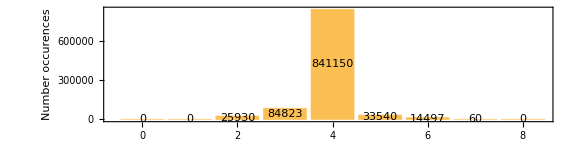

{0.,0.,2.593,8.4823,84.115,3.354,1.4497,0.006,0.}

```mathematica
dpCountTally={0,0,25930,84823,841150,33540,14497,60,0,0,0,0,0,0,0,0,0};
(*BarChart[N[dpCountTally[[1;;9]]/Total[dpCountTally]*100],ChartLabels->{"0","1","2","3","4","5","6","7","8"},LabelingFunction->Center,FrameLabel->{"Valid Solutions","no limit"},Frame->True]*)
BarChart[dpCountTally[[1;;9]],ChartLabels->{"0","1","2","3","4","5","6","7","8"},LabelingFunction->Center,FrameLabel->{"Valid Solutions","Number occurences"},Frame->True,AspectRatio->1/4,ImageSize->Large]
N[dpCountTally[[1;;9]]/Total[dpCountTally]*100]
```

```mathematica
Total[{84.115,3.354,1.4497,0.006}]
```

88.9247

```mathematica
Total[{2.593,8.4823}]
```

11.0753

## Where are the errors -- in 9 of these cases, copying them over we get more solutions (loss of precision), so really only 19 cases.

```mathematica
(*91678.) 0 pos answers,x2={2.94095,-1.79456,2.84331},v2={0.540945,-0.330048,-0.773594},v2lat=-0.884493,v2lon=-0.547836
113309.) 0 pos answers,x2={-0.0941583,-1.16552,2.81407},v2={0.0805185,0.996723,-0.00771452},v2lat=-0.0077146,v2lon=1.490188204002161
167957.) 1 pos answers,x2={-1.15764,1.51481,-3.28605},v2={-0.606839,0.794104,-0.0338434},v2lat=-0.0338499,v2lon=2.223311723627517
173838.) 0 pos answers,x2={2.47914,-3.77396,2.78534},v2={-0.446095,0.679198,0.582829},v2lat=0.6222055981910902,v2lon=2.151935288883279
207713.) 0 pos answers,x2={-0.942853,-2.98582,3.99601},v2={0.185624,0.587807,0.787418},v2lat=0.9066091427049847,v2lon=1.2649163689977738
216901.) 1 pos answers,x2={-1.57942,-1.60895,0.930537},v2={0.451773,0.460199,0.764276},v2lat=0.8699178475408378,v2lon=0.7946379323953762
369849.) 1 pos answers,x2={-2.86691,-2.99187,-2.46301},v2={-0.618548,-0.645443,-0.448108},v2lat=-0.464648,v2lon=-2.33492
371695.) 1 pos answers,x2={-3.98758,3.29712,0.74257},v2={-0.709965,0.587099,0.388929},v2lat=0.399468362594755,v2lon=2.4506388936942374
392793.) 0 pos answers,x2={3.04114,-3.89764,-3.45901},v2={-0.368215,0.472014,-0.801012},v2lat=-0.928984,v2lon=2.2332812008511986
571894.) 0 pos answers,x2={-3.85491,-2.54014,-0.63281},v2={-0.723759,-0.476922,0.498716},v2lat=0.5221168850307005,v2lon=-2.55895
573080.) 1 pos answers,x2={-1.3994,3.80999,-2.68194},v2={0.343536,-0.935397,0.0837596},v2lat=0.08385781582306258,v2lon=-1.21883
579811.) 1 pos answers,x2={-1.69071,-1.01329,-3.73202},v2={0.681805,0.408665,-0.606742},v2lat=-0.651955,v2lon=0.539968638544609
586771.) 1 pos answers,x2={2.56776,3.10299,3.36041},v2={-0.636535,-0.769194,0.0562414},v2lat=0.056271110752505835,v2lon=-2.2621
604711.) 1 pos answers,x2={0.669272,0.864604,0.702067},v2={0.0493681,0.0637795,0.996742},v2lat=1.4900548102324898,v2lon=0.9120844955945765
613520.) 1 pos answers,x2={-2.83822,2.45937,-2.03565},v2={0.755759,-0.654771,-0.010172},v2lat=-0.0101722,v2lon=-0.713925
630955.) 0 pos answers,x2={1.87779,3.44127,-1.03384},v2={-0.44137,-0.808859,0.38851},v2lat=0.3990136052423077,v2lon=-2.07031
631665.) 1 pos answers,x2={-2.46127,-2.02472,-2.38417},v2={-0.697438,-0.57367,0.429513},v2lat=0.443953945510699,v2lon=-2.45326
660597.) 0 pos answers,x2={2.74197,-2.92189,-2.5201},v2={-0.667231,0.710939,-0.22219},v2lat=-0.224061,v2lon=2.32449082133245
735132.) 0 pos answers,x2={2.30996,3.32794,-2.43581},v2={-0.488512,-0.703779,0.515802},v2lat=0.5419430688123803,v2lon=-2.17757
757320.) 1 pos answers,x2={-2.10727,2.12764,-2.41992},v2={0.271069,-0.273656,-0.92284},v2lat=-1.17539,v2lon=-0.790146
842146.) 0 pos answers,x2={0.202494,2.69465,1.78003},v2={0.070498,0.938268,-0.338648},v2lat=-0.34548,v2lon=1.4958009573350517
881507.) 1 pos answers,x2={-0.471799,0.810149,0.377825},v2={-0.474652,0.815256,-0.331757},v2lat=-0.338166,v2lon=2.0980338885410212
917211.) 1 pos answers,x2={3.32402,2.17009,-0.101226},v2={-0.682491,-0.445596,-0.579353},v2lat=-0.617935,v2lon=-2.56318
933831.) 1 pos answers,x2={-2.73171,2.50157,-3.54173},v2={-0.668277,0.61201,-0.422906},v2lat=-0.43665,v2lon=2.400114923360918
983984.) 1 pos answers,x2={-0.565116,2.05653,-1.78572},v2={-0.221588,0.806291,-0.548446},v2lat=-0.580505,v2lon=1.8389988574256066
988010.) 1 pos answers,x2={-2.65187,-3.84269,-2.52185},v2={0.47569,0.689194,0.546562},v2lat=0.5782533004942731,v2lon=0.9666692836764863
988181.) 0 pos answers,x2={1.40342,-0.511436,-3.61839},v2={0.455195,-0.165884,-0.874803},v2lat=-1.06503,v2lon=-0.349466
998684.) 1 pos answers,x2={0.952603,1.59312,0.505646},v2={0.255516,0.42747,-0.867168},v2lat=-1.04949,v2lon=1.0320400403017413*)
```

```mathematica
errcasesx2andv2 = {
{{2.94095,-1.79456,2.84331},v2={0.540945,-0.330048,-0.773594}},
{{-0.0941583,-1.16552,2.81407},v2={0.0805185,0.996723,-0.00771452}},
{{-1.15764,1.51481,-3.28605},v2={-0.606839,0.794104,-0.0338434}},
{{2.47914,-3.77396,2.78534},v2={-0.446095,0.679198,0.582829}},
{{-0.942853,-2.98582,3.99601},v2={0.185624,0.587807,0.787418}},
{{-1.57942,-1.60895,0.930537},v2={0.451773,0.460199,0.764276}},
{{-2.86691,-2.99187,-2.46301},v2={-0.618548,-0.645443,-0.448108}},
{{-3.98758,3.29712,0.74257},v2={-0.709965,0.587099,0.388929}},
{{3.04114,-3.89764,-3.45901},v2={-0.368215,0.472014,-0.801012}},
{{-3.85491,-2.54014,-0.63281},v2={-0.723759,-0.476922,0.498716}},
{{-1.3994,3.80999,-2.68194},v2={0.343536,-0.935397,0.0837596}},
{{-1.69071,-1.01329,-3.73202},v2={0.681805,0.408665,-0.606742}},
{{2.56776,3.10299,3.36041},v2={-0.636535,-0.769194,0.0562414}},
{{0.669272,0.864604,0.702067},v2={0.0493681,0.0637795,0.996742}},
{{-2.83822,2.45937,-2.03565},v2={0.755759,-0.654771,-0.010172}},
{{1.87779,3.44127,-1.03384},v2={-0.44137,-0.808859,0.38851}},
{{-2.46127,-2.02472,-2.38417},v2={-0.697438,-0.57367,0.429513}},
{{2.74197,-2.92189,-2.5201},v2={-0.667231,0.710939,-0.22219}},
{{2.30996,3.32794,-2.43581},v2={-0.488512,-0.703779,0.515802}},
{{-2.10727,2.12764,-2.41992},v2={0.271069,-0.273656,-0.92284}},
{{0.202494,2.69465,1.78003},v2={0.070498,0.938268,-0.338648}},
{{-0.471799,0.810149,0.377825},v2={-0.474652,0.815256,-0.331757}},
{{3.32402,2.17009,-0.101226},v2={-0.682491,-0.445596,-0.579353}},
{{-2.73171,2.50157,-3.54173},v2={-0.668277,0.61201,-0.422906}},
{{-0.565116,2.05653,-1.78572},v2={-0.221588,0.806291,-0.548446}},
{{-2.65187,-3.84269,-2.52185},v2={0.47569,0.689194,0.546562}},
{{1.40342,-0.511436,-3.61839},v2={0.455195,-0.165884,-0.874803}},
{{0.952603,1.59312,0.505646},v2={0.255516,0.42747,-0.867168}}};
```

```mathematica
Table[
x2=x2andv2[[1]];
v2=x2andv2[[2]];
(*(Cross[{0,0,1},x2].v2==0)*)
(*Chop[Cross[{0,0,1},x2].v2,0.0001]*)

solutionSets=getThetaAndD3SolutionsV3[x2,v2,diagΣp,diagΣpExpanded,PMat,QMat];
Print["                   solution sets:  "];
Print["     θ1,      θ2,       d3,        θ4,       θ5"];
Print[MatrixForm[solutionSets]];
numPos =Count[solutionSets[[;;,3]],u_/;u>=0], {x2andv2 ,errcasesx2andv2}]
```

Not a 2D case, but called 2D function!  Cross[{0,0,1},xg].vg = 0.000103594

solution sets:

θ1,      θ2,       d3,        θ4,       θ5

(2.59371 | -1.97131 | 5.66733 | -3.14159 | -0.483982
2.59371 | -2.7356 | 4.6444 | 0. | -0.28031
5.7353 | 2.69345 | 3.85796 | -3.14159 | -0.238156
5.7353 | 1.63457 | 3.3531 | 0. | -0.820719)

Not a 2D case, but called 2D function!  Cross[{0,0,1},xg].vg = -3.82113×10^-6

solution sets:

θ1,      θ2,       d3,        θ4,       θ5

(1.49018 | -2.26551 | 2.8338 | -3.14159 | 0.686998
1.49018 | -3.09971 | 3.90121 | 0. | -1.5212
4.63178 | 3.09925 | 3.81746 | -3.14159 | -1.52074)

Not a 2D case, but called 2D function!  Cross[{0,0,1},xg].vg = -0.000040769

solution sets:

θ1,      θ2,       d3,        θ4,       θ5

(5.36493 | -0.60135 | 5.19721 | -3.14159 | -1.0033
5.36493 | -1.47456 | 3.0791 | 0. | 0.130091
2.22333 | 0.364579 | 2.44749 | -3.14159 | 1.24007
2.22333 | -0.257319 | 3.90507 | 0. | -1.86197)

Not a 2D case, but called 2D function!  Cross[{0,0,1},xg].vg = 0.000282244

solution sets:

θ1,      θ2,       d3,        θ4,       θ5

(2.15201 | -1.95125 | 5.31244 | -3.14159 | 1.00266
2.15201 | -2.39019 | 6.79217 | 0. | -1.4416
5.2936 | 2.29128 | 5.4535 | -3.14159 | -1.34269
5.2936 | 1.56147 | 2.91406 | 0. | 0.612882)

Not a 2D case, but called 2D function!  Cross[{0,0,1},xg].vg = 0.0000242583

solution sets:

θ1,      θ2,       d3,        θ4,       θ5

(1.26493 | -2.36153 | 4.75417 | -3.14159 | 1.69734
1.26493 | -2.62522 | 6.43947 | 0. | -1.96104
4.40652 | 2.57743 | 5.45825 | -3.14159 | -1.91324
4.40652 | 2.18089 | 3.03764 | 0. | 1.51671)

Not a 2D case, but called 2D function!  Cross[{0,0,1},xg].vg = 0.0000326638

solution sets:

θ1,      θ2,       d3,        θ4,       θ5

(0.79466 | -1.685 | 2.50667 | -3.14159 | 0.984121
0.79466 | -2.42613 | 3.82537 | 0. | -1.72525
3.93625 | 2.23344 | 2.56084 | -3.14159 | -1.53256)

Not a 2D case, but called 2D function!  Cross[{0,0,1},xg].vg = -0.000188214

solution sets:

θ1,      θ2,       d3,        θ4,       θ5

(0.806724 | -1.03013 | 6.52211 | -3.14159 | -1.00532
0.806724 | -1.66417 | 4.52887 | 0. | 0.371276
3.94832 | 1.04367 | 3.11901 | -3.14159 | 0.991777
3.94832 | 0.400228 | 4.49117 | 0. | -1.63522)

Not a 2D case, but called 2D function!  Cross[{0,0,1},xg].vg = -0.00026443

solution sets:

θ1,      θ2,       d3,        θ4,       θ5

(5.59229 | -1.53992 | 5.78798 | -3.14159 | 0.36859
5.59229 | -2.11894 | 6.46856 | 0. | -0.947617
2.45069 | 1.92045 | 4.85696 | -3.14159 | -0.749118
2.45069 | 0.967633 | 3.21867 | 0. | -0.203695)

Not a 2D case, but called 2D function!  Cross[{0,0,1},xg].vg = 0.000291143

solution sets:

θ1,      θ2,       d3,        θ4,       θ5

(2.23338 | -1.0292 | 7.87119 | -3.14159 | -1.47058
2.23338 | -1.40998 | 5.53434 | 0. | 1.0898
5.37497 | 0.832393 | 4.24949 | -3.14159 | 1.66739
5.37497 | 0.537193 | 5.91412 | 0. | -1.96259)

Not a 2D case, but called 2D function!  Cross[{0,0,1},xg].vg = 0.0000422008

solution sets:

θ1,      θ2,       d3,        θ4,       θ5

(0.582632 | -1.28577 | 5.33302 | -3.14159 | 0.237086
0.582632 | -1.94196 | 5.78371 | 0. | -0.893283
3.72422 | 1.62759 | 4.12192 | -3.14159 | -0.578906
3.72422 | 0.506117 | 2.82306 | 0. | -0.542562)

Not a 2D case, but called 2D function!  Cross[{0,0,1},xg].vg = 0.000125837

solution sets:

θ1,      θ2,       d3,        θ4,       θ5

(5.06439 | -0.934135 | 6.18728 | -3.14159 | -0.552803
5.06439 | -1.63263 | 5.02865 | 0. | -0.145688
1.9228 | 1.07852 | 3.56606 | -3.14159 | 0.408423
1.9228 | 0.243608 | 4.28743 | 0. | -1.24333)

Not a 2D case, but called 2D function!  Cross[{0,0,1},xg].vg = -0.0000678137

solution sets:

θ1,      θ2,       d3,        θ4,       θ5

(0.539925 | -0.668829 | 5.77009 | -3.14159 | -1.55392
0.539925 | -1.23689 | 3.19639 | 0. | 0.985866
3.68152 | 0.123424 | 2.95964 | -3.14159 | 2.09933
3.68152 | -0.0949671 | 4.3569 | 0. | -2.31772)

Not a 2D case, but called 2D function!  Cross[{0,0,1},xg].vg = 0.0000561542

solution sets:

θ1,      θ2,       d3,        θ4,       θ5

(4.0211 | -2.01434 | 5.50399 | -3.14159 | 0.499814
4.0211 | -2.58284 | 6.39103 | 0. | -1.06832
0.879504 | 2.52585 | 5.33945 | -3.14159 | -1.01132
0.879504 | 1.68748 | 3.22618 | 0. | 0.172956)

Not a 2D case, but called 2D function!  Cross[{0,0,1},xg].vg = 1.97679×10^-6

solution sets:

θ1,      θ2,       d3,        θ4,       θ5

(4.05365 | -2.08634 | 1.26046 | -3.14159 | 2.0056
4.05365 | -2.4971 | 2.48223 | 0. | -2.41636
0.912062 | 2.19351 | 1.34201 | -3.14159 | -2.11277)

Not a 2D case, but called 2D function!  Cross[{0,0,1},xg].vg = -0.000306864

solution sets:

θ1,      θ2,       d3,        θ4,       θ5

(5.56918 | -1.00364 | 5.65038 | -3.14159 | -0.577331
5.56918 | -1.78031 | 4.42618 | 0. | -0.199339
2.42759 | 1.21005 | 2.93422 | -3.14159 | 0.370919
2.42759 | 0.230229 | 3.58664 | 0. | -1.35074)

Not a 2D case, but called 2D function!  Cross[{0,0,1},xg].vg = 5.99829×10^-6

solution sets:

θ1,      θ2,       d3,        θ4,       θ5

(4.21288 | -1.16346 | 4.93557 | -3.14159 | -0.00831859
4.21288 | -1.93581 | 4.91891 | 0. | -0.764024
1.07129 | 1.53684 | 3.31068 | -3.14159 | -0.365058
1.07129 | 0.237762 | 2.49658 | 0. | -0.93402)

Not a 2D case, but called 2D function!  Cross[{0,0,1},xg].vg = -0.000159906

solution sets:

θ1,      θ2,       d3,        θ4,       θ5

(0.68839 | -0.85206 | 4.9925 | -3.14159 | -0.274783
0.68839 | -1.68556 | 4.41661 | 0. | -0.558713
3.82998 | 1.05571 | 3.00668 | -3.14159 | 0.071128
3.82998 | -0.0753447 | 3.14561 | 0. | -1.20219)

Not a 2D case, but called 2D function!  Cross[{0,0,1},xg].vg = -0.000202177

solution sets:

θ1,      θ2,       d3,        θ4,       θ5

(2.32444 | -0.981604 | 6.28967 | -3.14159 | -0.813252
2.32444 | -1.66753 | 4.61319 | 0. | 0.127327
5.46603 | 1.06425 | 3.1847 | -3.14159 | 0.730608
5.46603 | 0.312092 | 4.31778 | 0. | -1.48276)

Not a 2D case, but called 2D function!  Cross[{0,0,1},xg].vg = 0.0000372864

solution sets:

θ1,      θ2,       d3,        θ4,       θ5

(4.10563 | -0.942845 | 5.6044 | -3.14159 | -0.0860083
4.10563 | -1.64731 | 5.42987 | 0. | -0.618456
0.964034 | 1.15402 | 3.90078 | -3.14159 | -0.125165
0.964034 | 0.154058 | 3.64256 | 0. | -0.874795)

Not a 2D case, but called 2D function!  Cross[{0,0,1},xg].vg = -0.000070168

solution sets:

θ1,      θ2,       d3,        θ4,       θ5

(5.49298 | -1.05239 | 5.66123 | -3.14159 | -1.69379
5.49298 | -1.55953 | 3.09446 | 0. | 1.18666
2.35138 | 0.484791 | 2.29973 | -3.14159 | 2.2614
2.35138 | 0.288143 | 3.5185 | 0. | -2.45804)

Not a 2D case, but called 2D function!  Cross[{0,0,1},xg].vg = 0.0000262047

solution sets:

θ1,      θ2,       d3,        θ4,       θ5

(4.63738 | -1.77554 | 4.1271 | -3.14159 | -0.140733
4.63738 | -2.73153 | 3.83632 | 0. | -0.815256
1.49579 | 2.67703 | 3.04351 | -3.14159 | -0.76075
1.49579 | 0.826327 | 0.932402 | 0. | -1.08995)

Not a 2D case, but called 2D function!  Cross[{0,0,1},xg].vg = -0.0000981224

solution sets:

θ1,      θ2,       d3,        θ4,       θ5

(5.23974 | -1.32656 | 2.33868 | -3.14159 | -0.582406
5.23974 | 2.73039 | 0.569213 | 0. | -1.64383
2.09814 | -2.85161 | 1.37876 | -3.14159 | -1.52262)

Not a 2D case, but called 2D function!  Cross[{0,0,1},xg].vg = -0.000103122

solution sets:

θ1,      θ2,       d3,        θ4,       θ5

(3.71997 | -1.40714 | 5.62418 | -3.14159 | -0.781586
3.71997 | -2.19835 | 3.97298 | 0. | -0.00961463
0.578377 | 1.86101 | 2.49465 | -3.14159 | 0.327725
0.578377 | 0.740977 | 3.07169 | 0. | -1.44775)

Not a 2D case, but called 2D function!  Cross[{0,0,1},xg].vg = -0.0000921422

solution sets:

θ1,      θ2,       d3,        θ4,       θ5

(5.54174 | -0.856201 | 6.78746 | -3.14159 | -1.15124
5.54174 | -1.42811 | 4.61243 | 0. | 0.579332
2.40014 | 0.713442 | 3.48566 | -3.14159 | 1.294
2.40014 | 0.23606 | 5.05587 | 0. | -1.77139)

Not a 2D case, but called 2D function!  Cross[{0,0,1},xg].vg = 0.0000544249

solution sets:

θ1,      θ2,       d3,        θ4,       θ5

(4.98056 | -0.951902 | 4.51948 | -3.14159 | -1.1994
4.98056 | -2.03178 | 1.89217 | 0. | 0.119519
1.83897 | 0.551645 | 1.11492 | -3.14159 | 1.59966
1.83897 | -0.127102 | 2.38765 | 0. | -2.2784)

Not a 2D case, but called 2D function!  Cross[{0,0,1},xg].vg = 0.000276313

solution sets:

θ1,      θ2,       d3,        θ4,       θ5

(0.96674 | -0.99035 | 6.12561 | -3.14159 | -0.00219317
0.96674 | -1.62194 | 6.12122 | 0. | -0.629402
4.10833 | 1.19065 | 4.53955 | -3.14159 | -0.198106
4.10833 | 0.297616 | 4.12719 | 0. | -0.694926)

Not a 2D case, but called 2D function!  Cross[{0,0,1},xg].vg = -1.81326×10^-6

solution sets:

θ1,      θ2,       d3,        θ4,       θ5

(2.79213 | -0.687423 | 5.30852 | -3.14159 | -1.9484
2.79213 | -1.07968 | 2.90555 | 0. | 1.55615
5.93372 | -0.12101 | 3.157 | -3.14159 | 2.75684
5.93372 | -0.158777 | 3.83489 | 0. | -2.7946)

Not a 2D case, but called 2D function!  Cross[{0,0,1},xg].vg = 0.000141554

solution sets:

θ1,      θ2,       d3,        θ4,       θ5

(4.17348 | -1.57285 | 3.72338 | -3.14159 | -1.04744
4.17348 | 3.13054 | 0.981626 | 0. | -0.532356
1.03189 | -3.13067 | 1.00372 | -3.14159 | -0.532235)

{4,3,4,4,4,3,4,4,4,4,4,4,4,3,4,4,4,4,4,4,4,3,4,4,4,4,4,3}

```mathematica
Max@Abs[{0.00010359360000000706,-3.821130900014125*^-6,-0.00004076897000004909,0.0002822435199998363,0.000024258308999991485,0.00003266376999999654,-0.00018821362999998925,-0.00026442962000006176,0.0002911433599999125,0.00004220075999983308,0.00012583716000014178,-0.00006781369999997455,0.00005615420999993681,1.9767916000015817*^-6,-0.0003068642099997021,5.998289999809003*^-6,-0.00015990645999997,-0.00020217676000022777,0.00003728644000000614,-0.00007016803999992938,0.000026204691999986984,-0.00009812239599998884,-0.00010312172999982216,-0.00009214220999997913,0.0000544248840000372,0.00027631332000011,-1.8132599999831633*^-6,0.00014155448999997322}]
```

0.000306864

## Draw 7 solutions

```mathematica
drawDubin3DPathSim[{ϕ1_,θ1_,d_,ϕ2_,θ2_},color_]:=Module[{x1 = {0,0,0},r=1,
o1 ,p1,x, xp,p2,o2,t1,t2,op=0.2,rot2,
v1={0,0,1},x2,v2,p2p,y2,rotMatθ2,rotMatV2},
o1 =r*{ Cos[ϕ1], Sin[ϕ1],0};  (*Center of arc 1: *)
p1 = x1 + r*{ (1-Cos[θ1])Cos[ϕ1],(1-Cos[θ1]) Sin[ϕ1],Sin[θ1]};  (*ending point of first arc*)
x = { Sin[θ1]Cos[ϕ1],Sin[θ1] Sin[ϕ1],Cos[θ1]}; (*Orientation of straight segment*)
xp =o1-p1; (*Perpendicular to x, pointing to circle center, length r*)
p2 = p1+d*x; (*End of straight segment*)
o2 =p2+ RotationMatrix[ϕ2,x].xp; (*center of circle 2*)
y2 = o2-p2;(*from straight segment end to circle 2 center *)
p2p = Cross[x,y2]; (*Perpendicular*)
rotMatθ2 =RotationMatrix[θ2,p2p]; 
v2 = rotMatθ2.x;(*final orientation*)
rotMatV2 =RotationMatrix[θ2,x]; 
x2 =o2-rotMatθ2.y2;

(*t2 = ParametricPlot3D[x2+RotationMatrix[{v1,v2}].{r (1 + Cos[v]) Sin[u],  r(1 + Cos[v]) Cos[u], 
    r Sin[v]}, {u, 0, 2 Pi}, {v, 0,2  Pi}, PlotStyle -> {Opacity[op]},MeshStyle->Opacity[0.2]];*)

 {
(*Starting vector*)
(*t2[[1]],*)
{Darker[Green], Arrow[Tube[{x1,x1+v1}]]},
If[θ1>0,{Thick,color, Rotate[Rotate[splineCircle[x1+{r,0,0},r,{π-θ1,π}],π/2,{r,0,0},x1],ϕ1,v1,x1]}],
{Red,Arrow[Tube[{x2,x2+v2}]]},
{Thick,color,
{Thick,Line[{p1,p1+d x}]},(*{Thin,Arrow[{p1,p1+x}]},*)
If[θ2>0,Line[Table[o2-RotationMatrix[a,p2p].y2,{a,0,θ2,θ2/40}]]]}
}
]

drawDubin3DTori[{ϕ1_,θ1_,d_,ϕ2_,θ2_}]:=Module[{x1 = {0,0,0},r=1,
o1 ,p1,x, xp,p2,o2,t1,t2,op,rot2,
v1={0,0,1},x2,v2,p2p,y2,rotMatθ2,rotMatV2},
o1 =r*{ Cos[ϕ1], Sin[ϕ1],0};  (*Center of arc 1: *)
p1 = x1 + r*{ (1-Cos[θ1])Cos[ϕ1],(1-Cos[θ1]) Sin[ϕ1],Sin[θ1]};  (*ending point of first arc*)
x = { Sin[θ1]Cos[ϕ1],Sin[θ1] Sin[ϕ1],Cos[θ1]}; (*Orientation of straight segment*)
xp =o1-p1; (*Perpendicular to x, pointing to circle center, length r*)
p2 = p1+d*x; (*End of straight segment*)
o2 =p2+ RotationMatrix[ϕ2,x].xp; (*center of circle 2*)
y2 = o2-p2;(*from straight segment end to circle 2 center *)
p2p = Cross[x,y2]; (*Perpendicular*)
rotMatθ2 =RotationMatrix[θ2,p2p]; 
v2 = rotMatθ2.x;(*final orientation*)
rotMatV2 =RotationMatrix[θ2,x]; 
x2 =o2-rotMatθ2.y2;
op = 0.05;


t2 = ParametricPlot3D[x2+RotationMatrix[{v1,v2}].{r (1 + Cos[v]) Sin[u],  r(1 + Cos[v]) Cos[u], 
    r Sin[v]}, {u, 0, 2 Pi}, {v, 0,2  Pi}, PlotStyle -> {Opacity[op]},MeshStyle->Opacity[0.2]];

t1 = ParametricPlot3D[{r (1 + Cos[v]) Sin[u],  r(1 + Cos[v]) Cos[u], 
    r Sin[v]}, {u, 0, 2 Pi}, {v, 0,  2Pi}, PlotStyle -> {Opacity[op]},MeshStyle->Opacity[0.2]];

 {t1[[1]],t2[[1]]}
]

(*9018.) 7 pos answers,x2={2.64101,-1.78042,-0.371051},v2={{-0.323321},{0.729589},{0.602631}},v2lat={2.4948},v2lon={-1.15365}*)
sevenAns9018 = {
(*{-0.652247,-1.4358-2.90038,-2.63505, 2.22979},
 {2.59572, 1.86885,-3.51042,-2.2706,-2.50344},*)
{-1.25417, 0.938164, 1.52235,-1.7745,-0.0818625},
{ 2.7849,-1.9931, 4.54963,-0.632774,-1.30598},
{-0.358314,-0.505268, 0.275763, 0.630636,-1.31096},
{-0.276758,-0.268065, 0.715988, 0.755156,-1.10858},
(* {2.51337, 1.9222,-4.57283, 0.884068, 2.59755},*)
{-0.20522,-0.104401, 1.00058, 0.889723,-0.987391},
{-0.185223, 1.3487, 2.77721, 2.20947,-0.959664},
 {2.25837,-1.31581, 3.57088, 2.64045, 0.459771}};
colors = ColorData[97,"ColorList"];
sevenAns = sevenAns9018;

Graphics3D[
{drawDubin3DTori[convertDHToDubins[sevenAns[[1]]]],
Table[ {drawDubin3DPathSim[convertDHToDubins[sevenAns[[i]]],colors[[i]]]},{i, Length[sevenAns]}]},Boxed->False(*,PlotLabel->StringForm["All `` solutions to `` , `` = ``", Length[sevenAns], MatrixForm@{2.64101,-1.78042,-0.371051}, MatrixForm@{"lat","lon"}, MatrixForm@{2.4948,-1.15365} ]*)]
```

-Graphics3D-

```mathematica
5+15+20+15+10+5
```

70

## Distance plots

```mathematica
shortestSolution[sols_]:=Module[{shortestSolLen,solLen},shortestSolLen=∞;
Table[If[sol[[3]]>=0,solLen=Abs@sol[[3]]+Abs@(π-sol[[2]])+Abs@(π-sol[[5]]);
If[solLen<shortestSolLen,shortestSolLen=solLen]];,{sol,sols}];
shortestSolLen]
epsilon = 0.00001;
step = 0.05;
Timing[dataPlotDist1 = Table[ 
x2={x+epsilon,0.0,z+epsilon};
v2=N[{0.0,1.0,0.0}];
solutionSets=getThetaAndD3SolutionsV3[x2,v2,diagΣp,diagΣpExpanded,PMat,QMat];
shortestSolution[solutionSets],{x,-4.0,4.0,step},{z,-4.0,4.0,step}
]]
```

Not a 2D case, but called 2D function!  Cross[{0,0,1},xg].vg = 0.00001

Not a 2D case, but called 2D function!  Cross[{0,0,1},xg].vg = 0.00001

Not a 2D case, but called 2D function!  Cross[{0,0,1},xg].vg = 0.00001

«158 more identical outputs»

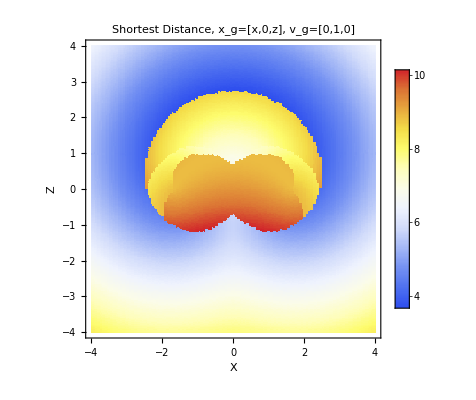

```mathematica
nums = Table[ 
{x,z},{x,-4.0,4.0,step},{z,-4.0,4.0,step}
];
d = Dimensions[nums];
colorscheme = "TemperatureMap";
dataPlotDistxz =Table[  {nums[[x,z,1]],nums[[x,z,2]],dataPlotDist1[[x,z]]} ,{x,d[[1]]} ,{z,d[[2]]} ];
ListDensityPlot[Flatten[dataPlotDistxz,1],PlotRange->All,InterpolationOrder->0,FrameLabel->{"X","Z"},PlotLegends->Placed[Automatic,{0.9,0.5}],ColorFunction->colorscheme,
(*ColorFunction->(ColorData["TemperatureMap"][Rescale[#,{2,13}]]&),ColorFunctionScaling->False,*)
PlotLabel->StringForm["Shortest Distance, x_g=[x,0,z], v_g=[0,1,0]"]]
```

```mathematica
epsilon = 0.00001;
step = 0.05;
Timing[dataPlotDist2 = Table[ 
x2={x+epsilon,0.5,z+epsilon};
v2=N[{0.5,1.0,0.0}];
solutionSets=getThetaAndD3SolutionsV3[x2,v2,diagΣp,diagΣpExpanded,PMat,QMat];
shortestSolution[solutionSets],{x,-4.0,4.0,step},{z,-4.0,4.0,step}
]]
```

Not a 2D case, but called 2D function!  Cross[{0,0,1},xg].vg = 0.00001

Not a 2D case, but called 2D function!  Cross[{0,0,1},xg].vg = 0.00001

Not a 2D case, but called 2D function!  Cross[{0,0,1},xg].vg = 0.00001

«158 more identical outputs»

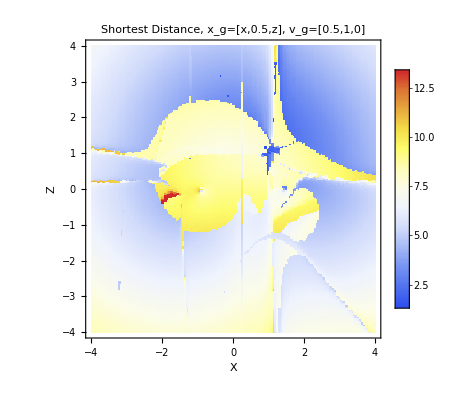

```mathematica
nums = Table[ 
{x,z},{x,-4.0,4.0,step},{z,-4.0,4.0,step}
];
d = Dimensions[nums];
colorscheme = "TemperatureMap";
dataPlotDistxz =Table[  {nums[[x,z,1]],nums[[x,z,2]],dataPlotDist2[[x,z]]} ,{x,d[[1]]} ,{z,d[[2]]} ];
ListDensityPlot[Flatten[dataPlotDistxz,1],PlotRange->All,InterpolationOrder->0,FrameLabel->{"X","Z"},PlotLegends->Placed[Automatic,{0.1,0.3}],ColorFunction->colorscheme,

(*ColorFunction->(ColorData["TemperatureMap"][Rescale[#,{2,13}]]&),ColorFunctionScaling->False,*)PlotLabel->StringForm["Shortest Distance, x_g=[x,0.5,z], v_g=[0.5,1,0]"]]
```